```mathematica
SetDirectory[NotebookDirectory[]]
<<"PLOT.wl"
```

C:\Users\Rick\Desktop

## plot

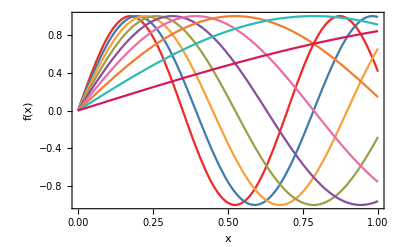

```mathematica
plot[Table[Sin[n x],{n,9,1,-1}],{x,0,1},
FrameLabel->{"x","f(x)"}]
```

## logplot

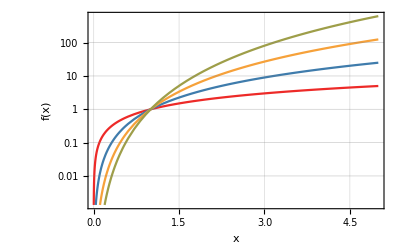

```mathematica
logplot[Table[x^n,{n,1,4}],{x,0,5},
FrameLabel->{"x","f(x)"},
GridLines->Automatic]
```

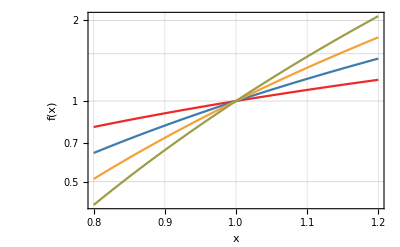

```mathematica
logplot[Table[x^n,{n,1,4}],{x,0.8,1.2},
FrameLabel->{"x","f(x)"},
additionalticks->{1,2,4,6,8},
GridLines->Automatic]
```

## loglogplot

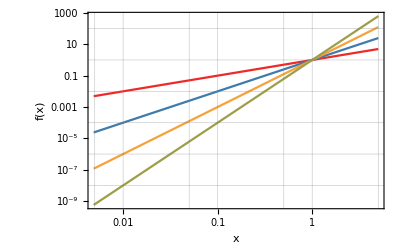

```mathematica
loglogplot[Table[x^n,{n,1,4}],{x,0,5},
FrameLabel->{"x","f(x)"},
GridLines->Automatic]
```

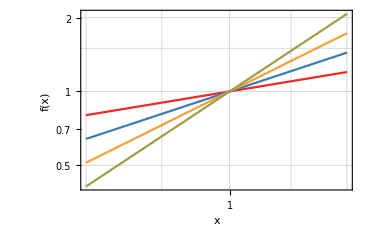

```mathematica
loglogplot[Table[x^n,{n,1,4}],{x,0.8,1.2},
FrameLabel->{"x","f(x)"},
additionalticks->{{2,3,4,5,6,7,8,9},{1,2,4,6,8}},
GridLines->Automatic]
```

## listplot

```mathematica
datalistplot=Accumulate/@RandomReal[{-0.01,0.015},{6,100}];
```

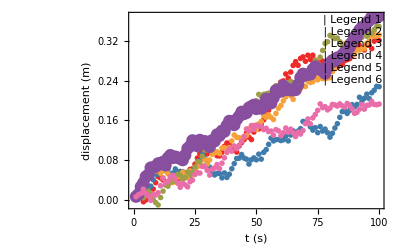

```mathematica
listplot[datalistplot,
PlotLegends->{{"Legend 1","Legend 2","Legend 3","Legend 4","Legend 5","Legend 6"},{{0,0},0}},
FrameLabel->{"t (s)","displacement (m)"}]
```

## listlogplot

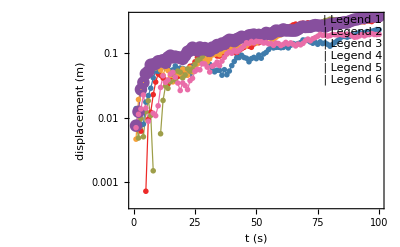

```mathematica
listlogplot[datalistplot,GridLines->Automatic,
Joined->True,
PlotLegends->{{"Legend 1","Legend 2","Legend 3","Legend 4","Legend 5","Legend 6"},{{0,0},0}},
additionalticks->{1,5},
FrameLabel->{"t (s)","displacement (m)"}]
```

## listloglogplot

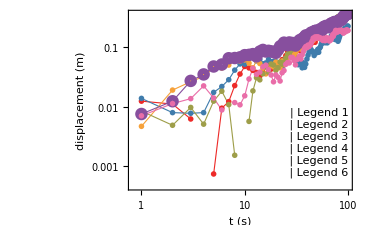

```mathematica
listloglogplot[datalistplot,
Joined->True,
PlotLegends->{{"Legend 1","Legend 2","Legend 3","Legend 4","Legend 5","Legend 6"},{{2,94},2}},
additionalticks->{{},{}},
FrameLabel->{"t (s)","displacement (m)"}]
```

## listlineplot

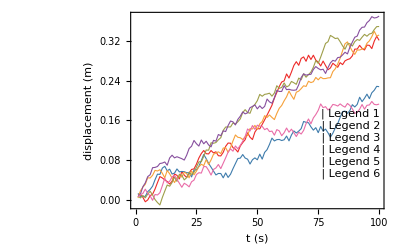

```mathematica
listlineplot[datalistplot,
PlotLegends->{{"Legend 1","Legend 2","Legend 3","Legend 4","Legend 5","Legend 6"},{{2,94},2}},
FrameLabel->{"t (s)","displacement (m)"}]
```

## listdensityplot

### datalistdensityplot

```mathematica
datalistdensityplot=Uncompress@"1:eJyE3XlUTd//x/EQEpKZiCJkLGQuXZlSyhSSTPEhRLmZFUUyhUwhhMg8y5wkZMqUNJCIzJlKoQzf22et+9rf+9nrfd/98/t81++5Svfuc87e+3HuydTDe+D4u8E6Or66Ojo6fSf6Th9fSuf//peyqfvq+PxfY+KUZQI3dF/RY2ScMunA33qV3KvZUuGXvQmOHd6NiFPatmxeb15nczJ8U7T/a9JKVZhTZPi87qPWZPigwZOf89uowlWLVry0uN2GDM/3qVCyeap7nHJsiu3qI31bkeFuHxv91HmqcMaQMwkvG1Uhw5Ubp1ZZZKIK+7oeH228usElKpwVu93I4trwOOXbF1tW9YhqQ4beVRbF3ZqoCp1S39a8GNKaDF07Rd+YaaAKZ8Yfmj2gTmMytBv96n6Dk25xym8xc3OWt6tDhs2X1Ei/O1QVpq39R9kkoRoZVjvSO2vur2FxSv2LXzPubqTDP8mz3zXeqQqjw9+vqdWtFhn++173VIUtVmY6zTSgX8c9+r0azXjvGqcMGuvyvNumJmTYIjn8tfFqVZg87u+ORSUakeG4xBGON9qqwt9+PRe4h1Qnw/cbTlSYljZUNcwGrJoXFPexKxX6jCp7t7a/KjzXps2FZ6a1ydGzb+itNldNVeGI2iY/oho1IMOWpvW/eSUMiVMuX7mxWnRoQzL8p/YL15qTVWGpVRatXr4wJcMPL9obxVVShad7+aWe/0mH0w6teOIZPThOWTJrT9MS3vXIcP9uZ0XVYarws/9Jq3gLAzK0mLqrRMxvF9XhuLRtD7ODJcgXfHzxV6QqHOe54O2CZjXIMMfiQpNKvVXhxeZPQ29kGpCh8meld2c+DIpTxnZzCPfX/Uu+hQe+Jjl5hKrC6OtTv01YQb8zlqqfXL6dKuzs0zdsUnIjMjwd5Hf/ZPrAOGXUmp1ly7yoSYaf/GzbjZyvCtdMvPnjVuWS5C8zvdf6gjINVeGQbY1+2Vg1JMODXYcOP359QJyyvMEEHYO7FmTYWu9QXTcvVdjecW3CvPb0uWeijnegbmVV2GjV2n3RhfS55/PNK3aHT/WPUx5ZWn5NYEIpMpyxrpbuEDdVeKe6q8/zkobkyzOs5pkHOn/6qU6UYaklXJsa0YfCgdEuA3urwneDa82/l2JChsUnir2hznHKJ22GmhROp68zz1uG7viR7qR6r2uUWLr1VkcyzInr1NChoSps4vmw3e823chw+PFLORFefVVn1MMXz+bWUpDhhB4Tvb+ccoxTdus7NtQ5yZIMU60+d+z51yFOWUJ5+bau9c9YKnx5fdOFMHtVWPCtZvdjB+n3+pObXde3a/qorjOJiiSbxTZkONLxRlmbJ/aq43bz2N1JlbqT4aTMactXmanCTkHVp7283JUM0+9+H/RySm/Vm7507dAbl+iT/asxO1OszvRSXTTHVHp226sZ+fJ8/eYwLFhHFQbk7qz7enN7Miy+Zj7p0zNOGVi//Lau7duRodfsuVEt1vVQHRNNEl72PWpFhhmeqoMmo3uc0njC2ZBNdm21z3saqcJ8ZV5mwhcLMsxbNWi6mbddnLJqsF16jSuvybPZ2AXpNnPOdotT6q5aPeWXm6X2yUcJVXh43BILz6JuZJhZstzy+o6KOOXN0onXqnv1IcPk5qpLkrltnPKqzqJvhVN70+fwAWfrLb5gE6f8mzx7oc1oepipLpnHWzlbxyl/nOo1+MhKczJUXQnPPHjeOU55dkKFoynW9OXjsuponefbKU5Zx6FugaledfIFTx81s1+9Mh3jlJtPb70xroA+U3xZfNPl8qb2quvMIsenAb86kOG98Y/eTGreLk45f72L2Wddejy+CTH/WDG2rerUXK72zrLv6B+dMMUq4Ez/Nqr3+kbzmC3u9Jkic92SxW4vLVWXh2ONe678SIcffE9VL/rQKk7ZLrvvqF1/WtDTmXZ3ujhXbhGnXNcm+obHIXqWkhbo22t9+6ZxSkPdZg36XKtFhmHdV3i9Gd44Tnly0vUNc6/SV4UOHfY0aRHYUDXPLjV63JANFclw+6s5PrP2mKjOVgrnL5GRdFjJfIty8cY6qitTqy6WKfXL01eFIDvdui+qxymPG5vPWtCzDBkez3q34UQLwzhl9+l+0bdnlyDDUv4N+q39pBunzK1kdDp8aj55XNtPeZE9v2zeJaVeZno//xEJ5Mn+xbviuetdW2VO1OHf0VN0yEOhzaEXKxN3Fdoq12369bGwYnkytO0849XJGD2FMmjbQcNzNekp1+SvTXUSqlZRKNs01Em1OF6RDMPXL5xqcbOmQpmz83jd1c3o73g4+KpN2HxjhTLL2vGw33E69Pu4uVGJcFOF0s3qRx3jzxXI0CmoYr+j080Uyt+lJ5cPG0T/1sYdVRfifk0UygZe25pV9qhEXzQ/qKYAzZoplAemNtW1TqEXFZbN9le9r9tSoRz8cm1I5RAjMixRfMp9ZqFQfskpnep7jw4brJoxrc6I1qqX5+r2oVdP0dNCfc8GXrNvtVEoFV9W3Ft/vSUZ5nZTnaY6WCmUX0c8S4pfSq9dq4658rB5VDuFMr7guLfRQDos6uxzd2mVDgqlb6fx2YXd6QuSsdu4Ls8WdFQoq0WsrpLdjZ66lraq3N76YyfVeDzg5FXtbzMyVJ1FLTe7dVENM4v8yVUnm5GhQcsT2z5ft1Yo84yS3Tu7lSHD72VGberbrqtC+efZq0717OmTVK3Gg0rvirRVKFdvavjGzcaYDHWKv5YqFMqyo5J7LdxOz3G/eQ3xP9K1m0LZ7E/T6pVn0Zsui1WLj2H5qvC7j9cijxX0OXzOu8aqVYCdQulzIubpxC/0Banczx0TTnp0VygTNnetPymTvsT9+ed79pjaPRTKmZ8bDf2ygp5J5aqWXIb3VWHKrEfrr1WlZ1ILX6jmrsE9Fcp+RoYXVg2iv6Pqal1jkk0vhXL/jpVLroygZ1JlVe9g9W+q8FTZV9uto0uTYdHtTzevHOitUEZeH27pakPPKVSz8N7KMfYKZaMvZrmjbtFHYYD9JX/jWn0USr3Pm1YleprQyz3VVfj2XVUYNqXm6fhq9Lmn9LXVrWctdlAoR6effNp7QGUy/Nn69ZFG1o4K5QO3C/euxVSlj5kI6xbJuarw5fvkiXVr09s4/kdOeyzY31ehfDh+VcBR3VZkOK1OxectRzupTlJvr48ss6MTGZYs3pSq4axQvi6oH2N135YMCzY+Xbfkjip8uCnfvdLELvQ2jq7qVBHUT6GMDjU0sWhPn/Zs9FN3+Rj3VyiLOqX2H1WG/q3PKlQjcrYqHLOyxHzd+/S859/3OlkVxm69GVv+qDUZFs6fFDPdYoBCeT/vQMU/m7qT4b+DYrkq7HDNoulIo15kaH1xYJjpa1Xomd+y2pQyPeh9irzfybO7DVQos7u5761xlf6OC4pP4ltV4Rrvs8+b1exLhv8Osx+qsEXFsqufWtKhr+eaj36DBimUP7ybXt1em14Nd1FdPZKOqMKFoUaf7W/R7/WpPXOuN9V3USjtvmdXOjHPRfvA/UcVOmTrPnoXMpQ+2WerlppxqrDPhnu6S3P7aR/hdQcrlPrzdIdMiqcvSJ1Vi49Fs1Rh3MLh5yZ+onevo4fln3ucpAp3Bt79ejesExn6jWkz2LLVEIVy48dzHW93o0/2/x4zy1RhxolOryJa5JPzx+LXOzNbFTo3m+6Xu4SeIHVKuTbFSjFUoYzYndJmYM3SZHiywrRDK7aowpDDTvWmTKG/47zizeYCVZjdfFVF0+iy5C+Tr1rZdxzoqlA2LbW2cU0/+oLkHah7bfVhVZg67tTlr4foEd5hWbfRr/SGKZT+29x+eKXQobOHoWuncaow73m3tUu7NydD1WSm38pLqtAw6tiUeeXp096U4k0AIzeFcl1EpYZ2Pj3IULVe39lzpios2LVy6IK0nvT0erPq64EqTAj6Zumb0IsMjylVh2GL4QplpUv90lt+psPrjqoXaKkq3BNrEOJ1kT4Kn5qVCdzwUhWGfkiwqlKaniB9U5163nV1V50fz95Z6Dyc3mD7tf9rklO4Kpw9ruOa4Ds2ZFi8n7EzXxW6FYV3mvCQns78+x/9RyiUh5sk37pfSO8W2rYbeb7PIVV4sItunksSPSMdUjyBLDtSoRzume/w60HH/4YRn/cmON4bw8sZQk7OEHJyhpCTM4SQM+MxsSEHZTlDyMkZQk7OEHJyhpCTM4ScnCHk5AwhJ2cIOTlDyMmZ5nutRc4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyRlCTs4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyRlCTs4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyRlCTs4QcnKGkJMzcSgwcoaQkzOEnJyJ8cjIGUJOzhBycoaQkzOEnJyJ8cjIGUJOzhBycoaQkzOEnJwh5OQMISdnCDk5Q8jJmea1UIucIeTkDCEnZ5qTDy1yhpCTM3FwMXImjhlGzhBycoaQkzOEnJyJ8cjImZjjMnKGkJMzMSgYOUPIyZl4Cxk5E1MFRs7EdIaRM4ScnCHk5AwhJ2cIOTlDyMmZuCowcoaQkzOEnJwh5ORMHAqMnCHk5AwhJ2cIOTlDyMkZQk7OEHJyhpCTM4ScnImLJiNnYv7IyBlCTs4QcnKGkJMzhJycIeTkDCEnZ+IFZ+QMISdnCDk5Q8jJGUJOzhBycoZQp/hLi5wh5OQMISdnCDk5Q8jJmdgDYORMDDNGzhBycoaQkzOEnJyJgcvImVj4MHKGkJMzsdxj5EwcCoycIeTkTBwzjJwh5ORM7CowcoaQkzOEnJyJbRxGzhBycoaQkzPN91qLnCHk5ExzUGiRM4ScnIl9CkbOEHJypjnMtMgZQk7OEHJyhpCTM82Bq0XOxMmekTPNEa5FzhBycoaQkzMx72HkTPOY0SJnCDk5Q8jJGUJOzhBycoaQkzOxyGXkTCwqGDlDyMkZQk7OEHJyhpCTMzG9ZuQMISdnCDk5Q8jJmZjOMHKGkJMzhJycIeTkTCx8GDlDyMnZv/+0nWN4OUPIyRlCTs4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyRlCTs4QcnKGkJMzhJycab7XWuQMISdnCDk5Q8jJGUJOzhBycoaQkzOEnJwh5OQMISdnCDk5Q8jJGUJOzhBycoaQkzOEnJwh5OQMISdnCDk5Q8jJGUJOzhBycoaQkzOEnJwh5OQMISdnCDk5E4cCI2cIOTlDyMmZGI+MnCHk5AwhJ2cIOTlDyMmZGI+MnCHk5AwhJ2cIOTlDyMkZQk7OEHJyhpCTM4ScnGleC7XIGUJOzhBycqY5+dAiZwg5ORMHFyNn4phh5AwhJ2cIOTlDyMmZGI+MnIk5LiNnCDk5E4OCkTOEnJyJt5CRMzFVYORMTGcYOUPIyRlCTs4QcnKGkJMzhJyciasCI2cIOTlDyMkZQk7OxKHAyBlCTs4QcnKGkJMzhJCzSen+b1fKcoaQkzOEnJwh5OQMISdn4qLJyJmYPzJyhpCTM4ScnCHk5AwhJ2cIOTlDyMmZeMEZOUPIyRlCTs4QcnKGkJMzhJycIdQp/tIiZwg5OUPIyRlCTs4QcnIm9gAYORPDjJEzhJycIeTkDCEnZ2LgMnImFj6MnCHk5Ews9xg5E4cCI2cIOTkTxwwjZwg5ORO7CoycIeTkDCEnZ2Ibh5EzhJycIeTkTPO91iJnCDk50xwUWuQMISdnYp+CkTOEnJxpDjMtcoaQkzOEnJwhhJw9vlnm4SlZzjQHrhY5Eyd7Rs40R7gWOUPIyRlCTs7EvIeRM81jRoucIeTkDCEnZwg5OUPIyRlCTs7EIpeRM7GoYOQMISdnCDk5Q8jJGcLi/6tNzsT0mpEzhJycIeTkDCEnZ2I6w8gZQk7OEP77H1rkDCEnZ2Lhw8gZQk7OirHlu+8YXs4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyRlCTs4QcnKGkJMzhJycIeTkDCEnZ5rvtRY5Q8jJGUJOzhBycoaQkzOEnJwh5OQMISdnCDk5Q8jJGUJOzhBycoYQclZqZ0DnWrKcIeTkDCHk7Jf39PBkWc4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyRlCyJni0/Cec2U5Q8jJGULI2fvEyPCVspwh5OQMISdn4lBg5AwhJ2cIOTkT45GRM4ScnCHk5AwhJ2cIOTkT45GRM4ScnCHk5AwhJ2cIOTlDyMkZQk7OEHJyhpCTM81roRY5Q8jJGUJOzjQnH1rkDCEnZ+LgYuRMHDOMnCHk5AwhJ2cIOTkT45GRMzHHZeQMISdnYlAwcoaQkzPxFjJyJqYKjJyJ6QwjZwg5OUPIyRlCTs4QcnKGkJMzcVVg5AwhJ2cIOTlDyMmZOBQYOUPIyRlCTs4QcnKGkPvMGUJOzhBycoaQkzOEnJyJiyYjZ2L+yMgZQk7OEHJyhpCTM4ScnCHk5AwhJ2fiBWfkDCEnZwg5OUPIyRlCTs4QcnKGUKf4S4ucIeTkDCEnZwg5OUPIyZnYA2DkTAwzRs4QcnKGkJMzhJyciYHLyJlY+DByhpCTM7HcY+RMHAqMnCHk5EwcM4ycIeTkTOwqMHKGkJMzhJyciW0cRs4QcnKGkJMzzfdai5wh5ORMc1BokTOEnJyJfQpGzhBycqY5zLTIGUJOzhBycoaQ+8yZ5sDVImfiZM/ImeYI1yJnCDk5Q8jJmZj3MHKmecxokTOEnJwh5OQMISdnCDk5Q8jJmVjkMnImFhWMnCHk5AwhJ2cIOTlDyMmZmF4zcoaQkzOEnJwh5ORMTGcYOUPIyRlCTs4QcnImFj6MnCHk5Ozf36HXGF7OEHJyhpCTM4ScnCHk5AwhJ2cIOTlDyMkZQk7OEHJyhpCTM4ScnCHk5AwhJ2ea77UWOUPIyRlCTs4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyRlCTs4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyRlCTs4QcnKGkJMzhJycIeQ+c4aQkzOE3GfOEHJyhpCTM3EoMHKGkJMzhJycifHIyBlCTs4QcnKGkJMzhJycifHIyBlCTs4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyZnmtVCLnCHk5AwhJ2eakw8tcoaQkzNxcDFyJo4ZRs4QcnKGkJMzhJycifHIyJmY4zJyhpCTMzEoGDlDyMmZeAsZORNTBUbOxHSGkTOEnJwh5OQMISdnCDk5Q8jJmbgqMHKGkJMzhJycIeTkTBwKjJwh5OQMISdnCDk5Q8jJGUJOzhBycoaQkzOEnJyJiyYjZ2L+yMgZQk7OEHJyhpCTM4ScnCHk5AwhJ2fiBWfkDCEnZwg5OUPIyRlCTs4QcnKGUKf4S4ucIeTkDCEnZwg5OUPIyZnYA2DkTAwzRs4QcnKGkJMzhJyciYHLyJlY+DByhpCTM7HcY+RMHAqMnCHk5EwcM4ycIeTkTOwqMHKGkJMzhJyciW0cRs4QcnKGkJMzzfdai5wh5ORMc1BokTOEnJyJfQpGzhBycqY5zLTIGUJOzhBycoYQcmYZWNvpiCxnmgNXi5yJkz0jZ5ojXIucIeTkDCEnZ2Lew8iZ5jGjRc4QcnKGkJMzhJycIeTkDCEnZ2KRy8iZWFQwcoaQkzOEnJwh5OQMISdnYnrNyBlCTs4QcnKGkJMzMZ1h5Azhv/+hRc4QcnKGkJMzsfBh5AwhJ2c/Br2M2lJrDC9nCDk5Q8jJGUJOzhBycoaQkzOEnJwh5OQMISdnCDk5Q8jJGUJOzhBycoaQkzPN91qLnCHk5AwhJ2cIOTlDyMkZQk7OEHJyhpCTM4ScnCHk5AwhJ2cIOTlDyD2tESEnZwi5pzUi5OQMISdnCDk5Q8jJGUJOzhBycoaQkzOEnJwh5OQMISdnCDk5Q8jJmTgUGDlDyMkZQk7OxHhk5AwhJ2cIOTlDyMkZQk7OxHhk5AwhJ2cIOTlDyMkZQk7OEHJyhpCTM4ScnCHk5EzzWqhFzhBycoaQkzPNyYcWOUPIyZk4uBg5E8cMI2cIOTlDyMkZQk7OxHhk5EzMcRk5Q8jJmRgUjJwh5ORMvIWMnImpAiNnYjrDyBlCTs4QcnKGkJMzhJycIeTkTFwVGDlDyMkZQk7OEHJyJg4FRs4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyRlCTs7ERZORMzF/ZOQMISdnCDk5Q8jJGUJOzhBycoaQkzPxgjNyhpCTM4ScnCHk5AwhJ2cIOTlDqFP8pUXOEHJyhpCTM4ScnCHk5EzsATByJoYZI2cIOTlDyMkZQk7OxMBl5EwsfBg5Q8jJmVjuMXImDgVGzhByciaOGUbOEHJyJnYVGDlDyMkZQk7OxDYOI2cIOTlDyMmZ5nutRc4QcnKmOSi0yBlCTs7EPgUjZwg5OdMcZlrkDCEnZwg5OUPIfeZMc+BqkTNxsmfkTHOEa5EzhJycIeTkTMx7GDnTPGa0yBlCTs4QcnKGkJMzhJycIeTkTCxyGTkTiwpGzhBycoaQkzOEnJwh5ORMTK8ZOUPIyRlCTs4QcnImpjOMnCHk5AwhJ2cIOTkTCx9GzhBycvbvW/x+NC9nCDk5Q8jJGUJOzhBycoaQkzOEnJwh5OQMISdnCDk5Q8jJGUJOzhBycoaQkzPN91qLnCHk5AwhJ2cIOTlDyMkZQk7OEHJyhpCTM4ScnCHk5AwhJ2cIOTlDyH3mDCEnZwi5z5wh5OQMISdnCDk5Q8jJGUJOzhBycoaQkzOEnJwh5OQMISdnCDk5Q8jJmTgUGDlDyMkZQk7OxHhk5AwhJ2cIOTlDyMkZQk7OxHhk5AwhJ2cIOTlDyMkZQk7OEHJyhpCTM4ScnCHk5EzzWqhFzhBycoaQkzPNyYcWOUPIyZk4uBg5E8cMI2cIOTlDyMkZQk7OxHhk5EzMcRk5Q8jJmRgUjJwh5ORMvIWMnImpAiNnYjrDyBlCTs4QcnKGkJMzhJycIeTkTFwVGDlDyMkZQk7OEHJyJg4FRs4QcnKGkJMzhJycIeTkDCEnZwg5OUPIyRlCTs7ERZORMzF/ZOQMISdnCDk5Q8jJGUJOzhBycoaQkzPxgjNyhpCTM4ScnCHk5AwhJ2cIOTlDqFP8pUXOEHJyhpCTM4ScnCHk5EzsATByJoYZI2cIOTlDyMkZQk7OxMBl5EwsfBg5Q8jJmVjuMXImDgVGzhByciaOGUbOEHJyJnYVGDlDyMkZQk7OxDYOI2cIOTlDyMmZ5nutRc4QcnKmOSi0yBlCTs7EPgUjZwg5OdMcZlrkDCEnZwg5OUPIyZnmwNUiZ+Jkz8iZ5gjXImcIOTlDyMmZmPcwcqZ5zGiRM4ScnCHk5AwhJ2cIOTlDyMmZWOQyciYWFYycIeTkDCEnZwj//Q8tcoaQkzMxvWbkDCEnZwg5OUPIyZmYzjByhpCTM4ScnCHk5EwsfBg5Q8jJWdZc1ci+OJqXM4ScnCH8dwdJi5wh5OQMISdnCDk5Q8jJGUJOzhBycoaQkzOEnJwh5OQMISdnCDk503yvtcgZQk7OEHJyhpCTM4ScnCHk5AwhJ2cIOTlDyMkZQk7OEHJyhpCTM4TcZ84QcnKGkPvMGUJOzhBycoaQkzOEnJwh5OQMISdnCDk5Q8jJGUJOzhBycoaQkzOEnJyJQ4GRM4ScnCHk5EyMR0bOEHJyhpCTM4ScnCHk5EyMR0bOEHJyhpCTM4ScnCHk5AwhJ2cIOTlDyMkZQk7ONK+FWuQMISdnCDk505x8aJEzhJyciYOLkTNxzDByhpCTM4ScnCHk5EyMR0bOxByXkTOEnJyJQcHIGUJOzsRbyMiZmCowciamM4ycIeTkDCEnZwg5OUPIyRlCTs7EVYGRM4ScnCHk5AwhJ2fiUGDkDCEnZwg5OUPIyRlCTs4QcnKGkJMzhJycIeTkTFw0GTkT80dGzhBycoaQkzOEnJwh5OQMISdnCDk5Ey84I2cIOTlDyMkZQk7OEHJyhpCTM4Q6xV9a5AwhJ2cIOTlDyMkZQk7OxB4AI2dimDFyhpCTM4ScnCHk5EwMXEbOxMKHkTOEnJyJ5R4jZ+JQYOQMISdn4phh5AwhJ2diV4GRM4ScnCHk5Exs4zByhpCTM4ScnGm+11rkDCEnZ5qDQoucIeTkTOxTMHKGkJMzzWGmRc4QcnKGkJMzhJycaQ5cLXImTvaMnGmOcC1yhpCTM4ScnIl5DyNnmseMFjlDyMkZQk7OEHJyhpCTM4ScnIlFLiNnYlHByBlCTs4QcnKGkJMzhJyciek1I2cIOTlDyMkZQk7OxHSGkTOEnJwh5OQMISdnYuHDyBlCTs7+/f+vHv1/chbTb2SX6WF6//3RCCFnozdXDWw6wIwMIWcJ8Z6HRqVJ8x6EkLNKd1PWfJb3ABBCzmK7O125t0/aYEMIOTsTHrE6zUJaDSOEnJ1LOz7V+rvkMwghZ+UKS44x7G1FhpCz5mfqGTo1bEuGkLOx4YoDy7s1JUPI2TWPlg2uxUtzM4SQs3MWtZ6W+i0tzhBWU8tZ0Kl238YH0iHkbPHp8/kr4o3JEHI2/evusZ4R0noGIeTM0P7Og7sG0gUJIeSs3pOzpi4+0q4rQshZi2eve3/1o38ZyNl0m86v2v1I/u91BiHkbLP/nfRO76qSowdy1tDIffOgTEmlEELOZu4udbVUjHRcI4ScmY/IexOaKy3OEELOXMp+HzBEj/7RkLNJo4tcTWZKu1wIIWcxJ8+MGVS5JBlCzjz3j3TfZivtfCCEnM2+N3PDmAd1yRBy5tsrZrB3sLSeQQg58wlZPiz/66n/7kkhhJydHnd7xo1Q+nWEnK05ZLVgrZFEbAghZ+erneu8bbF0+UAIOfOZk9HN08yQ/GUgZ0e/fl3ndVDiK4SQM6uJK3R2BUtIghByNn7S+ImdL0g7HwghZwd2xE4KvkOfeyBnaU3P7J3nSb/XkLM2Dwvqp++X1q4IIWcz3ZfvP9FN2uYWh4JazrZmD33pn16XDCFnzWzKKB7a0ZcPyNlzo8uux7dIczMxHtVytmJrKfOWW6UlAELI2YQhpodrVLQlQ8iZ+43tH0Z0p6+FkDO30XNzw89I+z0IIWdTGi9cr1ePvs5AznTfDszd0kpauyKEnJmV33tnuq4020MIOZtx4H6rFrMVZAg5mx66763T8RZkCDn73ajl7gbv6DkF5KxTBbOxt6tIuzMIIWd1/ik34d4raT2DEHJmbnP+hOlyOoScZUQcuubhLtmH5rWwWM7KOrVzfhohLXwQQs62uQW/6jzgLXlBgpwZuzfs5WdPH9eQs7Ylaj791EnCT4SQs59D+z354u1AhpCz+nMKX7VtbU+fw9VylvNqbL02PSVORQg5s9pVttSxzs3JUMjZ3WnJlS7Tkw/I2aGmoc2vpNDnHsjZSTOF4Xn/lvQcVy1nZWcVdilhTQ8zyJnBptcrvTPo0QM5S/2n9tWGRvRJCnL26uO05Bk/6TMF5Myn/Qab+Fr0eISc7Yqc9TtzOP1bQ862mDp5TdOjj0LIWe/q7rlJk6RbixBCzqx93tn5DK9MhpCzS8t/lag+QbptByHkLDJ73drcLnQIOXvUK/ZhwRVJzsRVQS1no84uj4/4Sq8VIGd7OmxqYlgkyRlCyFmreakX21YtIGcpkLNqRdvmFr2/QJ4AIGfdjrbJH2b6lwwhZ119d/zzc6w+ecxAzuLL1V880Jm+sEPOGn3a17CvIx1Czo5fiLrfvy8dQs7+Rjw1a9iNDiFn1iWDdm6zltAOIeTswS+fgxHTJWJDCDk7O/L7rvaf6LkZ5OyXxQWjZ01qkiHkbP2DFu2c+tFzXMjZptzEfLf02mQIOevZtuGk1s9NyRByttmyT+hEZ3opBTn79bnPH4PFknMhhJx1MjtfLuWXtKuAEHK2qquexTkH+hwOObtrZuU5bzc90YSc1Q0PGlqvOb0Qh5yd1S07sIMdfVWAnOnUmLv53KHl5DEDOavaSN9/x196ogk56/7Cfkj/I9Jddgh1ir+K5Wxk0Z+MNQZ0CDnrOmyBryJQuv8RIeRszYTcaRvO0Cd7yJlRl8X1Fr3uTIaQs82jFzQwc5QUQOwBqOXs55/A79Fj6e8IOTOoP9UwylnaGUYIOSvsEz48J4/+jpAzx9INEsYfk4gNIeSsUl5Fp14X6fU15Cx0nqtJYJNk8tQMObt1btrSpS70SQpyZhjeJjw/t4AcZpCziKQVtVtfl7aQxaGglrMqYwclbCvSJUPI2Y9LXy2+Rf4hfxnIWcD2Tk0Gdn5DhpCz6mf3+uVE01tNkLMylxz3mnehVx+Qs0GjRrzsekDaa0YIOTO5MsiopH07ehtHLWdLzSolmpSmz4+Qs4B36cpacRnkbw05u+YRMr/VOnpuBjkLcziXm1fNjgwhZ3PjFG7JL3uTIeSsQeac7APfHcgQcva5/bjBhi596H0KtZxllKjpmNRWci6EkLNrwV6DG9/pr32YFctZQIPD1vtu0CHk7PmGE9/M+/UkQ8jZMetgg/P36Q0NyNkzRWrWkToDyRBy9tamcFiv/oPJEHLm8dz1wpljjtpHeLGcZdyd/KPfGunTBQghZ5+nbd1WaNyF/K0hZ0njHk6a+YzeVYCcVdsyaP5dB4kLNI+ZYjkb+jvHeKpdHTKEnJWd3brksHzpkyQIIWeBA2I8zpvUIEPIWbO/7csesaf3SCFn6z0Snw9b25gMIWeVm28YYViCfnkgZ+MfPLhVw9CRXlSo5cxmlseZ5pPoEHJmOSf9QIU+9MYQ5MyvdPeIEq8ltUcIObu7tFePo1Pp1TDkzN1m9LSaofReCuTM60HVU+d9pJtiEULOwvWqrHVYQYeQszS3gxV6XqGnhZCzLbU9Ei70lD6wJKYzajlbcjDOteU96Y5zhJAzg+ASa5Ztk+4DQAg5e/V2YPNIG/o7Qs5Shmy4cG8qvWKHnI3Lzx8Sq0Nf2P/9j2I5q18z7HxhbWnqentnz9N5Y0b/n5x9e23aoc8GaQsZIeRsydqYHekNpesMQshZ5fFpKzbESfMehJAz4/Sj1f4ek84UCCFn7cvcT5tQWbrtGyHkzHqCfeBbE2lGihByNu91bZtRttL5ESHkbGqF7smHl0ubgAghZ3s+TKp6yVVazyCEnLW0q1b3p7X0UTKEkDO/8m+O1rwm3QeAEHLmvPbe8oL43P9O4hBCzpy7ti2/8+YXMoSc9a85fevXyr/IEHJ25KPCt+EP6T4phJCz6VsuTd+0RVppIoScRY0+566XJq1dEULOzBf3Cmn68Sv5b4ScGU29sm7qLelkjxBytuZ3ULmyZtIOEkLIWauSriEd3JqSIeRM75LD9I0KiXwRQs5KhJTseb6R9IFOhJCz89V83w191oQMIWemxiHl7K7QvwzkzLLynNkLU6XtMISQM73PZw33hz7674wUIeTsUV6blcPfliPfQsjZoczHvuMHSLdUI4ScNcu7EV+ynLQdhhBydvPekqi2P+jfGnJ298wNz5sN6RcccnasQmFGs93S+hoh5KyVcXpH34yP5HiEnFluPtf2fFVpmYIQcnZy+vLHjQ3pcw/kbG5pq4TNA6RbBhFCzkwvf7hpu1v6iChCyFnAaze98c9TyF8GcpZY45txqX0S0CKEnP1+qPgZMIY+NUPOHHdlRC4ykbYfEELOTo75631sJX1VgJwNm/sl8OlDacUuxqNazi4d7nS8QgdphYQQcpa/PbJ9WAXpwo4QclbqTe0Kk/dKO+wIIWeKVi7KKWMekgcX5OzixQJrhbE07xHjUS1nze6Ua7je0ZoMIWezVmeldvxqR4aQs3HTN/+es1OyOISQs4zSVWus7EkPXMjZh5BFT96mS3d9IoScDT8etTTuLv1eQ85mD+t1OO4y/YJDzlqurLjn8Dk6hJzVq99r1fjf0uaV5rWwWM4u5L7vMFVHmmgihJwNeBNXoKPMJA8uyFmDXg9a2G6W9ik0Jx/FcvZnVotFJSpIcoYQcnbi1pZKiTslEBMHl1rOLtxaPqfcT+meOHHMqOVsd0iLi5H76WEGOTu9qaDsljH0wIWcLc1e3zB/lnTvDELI2T+bjq8MKC99CFqMR7WcPbMeabYziB5mkDPTdyPapJrTc1zIWVfzXb96GWkZFGo5syrbYEZoWfo7Qs6un6w5w/C6JGfiLVTL2brJZuN119Ah5KzA1DGrrAk9S4Gc6URHl1vRsj4ZQs6ebuyzup9vJTKEnNk/Km/fcMtv8mwGOavxZ8rY/h+kj2khhJzVmFV5ZXrnb2QIOcsu8Ito3CqbDCFnm/KqGFu6SjdUIYScuXQISdriSs+aIWcHmt7ufWTiHzKEnLXwme38qL1EQ+JQUMtZjxdPM1Im0pNhyNnGTbFHgo0lV0AIOSt50HLgzWA6hJztm+k4eNoAesIOOdMPrNB+0GQ6hJyN6nqt5uUCeuEDOfsTuvbwtBAJmxBCzoILGta/8EG68woh5Mx6cI1LzR3o7wg5e5tWKq1WV3puBjl7fXvhsooNpc+mIISc1YuMn+89h55yQc7GRT8PatRLMiSEkLNAV9cuW0rSK03I2Yu9dbu0Kift9yCEnJ1/dvtiTir9HSFn/TOfh98fJd30JV5wtZwNSPowIvEH/fJAzvam+05fGEaPR8jZ/Ft55b6a08cM5Mxnzpbz0W2l+ykQQs70h8VnnNpCXxUgZxGHayjqOUu3piPUKf4qlrP6j9aOd/WS7lVACDmzyIrfP2EVvS6EnI3zW/w8ugW9lwI5GxOb3vTq8a5kCDmb2rLmPOvJ0kal2ANQy9n9weaWGRulu8PEMFPLmUPy9SHepekQcua1xX1SxXD6R0POrD7/7XevunRrOkLI2ZGUH0V7/OkpF+Rscuvoyy7D6VUc5Gxfleqp4YmScyGEnPms/l7513x62Qw5q/Nqd3hvO2kLWRwKajnzsjtkXnSTXvhAzjZ1az3V9CM9cCFn5uODD8RUotdckDOfiJrLrC6+JK9ckLO5XRKbbt1Pz80gZ1OeHC+x77500xdCyFmR26WwCQr6JAU5CznQ99zoOfRmAeTMft3DsHNVpLtnEULOIl5M1O2yTNo413yvi+Xscvdk4/p/JBpCCDnr7HcjaOVmia80B0WxnMVVrZXRqoekUgghZw3DghP2HOhH71Oo5exO9U/1Kw0fQIaQs5rt/tQ5o+eifZgVy1nWkMiAk9mDyBBytin3H6N3HpJUIIScBcQfrGZ+hL5eQ86WJU69nNbTmQwhZ12n72/6ZJVEbOJkr5azMMePY/2OSp/I0RzhxXKW89Ox4Ntg6eEGCCFnNTvnja23k94DgJxZx3m8mP9I4gIx71HL2eBSdk+XjKLP4ZCzHxMTTy6sSJ/2IGddPsWHBnyklwCQs9S3O2tu96QvcZAzm8MBTY7/pb8j5OyWi1f1YSPpFTvkzOpYdd+C0vTLAznT31axf9Mm9KEAORv7j8LWP44OIWdvW9c1OOVHX5AgZ2axvTvUfyLdeYUQclbmcVDVlh/o0x7kbLjDxx7PHKUbBsT0Wi1niYs3nJv8qj0ZQs4MnIPeVqvUgQwhZ15ZJt1GuksfWUYIOVuxZfav/nfpfTPI2b2Zvdv3WCvdMIAQcpZi8zDPy1u6YQAh5GzrHu+oe13o7wg5mxs3YIP1bPothJzVssuLuO5LOxfkbMcmsyp6zln/XUD++42sRv+fnD1Z8LKPwRLp8oEQclbicdiDU4+k6QxCyJnBCP1Zv6KkUwpCyFmKVZ6HhY60UYkQcvbtbvKBRnWllwch5CzydclbW2KliSZCyNkfS5vVnVdKNyshhJzF5Vd66Xvtw3/nFAghZzrHR9fuE3aZfMEhZw4Tzi95mijtNSOEnLXX16la97c0QUIIOXt83ifA8YA0N0MIOfuSVfvEqht0CDl7fe5+95wgaRKn+V4Xy9mmjcePXK9Dv46QM4eoPbEHqksfOUEIObPP6T8s2YV+eSBnTc8pHKI60P9GyJlp6oCSV0OkzSuEkDOrJp1+u6+iRw/kLCNLr+bZbPqYgZxl3I0f3aqADiFn34acX1t3v4TICCFnhXvapwXZ0SHkbG6TzyYv10sYjxByVmZeg92rY+iXB3JWoc51t5z69AsOOdu9fHOZgjTpoSUIIWceeVH3V2dKc1yEkLPHLhNadvCQrtcIIWdTRs/stGW2dL1GCDmbcabziWpZ9MsDOYvP/+s/76m0UYkQcnboy2H9iBr0oQA5exu2eMKynFzyTAE5+7RlzJ67mdIlDiHkrHGdbXlTk6XnUyCEnAVcvb7Ef7W0QkIIORs6psldr2H0LwM5W2jxu7tvF2mzACHk7MPi6L4lHtLDDHJW46Zt8PFCiTQQQs4am+8YMjxNuukLIeRM8XW7RfIc+oIEOavrViqxg4H0MX+EkLPutrkjmx+QZnsIIWejR1t/2egtTT4QQs4e3mlp9vU3/YJDzmpNu/vV6XI98r2GnN3aPOTPvibSp6URQs6cnfTu64+R7pNCCDmb6rJ2yvyK0ufYEULOUsy6RW8uLe2RIoScuZVJG7OgIj0oIGdeM8pvikmVngeAEHJ2ek2pYOOpdAg5m2HxqbHeTjqEnMXuO+gc+4A+40LOovrHN1/qRw9cyNkhl7Xbf1hKn3ZBCDkz69RyXv946bMAmpOPYjlLPnazTaS/dAcbQshZTH/Ll+2qSAtIcXCp5eyV/8WXfedKciaOGbWcDfFM7NC9N/2jIWc5915/DPshrRUQQs7GB+99s2eGtJeCEHIWde+j0asI6TlIYjyq5ezSvQl5w+0lGhJzXLWc2a4+b1K0V/rYIELI2dUtqzYptQxcyFl62JArf+ykRS5CyFm1paerXrojrV3FW6iWswbNk/ZO6S3dOyOmCmo5s9m98MW789JuoZjOqOWslv/b8fOrlSJDyNkO9/yD+SbfyMsH5Gzmu8zA5gbSM10QQs56xJqaf/4gLUkRQs5iLpn8DZpYhQwhZ4073eyddV+6J05cFdRyNndd324t/6EvmpCza+uu9fzcUtrcRwg5C9G5ZrrimnRXPELI2c39o91DL0pIIg4FtZyNT4xs2mOzdP8jQsjZBq/bhpe+SB8GQgg5e32nyqq5jaSbGhBCzhpYfAroJD9GDyHkLKn6kBqzh9L/RsjZs9HBK32vSuyCEHI2tbvhpHOnJXZBCDlbUPbQ4YpD6BccclaQ8D5+pg0dQs5ya8y0iHOjfzTkzGhUnfuhCfRbCDm70/pVrQctpL1mhJCz5DLR592P0a8j5Ox+7aFOR2fR50fI2fopZy0eWtKXD8jZj4U75i0fL915hRBy1m7Ph3Fb99DDDHJWZHu3Tik3evRAzhzq+O/ssYceFJCztgqfR3+X0ocr5OxLm4Q5LQIljEcIOXP5+n7RuSbSXgpCyNmNoqE3c+dJzoVQp/irWM7G7j/Zs99jejIMORsQNLLq3TT6OgM5q1UicZdTSXpOATl7dCL4VQNv6YNfCCFn89Nyu414Rc9IIWcbEq60L9hAT68hZ3bD7DJMmtEh5Ozgn6oh5ezoHSTIWWfHsW0DMuhfBnIWXmmqT6MO0v2PYuCq5Sw8yO7MgfoVyBByZug2Y1lMVg55iYOcrXetU7+7ET2Jg5yVmfHUq0UTevIBOZtzvXVWej/pcTIIIWdjj8+enG9Ar68hZ/56R5/7HpPuGUYIOStsFV6u3Uz6Mgw52zj6n9xrJ+gzBeSs5bJPr3eHShu+CCFnWwzjkm5flfaaxTYOnta4bJD+tFTp7geEkLMbhxc0rdhPonOEkLNltYNa9bxKH1yQs40G5eqnrZIewogQcjbnenrBck9pZ1hzUBTL2bf2Psvm73QmQ8jZKmPf7p9N6RBy1iJR0T59i2RxCCFnp2tsWf+2jQRimsOsWM76NslsN+XHQDKEnK09Fz87fLP0uTiEkDOfXa9Ce+jSl2HI2YmFRR6XZ0jPVtQcuMVyluHw1GK+/SAyhJxdHVtuhXGkdMug5ggvljOfrdnvZgUXkicAyNlB2x9L9N5LH95FCDnL0nWopzeD3n6AnIXXH9jD/Ci9Wwg5e9j+fmWT+pKII4ScOVYriKjkI/E+QshZ6I781kll6bUC5KyXiZ7Rk8309izkLPjxFdtZPvSpGXJmOnK7X70W9OY+5CwqqY3ujAYS0IpFhVrO5j6ePvFQIh1CzvwmFgWeTKOvM5CzvP1l1jeW/4QQQshZ0ni3D/2u01skkLPtGSE/uv7tTE+v1XIWn1Av0XSNdGcqQshZ1o3jI0Yl0iHkTL/0kIKLXekpF+RsztYatXrG0JupkDO7d6MrGsfR50fI2dD59Tv2WkRvsEHOXuTFnpo0kv6OkLPO2V8V0XPpt/Df/yiWM8/FH+qfHCA9OQQh5KyuXW/nhvnSs+yib8yM3V5m9P/JmdmZ/JKbG0n3UyCEnGVb/X75skBiQISQs+zdl0dsWiFdPhBCzuyXv7y1Jo4OIWeLQiOjwq/YkyHkzHFtxL5fi6QXHCHkbOi7Anf/o9ILjhBy1vtytSMNlklbJAghZz/6PAt6MVK6Cxkh5Mz1bf17i2pK50eEkDOvhhdLRa2T5rgIIWeWOxw/3z8gTV0RQs78bmcHR62gQ8hZgWep7I4Z9I+GnLm+TQj7aiTtPyKEnLW4sG7b3jaSSiGEnL03C1zrsYMOIWenBgzb0ewG/RZCzjbMd50ds0S6Jw4h5MzeYEfMlo6S5CKEnEVvaBqU40wPM8hZb2fHS0lt6BByZnQsscnvafSPhpzZpfU46FifDiFnyT9tm+i0la7XCCFnkUaNf3zfJd3pghBydrGm/WCLIPq9hpxd7ejrszVUUimEkLMKhjFWfl/pEHKWU3rxtOV/6fcactZipm6VA9bSZRgh5GzOE92N+ql0CDkryvSr0PyENEFCCDlz2K00D35D/zKQswZptz+ZnJKWzQghZ1nhDxK6G0iaghBypvfnyKRqbaWlFELI2YyqpTvMWCPtuiKEnHkvb3d2eXP6lxFPa0w6NK9FBH2mgJyl63+qnehOv46Qs/P7dPulPqLHI+Tsxd9Br4Zk0wcX5Oxyf89du73pKxfkbMqh7XWCSkm3DCKEnPVYNuWw0om+ckHO2maXfNnPjv43Qs4SC/1t89Lp0x7k7Ns9o6V1a9DvNeTMpaJioccaaa8ZIeRse6hF6o590oeBEELOdFJKpTm9kh7NixBy5hw0/JBPJ+lvAyKEnJ1u0N+2/w/6ggQ5O5Z75uGQT/ThCjm7W/Cxl+9e+mQPOUu1Pj5qzz5pGwch5MxJp9W9D4PogQs5i61o/+JdFH1hh5yFL1kdcbK6tExBCDkbcFTPpkNFaZtbc/JRLGdWAYeqLfaU8BMh5Cxg1zSDq17Sh9PEwaWWs9C8H1eWXqJDyNlwM5/niluSnCGEnFn2fmxUY5v0/B6EkLM9dbor6tnS4xFylqrf4mV2f3qEQ86+LJpx4sJ76ekmYo6rlrOldZ8YVTtAn5ohZ/puC+oGxtLTQshZpzcj4m/It4cihJztcrGeVLRRuqtJvIVqORtSrnPjSpnSalhMFdRy9jxqYYPA1A//3UIW0xm1nP3xiI1L3CDtmyGEnAXsmu5h0rA+GULOvm00q/BL/ptNCCFntU+vS66ZQp9SIGce194N//WXDiFnBuUdHXu9kha54qqglrMKThEpY49JpIEQcjZ335y2NtUlBUAIOSu8du5viKlEGgghZ0aB6x+FhdAjHHI2IaDywwO+0rYiQshZnTor9L/0kz6dihBylj35funk2/R3hJzVv3/hqOVc6clKCCFnvTeMH73AQfIZhJCzkgPdwvxP0a8j5KxD3uP2bpn0ew05i7p9rnDJSXo8Qs5CTuQN010h3cohLppqOftTP23IvifSB+jE/FEtZ1NKnx8Q+UraBEQIOZvq5hTWyoEeZpAz7wWFJToG0Sd7yNnPeTtDNsbSowdydqtwffTP5vR7DTnrdfS5y9ud9OiBnO37vdbx+2zpbhzxgqvl7E+pgxO97aTbJBBCzvq2zFnV4DD9HSFnNSomL63dkf6tIWdreu3KnrBP+pAfQsjZrXRbozefpD9MjBByZjKt/+NOm6RNF4Q6xV/Fclbn6/julcKkP1+GEHI2u/SGe1Vf05M4yFlOTsr5nzfoJQDkbNCIrLQtw6QbLxBCzqYb9j17+zgdQs58Uvd3D5Fv5RDDTC1npt8LPRJGSLc1IoScOWR7v4xJlgQSIeSsZ5TB3Lxc6R5NhJCzoJyf3ROPSs/GEQNXLWcvLhZunmEq7RaKhY9azkY++zq8vvxIB4SQsxKjHT4HuEqILJZ7ajlTrq2V/7Y7faaAnCkXFCwZnkuHkLMxt960at2EPj9CzhZ83rD/0HT63AM5c35epsyNtfRRCDnrPPBPSvpS6bETCCFnfeZca367Jz1/hJzt3PM6oOUF6SFjYhtHLWcTbycm6A6SPlOBEHJ2Yu30iAcGku4hhJwp3kXn+faVHmap+V4Xy5myQclXF/Xp1TDkbIciqWr/ufQyBXLWeaLfs7kDpFsvEULOmgy59G3/dnoBCTmLXNc9oESEtCmNEHIW3Lj0r4gFkitoDrNiOfvkNvHPqa/0IhdytvNEpMWo7fRSCnJWetTQRs8eSZv7CCFnixtNyzmzXPo7Z5oDt1jOHpcfWamziSt9slfLWXiM04oA1wHaR3ixnJUsqtLWUv7oDkLI2ePa23dXmk7PwyFn9z09KtlH0psukLMd3+9163ghkxyPkDPbuymTC2LoqQLkzHxUrlXDJ/TZDHIWd3jJjK396BBy1vlY4/g50+lpIeTsgXVak7ryp1MRQs6iw9ZYfWok3T4vFrlqOYt8klJxhie9EIecbZ1RdehOL3o8Qs50Hjd7/LRgG3n5gJxFr/84d38J6bE8CCFn3xT9E/ZaSX9HHCHkzOtHtZn3hkl/NkFMr9VyNuTeL9Ow1tJjRhFCzgy3xX59OpYOIWemNUqudy1Bn5ohZzfSW785dEF6AIOYzqjlzP3xmzdzc6UnfSGEnPU9YaLU+0KvhiFn3p7RCS9/STaMEHL2597cnEa+0kPvxMJHLWdrl/4M058u/XU3hJCzpynX2gVPl97rf3eYjo/6PznzCli84beJtMOOEHIW2j7EfdZP6RyOEHK2+Pz3V19DpXM4QvG0xsYtkjs8oEPI2fLs+o27fJSuMwghZ4G790xafULaN0MIOetf0b3/ntPS7SYIIWdzy6Qm/tovffALIeSsVXzozjVe0mwPIeSsRrm1rZuPlTZdEELOMnqmzXmbLZEvQsjZWpN5AbH60q4rQshZWKh1xpEiaQaAEHLWXN/+0fF+dAg561rd/ENYuOSFCCFnJcPnzM5YKN2OhxBy9tj0zcb3gdLBhRBydtno4ceLC+iXB3K2L7//OH0HiV0QQs6e2gVtX99W2rNHCDn7HRRmEmchTZAQQs7uZx/v1KMBHULOXLY8VWZ+pH805CzxY4ujRV50CDlrE5+2OuWadJ1BCDmzK0y72MySfnkgZ/4N+uVvdaRfcMjZH9Obi3dWkT6mhRBytq7M7X6Nm9CHAuSstb7XPtMe9AiHnAUaR8fejZa24hFCzvp1CuzSM5d+eSBnCQXV1xbVk7wQIeTsW90tHbJW0b8M5CzNeYWBaVvpOoMQclbrQveSDl+lv+2CEHLWccTDtSeU0ocGEELOzBOSXzfvLt3WiBBy9u23/uLlR+m3EHL2bmSA9y1T6RM5CMVnzkYnz8pJl1xBHApqOetqUCtg7GDJ4hBCzux3l989ZSV95YKcnbYq3edyPn35gJxNdbmysGCWdPMcQsjZQJ1uHWMOSRaHEHLmn2xV+8ce+gQAOdvXpE2VdQ/oEynkrGOfBbXvRUl/l1SMR7WchQyM2dG/vHTvDELIWeHwc6aXGku7XAghZytnxk3oYyVNhhFCzua3a/bj3FfpNluEkLMQfb9GcWH0ywM5+xU40Lp3D3ryATnL0D1Uz3o9PSggZ/bjLNvFbKRPAJCzx3nXByedos89kDMj15A7TdZI7IIQclbZYX33rX+kv1OBEHJ2f2rfuLfZ0gpJc/JRLGf1y1yZkWsuLUkRQs5a1j6gd3UUPS2EnFnfn9ll1Edpei2OGbWc+SoKqtj+lHY+EELOzg2tmdXklHSXHULI2cj4Ey6fukg7HwghZ2utMh5cuCE9FViMR7Wc9ZzVpNz3QEnOxBxXLWezL594MW6BtLeHEHJmWKMgy2kwPZ2BnLUuN81xcQXp1kuEkLPkqgVDXQ9IC0jxFqrl7Efw/CoRltKTEMVUQS1njX/N8pq1TwIxMZ1Ry5ml4/CUGyHSXjNCyJlnxekmz3tLH4tBCDk7n9fhWsNT9MCFnM3o8z5o3W0JmxBCznSftNM90JAOIWcZzVp9dbgl7WiKq4Jazlwf3bRo5EKHkLN9r3d0OJVP/zKQs6df/GZMPCQZEkLI2QGzxt8q15S2H8ShoJazGUUXah6IpUPImeLVz90JCXQIOctwKOhlZE6HkLORg0wOrrhFH4WQM8tLRvtmB5uTIeRs/+hSJRLaSDvDCCFnMRNH6NoaSR8bRAg5i7ulc6fMeulxrQghZxFvWixbPurdf7dIxEVTLWfWhfMG9D2URYaQs3LmPSvM9ytF/mjI2cx3/ap77pY+K4VQPK3R5rzOE/lPRiOEnJ0Pu9fP0Yx+ZyBne+bmj/Q/K8kZQshZG6d6l5p1lz4gghBytrRdg9Jd6kh3P4gXXC1nydsPN7H0k/YpEELOjBr2bHQohL5yQc5KbFmePa4+ffmAnF2elfG7yh9JARBCzmqW9ahrPk/aLUQIOZsyoUu4b5xEvgh1ir+K5azHrACv8GeSzyCEnNV06TmzdTJ9xoWcueR8O2HzXiJfhJCzuIj1C7/kS8/GQQg5U5j1N4wN/UhePiBnlqs2us95+50MIWc6zg3O7S6Uno+LEHJmsuvq4WMdXpIh5Gz0iI55mzx+kr8M5Mzs5/y3xsn0qRlyNsGw0DQjRPosgFj4qOXsebcvx/LqSPcgIYSc5VgajNGpYUOGkLPaXlOdfCvQxwzkzMwqNfPDbjqEnO3YcKpe4XL6UICcmXR6Eej8jD4KIWceE37aXWlBTwshZ9P6BCdZjupNhpCz0WFjliwaJ+0MI4ScFSaU7ZnTQNprFts4ajl742GTGGZCz0ghZ80KL+5LLinpHkLI2ajKC0clB9HXa8jZjTtNjUxyJDpHCDmzP/1l4D1DSZs1B0WxnFU8N2CSQyi9lwI5i1nQs/6nJ/SuAuTM/+CU7tPm0QtxyFnBOCv/9M/0Hink7Gfb436L/9JbTZCzmLZD3KNu0VNXyJndnwNjoxOlD34hhJx9XbVgTeqIYdoHbrGcnXQstb5kijt9slfLmfcpT+8PDYdoH+HFcnZFb5xO80nSwzYQQs569Ih++LoGfe6BnC0P7BbaMUPLvEctZ+U9Em4dnklfuSBnC69b1Oq+lF5zQc7O1tDVmf+MPq4hZyYLvWcv2UGHkDOjhR8TArrTRyHkrNuNESc/rJXuqEQIOZv9pOrJMg/pmT3k7EuMonu7dtJjy8SiQi1nO6odPJ4eJt24ixBy9sj/fdF3f0lJEULOzlb/kVXmhBMZQs5mbn0zSLlGenooQsjZi5fT4sI6SB+WFNNrtZxdSLU69vAQHULO4qpsnGJ1nQ7F3znLuual6y99oBMh5Oz7w04+Zs3pYQY5c7TZvXaoHT2TgpzpRS5q9zmI3kGCnCU/LPPuzTR66go5C7R5lHD0J32yh5zVmJfmnjROgkWEkLO4KkEbM5v0/2/oUEF1bRsy6v/krPPnObPzy0p/hBoh5KzP/syF192lvzaIEHLmHP35hWpqT4aQs/VlUn5bOkm32SKEnF0f5fY48rW0E4cQcubSzWxQWr/v5C8DObt722ly1G5p2YwQchb7+XR+grG0qEAo5KyzTWj2F+m0hxByZh3dvKFzaWnhgxByVnW3ZeuurtI8HCHkbNs/pZrv6Svd4YsQcma549ikG/KfOUIIObsWcL9H1Gb6O0LODtiVnaUrL5sRQs4Cds4ZXfqQdH5ECDmred+/8PtO+p2BnBlXjOpfszb9y0DOqr4N8r9SXY8MxWfOGik/tr8o7WgihJxV+K149DjCkByPkLMNj46W9kqqTIaQs8iWV9wL10tPk0AIOUs+VxAZNJwOIWfrG5kPjBwmaQpCyJnVnLDCsjU+k8cM5OzbF+OUahOkrXiEkLPCDVkDippKewAIIWdrfX9GLlspzSkQQs70t+/65ZkpPf0JIeRs4a7nC7PMy5G/NeQs5YZ7zQsn6bMZ5Cyg9Mld844kkIMCcnbmh4OJzx1pkYsQcuYafr50hY70CIecXVjxKytkpnQrMELIWedePxJ7TKbPPZCzlze3XfryjD4KIWd23lHVdRZL+z0IIWfH6nVYX+PjDXL0QM7MTp52zo+VVh/iUFDLWasjWxxzPel3RjytMT6o3pkM6V5XhJCzzPSV/T8Pl5YpYjyq5ezi6L0+3TIkd0UIOdtY9ds/9n0kbUYIOXvX+HVomwXS/RQIxd85i/Ew9Jsn7RYihJzlHBtxpJ+W6wzkrFV8ULR/lLRsRgg5M6laZm7yJOkJfgghZ2+f/Vr22KoHGULOfFM9Gr0cRF80IWfHnmc8rCtLLkLI2diti87tOUK/hZCzis+/lxm4TLolBiHkzGrAr+yuS+jJB+SscFjvrUHdpEfeaF4Li+XM02f/D8ceReShADkL7nz0oEdb+soFOQte5zexy2f6BAA5K9iWqGxTS9rGQQg5Ozq05/TL26X1jDi41HK2b1b1C5Py6RByVr5hYObuVtJWE0Lxd86Ktk4bs0BapiCEnG1conPF+6G0JEUIOZt4pEq+1QzpabZiPKrlrJW/28TCftKfyRRzXLWcNR/76PLV3tIDvBBCznKjZnedsok+riFnToGZhtvspZvnEELOdFuuvGnVhJ4qQM4UKQc3NbR+Qw4zyNnby12Phq+gz+GQs6z40wmbLtATTciZb6MPU0yX0lNXyFmFO2WevvksLaUQQs6KVjlaJ56nQ8hZznDdlNRr9I+GnCWfelat8Bx9dYWctXt/Kamqm8SACCFnZbY+D8puS89xIWeHL69uZnlUWhcihJz9HrS48o0ldAg5a77fwi2pgH5nIGd39eOHD7CVPmmHEHK2bFKJyHrn6SkX5Ox5j7vRygn06IGcjX4zsvapc9KfY0YIOcsN9u9/b4t0iz9CyNnOiWXbrnSnp9eQs7Ll7Vd3bS3d9o0QcuZVre+UC2ekT/mKi6Zazo6d0n3kOkH6MJCYP6rl7OyTFYZT7kp3NSGEnMUNjPcpH3+OPFwhZwe6NLy8Lpk+m0HOXozvq6iYRl8+IGfzjcvuVLaiDwXI2aX5ae0aR0ucihBy9qJ+57BzWdJNNuIFV8tZ1xZDcyuGSgqAUMjZ0oGbpr+mZymQs6SIkFojq9CXOMjZidiOMXO3ShaHEHL2rezfWg3W0D8acmb42uHn+F30L6NT/FUsZ+P3ZH1bYElf4iBnJ+t0eFF5Aj2Jg5wlDTxssG0RfdqDnN0aap+z9JN0fzhCyJmlcuaTDDt6oinkbMCbE7oNpWchi2GmlrOARX8sv/yU/rwjQsiZjnMF7xFP95EnAMiZX3xO1JdV9Iodcrb9YHWbFfH05QNydsr1UpfsyvR7DTlzmHy96GpdejoDOdN/+7L8ait6mEHO7Da1bRo1SMuhoJYze/25nz/vk0AMIeRs59X2W3WOaTlm1HIWX5h71jWV/jdCzgZ+T7lkGyBtnItdBbWcHd11J7zKfEnOEJZUy9nU070P2TeQ5Awh5OxC4AGjTzqSnIltHLWcNT2+Ycg++c8xI4Sc2bn/PnTYVNpMRQg5C2xx7PmbKvTogZzF3XaN0CuQEBkh5My1nY5b7SnSfVKag6JYzgb7BrS8EibdKIkQcubcrODx9WPS7Xhin0ItZ2nH9tl5X6JXSJCzS8sn7D/ZVvpEjuYwK5azuKIaz5dNlu4tRAg5u+Fgb+M3XSINhJCzmDXNHwV40e815Mx89uzO2TMkOdMcuMVyFqOovW5fsiRn4mSvlrP+iZ0fprWQ5ExzhBfL2aBVqX+675DkDCHkzPxn0y0n+9J7KZAzh3LP/xluRG+mQs6O2Br9c7QcfXWFnO28UDN7zWmJNBBCzt59exXSqozkXAghZ1WrVTBdeIU+uCBn5/+E58QNo78j5Gzc2+ezV+ylF5CQs9ORBvdXn6EvcZCzH/sbrS93j14hQc7M/74a2fw7vWKHnPWO9TYwKiPdT4EQcpb1d6PPxwuSnCGEnCW0GXA0YJ0kZwghZz7dPy+7biM5l5heq+XM/ftu78nH6RByllhhzqdPV+kQctZt9pTyh5dLcoYQcnZzwN4N1bzpYQY5W+HRMinCkJ4/Qs5mtz2w9Pwges0FOatxZs7UqV3pnQ/I2YrdH7v+sqeHGeTsaO9S7W2VkpwhhJw1G1X91CMTSc7aFn8Vjfw/OfOc+vvR83hpRooQcqZvbD7NLUraDkMIOds0YdGWV2elCxJCyNlqt4g1JeKkYwYh5CzocqUPtnUkgUQIOYv2rNx+0gdp8oEQcjZ+2iaDwSOkEwBCyFnnjXfOduwmTRUQQs6CXCc1Slku7T8ihJwF2HS9vnQh/aMhZytqP/o9xl8auAghZ/u29v0Zs1kaPQghZ9O317E83YMOIWch+Qa7f3vSIeTMtuY/yY9C6H8j5GzIrUzLv9elUzNCyFnavJSkMaZ0CDnrVyuolktFaYKEEHJWf1X5vYejpfMjQsjZ5PsWG05ckA5XhJCz3ro9Z47cJJ0pEELOQjoFr2plTIeQM4tmZ82nHqZDyNmtU130LUfTIeSs6O3q3o1+0yHk7F3amEGT6kvXa4SQswszVq7QWU0fXJCzvxEzf8f+ok8pkLNeYWMPRTWSZvYIIWeDYg45b9hFn3sgZ3eLTK5lfZBuI0MIOYsPdK1Yf7q0PYsQctZYGew+YA597oGc2X5QWK7WlVZICCFn7u+Nz818Rg9cyFnhz9qJYWn0oQA5u5Hi1Ny0Pn1KgZzVDrrYbFkf+riGnFVyrl1pV3lpDwAh5Mx32VnHx1H0MIOcJc0OKbOunjTRFIeCWs5ajkh+uLyBtK2IEHKmE70j3LvQgAwhZ0v761TLaVLyvzMpMR7VcvZiTevClaulbW6EkDO/xIBK4x5JdzUhhJx1WnmrsGO8NGtGCDmr55txposnfXBBzk4fX3XJz0Oa2YvxqJazLzfcN6fbSjf4IYScxX43rTNyBj1VgJwlHrON66gnTQsRQs6ez6mT1qwP/R0hZwaxbwIN/eiBCzkz7P/oXPt69DCDnJ3+sPj0pG7SA7wQQs4KzSdm3VsqbTUhhJz5PrG78/MZPR4hZ6XWdtG3NqPPPZAzYz0nD+tk+peBnG0asUjf+ba0wYYQcnbc1yVn6RH6cIWcrTd+frjZIXqYQc7WdvG/8m2JtDsjjhm1nFk3sM98WJk+7UHOupTamRm0mL66Qs50bvbZ/vSFJBUIIWfGYZcLB9SR9prFeFTLmfuGLp8ezpE+poUQcra88rbWq8dIW/EIIWeburScsSdTIl8xKNRy1qyUZeknfegzBeTs1rwWA7xq6ZAh5OxIdP7Bzm+kT7sghJyZXry3yqiH9OQ5hJCzvjcudcsOpUc45CzuxkUbY1d6hEPO1pfK9Hq/jx7hkLPl1j62m9PpEHLWu0agg1EnelEBOfMZefOb+TCJC8RVQS1nSdcmGGefk7AJIeSsg1NB3IxyklQghJxdzwzY9k+k9CcoEULOqp02fXLmQ036UFDLWUwTh3sekRXJEHLmf/pL+ZZBBf/dvUYIOXObPUb3xMg88lCAnHlGmUUu/ibtUyCEnK3/fqXO4TbSbY0IIWepDWZM2Vhe0maEkLMJ6yrnu76THm+EUMjZpYt2ugl0CDl7ddr0TWlLOoScNWgyI2nTQumuT4SQs/oVhoduD5Qeo4cQcvb2Y1f/HQnSE/wQQs4+be+1ffS6n+Q7AzkrnB8UtH+qDjkoIGf7Wtd+WLhb+stACCFnBn8C9M8elYAWIeQsZdgeo74D6aMQchZqZDXA2ou+ckHOtjtFvzzuTV+5IGcBT34m3uhFX7kgZ5198srarKUXFZCzjsPnTjgTSS9TIGfVmuosfNKSDnWKv4rlzNrNvXwnT/qiCTk7v/t6hzvr6CUp5Cxx/bFzNkn06gNyljRk0BfHn/RFE3Lm8u1torMTfZKCnGU4bi1dpY30LGQxzNRyFndl3NRH55PJcw/kTK+ae+zJEdLNnAjFZ846Phtr7pRJfkfIWUph+Vm/C+jpNeTsSPXzXc78pAcu5GzL1uszl9nRLzjk7NmCZQesXtLfEXJ2ddSPwRfq0CHkbNf0d9Oe36C3wyBns2dOPxMxiP6OkDPf2mOSLH7T12vI2aeN0fPm96MncZAz5/SCBQeO0vs9kDPvp+M6vTGU7rJDCDnzfTI7/+M1epELOVt+NX1BvjX9b4ScOTU6YLKgH/0WQs7W9xvReM0hfe3vdbGcRT35NaWkm/SEAYSQs8uPysSe+SjdUak5KIrl7JG57b0V16QPfiGEnHVU1kwJeSXxFULI2ezN+tldfkuP70AIOTu8csk/ObHSn+fRHGbFctZpxvyJqaPoEHJ2t+6CqtYNpSdUIYScDfS6dfTBTnr0QM6GV224PH7sYO0Dt1jOBm46/WTwfulpjeJkr5azNgcs4kZVp9eukLOB++eY9ZlKn8MhZ4qPo7Z1zP9CXq8hZ2YlZrfMmUMvKiBnQ7Z96XTmI33GhZwt9595dHsaPcIhZ7V+7SpcbUnv7UHOnNt9PL14C329hpyd8g3cfiiY/o6Qs2M/Nl++84s+90DOXPMW3U60pBc+kLOhnTzfbzwhPfwFIeTsxrQ0iwte0scvEULO6n2dp/xpQ8/DIWcJE1f2ONWAPptBzs6e29Ex3lbyGYSQs+Z6t/2+LuhLhpCzjKKJpWsNkdAOIeRsd/i4+UWT6RByFvThtu7tMfQOEuRsrkXJ9IlKessOchbnHWWzcrL0HCSEkLOcvJNLxi6gl82Qs/szEy8Ezy0gDy7Imd67viUXn6enrpCzTy7Lp+TNprc+xdMalwWMtnonvdf/Tm23j/z/pzV6FzXccFaaaCKEnOnYfIjZcF46ZhBCzgbvi7Bst1E6ZhBCzu5tMK1T8re0e40QclbrfvvGgR2l9TVCyFm5ESN3Vc2Rrq4IIWcBazLKVb4tXa8RQs4uOwRV8IiUQAwh5GzSMNe2ZXOk8YgQcpb3UN9+0xf6R4unNdYtlxMq3/aNEHKmM+7oohk16RByNn7iwOfuC6Q9e4SQs7OHN7/NuEiHkLPExq497UtI10KEkLNhd/z69O1J/9aQM4PvW96tOUJ/R8iZ49eAXxebSneHIYScvYnU/WIeJy3OEELOhl2Jnz4yQbogIYScJXlUuvr9qjR1RQg527rsk5nVJDqEnO3Rvdl3bEl6hEPObD2HDRlwif6OkLN/XhXOm29Pf0fI2aObm/Yc6C9dNBFCzjwTfVdtuUQfXJAz++xa3rcHSitNhJCzykOOOR5dJs1SEELO+qe8XNu+jCRnCCFnoa2vePTMlVYfCCFnN5OXNpq6TtpgQwg5+9Osj9O7SvSggJxVPdLjvt94aTWMEHK2zr3xoh5O9MEFOetW+sXfF0fpYwZyFtX/Y8HIXDqEnOmk98i535g+U0DOHk7t45Q5g37BIWcnj51clOdCDzPIWZv0e1YvLOiTPeRMaXwx9lId6ROLCCFnnjPHnG3xUJcMIWfHzh0etydeWrGL8aiWM8/tQxeOnCzdPIcQcrY+a2TerknSXU0IIWffmpZ2qXVPghyEkLO0Z4ZjY9ZIG0MIIWeeh1qVff9NupVDjEe1nP0JahSYdFyaSSGEnLX1+zJp0CxpUYEQchZ2r3tAbCfpvj2EkLORVaYeKqs3lAwhZ0Uz/0z6W1K6Twoh5OxZ2MESc15JdysihJzFLNmud8KAvnxAzjZ9GdIoUn5+D0LIWdOlFx3cRkjio3ktLJYzR/t7Y0d9p0/NkLOl/lHPJxTQIeQsfNyECeeT6IMLcjZ/Z+v4Jmb0vxFy1sIgt0WmvEISB5dazgoim9kEr6Fne5Cz10sKyg6LpX805Cy94uPewXPoaSHkzPBjo39m/JK2wxBCzo7Nm/BgXBvpGediPKrlzGPBrL0dX0qLXDHHVcvZg8XZNTxvSVyAEHIW8fRPyMY8+kwBOet/887NTJ1KZAg502ufnD88S/qrZOItVMtZr1yXUZe60ac9yFmv43HLs1ZJ60IxnVHL2dM824ACM/oFh5yNbD10j8Nq6bFlCCFny9t02Vx7LP1eQ85Gpx+OrtaKPhQgZw4N7G+1O0hfPiBn8Zcje16vIDGguCqo5exbbvCo9akSnSOEnFWaMmRKyIkaZAg5O3u22b2GSfQ7Azm7bPzGV8fpM/leQ85+nAl+XaU1fZ2BnPXJ6PXP56kS5CCEnFV/f9wo+rf0UVuEkDOd3MWztu6UbnZHCDk7fvpBP/NG0vOkEELOti5La3HwBB1CztI6XtqpU5UOIWe9c0o1/XRN2tFECDk75L3k0Krb9C8DOdvy5uzAzcbS47bE/FEtZ56XDXsOfyp9ugAh5OxGl6x63V0ki0MIOfNrpvez6gjpmVcIIWdr3013X7aiIhlCzmYujrnQwyX/vwCBEHI2KTNqc/xp6XEJCCFn3xyOlZ4hf1hSvOBqOVu1PnXWm7/0PBxyVr2ji9+aVHp6DTm7+kfhHR9Iz0ghZ4vtH516sJ1epkDOdh8ed+VpCXr1ATmrkKp/uVRpem6mU/xVLGedhu2a4D2CXmlCzmIe6C8esYy+aELObJusTQ+/SL+OkLN3VhNyrqfS7wzk7NLwrBujaksfOhV7AGo50/209Nbgo/TVVTytMXCDeTv3ZPJsBjnraOQ/N+6O9EAQhJCz/lX3ZJzRyyG/I+RM50fLDVmtytADVy1nJeMOz6+7V7rLTix81HJ2uMP4aXNHSQ+ARQg5G9/K9u3Z9/TBBTlrdSv11O9T9FUBcjb+dfUMl/b0d4ScdV23eJGrKf0dIWcBw/yCvXylv+SHEHJWMnDY270l6EEBOVu/aFJBK/lDfgghZzdHLTGcGkqPcMhZ+K16lwaZ0icAyFnDTndiT0yhL8OQs4AxczJ7hOuSwwxyVmT7+n+E3XlYTt0bN/yQodBgTFJJhgiRISJRUUlmDaLQQBISMpahhCSVuVIohESZGlTGVCiFMiSKIipJJcn79hzP/u6333mc9+uf23H43ldde6+991rnZ621Z2r/5J8zkDNX12sOeSVkC3gEIWfBgwOP9PpGdvFv2Sia5ex2QaLFMkPysjEEIWdTZysM1x1NXjYm1ikEOfOXWzEqzJ68oxtByNlrpVF6USGz2CDkTDcgpeP0TXwQcnZhrarj/T+E2BCEnEXYrO+16yc/tIecZf48P7FS1vy/G26znEWcTzRS6sOPXSFn/XuMlbjQhx82Q87kVh9YN/zbX/YqhJwt9y15phVF3iqBIORMN6nP7l3axDTFfo8gZyEee/Qn1RMaannNNMvZRkW7tXPH8b09cbfGrQ8SVZMV2CDkrEz27pe+M8l+9ghCzgIXl69Qes1/IuRMrTrtftobMlkJQciZode53e8NyKag4iBXkLMd1hKLDRuN2SDkbIbj1EUNbuSlGwhCzhR2HJOqWk/eIIKgvSBn+lfs81Yl8yMkyJnbiZO1G4fyPQDImVtpuGTWEr6XAjnrNdJWZ98nvvMBOZOxjTs1T4LvzkDOBp5JO/BsLZkyiCDk7LXnC1ldS7IwVuzOCHK2ecB9J8cz/P0RcjYxvHbc0+7kvSkIQs6m7V3R3WYk/4mQsyePH788OYMoqTjwEeRseUPJUudrZN0wgpAzpeO+HibzyHwzgJm45qx1Sb8/qWT1Pv4dcma8Xi/f6MyP//3RCELOttvJ9tVRIjteIAg5Oy+Z12ZoTyKQCELOnJcFXLw/hGzghSDkbH2hceEkP9LbQxBytmxJV88oddIDQBBy5ro3fPnRNqTAhiDkbO+fl1ez80nPHkHIWc9/wyJ7DCXlMAQhZ8F9/9RWtSLFfQQhZ61Cbl5934nMN0MQcmZZMUvztSHpXiMIOZN032iw8D8+EXImHfXkypo4UtBAEHLWZVWC73E6RQtByNksu8Yx6+tI0QVByJmO072uFseINiMIOatXOmrwd1p3Ngg5U5B+f06/LXnJAYKQM3t9J81IT3IVIgg5izXfM6enfgMbhJzVny3vZ33wCxuEnB1LqL4pp8IHIWf6CpYWivsesF8GcnZqwQKFnKtk5hWCkLMxgZrbT9O9FRGEnEV99AtUOMm3HsjZPpVbPfd0508h5MzafLHspI+kCIgg5Cy8bI1//IHn7OGBnJWoDvW5uegPG4ScLbY76Tjal2xGhCDkrCQus5tTCJmajiDkbP2OBWYJD/gWDjnr17Vs4tRYUr1GEHKWs6reZP4c/t4DOfNa+Leoihb3EYSc9f8akGC+lIgPgpCzRWcNvvbtTMauCELOJDzXq6uMfsK2R8hZ2bkBpvF2pNaMIOSssECxS+veZA47gpCz0mvXD+hGkRGS2B4FOXvj2zFG5QHpKiAIORsU9mG+xk9SskMQcla26LNf8RZpNiiuOXtzpuOtcaREgiDkLGHUD/nLJkRJxfYoyFlW6b7cTi5kvxQEIWfzZcJjB3QgK8QQhJxJpnmv6KVHnAtByNmJbZ977nEgUwYRhJyZ7Pt4WGoHeRM0gpAz+6NXl6cs4H9HyJn+e50LyZfJTBdxopAgZ64WKxPf2hDeRxByVjBilMUtaVIDaPksbJaz8fLrOgYdJFsRIAg5C+m+12TkEv4xDDkLVbScHTKB/0TI2Whlj8RC+iomBCFnJ7qbelfM5O89kLM7Zd1jx3fk7xSQs/AAi3bftcjENAQhZ5U/btds0Odv9pAz2Z4H5T58ILsCIwg5+3mqy5NF/fh7D+RM7tWiB+ZpZJ84sY8ryFn+QcM5xl/bs5cr5Cygq7XPnWiyWZvYKAQ5W283d/ETaf4TIWemp/3UljgSTRFPoSBn1S5mSwpcSYFN7CoIchbWue3br7akWih2ZwQ5s13naCV3m2zMhyDkzGxkRdWR1nwPAHLmPHDoUf2BZHCGIOTsYMexUhKv+UYBOSurzzH+qUHGrghCzg7fmt71gxnfVYCcvTyo1OrffVJWRBByJjPXy7andzZ7ZiBnQ99Hpy9PJKSBIOSsp7zuqzuZpPIhXgqCnEnXNgzbqEbeu4cg5GzR0/4SZSP5RxzkTHl6fZxDDf+Ig5xFLO5fdMiSbHuLIORM8k7laB1/Pgg5K3vUdVmWFf+jIWchUes9g9fwXwZy5vijj9/8Bv4xDDmLOv+yptN48vJk8aEpyFnuB2Upl1z+EyFndsnxrtnPiMUhCDnroix5YMNEsqc0gpCzyR9WrO5zmBAbgpCzjKvyKjM+kTnsCELOSoY8q637Sl5phSDkbOC7/TslFchkdwQhZ4+LrxumJBBtFg+4IGdN1xa/2vWNvwFAzt69vp52Q4Z/fEDOFtXPODHIi1TYEYScfcztOqWphkwOQRByZhAxxCLCiu9eQ87WpQdlPpbiP1Gi+U+znPlcjbc/tYYf2kPOutzUj3W9wg/tIWd2Dm6Vhu/42x7kTPZLsaxsOf/QhJxpjl+iZ1pMXg4q1gAEOZPIbnXm15lMtvVAzvxHpQw8MoB/xEHOzoYYJBh34u+PkDOJkW4ZCrf5IQDkrPFSZ5nVf0kdV2y4gpx5eBZNu/uUvK5eHPgIctbJX33bi95ExBGEnKnGOAcmXOCva8iZZv8Jy/fG8PdwyFmngFF9yhT5mxTkrCnKu+qVKv87Qs5O+yxdcqOa7KGBIORsa68VniUr+AIb5Kyodu7o0/Ff2c4H5Mz3h8N+xZ58M4OcGZeMWdjmD3kRg1jGEeRM4k1HrS8yfFkRcqb9+HmstST/+ICc5WmkafYLJvsWtjzXzXJWeis46KseqdkjCDnzyB9R4uJl/t+NolnOyjQ1km/IzmaDkLPyjBn3BqcQvhLrFIKcVf9SGZV8kv9EyFmXXjGb3rWa99/NrFnOsrPqB179PpcNQs6UX5beK5k7gw1CzvK2yxiFhpD5ZghCzubcHj+j11OyDKFlw22Ws5L2G4unniRrfMSbvSBnra3vyU6oJQtEWrbwZjkLzlm4aokd3wOAnH0dXOMQt4l4IYKQs60vuvs7e/KtB3KWmmtv2XSCvMy75TXTLGfVr/+Gqp8kSxsRFHdrdFN371FDaAhByFnbsb0vKYbrsEHImVRasq2yGh+EnJ3XXz1yRAF/cUHObu3P/2Dbjz88kLPPwanplX/4SwFy9tPa4dPYcfylADkrT98SqNGKP4WQM/PTt+5a9OMfH5AzLX31SfO927PNDHIm1+aZ0rLZZL8UsXstyNnyJR9S0yV4yIGcxbY3jZl6kw9Czq49HGjQPoD/MpCzV5MeXdz7agobhJxd+3Y172AWmQeAIOTsrOX0JsP5/P0RcnY47vGn0sP8J0LODBRvfjv0iD+FkLOG+c99jafwlwLk7G2j7aUuw8njAw6G/yNoWH2fTz/IKA5B/GW3XZOhezQZK+DfIWdtJJt29jQnO+4iCDnLCfCTnDaArPJFEHL2zfrgiPwuZMyFIOTMtbG89m1n/stAzpTnXTJ/L0uqCghCzu7W3y732EqqXAhCzmT/5be+7U/GCghCzgz7Tb22uA+BHAQhZ1mPduv2HdL4v70UBCFns8YuP3G3+DUbhJyprnV5+2RcDhuEnOUv8fRr15V0kFqe62Y567Q8uOuMGaSDhCDkLCRmke0fCzJjCEHI2TDPaUH7S8koDkHIWbjy8oBVD9+wv6O45iy4vP7CUrJfCoKQs5LHBm+ClpFbCoKQM+vJX7XPRpL5FAhCzgb9U+/dvQvp4yIIOSs2baVzUptMBUYQcnbHJ2+Y5U/CBQhCzob12/5qzGz+y0DOtI6mSPqMJwNxBCFnvq431W6ZV/zvUApByNnjSwNMN84gNSkEIWe7xwYMb1AkRUAEIWe9zNY1zvIkAIEg5Gzq4Zpusz6SF9UgKK4504zUdLfkjyPkbP6qJoVR98ngDEHImaGp466hu76xXwZyJpESb+3frQ97eCBnX1WVXwQ9IwKJIOQs+f0el5kyZC0AgpCzaX1uBdjbEhBDEHJWFHs6u/QAeSUBgpCzadVRd5T6ks4wgpCz1IoDKzOs+GYGORuz4f3VN1b8KYScrf+TG2RSQoakCELOXCynV9yi1UKxPQpy1s/h1zxpST4IOct0ta0Y0ZFMTUcQcjZvnHrQ+Gz+3gM5c5zWs5XTJVKTQhBydr8y3HE+XZwmtkdBznSOaSl2qyejDwQhZxu+yURe/0uIDUHI2Z4pxbVTW5GZgAhCzl6+2iw5bxfZSRtByJnyT+WZ18r4IORMr1Lb6cFHsrkBgpCzpoxT5Sc2EDlDEHKm5vEwKfs2kTMEIWddlv+7raNLSnYtn4XNcnZz22wf1Sl8DwBy5pUi8/zkQP4GADlT0zu33k2T7LfXsvPRLGdJFrIN13cR0kAQciYzdP3HSX9JJU68uCBn1+9s12pPpoeK14wgZxEuvSfvHMT/aMhZwOTBvwen8z0AyFln6eKpngn84wNyNkvTqyGoOpm9SUHOhss1dpEY8I8NQs5u+hkV3C0mRUAEIWeJ3d7qN6zmH0iQM8PB20alapAJ0AhCzhrlO78s7vKL/R0hZ6NtexfE3Ulig5Czuv3SuyZf5J+ukLOMJCX9tGdkcgiCkDMtC9mtfmfl2CDkbKriQ8eYzvy5hpzduR6psjaID0LOvHfcXzZ5C9mjEkHImda97j1v2/AHHHLWLntW9O2n/AMJcuYwaL1pl8N8Twpy9tCqb93s1ny3EHJ2okFy8zFF/skFOVs4oSLxX3/+OQM5U3w97bnVDlLvQRBypr2u5qd8B1KeRRBy9m7+MG2N56QyjCDkzLHPs9+h8/muK+SsuPDfqrPe/HGEnBneG/z4kwMfhJy1ji2aYSPJByFnQ+xn/4rsT1RKfGgKcpajPMu8JpTvFkLObsz5MeL3Yv5bQ84Ohmz2WjqI/9GQM8noHisPLubHrpCzzyfVfl+dRcrcCELOkrrfuq6rVcbeKSBnMzya5vre4i8uyNknndn9EhvIzFTxgAty1jrPb3HUB1LGQRBytnORjW2/QfwDCXJWMjTtWVoR3xmGnDU2hS8xTyUqhSDkrPfUqcdOn+ODkDNHWSkPK2kygUXcjaf5T7OcuR+obV35hv8ykLPs0U6+llvJIj8EIWdnqzoUPDXn6xSQs1kVHgPuhb9gb/aQs80H/nno9ic7K4k1AEHOXp66ta3DOv7+CDmTudm+aO1/VJAgZ9nqpyzO7OYvV8jZ6aPe7y485i8uyNmTuMiskI18TQpydvWPzyGluYT3xYGPIGcTp/3z7X+crPtAEHL2rWuRXuUlUkIWh3uCnH1ZoZyhdIasTREvBUHONrys3xLYiQ9Czj47DR6vMo3/HSFnc3+20vfuP5wNQs5Ctp3foWH/H1UFQc6ydB42BPfn7z2QM6/H2SOHS+ay9x7ImX7t6hOHxtXxZRxBzmI9p9yvdycvykYQcnZaObIpNYMfQELONvzc4Zy8kK8/Qs7cD4183rSfkAaCkDOjvQsL42eS1S4tG0WznD3ceXVJ18lkhRiCkLO/BZM6DMwjJWSxTiHImepCi+QX/QlfIQg5e3VlZautLwlAtGxmzXJ2yCFT9ngWH4ScJXT+OKlsPVlphyDkLOSjzappH8kqDQQhZ1Jep16fLOaHpJAzec+h378bkxmV4s0ecmYepm1qSt4L0LKFN8uZq0zTqZxvZNsJBCFnmW4jEw52IEvJEIScmef96/i2lgCE2O8R5Kz6xbNfq+zJzpwtr5lmOVOe863upDzfiYOc2QRUzm7cz3c0IWdqbROH1NbyHU3I2c37X2yNdvOfCDmzObKt57gL/B0XcrYs/njQUnP+8EDOHDoYr9Fuw18zkDMVj+8/Hs/ng5CzzK89NvU+T3QPQciZ73vlas90foQEOTt2Zf3eyIFkAjSCkLOJy7qMqEolM1PF7rUgZwFbujmc1ObLD5CzRpm47kqhfBByVlaldjDiHtE9BCFnNve2WYY78I84yNnyeT195v0iS8kQhJw518eeKljG3ykgZ+sPme5cG8x/IuQsKGnOtd4b+VMIOdt7oXvGOD3+qQA5m5V/y3GEXNP/PrnAW5CzwffLVa6uJsV9BMUqlq+FU+UHUlZEEH9JUlT5ZneMLKDDv0POroX2mW/hSBgQQciZ1dyp222tySMOQcjZ60VfJTrcJl0uBMXdGtcsWTdwIdmbG0HImXn7oKYqf1LRRBBylrQi4Mn+y6QchiDk7MjD92GWA8g29QhCzrZmSt7QaCR7fSIIOUvXG2N5ILct+60hZ2XXb43/LdGODULOpo49cCLnFtl7tuW5bpazon7LDYunEYtDUJQzs5QefvfJDgMIQs7O1lvMrlzwh/1EyNkAtdp9PzXIHmwIQs4ktsQMnHaOLG1EEHJWs/aneavp/KUAOUs4qZR74C7psCMIOYs8EnG/20pS0EAQcva5381NUmfIkwtByJnlhCMKU135IOTM/WqXysc7+S8DOds7duXwujgyMQ1ByJnpIfOitd5kyiCCkLOiuT10IjTJxlMIQs4SFDfHaGjxNynIWcnLhz0eziSjOAQhZ+MGlU1N+8F/a8hZxtnYpfnT+OMIObvxTrFotTu54yIIOfN6uFkxcRF5mQ6CkLO6Oa63ygpJ+QFByFmj0pPXhhtJURpByFn09XXu7ZaR5W4IQs78zl8ZnrOHDMQRhJxZLtuSXneHvwFAzhasT+l4IJTAIoKQs1+jvcepb+jBXwqCnO3r//S8sxH/iZCzHzOe/9JVItsbIQg5ezl40FH5GlK8EtujIGentT/OKU3hg5AzF4fxup1fERBDEHKWFecYHJlPNn9BEHLmNzl3vF8mKbogCDlrf9ZYrSPtIIntUZAz+zUlwXeekFl2CELODCU0pg6/RFaxIQg5iz74IjQ/hewAjSDkTGZi7Psv5QTtEIScfT5wbsSUUOJcCELOlpVs2RLpxAchZ5teRGxvNZmMkBCEnJXFvlfPPUM2N0AQcmZkEDcgtz+ZSN7yWdgsZx5bTwVM9uBPIeTsSGP2QpWTZFkMgpCzUaaVi0P1+DsF5Gxq+oJvDvJkBhuCkDP394faSA4h03bEi0uQs89eeywjaI1UvGYEOdu07khor8kd2CDkLO/N5d8v9MmKbgQhZ2HrWoXIB5PlwAhCzqocns65NpbwldgeBTnbPaXXmGdt+CcX5Exrg+vQXL+ObBByNmzq2iC1GL4nBTmz0nqaH1jLP+IgZ97lQauMP1azQciZ+37/NGUtPgg527zg3Mob78iSE7E7I8iZ5sDSdg+SXrFByFlR6aoPG/9eYIOQM+mU0e4PfvLnGnLm0rZNmK5LMRuEnP07dnb77SOk4Isg5CzVI2NbWSPfnYGcfe+362bsUr5vBjlzl9qSY63ID3wgZwZnMzUiM/g+BeSsad6D9r3iSa1ZvBQEOXur+Cjp40jCgAhCzlInBAYNWv2RPTOQs/C7Zmd9tW+xBxxytvaV00TJjWTeHoKQs189xnYZ/JpUFRCEnAXcvTt+xnGyDxKCkLPdhc8y//b7xAYhZ8faJl4b6H6N/daQM+OJcrldvz5ig5Azv1tmgQla5DVwYv9RkDP1vcPNg6343h7kzMjMKy/sPFF7BCFnGTcSpUJf8sM9yJnC158nNem+rghCzgJ2vl10sZzsT4Eg5KyD2e7dUQ/5bw05uxU1ot3aFPIuNvGAC3JW1PfCnyPt7rGnEHJWo7J4/88MUsZBEHLmZhwsEZxEqq4IQs76ngketzKQYDyCkLMyoxrdN6f4hybk7P6IXs6Ld5G3DSIo0fynWc5cG5J29q4kCoAg5Cxw68AdLn6f2eMIORsp69MpdgDZ4BBByFmUYeynrAi+1ww5K1IwX180nR/PQM7W2MrP++RE5gGIzUyQs35mx3YPmsDf9iBnsx7U9lHVIZCDoLjm7GK/8+FKpOqKIOTsrmTmhYln+cIQ5Myt7eIfA3bzpSbI2VmVyGVfowlfIQg5u9hxTp72HLLJmDjcE+TscYJr6aadpMIuXgqCnBmuChz53p//RMiZZ8nFdwvukoqmeM0IcqbmHrrUsYlMn0cQciaZtMZ+7wD+gQQ582o8lKgV/Jtt4ZCzsIsa55vu8UNSyFnAmWUvc9QJS4tlHEHOUtZ+rNRZRqaHIgg507l182b9UTKDDUHImeQL981xnnzJDnLWbd0jux8T+bEr5GyQl2TBsEN8/RFydma2c6TJeP7MQM5k0vo9vRPyH3UKvOfs1qeol0P5XgrkbEN0ZtS4OLJgqWUza5Yz2eMfFDZq8JcC5Ez967I1eSpkqz8EIWfz8zpNvqrEj+IgZ/21lU+d6U62+2/ZcJvlrGegSsbWztb8zV6Qs2PXvhY1mpD9Ulq28GY5u/+wZ4yPLtnuH0HIWedhT9/eaM9XhiFnXolfw+o/8484yFlc1BcDnRf8pQA5Mwna3iZRksyeRRByFmUWOcndiq8BQM4U28XdkT7Mj4YhZxdC5qqsLeY/EXJmetMnbklPslkbgpAzjxznmjcD+KsQcub61FsmUp9/IEHO3HrdnBllywchZ13GHtEz7EL4CkHI2QODhy6Dwsk74xGEnD2qipYJUSZTgRGEnN2QuloXVckHIWcu94suetgQG0YQcrbtc1jo1718EHJ22mXOvO0PyZsvEISc/ZJNnKOhQnaUFLszgpwNblW9dX8OfylAzu5bThold5pMvUQQcpZq37m//VEycRdByFlOF+s2MafJdlviwEeQs7SgY58K7vM1KchZu7nxheP/kMMDtYKcKf5LWDD/HvFrBMXpyNN+/64oJb0UBMWGGb36WP4+cmsWl5oJf5n2NGtV+XRya8a/Q86Wj6g4naVL+j0IQs6038y+e8mbkAaCkDNHKw9VXUmCTQhCzi5p9nI3tiSlJgRFOXsqZeTSk6yVQhByJpF++oFkARnPIAg5u9z/XJNLgRz7O0LONPLfRq7PJes+EIScJX60S1A6xwchZ4o92o8JTCdTi1qe62Y52/dIYu5v89ZsEHIm0atzsId1/P92uRCEnBUpRg2Y9IMMKhCEnIWG3Cpa2pm8AwJByNnRKXIW0nKkHo4g5Mx5zs9Pi5VJLUXcXVSQs4LdE7ZE5ZB+D4KQs8vx2nE3+5PuDIKQs823hnpbGvGfCDnLvRnifEKDD0LOcmdv3OG9mP8ykDP9UcXeB2+S3h6CkDPp8WFTnukSvkIQcuYxvuhNp5xObBBytlVuzJrJhXwzg5wdUY4o9j1GhnsIQs7aOUzp06RFBmcIQs68Ru6ukcvkjyPkLONbj5wXz4jFIQg5M23qYvRwMd8eIWfH5v+VLtQn42sEIWcrw6rm2ETz9x7I2SLtoLl/XMnaFAQhZ2PmjamJNSFyhiDkLHVIWNTQewnsVQg5S/jTM7DwPKntIQg5S9ilFFixkFSQxEtBkLOt20obW90gO5wiCDlbs/zgQN9P/CdCzi4p3c7Voe85E9ujIGdlh6NkRz5vZD8RciYxxOVdaNQP9hRCzmbPXpN+eyip9yAIOZu3ekqfJ0vIi9sRhJytyZvj1yWW9CnE9ijI2ZKxL7e/sCb7ICEIOZuYPjnOaQrZtQhByNm5r5r7LDeQDjuCkDO3h3f3TXMl67kQhJxZhrdeuvEoeVclgpAz9SmGFnUf+CDkrMu+4RGvYkjPHkHImfzt8ffe2pMuF4KQMy/FurK/2WQnxJbPwmY5Mxq/e1bIbNJ/RBBydjZs0b0vq4hKIQg563ax7YxzvciYq2Xno1nOtKo7akU/JbNxEIScpV6xSppwi0iueHEJctax2LKjkUs128IhZyETJU496URq9ghCzpLOqC00nMt3FSBnGc/69/EcTKqFCELOghe4eCiYkxViYnsU5GzfukUjWmfz1zXkzHL4Gpshnz6xQciZvrvZqDbvLrNByJnCprdWs5zJyngEIWeqXbofnhl5kv1EyFnixiX5Glb8l4GcqbteX+M9lXih2J0R5Cx8QnZ0q7lkmi2CkLPy0ItdfF/xz2vIWfbKxr6Vq/hnIeRsi1PhkBoV/hMhZzpOEtOv5ZHKMIKQs/CakYHmd/neHuTMpuGga+oEfqwAOdsQlfe+lwYfhJwp7U++9sGP7CeFIOSspLZv0OCB/A0AclbUKfbx/EayLAZByJneYRWZAxPJfAoEIWc2R4bM6WpP5gEgCDkzUrq0+uJisq8rgpCz/I0Vh5eEk4omgpCztLcSg7+GkJkFCELO7jiO2zPbhMwYQhByJm353CTuB3/HhZxtvRJRdWM/qeOKD01Bznb/DX1Wcpgsyhf7j4Kc+dasnXlsBVlUhSDkbFa/cN2coXwnDnI2qfHjifF0LxIEIWd2U3pUjFvEd+IgZ6nrBi6bbXyLvVNAzhQ863OvePDjQsiZaVsD/z9RpMIuHnBBziZ+z/lncEeJDULOXPR9TLp04H805Kyq68lWCdr8aBhy1mls/4AcbbKRLoKQs/mPTRoeuvDPGchZvEyQVK0c2TwQQYnmP81yZvY5b+eTX6TCjiDk7H0v37dxd8lkTgQhZ2o97eP1dvMDH8hZ9B6d3r2n8aM4yFlW/QjXzEVk0YBYAxDkzH19hvn14XxhCHJ2LD7U2/Q/BrmQs6yI4CH3jpHNiBCEnLXq274gdR6Ze40g5OxdxcNTtp35UhPkzLFT/brOGbpsEHImd9lmUZ/xhK8QhJxVJba39ptCQEwc7glydj563Ptj1yfxl4IgZ7IJu1TPLSNLThCEnMUHNDj22s4fHsiZukuXezNm8aNhyJnEoQyFQmf+4oKcLXez7/WkH38Ph5xdyFx4olMD2eMcQcjZ72fHPS3ek/KsWMYR5MxxaUTrPG9+UAE505j2ZvWLB+Rl3ghCzsJktSzetSYzAVue62Y5q44dn3HBl8wtRBByVjCxT0jBGD4IOXuZ3EZV7T8GPpCz17Xej39t5r8M5GzCCceOy1z4wwM5MzucvKaohh/4QM6O9K5yqD3CByFnbhoaKuYDSFEaQcjZzaz+0+MXEhBDEHJ24oRfrVP8EjYIOWtrdeaHissyNgg5uy/9TGF5Kzs2CDkbJa+pvXIWedMAgpCzz/kfLsv+Ju8RRxBy9nzTlciffcl+KWK/R5Czdn5hS3rkEftoec00y1nGsmNp5tLkJQcIQs780r5EbMjlg5Cz95PulZ07wQchZ53/WLpYducPD+RsjM339grt+U+EnF0pXhqwaDj/rSFnvzJNB5eNJq+qEwcVkDO5T/GxK/kg5Ox7aJ/V/q/JW/IQhJwNNmhVUrV6IRuEnBWeKti4rWExG4SczZIP2nd1lS3fvRbkrK9vclREAR+EnC2v/Xe3TXu+hUPOrGf+8rWItmGDkLMBMn5zPWeT99qL3RlBzhJHLoz3tOOPI+TM0HSeW7uds9kg5OxBBz2fzyMIdCMIOeuRUev1ZCv/O0LOBluFv2ko5E8h5Gz31NXLL9mTUwiMgpyl1Kj9+jeTdGcQhJyZfW4KnhNDZrogCDnrtGT+H0VzsoAOQbFLtSksVUqC9FIQxF8kL+xynPiFEBv+HXI2u1iu9by/pBOHIORs5LsdExdnEQVAEHIW4HJbKcqWlLkRhJzN+vDwc5f0EjYIOXM36Bfmb0eKBQhCzhSTq8y/XVBhg5Cz8YZ9FUx1SPcaQchZF9vKQqdBfBByNqp6+9rBb8gIqeW5bpazgTUSC+9PIgUNBCFnx3r6+o/TIGUcBCFnZosVJssqkDIOgpCzWo9B+p+9+d8RcuZbtfbdTV0ybQdByFm3isyx88aSqW4IQs4qpvr/aOVEEBlByJni5qsjQwL5IOSs33q9Z02n+KsQcqYvk2pgvooPQs78V48w1v3FXwqQs4bJryXrowmxIQg5k7GPdJx3iWy2gSDkrPuF+ILGl2QOkrj5qiBnYY/1i6YP41s45Myqd935tpWErxCEnDkV3tAtuMKfQsiZx785h9Nu8McRcqYwfGNB77ZkAIkg5OzjneE7quVIsQBByFm40plr2yYQOkcQcjZBOWS+ojHZChVByNlA2fYaOQvIi2oQhJzVbNp3okMFeRsCgpCzq9vXL7eVIMtiEISc+cxb/f7KTFIEFJcLC3IWOLzRQEmFTE0XLwVBzsxue6X18CCLThGEnMnFVRuPDicLGxCEnBVdGZXYOu8jG4Schc83C9u7hkx2RxBy1jjFzerwQTIhH0HIWaWOte6qkE7st4acdRgwriw3icyURhByptnk7he7h2z0I7ZHQc7eeadN2qJLyooIQs6OOCSsGpBF5miKbxkV5KzWxzBXSY1YHIKQs5qTaop+Z0h5FkHI2d5uG/WkLpCCL4KQs9g703Tk5/JByJm1+9Krxn5kGhmCkLMai7d7LrQmBV8EIWcn1uz+u/0dKaa2fBY2y9n2J/Kz3pWSNzYgCDkz7DnK29aI7K6MIOSs0+Gbn6NCySySlp2PZjkLeGM/NmIz2eoPQcjZsTv95Wa0J2tJxYtLkLMJmuoxPo/IGh/xmhHkTM1LSk07nRQqEYScGb+yrtscQVaIIQg5882aY2d3tYr9MpCzvGNuiU2DyCZjYnsU5KywaajGmGri12IfV5Czcc7qgTfs+Psj5MzzqeoOswP8HRdyFpLz0S14PFnYgCDkbMxZg4mZa8iKHPEUCnJ22jlTUjeJzAMQuwqCnBkEvpKOUeb7ZpAzK/Muwx03k8W7CELOpvfcOObdKrKeC0HI2fOjt08v70D4CkHI2TkvyxUbTfgeKeRMNtjXa3Bv/neEnFXXRht8biRFafGpIMjZBeXeChGf+CDkbJXlIXmpK/ylADnTql34/HsD0RQEIWdera7IPz7I3x8hZ9d2PpDt+YWUFRGEnB06+aTcdhqpxCEIORu09V30lkQyuRhByJnSxSkyA0zJfAoEIWcVkdv0pa7xTwXI2f1jOTfm3yBVVwQhZ6FvzycmTyXOhSDkbGsr4ycv/cgsEgQhZ6fexGdbLSGv0xMfmoKcFR/Y17DYhP8dIWcGeyUvrHXkn66Qs7tarw8XP+AfH5CzxUM+mTwcwX9ryNnyppTCNH0yTwpByFne52vHZLrzvRTIWfta5/j8wT3ZFg450//U6W/+CLKrm3jABTlbq9blbWE5gRwEIWedLvp5mOnyQchZdW//T7268z8acnblX1XfX3RbHgQhZz20t/7pPYq/AUDOeoyKLrVox480JZr/NMuZv6HWfIVL/G0Pcjby4Pfpb4rIrHgEIWf7FDJO5FfxAx/IWbnyyldj6b5cCELOni5dm2s1mx/uQc5mjFAqKV1C5haKzUyQs72fVYaaDuHHXJCzuyErR3WP4EfDkLMh6SYaKxaSmdIIQs5k/uiNth3HF4YgZ+qleY3DO/A1KcjZ1ElpvY73Js6FIOSsb4nXkSAXPgg567Ela+G7PAJi4qUgyNkz3Z7zyrby3xpytsZhwOn4XP7MQM7Ob3r1ces9vuFCzuwWbJ9fcb+WvVNAzm5kuFy5JEemkSEIOfO7PnT4tliy5ARByNms2a1WHVo+iQ1CzsZvsLyX3oGoFIKQsxFdXpbGPCcghiDkrEnF8GriYbInYMtz3SxncZfGzjqym9gHgpCzkcnpdRPWkP3sWzaKZjlbqXrsepMm/6MhZ2Hj5X69+EJWQIh1CkHOjEY/3OyynaznQhBylv9b+ddSN+JcLZtZs5yVDZyQLxfLfyLkLNc4b9/YC8Q+EIScKaVs84y7uIgNQs7kyvo9yHpvzwYhZ8E/vn2p+uTIBiFnrXos8x+5mxBbyxbeLGfpc0oyMkyIKyAIOQuQ+HaodW9Ss0cQcjZNY5RORzeCTWK/R5Czs84bFqRvsPzva6ZZzrqM1NEtDyYKgCDkbJna61YrNvFfBnK24PnaFU3afBBylhJVq2p4iw9Czp6+U5eWieN/R8hZl7/un/5257815GxCp4PeC0OJpoiDCkHO1kx2XKVymw9CzmboDf535z1ZsYgg5KzrN3uH1g+J5CIIOVtb7Gba5wzfzCBnM4PdS/M/8kHImfPJIT11FfhLAXLWyiC6l7cmH4SctTuWPyx871I2CDlzVLvc1Pkzb0iQs8Dpkx736M2fa8jZW8WLSVss+QMOOfP4pe9u1p1vZpCz8Pi733qvI7AoDnwEOXv5/ZG75kr+W0POjiZfbPvtMTkzMCbx9d9xnt8mFZF+D4KQs95lP2JdhhM5QxBytkchO6r4DekqIAg5k5SdaZi8l3RnEMS3et1YseHkJtJBQhB/KTK+LNUjhnAB/h1ytrr11N0/NImcIQg5y3+zQ+6PRP3/9ikQhJx5Gfc0j/1H5AxByJnO6PCBql2JnCEIOXMa6Jn/Qo24AoKinDVZdbAoJwUNBCFnL3+Z1Jz/zQchZ8mSt5Z5viJdrpbnulnOOkcs8mm1klRnEBTlLGSO2aa/ZB0SgpCzY7Z/dHuuItOfEIScXcvO9e6vy/+OkDP9Ck0PSbqbBIKQs/O7tqmNMOYvBcjZhohXQ17OJ0MABCFnzqeSVO4t4IOQs6QhNaPfWhDIQRByNma64tGALnwQcvY436bnujj+UoCc1W/LfOUcSYZSCELOEtqGSbxPJ3KGIORMrrFnVUx/ImcIQs40/xl3j5xNxq4IQs72z/XpoVlDBpAIQs78dd0G9nbhTyHkrNpkZJ78fj4IOSt8VrKjzVoy4xxByNmYv5tvdw4nM84RhJylhu+37DudbAGPIORse8r91r+ySHkWQcjZiK0vJW/sIS9jRBByNt3oiuaeLqTKhSDkzHn5nPHy8mTjAAQhZ3KnnxjXfiHzwxGEnHmEj3y6xIyUkMVLQZCz1Jn2m85YktccIQg505d4V1Gq/4i940LOvDZWaLx5d4c94JCzYya+A7of/M5+IuRs5djtf4cr8L8j5Gyu1sR8v4lkLzsEIWcbdK6Ob/Nclg1CztLbq5VV5vPHEXJm16XX/p/FZA47gpCzE8nTl7nakYIvgpCzkFarjIy1SREQQciZx8mQ7hWqpP6IIORMNUY6yKE/KX0iCDmzVBt08oY+38wgZ59X/pnncIO/ZiBnT7ofKiw6wp8ZyNmhuQZfLY4Xsq0HciaXN27O5+9kcgiCkDO3AZrKnwbwnQ/ImdH6RHcrS8IFLTsfzXLW4dHwMery/LMQcmaa5WW5sh8pK4oXlyBnX993u/TQkBQBxWtGkLMg12+u4V/5T4ScxeeckR9gTCbkIwg5c0occf3DA7IuDkFxzdnn7s4+HQn5iu1RkLNVdUtrLP6R9TNiH1eQM4lvBcavZxB3RRBypjlsipyLAX9/hJz5p3y3WapM1pIiCDlbsOaGi/KDGvbeAzmznmF+KNGV7yBBzrJO6i3t68W3HsiZdNbwO5GX+NYDOZsR0fho2Va+UUDOtDqMjpn+nX9eQ87ktlVfklIkhXMEIWcWnT/dLH7NXzOQs1FbKw5EpJENN8WngiBnWt3GtAmbWcJe15CzwvgXp3acIZMaEIScSTxed2vIW7JCDEHI2dCEml69BpPZ3OKlIMjZmh8fQm+mEedCEHKWZTl60t9DRM4QhJz5Dnk22GsTWTeMIOTM+uWBEikDonsIQs6qltfnGQ/hb82Qs5vjz+TtHEDWSiEIORvW73WFvAaZboIg5Ezv5gyHu8r8zR5ytn9KffoAXYJN4kNTkLPC6oJOpdX8uYacqRYf8v3Qh+w7gyDkTO5pYdoOR7IXCYKQs+Xap19L3SC7FiEIOdOLvL7u7S6CdghCzrrt73s0IJ5MGEAQctbTwEFufQSZeIEg5MxDMSqzLJjv40LOzHKCx2xI5J8KkLOz764N7LGPv6VAzh6aFeystOJHH5Cz/IBXHQaEkxlsCELO+oxTa5AxIwtjEYScnUu/fO5UO36QK9H8p1nOEo+sPDl+Cf+tIWdtRxhcj7Plb3uQsyMRD9q17sIHIWfhXx9s3DuYD0LOfv8acWfCDv7WDDm7Y33l0dV8ftgMOet0dmDA2+1kZROCkLPeXu3kj/bgx1yQszGpRraGz/lhM+TMVvfNrNGpBJvEhivI2dhxRs6V/8jiNHHgI8iZ5XSdR7m7yeI0BCFnD+o8Nqqu4YOQs8RXzxbGn+PrZpAzX78rn/us44f2kDP1t91NfHcTdxWvGUHOwrcdmDL7E/8shJyZjnk/WtWGTJQUqwqCnMWa5+i0GUTe44Mg5GyFrKVB+JexbBByFpGQ8yWlLf/kgpwN7CrRxv8Y2UYPwYmCnLW1ufBjaSkhNgQhZwmNl0cNe0+IreW5bpYzxeKwc6Pn8UHImYPX2D3JevyPhpxNKLQfdu0X/xiGnJnd7eVwYxdZSibWKQQ5e9hb7kZ80ig2CDlT7jnBxyKYTEJs2cya5Sz2eO/yE4/4cw0581VwtUz+yB8eyJmLn1+/1lvImjMEIWcF0ql2exOJVLRsuM1yFr/uy862T/kyN+Tso9Rk2YptZEVOyxbeLGcZtrmzuo4iIIYg5Cy/MD25IpPst4cg5Ozj5rZhO9cRThX7PYKcjZob88LOgizdaXnNNMtZpc3WbkepxSEIObt23On3S0P+y0DOnhcnjXFqxQchZ+c9KtznO/FByFmen8/BJdP43xFyZqW7y2hGCFmHJA5yBTnruWmnWvhyos3ioEKQs8/WQ/7sX8sHIWfjHb8tWKRG1sUhCDmbfvu62ruDBHIQhJzlG//411GJb2aQsyeSMWZTl/JByNmGdX98rgXzQcjZkotz1U6H8EHI2eo5g/zcnhO/RhBypnF4zePNEfzlCjkLsvkalP+EUCWCkLMD3TVyFv7lWzjkbMGjLa9/hvJnBnIWn7Lm/Ldc/neEnO0+eXjwhz/8KYSc2Qb9+Fu9g1gc6AhytsDhVGlSV1IZRlB8O/rjBN9sB/JgR1Dcetdw0sflSqSrgCDkTGn8qax/r/gg5OySZ876go/klagI4uuX2NruV/EnM68QxF98z/8qfHmNzL3Gv0POstdEyK4bToZSIsEJcmY8IcDOL4KMkBCEnIVLyEtc3/z+f4cpCELO1K3Dy/XakdncCELObm575hteQIYACELOjL9dfFZoSl7PgyDk7ETRdLOABUT3Wp7rZjlT1VnYassTsgUTguJujcNTdGQLE/+3MIQg5Czc0KH/kM3kpRsIQs4u6N/9VXaHLE5DEHK2JTrrwdDOZHCGIOSs8bJKz97LiSEhCDlL0ss+ODGGTPpCEHL2/z4vTcLO8EHI2TUZ+SHyi8joA0HI2fPkaxO6fSZLoBCEnMWsCLLRt+Ova8hZ6fyxk6q7kn44gpCzLItuqYs6EBATd0AV5KyLk+7suBCipAhCzk7fMl37YQR/CiFnU4cvLDQ9S8gXQchZXfTRG7UX+BsA5GzqiN6Go5zIuBBBcbfGgK/VeXFkxI4g5GxrvP+ghGj+lgI507QreXf7H1nYgCDkzOWwW/9xN4lzIQg5y1C2DFmvTrbGQBBypi43Q7v4Oh+EnHWwmH2+XIeUkBGEnD3T3yCf70Kq1whCzga2GdJuwHQCOeKlIMiZ7+gL3QZXkq30EYSceZ2vOrzL7g17p4CcaV6PSwgqL2KDkLOmih1ub01J9RpByNliy+uV0Zel2S8DOdsx++dv+/dkSR6CkDOfaO1I97X84wNy9nWjbsYWYyJnYnsU5Kx8+7Ufo0L5IORsTcC+f7FV/I8W15zJmIz7+IMPQs4m2v877yDPByFnSgHj57eX5I8j5Gz3Fu+UO73I9pgIQs7m79vYI96RvIkFQchZvPm8mrIxZCUJgpCzgyf8km5d5p+ukLOhu3bt2DaElOwQhJx9u6Uo+cWDv6VAzmz79Y70m8ffmiFn6Qdvvn2tw9/NIGc7DdwfVnnxDyTI2dlQx/nTjpCJF+I1I8iZ+2PpZbWj+AcS5Mwj3zp9UDqZJoEg5KzYTObLq798w4WctV5XHDLYhBT3xfYoyJnP+979KrqQpTtiH1eQsyxly4XuEqTegyDkrFPYdB87fWJxYqMQ5Cxw6cgkt578zR5yduODXfLRHq34UyjI2fENQx6PHk8mVIldBUHOtgVmOy2x5psZ5Ox4/01vJq/mn66QszuF73vXTOE/EXImGfawtm0QqeMiCDm79sjvRX0qqTUjCDlr3cP3ZXwo3yOFnPWYevTNuidkxaL4VICczfPSa5dCFhgjCDmbc7l44+kKvj1CzirbKsmd7UdWNiEIOftxL8nQ/SX/dIWcPfcc2rBrKln4JW6dIciZ4fBxRkcDiMUhCDmbV7Ns9IWlpG6GIORMa+uE4smHyRIoBCFnUUuCC1Le/GKPI+TMx/i1VTs3voVDzmbNKFm2W7GePYWQM++yIAfFxFL2R0PONp7X3NS+iCzoFB+agpzVDYnb376yiA1CzkJnpmqXRpO3DSIIORumHzA96s8LNgg5c7Scu062HdlhAEHIWYfTv2V7tSPEhiDkrPDFzrLYy2SmC4KQs2uLNga8ieJbOOTM7t4T359vCvkDLsjZsBk5PzPPkpo9gpCz4X863c0r5Z+ukLObyiWL9i/ixwqQs3Py92zPNZDdvhGEnNUrTXHuvOgi+2UgZ1tebAqfvZi/pUg0/2mWs7TVAYt0VpC3XyIIOas+NTDNtIwfIUHOKk2CAt038b0UyNnXn29bGwWTaTsIQs6uj3ldXviLbI8p1gAEOQtUSUvqLs8/ryFnel2yZVLt+KcC5OzD9m0GPukE7RCEnA06JLu+qonvU0DOummpTyhcQyxObLiCnB1T8c7bqEIsThz4CHK21LyzqZUbX2qCnEVv/pCwyYwPQs5k7O5+TX3A180gZ48XRtW8q+G/NeSsXqrxUIYFmekiXjOCnNntvHIi2uo523AhZyMaqrekruXvFJCzokNeav8KyOQQBCFn933c/JSu8CNNyJmkd2I3syb+yQU5++0+ukgqm6xiQxByZt9GOXY6nZeCIOSsPG39oZRe/JeBnEk8HXr5x3V+UAE5a1p3SeWs+/9Po2iWs8o4byXrZLLXJ4KQM7Xk3Dr1cZP5OoUgZ066ChbhboZsEHK2WPNA6Le8af/dzJrlzCfRoP2kycZsEHK2WC3lYeNs/iqEnHmsPum4fA2BRQQhZz5dvRXdNQi7tGy4zXI2ud2DKzJnyYIl8WYvyJlbUZXD/e6kZt+yhTfLmaNxQZ/ux8l2/whCzsKTh6dueUrWVCAIObP8bm/t8ZavkULOHLZqGja+JBNOW14zzXJ2fJhLxPtTfAuHnO3N0n31ppK/ZiBnhfOu2b3qygchZ/OVO6SFRfFByFlCr1/jsibxNwDImXHS082+L/gaAOTMsG3a5tJlfEUTcpbUatKswlC+jgs5k7n9o3+dHt9hh5zNsnM3/+dE1mkiCDm7eCxM4cZgsjoVQchZlsfFwrDFZK9PsXstyJlE4rZx7RWIuyIIOdslHdPZvo7/RMjZ57Qss1u+ZC0pgpCzGwqZznox/CmEnGXHlja89iEvgkUQciZRMHDVznPZ7I0Ucra7/sTyDcv4aiHkzKj8oV2vUn4oBTmTf7Xc1qaeTLxAEHJmsVUmdsFPcq4hQpCz8WoZNse6kSEpgpCzh02nVVrJEIBAUHwxu5frkNLNpOEiKL4goL7x6Z8hhAsQhJwN6KCXPzpMgw1CzsxKVv9KuUu61wjiOLXrZho6vBcpaCCIv6xK8I27VE2ervh3yNlHy+ezXvchuz8hCDlbuV7917cTpJeCIOTM/nLq58yFpP6IIOTMsODIlaXryL0HQchZ1Uw1z7h+ZHCGIOTMJnlMaWJfcim0PNfNcla2YKFG29lkshKCkLNuEmfV160gEyURhJwd6LPMbsYCMkkbQchZtHV7pUH2ZHMsBCFnMWEdNWUkyIgdQcjZ/RyZ9aE5ZEYlgpCzv1vGa8vOIKUmBCFnNaPMPCvd+SDkzHjt0xCts6QchiDk7IXRodWDpvNByNnwbl/iTzvxXwZydr5wlOu7MLKLP4KQs/HaEgeKY8imdwhCzoaN335k8Rj+zEDOKlWr5mRsI+/xQRByVqIVMToxlz+FkDPHB5MerzcgU9MRhJwd1QptffgNf3ggZ+HSJZmbrhT/780eQchZqk5l25eV/HUNOauXs53ktYIUfBGEnOVF7lQ8mULquAhCzmS3+sTNdCSVYQQhZ/rXq8fV9SWVOAQhZ/vK59kmjiNohyDkrGtju4H9RvLXNeRsl0yOScMSMuNcvBQEOVPaW7TT++dXtplBzkI+BaVNbv+NPTOQs29ubocdnvBByJmHZ1x84UHycicEIWcDlq44FruSzIpHEHLWd7PSo0VSpAeAIOSs8OtcX6O5ZIYGgpCz8trM1Amu/CdCzlZ13Bjjv4QPQs6cT27PXbyA1M0QhJwlWVRZZzSSdXEIQs5G7124fogZee0WgpCzTiEj7ww6QN4rhSDkzCdm5OZr7mTOB4KQs8I3cfNurSJVBQQhZ+eaXGLWniErchCEnN1PDt6y5BDfp4CclbaeEagcwd+kIGcuo6V2XbnN33FFOVtyKUC3klhcy85Hs5z123xsQSf6TmQEIWfKYRbqSdlEzsSLS5Cz6ER/nUArUu8RrxlBzhovDQ7TNSTEhiDkLHbtzwdHW/FnBnL21nV0wY0HfA8AcmYzT+N4Y1cygBTboyBng9uc0tbqQCbuin1cQc6avk18sY++1hpByJm52ebooyfIrkVioxDkbGj3UX+TAsgmtQhCznw+7N1kM51vj5Czik/nfxS84zvDkLNy2/3H3YaTWSRid0aQs2srYiwqDpPSp7jvgiBnGzJ/RDob8d0ZyFkfg+KDczX4IORMf5u5/B0P/jEMOYseabrnUT4pxSMIOXO+WfGv/8g6/qkgyNms3HIlZVphRxByJhEQMuK13WH2qQA5e3XCoe3T7fwjDnJ2enJI57olfFcBcjbQIPP0SXcytEcQcib1/ZfHhH98EHJ29ULcpTUWhF0QhJzZaUveWO4ayX5ryNmsIpNL2blkLSmCkLNX1kObXlXz5xpyFrn113CbjURTEISc3Zh083psJnlbNYKQs6IX0XOl7PhGATk7GHnTZ2kfshWq2H8U5Oz5kBFL1mwi9oEg5Mx90Q//aR2JpiAoylmnuT53799jDzjkbJJcgP+6ffy4UFxz1sk/83c82dgZQchZkUN63tNnZO0egpCzl3bnv3d8TBZqiwdckLNZBQsDnS/msAcccublYX/HtqaMDULO6hX1jJom5LOHB3KmfbBdspVRExuEnA3yuHY11J3/MpCzwEvzR10ewR9wieY/zXJ2o612cNZZ/oBDzrZ+rnz0SoWs00QQcpbc8KeXUjrfvYacDfn9NtB5MNk4AEHI2Zd5tameb/liAeRMql4v+8DGKvY4Qs5ilmlXXTSrZU+huOZsk/Hinfv4UhPkrK1h+wFpnfjHB+TMz7pct1CZ7/dAzvo0njI/Ys8/CyFnX4c3/ImVJuVZBCFnwcNGv0k8zVe5IGc6qvtdbo4mICZeCoKcxYQXHHI+zD/YIWdDHUbueaNPprCK14wgZ1njtfrNmUYmhyAIOduvnDVofDZfDhPfc9bmtW5JCZkoiSDk7MnYhNCP8/lyGOQse7fNroupfIENcna/STly2QAylQNByFl43R0TVcnXbHuEnO0/s+tApy9EfFqe62Y5CzZo0H82eiobhJwdiHdtOyBvzn83imY5Czxrv2WokSUbhJwZX/ROapuykK9TCHLmIRM8pdhoERuEnM17rzXB05QPQs5sAnw2rZezYoOQs6bde8ur/85ig5CznUMe3C2gb4xFEHKWZD/wxIEgsiSvZcNtlrNvnlbzrj8xYIOQs1s+p2fdr+bbI+RsVo9GbZlo8gohBCFnjU8CjljVzmCDkLPPrUY+jLXhDw/k7O3EhaUGe03ZIOSsfUG/IfElBnxFU5CzJNmzzyym8kHI2ZOADc5fdvJByJljwZUzYSl8EHL28abLhO1l/DUDOUsNLY865z6TH+QKcjbYIuPJPcl5/KBCkDOFr3mFV834IORMq8Inw2qjGRuEnA2UK35nMJksMEYQcuZrbGstsZJ/KkDObi336XY3h39yQc463Cw7X1fHswvkLGnJy94LVpLZighCzkxfTQtZNJv/MpAzqZJAjTFhfHuEnHXYduCJ+obZbBBy9q9SWkbzJH9/hJw5FXzt93MF/4mQs76lWkUmF/mrEHI2MqzHCL8fZGYBgpAzK6dFbunSU/43COiBnNm8mLkvpJQU2BCEnHldCJPya8z83wcSgpCz1Nn5QZPvkYEPgpCzTvsepVyPJNurIwg5S/L50Ep2C3lFBoKQszkmlen+7qQIiKA4TSz14+6RlmTOMII4oPo2B3a6/CXVGQTxl/m5t207y/JByJlyza4my0KipAhCzp7OrD77q47c7BGEnGV3HhR9Q28QG4ScWZ9pveDaa7KrG4KQsy9q6jOlGvhPhJzl/h26pcmWVNgRhJx9+v2qOKwt4QIEIWcBO/VTTcbzhwdyZiof0Tv5I/9lIGcTb9xNaf+IDCoQhJyZtdaPd0j7978dTQQhZ14a+6rqvOPYIOQsdcaucN2799hrBnLmlbvFVd+GzHVFEHKm9XDA2JDyAjYIOTN7PHJGsVYDG4SczXTf87x0FxkXIgg5U53cTe/8dtJ1RRByludk2zNhL996IGe3Xb+beJrxpxBytl3KoE5xDRmSIgg5Mxx7dMrlb2Q0jCDkLN100/KJIcSGEYSc5Tc8Sdy1jIwVEIScKZp5umYHkdncCELOVvUz7VtLJ88hCDl7+/x97NX2ZK8mBCFntQrBCfkDiZwhCDmzT6y7EXGbzCJBEHLWsC2xwOYAf++BnJX0XZrlPpQUARGEnJ0005HwWUbKiuKlIMiZTpsVJzvokG1vEYSc3XdfGHczj+wxhCDkTHLb3LT6hh9sEHLmFR466dPbb+yPhpxNt/qafKwvkTMEIWeDPU9oHpjNP10hZ5297Dt/nkmKVwhCzrK92lUM/UGITWyPgpxVGzSWbRnDByFnZV1uLTOK5x+akLMaa+WHi3L4bw05K5R0SfYNJ8sQEIScTTMO+Kh0nVSvEYScGTtu+zC1hu9TQM6+y5vX9X5H9rJDEHKmqBo67p5eBfs7Qs5+d5tddG4jmQnY8lnYLGeqcVb1K2P42x7kbJjpYuePlfwtBXI2vmPCi5K2fOuBnJ1/sSz/t/079jhCztKTt7U7rkImXogXlyBnPT7svxj9k5RxxGtGkLOdJhqGaTtJTQpByNlXZXXJgfqkwv7/mXr0f+XMv/Mikwp1UlZEEHL222LOpvgVfJcLcpYXlvJnnR1/I4WcFbrfs/u5i2x5gyDkbIB9w9l+o/hnIeTsxPruPcOHEk5FEHL2NHBNnuovMkIST6EgZ5JBARc+NpLBmdhVEOTMcUBMQZdKUqcQuzOCnDV8jfouf5XIGYKQs5M9Oww4OJDMS0EQctbZd1eRfCypkSIIObt7uDBxtCx/uULOflya3qi9hcgZgpCz6J/D+0ssIIsvxKeCIGfn7xpJHdvN/2jIWcmvU4P03fhPhJxtkNTZ8auJ+Iy4LYUgZ3ZPN0zaOfMae++BnMV33FQ7ueonG4ScWWo0dejencxqQhByFj3J/tM5AwI5CELOSpIj0/xjyZITBCFn55Uqrw/uTUbsCELONP+eGur0nG9mkDP3PRL20vtIZRhByJlJ2AiT4978KYSceR0ddG7xnfZsEHIWYGB2dLEUH4ScqVz6t7JekUwkRxByZnfm1gybxWRTUAQhZ/6NB37Uq/H9HsiZgkdf1R16ZFE+gpCzvWlv9F7+4YOQs5CwJY/n9+abmfies5EBpgOVItgg5Mw4VVMv8xx/KUDOPNTfStheKmWDkDPVpepL3AvfsT8acrY9d1jN+bHkPbkIQs4uufpIVL8iE4EQhJxJLD///lE7/mYv0fynWc4k+6/b3FaP7G+GIOTs5ESzOU8c+LEC5KztbVUNQw1+2Aw5+7LncGJKKwIQCELO/nQ3/jTpEd+dgZw5Xvc5IvmWTGARm5kgZw9v2pYX2vAdTcjZNePozJ9nyTbMCELO4gM2m6mbkO07EIScBWmcGjTlNVlAJzZcQc7O3Xl22nQpfzeDnNXkTDDaOZksgv7/vJTj/8rZPekvW3JP87c9yJmSxu6Luwv5nhTkLD3WP/hRLCmmIgg5+y1f7zNzO/9lIGdWchOjIzsS00QQclbZP8bnvR2ZwipWFQQ52/A9KOvFGr6WAjm73OrprE/FfBBy1n/mM5P5lWQ2t1jGEeSsKklX1+Ah3/mAnF19XfFk8X4y6QtByJmiT0JP/XhSTG15rpvlrLDKaOUNFVLHRRBydnp3cqttDwg2tWwUzXJW7ef/OCLTjg1CzropzD2ntd+eDULO/FR/e8rJOLJByNm1qI3Lg/o4/Hcza5az0xKqVjZB/O8IOSs53/74l/QFbBByNjJ/65yDO/miNOTM61nX0YYq/LMQcqafderjkQoyY0i82QtyZla30cXhMFnv2rKFN8vZiqfuM7w9SSkeQciZiqH5pbEb+G8NOdv3dk74sZ5EScV+jyBn08N7vPR7SsSn5TXTLGfOQ1+Pj5jMt0fIWe2n21/9uvJByJlMjLrBGQU+CDk74H5u65R5fBByNuFaz4KS1nPZIORMM+HRkTOrLdgg5GzD88GS584QRBYHFYKcuX7osyu4kg9CzsIG7j7fpz1/CiFn7ici/t69wDcKyNmUzypPq06SBZ0I7hLk7G6+0xjTHgQWxe61IGeazzz2qlsZsUHIWc6gCwOOZvJByNkNv0bLEf3M2SDkzL5ptn/08flsEHI2pWaq1+1s/rYHOVsxNjvfui1/Zpr/+3/k7JWhvKvVV/4TIWdONasMEzfxrQdylh1ut/2PGd8eIWfxK/929VYiuge/gZwlnwt07/qPvLEBQciZ//VfUr0ukb3iEYSc1bt5O3ebSV7cjiDk7JbGKg87P1JgQ1B82eKRPk571pCqK4KQs5ONlsuWBZNSPIKQs+TgxftNXEnRBUFxUtfApHO9j5PpygjiyH/YVNnuYgRZ5Ysg/nL9lENIjitZSYJ/h5y9NfUxsm5DyjgIimvOiiQV/hwm/XAEIWf26optXcz5IOSs4ua29R/y+CDkTCm0n8nvOv53hJzduvtm43Qj/ltDzlJdfr/fuYg/M5Cz8TGtdk+pJIMKBCFn715djxj8iFQ0EYSc2a3w/WEoRSb4IQg5+3Qyy9C0npS5EYScdZPtfv9jRz4IObP8euXk2iVk0heCkLOVI9qn2g0hPVIEIWeftWqSVxqRycUIQs72HWx/QdGf1HERhJxtPvcvbMJUYpoIQs6eOfronxnENwrI2YmBCunBR/gg5GzC2a2vlf6jPULOur3P+nbSm/8dIWf7AkZImzXwQchZVvnGSJP1ZJkWgpCzyI3uw4e/JHyFIORs0riufXtvJnVcBCFn5jmjdtoN5T8Rcmbd6eziv4/53xFyNjdy8BNZD/6agZyVWRu/cO3NXzOQszbPsn887ck3M8hZ5rZDFc5p/D0cctbuuccC74Gk3oMg5Myyz/5NTbnP2SDkrKxhrMRzJ9IPF9ujIGetw1zzrmiR15chCDmrernnXmwF2YQRQcjZ0dW60rGlZE0ugpCzHQfaG24yIDaMIOSs258LWzIN+Mcw5MzsRKBSUhtS+UAQchZhZbr94wU+CDnr3OeypdQ3AjkIQs5M6nqY2FyVZIOQs8ZtruYZz8kmjAhCzhyfhUWsDCQzpRGEnG13CM9pHEGqXAhCzkzUnV4f1CVzPhCEnNkPiDv6eTR/cUHOdIxWxh3+ywchZwZq+7xsQvkg5OygYto1mb385Qo5s3B7ktG7C4FuBMU1Z4uOWx86z7dHyNnup6ckqr6TxRfiNSPIWVP7e7ciPchaKQQhZ1PSNFMPlJGVdghCzhRyrndY3pG/FCBnlW09Ek028U8FyFlw+/0Fv6LIhAGxjyvIWdTBhE+7LvP9R8jZmI8nM75m1LINF3I2xONvvzWtyTtyEIScqQZtOXdUuj8bhJw1FDg/8b9PKnFiV0GQM9NfXXcNLuU/EXI2TjJRTaM1MU0EIWd/5vdw89MhCoAg5Ozp84OnDBX56xpyVtY7MaW0FdlIF0HIWWJsZJtXO8nkOQQhZ5vOb0r6vIcUU8WngiBnEnl5JSFP+aD4nrMUp2FfKvmGCzlTn9x3VW4h0RQEIWeLYxqHJw6R5C8FQc6MRkbddFbjfzTkrKrDprR0Rb6ZQc6m7jqblrCZLOcQd8QQ5EzaUqHUKY7UcRGEnPWfubn61F++PULOJOL1FC/n8u0RcnZ38vmOnnmkMowg5OzghBidfovISmQEIWfHPui/u3qb4Kf40BTkrOHDa6/gPk1se4ScNTmOmX07p5Jt4ZAzryXyZzv0IFO0EIScnW2bUGPXl0z6QhBytmbDjH9dv2exvyPkrMvCPVtUbfhvLa45q/jXrngwmZeCIOTsRPfCoqTY/zjggpy9f5h90q0Df0uBnDm+25P45gtZ0Y0g5KzXo5Q43e5kfSGCkDOv/dUj7xjfYg8P5Ezp/v2Q0ht8Jw5y9sAoeMTCifxTQaL5T7OcTR8RFPP5Iv9AgpytKXE9leLO9wAgZ6276n15Ec9/IuSsf5NjdF4VkTMEIWcnpV+oj/Amr5YVawCCnNX+fTBZs4xMYBGbmSBnZT/vDZ2ozQ+bIWfOa/+e2XCP7z9CzqT9N93p4EFmfSIIOWvTsdPVeE0y80psuIKcmcoUpF9IJG++EAc+gpz1s5s4M/EYfyOFnPUeXjxrgwWZByAO9wQ5++GhunZYHanZi5eCIGdVWzKjp2/gg5CzuaqvdnuPIronXjOCnA3WUXpQ7sBfXJCzT+V7p7r0qWCPI+Tsb0TfhpRMsp89gpCzqDO+ezN2k7lcCELOTNtnrN3kRPZVEMs4gpxdXFGbnfyRrBBDEHJmPDh94dQOxGcQhJwVe9ZJmq0lS05anutmOVN//XDiyGhCGghCzo6EO01vFUoqwy0bxf+Rswgp70+qS9kg5Mz/TPnZ/foExMQ6hSBnvm5fLyisXM4GIWdu0448f1fHfyLkLHfUMO1D7vzvCDmrXvCtSTqZlLkRhJz17+M/YZIK2f8RQcjZrIfmxzJ/kQl+LRtus5wVVUsfWv6dqL14sxfk7NtS4x6JS8n+Zi1beLOcVbWbdDWshiAJgpCzwMwObgo6pGaPIOSsY7ugX21G84cHcmbutORdeS2RipbXTLOcfck2VW4y4ov7kDNvl8tfJw7gg5CzLHe52k3/EYSc3T+meynPjg9Czt64fx4aLMVfM5CzqZ8qJG/sJbAoDnIFOTO7u/9+3WMbNgg5mzomTU1HnqyqRBBypj6m6/e+Q/lTCDlrm1uvXClPlg0iCDlLnbvhs7c9WaaFIOTMpfcfrx6SJnz3WpCzSL3AP0YG/DUDORt14tO0XUf4IOQsc6zxG2tX/stAzkbJzt8wu5rAotidwW6No0/rOAzkb3uQs14phhf3LOZPIeTs+E+ph0On8p8IOet84lp3q0K+9UDOJh4ZpBN9nW+PkLPWxRdmOwYRYgPLQM4GBZosl7hO5kkhCDl7++L01L4dyWQlBCFnekPe3fwlReawIwg5Sw22uHRkKRlUIAg5u7VmqXe5AQEIBMXXDs7/WDX7Bek/Iihu53/QZYmWM1n3gSDkzO9vzTXTjZPYoOiqOn5tqjaTN50iKBYsWt0z6T2X1MMRxF8m5e2wO/iddK/x75Cz85ELLNK2EoBAEHJmnrLZb3Z/Pgg5e+gT7Ds2hA9CzhR1s8uTLhPnQhBytlzaaNuBf/wBh5wNDI/aH6XKByFn37v5WzgeI+UwBCFnpbemqTT+R6OAnA0YGVCi35tv4ZAzxdwtN47kkIU2CELO2slp/jNYxwchZ10W9DlWX0ZGHwhCzoZ0MO6pZMoHIWdJfWtP59iTEjKCkLMVujfavplD6BxByFl1qkO73H1kFIcg5Mw81zwhNZ8oKYKQszGheZcUthJDQhByprrT9XmHXvzFBTmb1fGM3PGVfBBydmXC1dP7nYmIIwg5SzRIKV86iog4gpCzB9ett8lmkh0GEIScaSXsfpCtxt8AIGeBDw863j7JX1yQs7FPlJdvHcdfrpAza+OwKWrrSCkeQciZVvGiw0lDSSkeQciZtfof2cRUvj1Czn72c2rb9F2OvxQEOYtpai3fJ5PMTEUQcmb/7szAn3/InoAIQs7+DXr61S+C7B4qtkdBzj7YJh7W29iNDULOXk7uUeBgQaAbQcjZ3X5DivZIEJVCEHJWUZel7WDK3ykgZ+YKwX53epKChtgeBTmTnL1BJd6HlEgQhJzNkFKPn+7Nn2vI2STp/Y82O/M3UsiZetu49Co3MhMQQcjZ+9DASxWz+C8DOQv5rFlpY0SKVwhCzoJvjlA57cW3cMiZr+ui83lW/DUDObsw7FLkhrb/P8/CZjnL/D7Q7Hob/oEEOfO/2OfA0Nn8J0LO9oQ7ex58y/cAIGeu6WmDN4zlg5CzsnL/bKM1ZMKAeHEJcnZEOTirVpsArXjNCHJmPNn5rXQqKV4hCDmLvjIk2tiI1HERFNeceem8jBlFln4jCDkrrOtomiHNt3DI2fYvdzYE0EUDYh9XkLNvEh0mOe5qZH805Myycp/E31ekwCY2CkHOInRyFb7EE6lAEHK25p2LkrQeKYeJp1CQMwWp9JT5ofwnQs4WO3i5bvUnZW6xOyPImfH4SOfzpkQBEIScZR3aP907ne+HQ850JozVaBfI3x8hZ/O+uFQEBrVjg5AzqQ7Dz5VMIZKLIORs45asM9qrCYiJTwVBzhbqBfueU+YPD+RsUceY9RlbSM0eQchZ3jj5y4pVP9lLAXKmGyhhn7eP/zKQs4gD7npHbPkvI8rZtE2qZf4Em8SxhCBnCV0+jhn5neyZiiDkLKRbabljN76ZQc5udlOOXvOQ/9GQM5NFNwtPuZPdGhGEnNl3tXmd2MBfXJCzvp0Gf51axQchZ6+P/PbcY8+fa8iZpn7miZ8O5PVlYv9RkLOzhw7bZUwjE4EQhJzpPVPS2xBF5gEgCDmrn+F14owHcQUEIWeNzrcv9TEh+1MgCDnbPfHHwXEeZOUngpAz+aN176xUyOwHBCFn3n/X2M3RIhVN8YALcpYbaOFUcopvZpCzWao+5ZYafBBylpk25OafK3zrgZw1HPVKnN+erE5FEHK2bKnK+ZGHyUIbBCFn+6MnB6se4p8zEs1/muWsv7zNyJwC/ukKOdOa237KfS1+KAU501U7XFh9muwKjCDkbMvO94OjB/OPOMjZRoNu2mtfkLkzYg1AkLOqG3V/rZz5mz3kbPnlxurqXXwLh5zJNaRntu9AZn0iCDlLcde6+q2UmCaCkLOPIxo6/dhIprqJDVeQs/SEUQGBCzPY6xpyZvNC9UhYNNmFFUHI2QvPB1dOq/G3PcjZ6BvjHgaVEmITLwXI2ama+59qyKpzBCFnRpu16/fk/8c1I8iZ9dKykZLn+Nse5GyK3om2x7P4BxLkzKaX5JmXH8mSZQQhZ0NVElxqtxIQQxBydvLieM9PQ8hmlmIZR5CzgN8PhrrdGM8GIWfL00uqPZ+TxRcIQs6Wrn99quMusk9cy3PdLGfLhthZ31hOSANByJlp2x8LrrqRgm/LRtEsZ23cSp9m/iLruRCEnCncOa6gfXoZG4ScnXCQ7txnO1lKhiDkrEdOjGmoAh+EnF28lLtktx+RMwQhZ+PP+nSQi7Zmg5CzIZpnFMbemM4GIWeqtXuk/miR7RJaNtxmOUsNPlGSmExWS4s3e0HODMeenmylTeb3tGzh/0fO+stsPjSHAASCkLNbwTuVMzRJKR5ByJli5OZ9Fw4RgBD7PYKcXe77aGh2PV+zh5xlSKxdGDaf2AeCkDOJz8bb3g3gg5CzN51KpReO4oOQs6rSuRPrpvNByNm8TJOrDRlkcRqCkLN+dXXtA0z4wwM5e+136vTXq3wzg5zFHB3VPu4DH4Scbagb23H7W/4UQs6ctvZy2LWVb7iQs/XLkl/9HUaWkiEIOTuYOLt+2xj+JgU52xM5Zf4Cd7IwFkHI2aNrpf8PYXce1VP3/o8/aRAiJENJUUkyZyhKIkOFZCZNKqEyRYNKQpkpyZxkjFIhQ4hIGZJQKSpTkjSSJMrv03et8zyr+1rX++eve637uV6vXufsc87e12PvfX67rOODkLOkcpn69vZkwgCCkLPlA4z3vj3DHx7I2bn+A6v0nxO+QhByprZZ3j6qNX9mIGe1vn2dY9/znwg5W+uW3fvxKr71QM7kbt22LtEl5Isg5OzAiz02x+jes9AWyFmE8+Yd/XqTJScIQs6Snwy5oHucgBiCkDPjQJk/Hq7P/ns3QxByFr9B0dpw89f/dmcQhJxVx70M3lZIliEgCDlLutOxjf170n9EUHyJ6oF9u8YVkioXguLOxDauc1Z9IvVwBCFnwX9fX3lYRerhCELOti3KU31cSOpmCIpPpiPOfX/vJEVABPEfJ2aGKab0Ix12/H/ImXunzvUzL5E9KhGEnPkMb71NbQr/iZCzmweqB2fRVWwIQs4e/Zz86dhZ/ldDzvTKB++xrObPDOTsW2XQgDU/CPkiCDlbomXfbq4HATEEIWe1Lw+leg0iY1dRKAU5m+i12ultRzJsRhBylnenKm/Gfj4IObuqn6ZU/52MFRCEnE3sMWT1dR+ytyKCkLOkXSdWnhjI/xjI2ZeaU7qyScQ+EIScRalcC6tQ4g845EzNWk+qc0ciZwhCziJWrxygMJk4F4KQM+utSmueJ5HXOyIIOfP+VT3r1SzyDloEIWemGr276bw0ZoOQM9k83aTA3oTYEIScaUePOzzWgr8BQM6MQ5b2aazlDw/kzL3j1FMrgkg9HEHIWfZA13aSOfxVCDnr9jrd3CGPP4WQM5+31vt20J3nEIScmSRG7P7lSOwDQchZ9P6Qy1PohFPxUhDkbIBa8rYXn/hrBnJmO2Tw8YlLiHMhCDkrPJLv/NyTKIDYHgU5O7hTZnydLf9jIGdRkvcmtf/LByFnYb5fBlpI8kHI2ZZe6q4rrpO1ewhCzoKs6vT6NBJiE9ujIGfzh4+UKCvhH+yQszjXU65t3/M3e8iZtv2gMS+78u0Rcqb7c9vY2335mz3k7GnETi9Dc/6rIWdFQ1zbVa/kGy7kLLU0IejwNT4IOdM2NWh7dw1hQAQhZ8s1T0UopPD3R8jZo2yn1efs+SDkTL/UfszzBQQWEYSc+aWeSn3dlu8BQM6Sygtdni3iDzjk7PnbjoOybPmnK+Ts/KWHYxe1528AkDNtq0kP7tgSbEIQcrbXobW9+R+yfgZByFm5/LG7Uza0YYOQM6/RMauNoskbbcT2KMhZtf8G3UH539gg5CxGZ0BDuCb/1ZCzLQM9/o5cSGrNYqMQ5GxzRnFmoTKpciEIOUs+saz1M0NSlBZPoSBnnRetrTCZQmpSYldBkLPfMz13HM0jG0WK3RlBzl4pfD44/Bzfp4CcfXc1KZU7xvekIGc2Sk5m8zL4fjjkrPs+p7S9h/l+D+TsR8WqpjGOf9mxAuTsntGtknHypFooPhUEOZMb2FoyToa4AoKQM7eSZeNDJv1jvxpytqfHidmNuR/YIORs0fKt9d4d+U+EnK2aqpcf2oUsBkIQctb5+KMQ52L+V0PO5Ktcjl4yJeviEISceXb0CZAOJUugEISc6b3yNjxrRurhCELOro1+u0FOjn9eQ85Op+tvirjCH0fI2QdNtRj9YrLdP4KQM7/b+o/HdSX7P4oPTUHOBo5/ot3Gg79mIGcXHbbHrzvAN1zI2aR+sjXG/fkeAORsdSu54Woq/OMDcva6zYIz+TZk02QEIWej72d6NiTXs8cRcvbmsKTVvwi+9UDOdCUTun6YSnZMEw+4IGfvNTp55Q/j72aQswNapxwc75EJAwhCzoLy5w1XqCQAgSDkLLPo9LjaBv6rIWe727c7dSGPcAGCkDPrFzX2Axbw90eJ5n/NcqbSJy7QPp3vckHOim/ftOk1hH+6Qs52FKVumWbENwrImb770Jueo8imdwhCzowPZuyskK1gn4WQsx/P7XeVnScz2MRmJsiZVNiYQLVl/OGBnN2fpP5X8wZ/p4CcXbh186vZKWJxCELOLCR1Cvqf5D8RclbQan6bi9v5yxVy5tOnVTvnSrIPEoKQM8XascEfdvB3CsjZm9y35zpNIpIrXgqCnHVJWauwaTjZexZByJndlZzRqQV8w4Wc1YUaKGQdINvUIwg5qz5+od2wHuS1hGJVQZCzeLmd0vs2kaXfCELODusN8Vi9jb8KIWe+vVobeZSSxUBiGUeQs4DsAuXu3cjreRCEnGlKpwWFOJHqNYKQsz5RdX6F/kTOWp7rZjn73eueV1wyKSEjCDlzd/EcscOPLC9q2Sia5azzn/uG6pFkWQyCkLORwwvWtl1BiE2sUwhyFvxjSfTEnvZsEHKWd+Xf5PVV/CdCzg5cfez+ep0NG4ScmclEdR2xnizdQRBydi3L6sD9KwQgEIScWbmMtBrRRo8Nirs1/tN8szXtN9twIWfvx7rozjTgewCQM73hJdH7VpH3nCEIOYsKylLZrUcWpyEIOXNeanpScj9fioechSXtSfdcwH8i5KydfWZo/Ey+hUPOKn6UT3t4jPgMgpCzMPUalRFVfBByVrt60+KLqXwQcjYp3cUlejERSAQhZ1lqywaaBvOHB3J24vXRcj8p4tfioEKQsy32/WL2SvNByJn36UmLd/rxBxxy9r1bZ+lDNYZsEHKWO/VIx6W3yU6xCELOQqM7tCraS1bQit1rQc7Chr0YpNKVvEccQciZ19XP9Vt3kVeYIwg5W//Qx3bx1nFsEHJmbq9c88GbEJvYnRHkzHWAc3mWJVEpBCFn27wnRld4ERtGEHLW+HP1A4kJ/CdCzgYGfL253Ie/h0PO1ii53HGI468ZyNkzj4NjIjoSgQSiQM6a5sRUHzch4xkEIWdqJT9ct27L++9NCkHIWdJt+ZmXoshwD0HIWZJNxgUzDzLwQRBy5hHjnnZ4Iel8IAg5q41e13nmKdJBQhBy1rZ/u71XD5O9mhCEnPW8ufS4bz6pFiIIOXO4uWRKQgMpXiEIOdOcuKKfngSpFiIIOTtglZCwKpAsBkIQJ91rcZrcwSJSiUMQ/zFq9fyYcxv4IOTM5Zvbj3UhZIp/y3PdLGdDZxeebnWH1B8RhJwNVt/U9qEJ/6shZ7d/KKXcWk90T9xxUpAzyfxWCwrf8j8GchYzIG6k7AeyohtByJlx3eOTgclkAguCkDMJDdumK3457KUAOTNeYFN2vo5MdUMQcqY98W5/o38l7FdDziRWBWWuzCDvbUYQcqZjstqzsYkMfBCEnN1+s2HY+RtkEiKCkLNbUUvat2ri2yPkbJzHJ+Vpfvw1Azn7odz56eEisp4LQcjZOO3Wr4ZOJM6FIOQsZ4lrmxV2fBByNqDifs0vPYJ2CELOGhcZjm3bk6yLQxByliZxZtzs3QTEEISc/Xz4r3fuDP7wQM7OLry/NNCMv6VAzs7vTrVfoknq4QhCzpJ2FHc2P0BcAUHImfUnF0uHSaQGgCDkbFpwrPXA5WSQiyDkbP2Oty/DpYiciZeCIGeh87o9HvCVD0LOfk6WXNHFjoAYgpAz+V/BRv1cSMFXbI+CnJ1d59eQu5O/pUDOsgdZShnm8ocHcla09mCp/F9S+UAQctZ+Ub/cE0f5qxBy9u7a0P0zE/i7GeTsZeSJ+0rLSPUaQcjZ177e5bcu83dcyNkUiY+R98r5hgs5s9fIXPluPx+EnKmFKf37bck/FSBnrs7/HHdM5E8h5Gz13HDnPSV8dwZydnptxSRvJWk2CDmT9FBvrDhEtqhr+SxsljOtVVe0C6aQLeoQhJyV6/RdbidHSk0IQs6W98hV+GjKNzPI2VeX35fdT/PXNeSsU+vulq7X+QMOOdPvavZtuTup7YnXjCBnbk2LXyd0ICU7BCFnjWGDsjIlSWEIQchZ9vLvUitWkpUkCELOvId3j/ikSOaHi+1RkLPMD5eUDFxJqUns4wpylv239qCGaiN7riFnmyr7j070lmM/EXImO8bP2tmIFKURhJwp7vbSuhhMLE48hYKc1f+Z3fVeKqlJiV0FrDkLrg6R/Up2qBK7M4KcpXb1DHS+w18KkLNpN1NHv9hE1B5ByNnkISOkE3352x7k7OB2M93xp8hKZAQhZw5NdxWOryLruRCEnDWohV4r3Up2qBKfCoKcXe01efaH33x7hJzdeOl9qmIi33ogZ+ffWY90d6hl/0bIWaTH/NGX2vGfCDk78tq8Ns6BrNNEEHLmEOQUEruhmv1qyNmai9WJX2zJDA0EIWc9rxWtUvhO1B5ByFlSyHqHYF++3wM5W14U/tZ9H99LgZz59ul2RdmRbz2Qs+jvn3v1mkPquAhCzqwWqh2cEUn8WnxoCnJ2WU42Jdeav1whZ9pDbW2nVJCFsQhCzk4nBcnuGcJfM5CzI/Pfqh39TYgNQcjZh152Omue8R0kyFnHPR8m+m8nEwYQhJxZZLo4SecTTkUQcvbHK91qfSCZWSAecEHOJuet+xoxgLA0gpAzD/WXw539+dse5Ex2lKFW8hUiZwhCzh513VXQ/ggfhJzNVJlTmz+GrGJDEHLWYfPsWVpHK9iLS6L5X7Ocdeq0a3tBGV9+gJyduTPQUjmerOdCEHL2bH9TlL8v/3SFnK1JMxy9uz9BEgQhZ89rgjXLfpMVtGINQJCzgQMLZqlakOWXYjMT5MxW8pXsgv78SBNy9kwls+s8Rb6PCzl7nLH8fvA6/lKAnBlr3GrQWkBWA4oNV5Azzd6Ht1714j9RlLONIzqsTiSrpRGEnLkO2+5vFcL/GMjZId3d7Xe6E90TLwVBzt7KDVne2J5vFJAzG98fkbJT+P4j5KxtarXqYm+yqROCkDO15B6WC9byzQxy9rBSNqiXXCnbKCBnbx9+VfSS42+kkDPpN7MXOc0bwAYhZysd5hi/VNJng5AzS6ec6IaffOkTcrb+1gK/2lRSOG95rpvlLDAwSsHHmdRxEYScLTBf/3vkM1Kzb9komuVML91qzSdTsqYCQcjZq8eO2kGLySoNsU4hyJmW5FLfYh8+CDnrZj+uq1MK/9WQs3Y5Q/JCXhAvRBBypmQ2dVcKXbCEIOTs4KDeDlnupHqNIOQsKe5y+Lfzo9kg5EziRf6FC7vIxAvxZi/IWXzxPtuTZ8l8s5YtvFnOjPVvPuzzcCQbhJx97q11t885YkgIQs5SfINSj5aTd1+J/R5BztrPLx0etXvC/75mmuVsmbSVisth/lKAnNkNfXktQYo/jpCzPSs03B9P4z8Rcqb42WPvjDP8J0LOxu+a92/HWoJNCELOtBtHZn8Ywx8eyJlrrMzSlP58M4Oc2f6VmZEgzQchZx02dM3pX0/2dUUQcmbW7efVVyP4/iPk7PyGtQXaIfyzEHKmYCWjfO0VWfAudq8FOcuY4+uWEsf3KSBnLq+ci82e8JUPyJlz7aCsNUf4awZytq7h0LFOJuPZIOTsXpct48+Zka0nEYSc7bAY5rfPn9A5gpCzwAFNLrWVxF0RhJwlmrx8Z3GNv2bE95xZF931XTuCDULOrP61ul7jRKZywEYgZ6tz5+zKO0wemghCzoLOtNtXNJdMskEQctY/Y4zPFQfSI0UQcnalynqb9ACy4B1ByNmG3r2O264lj2EEIWeNeqb6nV6TGgCCkLNd/W3N7SaRHaoQhJy1CrrQvpUhqV4jCDkrz4xcOmEVGRciCDkL63NFOfcX2YABQXHfBIWHM6b6kTouguJchN5z314vIWVFBMWnZ1WQk+8tPoj/CA2JLj3dg5TsWp7rZjmT+nP88GQfoikIQs4OK7W519mR1PYQhJwZ1K0bVr6ZmCaCkLOi5WX72ynwfyPkbOBs+U6rnMliSQQhZwqOH9Lz1mf/d6SJIOTs9nyZU05tf/63/4gg5OxYqET29kpS0EAQcmY8ucP1otGv2SDkLKBIwcDyTzr7N0LObri4KL0yrWeDkLO+RqPPdXhBSvEIQs4qdo1xibpGiqkIQs5Mdboo1B/gLwXIWVZ8L+PKaWRnTgQhZ35e725LSpOVnwhCzlpPUtLP6UAWfiEIOUt636Xu531S70EQcuZ/Ku13W3OyZaL4SkBBzv7W3Xr+uz3hAgTFNWdTXq79tow/PJCzXdFxdTqjyVIyBCFnxRYFq0qWEPtAEHK2X7v3YqU7RMQRhJyFumU+dbtGdhlEEHJWHLbgecY2vvVAzoK7ZIxtt5oPQs5OFf+2X9CNgBiCkLOScTdlr30hBTYEIWcPEj0/DthNxtdiexTkLHmZi6mxN3/HhZy98R9dlu3FfyLk7Nb9mBP9dpFCJYKQM+/ALvvKf5ESMoKQM8fBKpdyE8h77cX2KMhZ8rqKZyvk+OMIOfMI3lPf4R//q0U5W9/HpOoFf2uGnO3J+XQn/zeZT4Eg5CxAsshHuR9/HCFni/Wf79tZSbqFCELOVP/OPGn/i7xkFUHIWW588Pd2an/Y+yPkrI3BWFvFNWTBe8tnYbOcqYzbaet9jCyBQhByViM3+lzZdP5ci2vOYjZmD7xAWLpl56NZzjqoKMmoVPLPQsiZhM2b6Veb+Hs45Gy05Jj9BVp8VwFyppM0ddC7ukb2V0PO9AteRX6NIq++QRBytvR58tvAcWSfOAQhZx0/3I3Km0RGw2J7FOSsnXpaRzslMvNK7OMKcjbE9s5AJ91S9sdAzirlO4yK2EpW2omNQpCzAskys/snSdVV3Bcbcqa90W/YcTKNTDyFgpypeNlKVarxhwdytnNxzrMtqaQoLXZnBDlrf/v3u/a/ZNkg5Cx3/c63TmZkcywEIWef1iX+ym/FX66Qs5j6bl/DNpD1MwhCzuwKOxj0MQ9lDzjkbL5O6hC1ULKflPhUEOQsbpGVTdA5gp8IQs7e+Usc/reFOBeCkLO6XstyfJeRpWQIQs5KJIbMeihBAEK8FAQ5O7++5tF4JUJDCELOrCftbtvOjyyVQBBydm2S+b6oSv7WDDk7MGbDv0feZFYTgpCzsEP3znseJ/sBIAg5cx86K9Ikgf9EyNmW6Ji8jhH84Axy1v3Ig4szNhGqRBBypirT91ZDAn/NQM563pnds6GeH5JCzoJ7SNi/sSST3RGEnJUNlI55945UPhCEnHUJK0jVtCEVdgQhZxXldY373flrBnIW3/+qRWiP5+zfCDmr7tZk696G7LiLIOQs7cPW7KVLic+IB1yQM7dZP2btySHQjSDkLEzHdVhqZ2LDCELO3FVjO/atI/MpEIScDcvJcvt3mX8qQM7U85a6XV/OfyLkbFSqYbeMEP5ylWj+1yxnEr6bJVK6rGR/NeTsRqPSxMiU7+zlCjmLDzkw+7HvF/YTIWfTPsxK219EpkkgCDnLj379uu4eX0uBnOU5nc/pNo2sERebmSBnP//t+itjXcL+jZCzyxMPbf5mzJeaIGfSgfaRXbT40Qfk7Mnru5dmmfH9R8iZeeL3ockNfBBytsvX++OUer4nBTkbva3L+1tN/E0Kcjb6UJ5O1Te+8gE5c067bm/Qke9eQ84WWg6Kb92f75tBzlbqqDxpY81XPiBnZe2db00+y99SIGfDPGUcaxv5rivkbMywyrkbK/kg5Gz9j32yV7LIOz/FMo4gZ49tDgyyf0PWVCAIOQt26ZjR0J4UfBGEnO02vpYR048UfFue62Y5W39Go8u+4dPZIORsf0TD2LyBZIu6lo2iWc4uByi4vf9FLA5ByNm2b7HXnrcmfCXWKQQ5s5plLZF/lyznQBByNkeqyHmsOf83Qs6ujpl1YOpEsuQEQciZ8eyixQcWEkNCEHKWeFi+MancmA1CzmonSw86KkX4qmXDbZazgqp+K1dW6/A3e0HO9sbEylXJkJcItmzhzXJ2uv3ZvCJpYkgIQs62rQvuLOlCavYIQs5G/ur/OWYwH4Sclfqsy49dQVZVtrxmmuVMZdeZqHuOZIdTBCFnuyZN62O5lbA0gpAzfadRt1I28p8IOcs+PkDn2eaBbBBytmlp43zVa2T1FYKQM/vIpFs/JxO+Ege5gpxNfKj2y8qEsIs4qBDk7OzlaNXAn+RlYwhCztZsuBvne4E/4JCz6vmfMy/H8QMfyFn8WsdHY97x9XDI2a7pvew9E/h+OOQsdNW9uJlH+ccH5Mw6/7f7gxK+CAg5i9/gs00r5xfb+YCcORuc2eMYOIo9PJCz6i82bWbH8i0cclb1sbdpRTp/p4CcWek90d39P64ZyNn403EVS/L5Uwg50+zWdDSnjEyoQhByFnC6tdJXN9LvqdP+v69sJg/I2Tz7+Tr6aeTpiiDkzNiwR36hVsF/O0gIQs583FdIz5hK1pwhCDlz1/996skEUixAEHLm20ZR9/5dUvlAEHL2T8t84WIDMkxBEHIWHjV4q60V6aUgCDmrl/2SdjqJ1MMRhJytP27weWgtITYExZd/rlk768kf0sIRhJy197+998lachUiKC73nf5o2flnpPSJoIjtCpcy1aL5IJqR4qQ1MR5qpMDW8lw3/8d3/dBLPTYRBkQQchbR23ZoxWUy2R1ByNmvTjKnLo3lg5Azg2lFJ1V+EQVAEHK2utfWkMHDyZAUQcjZbA+dpSOukHIYguKas2g1t12vX7JByFmbOzcf/YkiryRAEHKWZXgzX+M3We6GIOTM7M6Wox705U4IQs5Cn+9Rf7+MVNgRhJzpdUwoTr1GivsIQs4+de8zwFuPP+CQs642n9Q02pKbPYKQs3kp6Q3Fk8m8ZgQhZyUpq3t1HkwMCUHI2Q3NboUGdfwnQs7Oh+RtO6LDByFnQ5X3T9dN59sj5Oz1+8KZThF8EHIWVX6yzIhumYgg5ExC2s3coII8XRGEnPnUL2/TbTt/ZiBnL5VeOpXtIlMvEYScxV7olKyYRwY+CELO4s+nychsI30KBCFnye4HR6gvIPMfxUtBkLNejr92zDUkXIAg5MwhqKbJOYtvuJCzY/VrfqkFkWnfYnsU5MzraMbsgQZkmRaCkDOHpp2Pu00nA3EEIWf3vJ5s+b2X/0TImUf51Q7+H/lfDTkbkqF40u0umRQrtkdBzkI9h3b95kNgEUHI2ViHqj59evJ/I+TsrfGUGTXS/HGEnK1Tt+xu0p1/DEPOjB512WBQyN/NIGc+RSqd6yaS3h6CkLNjY/s9DRwvxX4i5Kyy38Z5q/xJsQBByNmvk22/r+tDdg9t+SxslrMpBzooFazlPxFyNuF2QK6xH9/lgpyp58Vnx8sT/GzZ+WiWs88Bmg8L1vOnEHJWOKvGfpM5KbqIF5cgZ6aydnk/JPlmBjmzqLtucFWNrL9GEHL2xqHvvOLPZK0UgpCz6DVJCyPXabFByNnIh12l9ozhg5Azlx+Lw3usI9VCsY8ryFlw3ctNS8bzLRxy5lBzudfHyaRuJjYKQc4ij1XcDlfmu1yQM+dpb68nHCeTbMRTKMhZ/8YH5mm1ZMc0sasgyFmwWZn6MTMyt1Dszghy1sp59M+QT4TYEIScOfwed8VvOzEkBCFnO2I1b4Xq8Fch5EzjR+e368bxFxfk7ExJN8mu9g3sDQBy5mhVcXmU5xv2OELO/AOeBtxJLWKDkLOfkq2m7Fv4mf1qyFlPu54+6zzesUHIWZr8gekDdP+wXw05+6fd1MlpP5EzBCFno0N/XDnh/YH9ashZ1vwfA3qM5Bsu5GzVpRcDTf+RyUoIQs7MT0bu87Mny/wRhJw5JOp6q6wis5oQhJyVOVyvzjXirxnI2ftui5efTiZ8hSDkzHxVXL9FCkTOxIemIGfhGVui+n/kg5AzB4nHWpNGkDfQIQg5u5hv2DXYhhgSgpAzS5MXHYozzrBByJm89uYZOU8k2K+GnO1qdWecuxlZfokg5ExxxIrWdpb8+Bpy9jJisrnE8DL+gAty1rlT8ryoXeVse4ScZa1y+97hfSIbhJyVKv+JlLpTx3415GxSpKzaTVOyqApByJm3hX7OPS/+V0POEuabXO9zgg9KNP9rljPFRxEPVo4jao8g5Kzvpaubyir5GynkLNws8vv3RgKLCELOal+u73CwhK+lQM4GL08Ybq9JYFGsAQhyZt9vclRaPYFFsZkJcqYW3z9ZN4b/GyFnkr3GPki4V86eQsiZUk1vo8Qb5O2XCELOzrfa8DfrBrE4seEKcuaUFH53sBv/iZCzYIU729Tb8sUCyFlp+WH1Q3v4wRnkrGDK2aiZPmSipHgpCHImZ7vk4S1JfkgKOeuireL2Ro7v7UHO7Hd53Sh5zRc0IGc1x/znW1SR7RLEqoIgZ1kzxva5/oMfc0HOhg80lcybyz9nIGcBXrc998z8H2UcQc5sPr+uedSWv2YgZ0ltO1+cWUZq9ghCzmxWa6hXGRFia3mum+Xs9IrspX1Hk4IvgpCzkiexz+3XkPUzLRtFs5z5/Hq/XGEcKe4jCDnLWHzes+8PPgg5s3wUH13ziTAggpCzRP1HrfxMycKvls2sWc5O1M3Zvi6SkAaCkLNQZSOzsO9j2SDkzGLRym63XQiIIQg5m571wPDVY6KkLRtus5z5buinaLaIvBBNvNkLcvbpRLvNX57ynwg5e2m9cdshf1KKRxByNrBHhMQ3O771QM5uOjz0nTOJeKHY7xHk7NOXDUm1YWSPypbXTLOcTRl3qNP2p/zAB3JWPr5sUnIEeXUigpCzktmDZ5WrEVhEEHJWmvjO5/NAPgg525GfOeHDErLLIIKQM0/z0TufDeGPI+QsVXlq39re/KUAObO7v7TL/R/8pQA5M7+oZrj3J1FSBCFnN7rfWa63jR+mQM7S7rd9cOcDXw+HnFU/TbuxtIIvAkLOfD+VJC/8ypcVIWd677J7Rdnyjw/I2XmjQR0/aPPPQsiZ7xilvtNV+csVcmax+dOpZ2X8nQJyVpp0fuiherIcGEHI2dCl5uWTXfhPhJy57DgZdsmJvP1SHPgIcnbE/PCm5YF8zx5y9l7PTMmpC+k//nz7etPaZsmAnHUau6ZXxVBSYEMQcvY+QmlPuSNZz4Ug5Cyyd31deTSZwYYg5Ez7rs/6Tdn83wg5C6h80l1B6x37iZCziW9N0hPvkVITguJujTHFQ63WkmaGIOQs/M+liRXuZFkMgpCz+CvZUS8ukEUsCELO9hn8kjyVSBQAQfGFkDZ5alc+kYsLQXGX1Z23N2nqkMsVQciZ8lPbMNuPpLeHIOSs2NJRboImgcWW5/r/VX6HXZg4ZA+5rhGEnPWQm9Le7gX/qyFnER1WVqj24YOQs/d9fKqSAvgfAznb/KjPqYnGfAuHnKVdNJtxIoBgE4KQs/CF6Yrr9cnCBgQhZw42QREzS0gFCUHImdGt+xLb9UjVFUHImftAu3bVDmQ2N4KQs9QZWdbv+pLSJ4KQs43Dq1NzppFqIYKQs0XjbpQFPSfsgiDkTGOB6dCrl0l5FkHImV9nJd39UqREgiDkbFvborA2G0j3GkHI2byHP3ZLfeKDkLOvSTqbJAfyQcjZCLPEUQp0Bz8EIWde5rPGZFzjg5CzlxrtRkilkmmNCELOlN7+G2JL99tDEHK2N//4Nst3ZJ8PBCFnlrFaA6oT+WYGOUs5cH3kEymy6hxByJlu+8r+763IpiUIQs5WufR07HGK7DEkXgqCnK0xXT+4/B8xJAQhZ05dlVZ3rCGjOAQhZ0/sg44or+QbLuRMo8iisC6JbxSQswVrV9h+2cKfQsjZSZ2ls7YUkikICELOjs2KPK1/lv8xkDONEW8ji3vxBxxyFvD0jPb1U8RnEIScef25b7j1Cx+EnHVf3yq+Tz+yTAtByJnEM+V7tZ1IlQtByJmiW+LLsg9NbBByFhDUc6H+dPIiBgQhZw0aT8OO1xDJRRBydinj6tlvl8iWNwhCznYd6fF++GSyWLLls7BZzjwflWxOr+SDkLONe/0kZg7lb82QM7uJHYrf1/O3ZsiZV2r0qD6z+TsF5KzxWT+rffJ8EHJWsTa7e2Ui/2MgZ3c3tF7+5xtZf40g5OzqvYPbDTtqsr09yNn87oczA3qRiZIIQs7O5tZ19Cgn+yqI7VGQM+XtF7roOJKZqWIfV5CzRyWe3vKmZA82BCFnHUef1RrvRmY1iY1CkLNgV6PBm9z57gzkbEfHGb0/zeKva8hZ9U7D7TU3yNuLxK6CIGfum2zk+rYnYwWxOyPI2ZaAo48UU8l0PAQhZwtGzpqtOpIsG0QQcrZYctuldVOq2OMIOcud1e6qhzSZoYEg5Gywm/xpX3m+JwU5C196bYbbNVItFJ8KgpydXbD/lLpmW/YTIWfmj27NXBHGnxnI2WwZh5gfBfwjDnJWEHlGT0+RMKB4KWDN2ZaBXUa250dIkLNV5eoX/8qT5W4IQs5WVqZekpHiuwqQM6/1FTf15fmePeSsy/fEuoTppDKMIOSs/csun5J8+WsGcmZq5vfAyJHvXkPOjvStWRQQSUQcQcjZc8+fG67fJbvtiA9NQc4avoQ9y5rKXzOQs7FR0neOdCWL0xCEnF3L6uO06BGBbgQhZ3tmflx/sI6QBoKQs+9XOh4ZFsz/jZCzf2u0jL6a8kHI2W7brNIbM/jjCDnz+Ot82+BuOtvMIGeP1kZ5/csnpIEg5KzntqXjo4rJhCoEIWcmtUE2p3fyNwDIWeXd1zWGQ1+zFxfkTPNjdaXFFbJHJYKQs9YaOWoubcnWkwhKNP9rlrM89+U6dvcJpyIIOWsqafq7YT1xLgQhZ7Ifzp0YUkf270EQcuZmsPP7kM1kXgqCkLMBuX+WXnLjLwXI2eX7hbInVflPhJzdP3Fb+8ZOvoVDzurVv33LziCSiyDkbLRB8ZQOcgRJEIScxSUax4ZJkUnaYsMV5GxexWjLYZP4HwM5c6msKV1xlz/XkDNvg1mHzGfxTy7I2eAQq/3JY/khAOQsJzR8cVghP6iAnOmOHzS9PppMTBOvGUHOztd72QzdT2ZoIAg52/JpxIuef8i0HbGqIMhZ2t4Lmuvd+aEU5GzRwTo/mYN8vwdylp4eev0V3dNFLOMIclbVL3RDaXu+3gM5e7Lz670q3U/sj4Gc1Z451SNpKWGXlue6Wc66rLO0WXCSlJARhJxNlmn80t6X1HFbNopmOUv5lhV9ayfZyw5ByFnOAbPdVnPIa7fEOoUgZz1lU7KeaPGfCDkLmzJnp40c/zdCzlQcDUxcG8n+ZghCzjYs6+j5y5MgCYKQs4Up8iafu/E9e8iZQcjwG8vH9meDkLP87aPyj8XypxByNuSKQb3fffJeqZYtvFnO3M4uVThQShbaIAg5k32yZ3aX9WTfQgQhZ9G/41aGxhEQE/s9gpz5zB9x6YUSP0yBnLUKctx0ehv/YIecTe4+5P2mBP62Bzl7/ODtLu9/ZJYdgpCz5b5zI3/W80HIWUDnXQ3mfcgqNgQhZwqGm7ZOkyOwKA5yBTmbsSm26mAR2cFPHFQIcnZtQvaUlR/5IOSsp1ybEr1g/hRCzmQMWy+7eJIvFkDOtBQNdJdO5Wv2kDOv7JFp06f/j+61IGdTe2paDyngpQJyVjvoqoHRZP6OCzkbffSKVsoiwoAIQs7m+7fq4hTDN1zImcHIq3O2yxLnQhBy9nB/z85qEkTOEIScTVXa4ZPgQzgVQcjZSbN2uyMS+VMIOZPalvFy1lEyPRRByNmqvOdrzyWTXap9zuhOUGkGCsjZpAUaPRWPkzI3gpCz+yP0rHbmkuc1gpAzidhi2aNLs/7bdUUQcrZvatUVZQ8ygw1ByFmbLf53rrQne5EgCDmzaCpLLzxHHuwIQs72Ory2uPqeNDMEIWeO7b9GP44nEyURhJz5bz+dO/AXITYEIWcdUxKe9O9BFqchCDlzr7+Wo1dKLi4EIWc6hi4DzVTJKjYEIWfb6/pHKD0n1zWCkDO9FatKOr7lPxFy5v/LvfxMGLmuEYScKW25M2KzPRlfIwg5q1xdamyoz58ZyNm2ZzvN006SnhSCkLN/uZ0+nqwmcoYg5OxOqn7Plxrk/ogg5Czsy6ThT2TJJrUIQs7M7jiFvTTlg5Az5/nT7TxC+YsLcrbjZvzvMd6k6oog5GyVW4jt0lKy4wWCkLPoYRGLy+bzQchZivJtu34RhDQQhJy1k5B2C/Ll/0bImemnS8N8y/kg5OxjD2WTDz/5r4acpcnc+2fVngAEgpCz6LjARyYFfBBy5mqdMuvACYLxCELOAnZ1KQj5zP8YyFn5Rw2vvhdJJQ5ByNmejPpL65X59gg50/dYXiS1vg0bhJzNfW2u376QbCiHIORs7ynXae97kzU+CELO1O8kDls2lay+QhBylnYzZd7nHvydAnI2Y+8fDc9F/P0RchY7vnJUuj2pxCEIOdtxammfkcGkqyC2R0HOArNezXRbwp9ryNmYHfEzNKoIQCAIOcscvqr8+xNSTEUQcuY1vNv969KkeIUg5Cyjw9iOV6eTxeRiexTkLNK4p/nXBLL3LIKQszbHe/n3sahlg5Cz8+k9Tr03IW9ZRhBydmhl6qa7XUmHHUHI2WWty+OfvCGleAQhZyN37qru7UG2ikYQcjZH9fzWsA1E9xCEnPkcd5CKdyReiCDkbGbFA9nPOfx1DTlTco9t8242fyOFnHUYHKstH8c/kCBncTPvbthswvfNIGdvootdN+8mRRcEIWcLoy9F7VxMeF+8uAQ5a7VxmrJTIP83Qs5uh0+dZRxJpAJByNncwT3rEt7yrQdyljzXa7kRlTMEIWdmY/QKrqmTkabYHgU5W35iQMmtDmSipNjHFeQsoGTe0Q3PySIWBCFn7h7X7+6M5e/hkDMVPZOMqlAyqwlByNlILb1hbemGm+IpFORs30UXp2tNZH6P2FUQ5Kz80Lj3wVtI1VXszghylu147lRGH/7wQM7euWb3iKU7XiAIOUssPeEcakjeF4cg5KxtpsPSkqHt2B8DOZu6YH+lSiPRFAQhZyq5UwwnbiBzPsSngiBnk48bj5GrJ3OQEIScfdgSHqZRzd/sIWeHeipGv43nL1fI2bl5GtNqIvmvhpypTQx+uPwrmTKIIORs9/quaz/tJstiEISchbVSjehuQ6AbQcjZ/Rtey1U1+K4r5Gy43dGK2VZkNg6CkLP4bX0PxJ0gm5YgCDlT3Vjr8nEeqYcjCDmrzJHLG7qf1OwRhJzlWNgWDTEk62fEh6YgZ080uhz4eJaQhth/FOTM/texZW9U+bsZ5Mw2TbFydzSRCgQhZ06m9utq5pKZBQhCzmKKQ3xffyYzzhGEnO27H7V4Ti4psCEIOQuqGOy80Z28MBJByJneysa+7+LJvBTxgAtyZld+udfatvxDE3LmX1W37MYK/qEJOZuz6a/ds3OEfBGEnOVd9Kmfrc/fACBn1sX7f8yh7y9EEHLWbf86nRJ/vlFINP9rlrNT+jHy9jNJdQZByFmAdOU9tQ98EHLW4Dd9z9JGPgg5O+osq6KXSyQXQcjZM4+onLAJfN8MctYhIPBx8hG+4ULOVrkO691xLv+JkDMdhQdXiv7yvT3IWYhe8NyZu8lGughCzuxa9d06ZAd/XUPO6hs37bEyJKV4ceAjyNmYmJ09/PuT3cgQhJzpqPbeb/WclJDF4Z4gZ42RYdbSs8k0MvFSEORsl1Nt+ecb5LWECELO7AwHnD40/TP7iZCzE29DBh7zJBMvEISc3TuzYo3dpofsJ0LOkk/Mb3Ttyl+ukLPlTuNi62L44hXkbJ72aXv9FLKpk1jGEeTs34GAr5PO8hUkyNkQh6Lav8f5Pi7kbJd5u5BYSb6sCDk7v1HeVlKNb2aQs8UfPqy5+Z2s8WnZKJrlrIPSEt0aC77LBTmbPCJjSN98vjMMOev6NyXpyDE+CDmTaVjy3sSPD0LOjqX7FJ4N7McGIWfadoEjPwfyvxpyNqlE8d+EJv6agZzldfv0aJ8G/9WQs9t3umWmL+AvV8hZ9pX9545KE91r2cKb5WzPHdPR+waQxWkIQs4CPgyNPN6TP4WQs+6rjsSYLeJvpJCzz60tqi+/5msAkLN4SaUdBcWE9xGEnP39M37mvSr+EyFnH9K9471y+LEC5KzkeZrMrYH8pQA5e3IrYHCkK99LgZyZmA2OPZFAFvmJg1xBzpbO67gtwIMslhQHFYKclR+tld9uxAchZw5fKvpXTSWrUxGEnNk+Hpv34w8/BICcacgc7bUllr9JQc6COqfdTb3MV7kgZxJnk4bEziUzCxCEnA2T/T3mYxEfhJy9OCS9y3cRjySQsxl7T1l6JBH8FLszgpxFSX9PfOxNeB9ByFmcw5ZRtv0IiCEIOfvts6NKypzMA0AQctZHrmCqRx/+FELOtj0rtLu4hezUgCDkLOxa3EuFRWRKzP/1Ls+lNbsD5GzrrLnpOW7kWYgg5OxqZtL78XQmIIKQs3uDG32q4kn5AUHI2TH/D98ap5IHO4KQsyw9G5XiRR/ZT4ScBVwP25M4l1TYEYScWRytPnD3JnmwIwg5S5LpH/VnHVlKhiDkTEU33z/lBWm4CELO9sSYHFssRWgIQciZhEybWZlnycIvBCFnbT8N6q/dSFbGIyi+YlLTaotSG4JNCELOSl920r4ZQuo9Lc/1/9t3606HXWHt+OMIOZu5eJlF23BSOEcQcjbzVNyx4DqCdghCznpqZlnW9iJzuRCEnDV1s6jJvESQBEHI2Qunhvll3vw1AzlztzuS+XMtGZwhCDkrPf+xl78NmcOOIOSsJMhyRaYNqSAhCDnr8mzywbw5pBSPIOTs0u33TtkWZOyKIOTsdEyhpKQuf81Azk7d+HwojO56iSDkLGN2WLG/OVmvgCDkTN5s0e4AC0JDCELO6gNq7zfI8WcGcvYryisrRJWUFRGEnPXqcfu8z0v+EyFnYxJ6v56zhg9CzpwNLPo9vEbmsCMIOTPQbLdf3ohvPZCz+/oLFpuv/sK2HshZ/Eqv4LIXZFNQBCFnvkdfuBx8TlwBQcjZhSTTHtcPk8owgpAz7b1luZIPycAHQcjZw+MzB19yIK9DES8FQc5qlIud29SasEHI2bg3zr/LB/F3XMhZnopWxafP5D0VYnsU5Oy69avVTyaR4hWCkDOTXlPLVK+RXjOCkDP5uMg3F2pJ5wNByFnku8cG72eR+T0IQs4O3Crs0JBCxgpiexTkrPft71/SV5GyIoKQsy/hz2qPzCGVDwQhZ9Lz3x3v3Y3M20MQcnbK9PD+W73I6ANByFmD9cWXRrb8AYecDXvif/PmZzJWQBByNsVR2mph8lO2hUPOMhbdSyxU4K9ryJlX0hH/CzP5GynkrM+gmYWt/Ag2IQg5W/ds33O5ctIPRxBy9mvFwBM+jqQG0LLz0Sxn5QZHzHUO8T0AyJnjDqMX1fRVdeLFJcjZJplkk/ISwtLiNSPI2d/qn7YGD/mnK+RstFvHtfIXvrJnBnK2XONAdokSmZqOIOQs4Gqf4XLy/B0XcqZop/NEUY0/hZCzd8byFj9DCaciCDm7M6Z8vmI02WZUbBSCnGU+iht1MIhMiUEQcjZnd7Cb2krCLuIpFOTs8bY25r5q/EMTcuYx8HY/XyX+BgA5uzDhXbfBl0gtBUHI2bwpJSvSwvgg5Cz5aeyB7mfI4gsEIWdemu+fWOTWsY0CcvZGN/HLvSsf2SDkTGLG6ZUerSrZsQLkzEFHaqXtL7KIBUHImfTaTJ3fjfx1DTnLfV7of2YIf7lCzqQXmnk4e5C1pOKlIMjZy0blYsUeZJ8PBCFnenKSD/a9IuNCBCFn3XesWHunnL+4IGcBu13r1siRoguCkLN1XRf+6alM6uEIQs5sUzNaPf/Lt0fImUep9/1Jo/kg5OysXIeFe5+QWSQIQs5CL61a1GYAWVMhPjQFOZO44Lbzr5Q/28wgZxopmxxHVBIbRhBy9iMqMf1iIn8pQM5WHdixdMFj4lwIQs4u9p+S+qIdqT8iCDlr+jFRximHCCSCkLMplaqHNPXJ3BkEIWdbH+/6VmrBjxUgZx87h/u+DyATqhCEnH08rPa2kxp/zUDO9ldPbgzPJ/UeBCFnAzXnez+5SiQXQciZQvvH+/dJEzlDEHI2/v7TgKjBRM4QlGj+1yxn/p21/XTO8UHImeqAZW6j2vMNF3K27PGL6t9n+RIJ5Kx92YZxH2aRjSIRhJytOpWV/GY2fwOAnNl1TrQbqUZsWGxmgpzZ9LdfrmrD9x8hZwdGK+wZHcLfUiBnh+3DzGsmPGUvLsiZxMGb7hc/ZPANV5CzM1+lg4wnkIKvOPAR5GxG9/FdZUr4RxzkzES+W32DD1nwLg73BDm7erXQ844FQTvxUhDkrLN5Td1hI4KfCELOvD/dHfSukD+FkLP1F9s4OEnxTwXI2Sm1XJfRN8lujWJVQZAzq4WnkyvC+A4S5Cwox8s8aAzfx4WcTQgMWPBWiezzIZZxBDkrtCttfaWS7+NCzu7amei/+MEXhiBnl/K0jjj78I9hyJmimetFdSu+owk5O9/Xv3TKObLcrWWjaJazALeM7WNn848PyFm6vkRq4Fn+8QE5yz39br+uBX8VQs70TEaEfVHkHx+QM8WwrW4F84j4IAg5My/ZVD9/Cd9wIWejj1kkdK7kH3GQs/OD9eV7PefH15AzQ6v4vU41/GgYclb97OLv3V35IOQsK3Pxm8wuZHYYgqKcXeggab2TvFkSQciZXs9egcFtLrPnGnKmkPfAbp3jTTYIOdPpYDNV7w3/5IKcXTjhZBxDX5yEIORs5fgc+cIKvplBznqN79ldI5hMskEQcma0bsGegw5864GctelUc8JuGNkyURzkCnK2Mc9bfmYTWbAkDioEOdNY4TIjeyofhJwN7awQOiyGrFhEEHLmbSSt32TLD5shZ5VLfulv3ELWzyAIORtjazlfWYmsyBG714KcaZT9G2B1nOyajiDkbF/gZUs1nTFsEHI2JM3gaWQ9P7SHnJ1dKH3onyLBT7E7I8hZ8eOyec6qZBkrgpCzDQM2HzD8SkAMQchZe+WKOz+KyFIyBCFnbhcLMqxc+esacuZybt/DrkPIpC8EIWfdrxYV2l0kw73mocTKZk6AnFnPnlk57h7ZLgFByJlXwoIl61eQ2YoIQs5kny3QzOxErkIEIWdPst3DO9IREoKQszMud6LS6hXYIOQscGeN6nMbskkEgpAzXd24TfvVyWMYQcjZGq9z65PeEURGEHIWElOmOnQmH4ScTeruu2V4PVEpBCFnf4cs+mpH54cjCDkbdHy7V/tIUnRBEHKmtOLHl5rOZDyDIOTsyfTo6Bkr+K+GnPXX/xwe/Yw/jpCzkvpXJ6sayb0HQcjZ1cm1Pwqq+E+EnCn8TGgdupz/MZCzNQkeuf++kdmKCELOBry+4eR3gPAVgpAz1+iCC2YfyEgTQchZZEim07lB5BUZCIrvOYs2DNu0j/9EyNncrrKvDziQTWoRhJypj+sxfcYRUrJDEHI2KLzdzdpyYnEIQs5ad60Z9nUSATEEIWdfb3q83nWfdK8RhJwZ/1w05MVxshgIQciZzNaLQ9sakQoSgpCzCzsdDxoNIRVNBCFnwRoFW65/4oOQs+ujf1yYOZcPQs4yevgF3PMnow8EIWdVva82Za0m3WsEIWceb4ZIqZSQhTYIQs4ONEao937M35ohZ6UecmnbT5GqAoKQs5r5r92SupDRB4KQs9/ORm23aBiyQciZpERHk4Q7k9kg5KzseI5m14gpbBBy1mmDqlNeGemlIAg5O9plo01hazLfTGyPgpxl7e3wRj2JrDpHEHLmZeh31c+ZzJ1BEHIW1j697pUJ2YoAQciZzdd/7TZ04z8RcrZ02m63e7Wk8yG2R0HOVOZ+zTONJFuMIAg5uxkuU1+aRdAOQchZlov1zLe6ZGoRgpCz30M2G/+YS3pSCELOVi9pckn7S4gNQcjZ3m0J3j4nyLgQQchZ0PVPqg36ZD4ugpCzY2nvt5Ynk9EwgpCzqIn1Gcl3CCK3fBY2y9kXBxWNhKN8lwtytvpufKJPDf/kgpw9XZkve/Uq6eO27Hw0y9nYHE0ngyyymBxByNneCXE3x4wjE1jEi0uQs9q4iRMNVpApMeI1I8iZdFX38i23+L8RchZhbakfm8b/asiZxOA2fYJU+CDkrI/8vsB+Vwidi+1RkLOIQR0tTv3hb1KQs+TVvfM8lvGHB3J22s08O8KJ7ypAzmq6b1L3DiHFVAQhZ0pLx32uUeIfcZCzv9H6EbOLyTQysasgyJm6/+6N2x+TsavYnRHkzPaVw20jScL7CELOFm7LmSdpTUaaCELOrnYeMKWjLN+zh5w9etP14pU95I2xCELOLPS/bbd2J6+LQhBy5hk7TCnrCSkWiE8FQc50DG4b+HQj7xBDEHLm/W2M6o4GvssFOWsaKKU1TZW/AUDODjZ1/ZNuSxRAvBQEOZNX75w4dA/f5YKcLVxrqePnXs0eR8jZraFXuy8fTxanIQg5M/xV7DJ1EKk1Iwg5CzSacGHjSVJhRxBytnB74fW2X/hPhJw9+mN+bpoHqQwjCDmTUNs6LWnRM7ZRQM46PZ3uJ2vM90ghZ4Mj3x573IcUU8X+oyBnl7/smDxiFplGhiDkTHVav9q5h8nCBgQhZz1+qyodiuTbI+Ts3peDduui+dEw5CwydPe17K5f2MMDOZOy7/vt0lsyiwRByJni90dHFnzjDw/kbKWXqqq/I38Ph5wVzfh2p/Z/DHIhZwkbPNccvs0PciFnBVZxCc/mkQWdCELO7i1/pLSlN9nyBkHI2bQJhm7bZflrRqL5X7Oc6Rp1kXgTWMF+IuRs2MkGs7/tyOwHBCFnU0q9giOqyLwUBCFnxgtjN57KI6aJIOTsTnmoyvS+/N0McpbV13ht5UmymaXYzAQ5y6l8OuXkA0LnCELOnA5kyB1XIV6IIOTswUedKSWlpMqFIORsY3Td1LBivm8GOZMc8fKtfisyW1Ec+AhyNsBxWYnbMLLID0HIWcbvtRayZoTYxOGeIGedItuq/f7IByFnz1+Mu3nLjpAGgpCz2KJJl768J9Vr8ZoR5CxAuny3ZzjZuBRByFnbWR2qSvvxhwdyptv3emUHY340DDmT3eUcNHwPmaOJIOTMdcx1v3tRfBByNrF+aD/trXyhEnJmtlLj3tbb/K0ZcvZy0NPsR+/4iwtytrx7cb/wajLzCkHI2THfJ38nGfLPGciZypDo05l7+QMOOXu0LtTQzohswyzWKQQ5e2Lu9Mn0D9/lgpx52ceOND9G+KplM2uWs3m3aionGBNDQhByFr9re9cdXciaMwQhZ92Hak/2+UpK8QhCziYqLPOKMyO7SbRsuM1ydkt9vIRdPB+EnP27Pu6a32AyR7NlC2+Ws7eWsWVDJAnvIwg5yzq3sjh71XO24ULO1qucvZzzlG+4kLMtcblTt9bwQ1LI2ZFlK1+N9q1kvxpypvk0coddEl9BgpxpNz4PyrzF31IgZxu1h+9ySyYYjyDkrKTxmq16W7L5NIKQsyXrK00vlZDtMcVBriBnxUueqo7tQEBMHFQIcvYlSrdswgu+jAM5S34tefNtNN9wIWfbP858+oG+YQlBcbdGieezcmsJXyEIOVMcnj7+msxYNgg5CyjS6nRpHT92hZytbbdgk760ERuEnCnpj1V4cJCsTUEQcnb3suabOav4AaS4W6NH7mgpU/4UQs4evzE1DpQh6wsRhJxNuJCoXNFAdopFEHK2ZfHMB0WJZHWqOPAR5MxEp2/9x9/8rRly5h49xl0lm2z+AiWAnG0rK5TVXvXjv1chgpAzxXUTrBrWEWNHEHKWad6/p0QjmYIgLu3BmjPbKVbDw8k9HEHIWZXG5S4dG8laUgQhZ4p1ssE9y0vYHwM5s44KUJnhzB8eyFmWi8q14RGkloIg5GzyIdXHBXQ3MgQhZ88CH2X2ciVFaQQhZ0HyFh66h8j4WoQeQc5y/xm5fl1DegAIQs6mOz26H7+brC9EEHJ2e3Bm0SoFMmOo5blulrOz0vE6R5TJjCEEIWcqGZOi3noQEEMQcvZoRFhWbTv+8EDObPZea9OYxB8eyJnXT/XeJlsJDSGI/7gY9XTUwilkgxr8f8hZ92PaHnMyyfuvEYScBaRrNdaEkd12EIScVdc3RsuakpnSCELOJKZcXl/ckMkGIWfGnRQDLG6QXbQQhJw9bLOn5JolebAjCDmTHDpc56EuufcgCDmbm1rb66wDGRciCDn7eipW7vB4AjkIQs5qfuRnHHxFOuwIQs4etHF/1G39d/ZXQ84U7n8Lk7lCOh8IQs4kuvf/PcaDLPxCEHLW+1W571GVfPbMQM4aVpxKOTVXir2bQc6O1GndP/2GVJAQhJxN+vpttYUUWVSFIOTMYaH8qhRPUlVAEHLWoKX64OIN0lVAEHI20Xp+O3U7skIMQcjZoOf/8gOMCYiJl4IgZwXlEq2lAk3ZIOSs3vN91Tk//pYCOavT69gnKobMahLboyBnXzM0TKyXmLNByFl87YdEuxF8EHKW3dv+gVcAH4ScfW3VGL6jLx+EnF046qdTdZEPQs6y3t3s1c2OvFAXQcjZq8fd1sQsJZsbIAg5+/v4mfrDB6TriiDkrHRW7Gyl/oTYEIScLdZPr//emcgZgpAzN6kD3Q2nkFEcgpAz5ZyfZ7pvIvUeBCFnbY59Kg1ZX8NerpCzVP3eIdoSZDZOy2dhs5xtXzCl9GAHstcngpCziMvZhqXTSbUQQchZ8ul5ETquZLpJy85Hs5yN0tvimL6U73xAzuwLd3a+bMJf15Azn8u+MfJd+E+EnD074rFWdyz/N0LORrk3auYNJDOGEIScXT0zaXamNNnIAkHIWU2idfDN92RQIbZHQc7mW776E76VrHcV+7iCnP329W5yvkOmPyEIOYtM8KmY8ooMcsVGIcjZixrdn15efMOFnH031Ru6ewwZaYqnUJAz18799v0aT8YzYldBkDOjjoeXVuuQYoHYnRHkzH+nj+pcOVJ+QBBy9s3h2KiTF0ltD0HImXWwuUPSFzIpFkHI2aDDShf7HeR7KZCzIsvBDjFTycuTEYSczfg4aNTYtsTYxaeCIGehl2f9e5DOjz4gZ2rleuH+9+TZIOTsQt8Xs6Q1yabJCELOLllk9re6wd8pIGfZS3QXKleRkh2CkLO5prcmp3mTOUgIQs7GNYy3uJZPZhYgCDmba7FD+uQkUuZGEHLWELrrunQBmSiJIOQs4rSl6uH2pMKOIOSsd2XD4K1j+X6PKGfDM3X6jg5kfwzkLGimVqXlUX6EBDlzv3Q/e8s4siuH2H8U5Cyteoqf4Rz+bgY5k6vX3u1Szg9TIGfjUjXdxr0nayARhJwdWj1w2vulhM4RFOUs5GvX6XVf2SDkzO58q6euko/ZqxByVjotfU/RAcKA4gEX5OxNiGzMKAn+/gg5y7Ny+nhDgW/hkLPb56LdE+n2wQhCzn6lnM89LEEMCUHI2URb5VEhMvxwD3IWPueL1N3jZOtyBCWa/zXL2WfNayOPKxLoRhBypnP096uLPcl0EwQhZ7rBpgnnpPnnNeTsYsi16Alm/PMacvbq2N/3DfTd0mINQJAzi97lWkvbEWITm5kgZyl6wzXtj/HjGcjZhQCJxhkb+L4Z5CzAd/8e+blkqxYEIWdKCTnuOj358QzkbGuYqVrgWf5cQ870v2792VuRv+1BzvaUTR630JF/sEPOYmIObl7Umn8MQ84+p53MPrqar3JBzqzV89VPritnr2vImZ3TkA33e/LDZsiZhsnT7o6Z/HUNOfP8fjD28S1SikcQchb4VWmkuyX/VICcHVvx/u7aw2RqkVjGEeSsc8Oc24MqyBaeCELOVA/XW6Us4H8M5KxpguK7HEe+MAQ5i/i8Z82M23zdDHK2aMuClW29+Js95CzjxW3FjVn8bQ9yltvWYVvPwfV8nUKQswJbed+ztUR8EIScfTnzOPTvML7hQs62Tbe2Hp3MN1zIWZX5lXT7Bj4IORt2NUJn5RMiZwhCzj70VPTL307q4S0bbrOcPcuKnh96hP9qyNnlYbf7B+Tz3ULImcOSvpukxpBpEghCzr7Gjh83YjDfdYWcpca9uNfOhfC+2O8R5OzdzCkuV8fzvRTI2Sybfebb7PlKHOTsxqFai/sj+dYjyllvhUdpJ/muAuQs6FzD24o3hWwQclYk1/X03BF8bw9y9mC/5e0vJoRdxEGuIGd7ImVNlneYwA8qBDnrplH7wGkimYWMIORsbEndGNv9/DUDORsa3erkvKlkkjaCkDP1X7LHXBcbs0HImVKJ0rDixnFsEHJ22UBV3/Uk/4nimrOafhXbq/gg5GzJH4PMqG38IBdy5vR06vmMp2SjH7E7I8jZ4W4TFq9MJ1smIgg5ezV767/tHvy5hpxF/r2XO2862d4IQchZ9SW7M7Wa/GgYcuY25NbU3/f4WzPkzNJ7dkRwESlo1Gn/31c2F/8hZ9UntRdXFpN5ewhCztzlHW6++0iaGYKQsxnqGsfyV5DxNYKQs9RV3V9lbibkiyDkTGOW4RdN+lZbBCFn25o87WdMJrPsEIScHeoad3TNIUJDCELOJlU7mC8wJnOvEYSc9XRYftV6PZFcBCFnZVMe/lBOImiHIOQs+eiyu89KyY0UQchZmvuwmgvKZFEVgpCziD7jTa9c5IOQM031Vgm6e/ivhpypu5zZf8SazAREEHL2bovMhVf6BMQQhJyFBq+44u1KLA5ByJntC5msjWPIpYAg5EzH4MJgr80EchAUyzT3F/77NIZ0NBGEnFkullp9eFrOfx9ICELOzv/pqK5eThYDIQg5u3sxYdOocDL6QBBy5t0z7eaOz2T0gSDkzHKf4fDXGmR8jSDkrCxvjN5yZzIuRBByFqJo2HPYNzL6QBBytr9Xw6HzFMQQhJz9MZ21q1Mi/4mQszXbkz9HWZFeCoLibo0q1pY2p0vZIORM9e3fjBmvyGR3BCFnt9t8z+285Ap7HCFn24tKQ6Lm8ucaclYfaK2bZEr6ZghCzpKq06JyY/g7LuTsyIDFJyOPkT1dEIScvd63vHK2Fn9dQ84+z9zWc98wspwDQciZa8y0A6tukaI0gpCzBhv/ffuNJrBByJlnftGHbDkybQdByJl2mLOB7GdimghCzrrbvx2lETmWPTyQs/TwdmnZ8jPYIOTsQ838Ls8Krdgg5Ox49qitrbzmsUHI2VgpZVfNvgvYIORsj4F1UUTwQjYIOUvrGWX8fdd8Ngg5+6a3aZxdF/7HQM46RDpLWHcmFocg5KzhabjsqUYy6QtByJlmnV5g/ifSx0UQchbgaT+1aj9Zu4cg5Kyxp3TmAgWygA5ByFmE6vBYSXUygEQQciZh9PLmRxXyDoiWz8JmOZtY9Sw8PZiMZxCEnMlqyX6XyOJ7AJCz1Ay1KyPl/386H81y5vBj6h0fX9IZRhBy9nPoSL2Rr/kg5OyQlN7sTe9JJU68ZgQ5+zzexmRECikhIwg5u1w0R8FUnn+wQ85s87THWxjzPSnI2Uz7Xwql/vzfCDlrs7+pIbaW/0TIWeq6odlO88nSHQQhZ43Pv9+yaktG7GKjEOSsvEdq7MptxIYRhJzlqspvPjiN8JV4CgU5G2Igv+ZoJKkqiF0FQc4+P8xc8m8sH4ScXfIftnTwdv7HQM6yMjqdOW9DVrsgCDnLeST1/JsxWUCHIOTMqkNKULARf81AzgLuOn3TPhnCnhnIWcjBPUrVy8miAfGpIMhZD7PUATpJpIyDIORM9/mzd1u68OMZyJm9m+2PV+dJbQ9ByFn3X6abN7rwhwdypiit+ya3F6ntIQg5m9a0bFRiMt/HhZxVrl82748s2dwAQchZhpndrMwcvkcKOfszTib8TRQpfSIIOSva7/1izSFSvEIQcrY+c4jajVn8cA9y5vqxm/6fi8Q0EYSc2fysTZK4SkhDfGgKcrZg/v3jsRvI4l2x/yjIWYqNzaFz0whpIAg5kwrON24rTSwOQchZil7h40V6/LmGnG2TTqz+PuIP+0CCnA3KPnNaL50sQ0AQctZ0rpVb4gm+hUPOPqtrzu/ozD80IWeTVpouMtQnCoAg5Czy5JopS+acZ9sj5Ozqs/iE3p/4Uwg5a6XVVv1XAVkXhyDkbHavR1Hn/pC1KQhCzvwu3ruSFk9KnwhKNP9rlrOQUZ99P2kS3UMQcnagsHPotD98M4Oc+TwyGZqXRUp2CELOcvc7HI5UJ5s6IQg5i1oWGWH7i39oQs7+aBe57Pfm2yPkzGWZ576H3wjkIAg5K+86d+/lYfVsEHLmNm3hsXdj+cEZ5OzyH72fMyTJPh9iwxXkrNsWRY8Xncl2reLAR5CzUpORuckOZMkygpCzGP83XUL7k/nh4nBPkLOmTE+tnH9kqa14KQhy1u3pcn8beaJSCELODEqOqxc7E9MUrxlBzrrWrxtVvpGsJUUQcuYYna62dSnZSVusKghy9vP0hKmBC/khKeRMpXhhW4+D/C0Fcvbzr9fCxN98EHKWW/LkzAgV/jkDObuYYR3ot5KvfEDODqVs8OvYRLblaXmum+XsU5fxL6S68dc15OyIvJ7S9CN8zx5yVvpiTqP9I7ImF0HI2dhJcrH1ZvxNCnLW3VJqnsr+B+yvhpw1rU4xKL3GH0fImYLv6z3FgWRqEYKQs1NNFk+3v+ZPIeTsTFJ429hjfBBytjBU+c+fGL4HADlrp1709NVgvk8BOdvaqf9SjTH8r4acXes37M/Or3wtBXL2PSXEaEQTfxVCzh6+zlRyy+EfSJCzJ+7vTvS+wDcKyJnP/aN6pi/40ifk7ErZXqWunvxDE3Km9nBf2eTqJvYGADlLHXM/3uITmeKPIOTsxrW9TpfN+fsj5GzRjDbLXAeQvXHEQa4gZ05ZEudW1fA1AMiZ1Jpex7+Fky1vEIScSa6ReHbsPNk5BEHImeTD1vPNtfkqF+RM6sO30e4OZNo3gpCz8uuaUYqFE9kg5GzBkalNeRv4T4ScvTTJNbx0nQ9CzqxlIrp5LiITThGEnJU9ePmgYA7feiBnWcU9snYr8dc15OzTmpqhX56SXVgRhJwF3XrSPTGdzCNFEHIWkz8n5G0qma0oDnwEOXs5a612di1f+YCcSVQb583wJz0p3+/xliuaa/qQMyNVB1ctYwKLCELOIgrVlPtfJYcHQcjZ5tHjd88+QWoACELO1vkGOC/ZTjZ/QRBy9rD97Ma3c8gBRxByVnY2z6KYKimCkLO77bpZBdaRyUoIQs5qvfMl7acT8UEQctb/pn1U0CRSGEIQcnau9/WJQ5PJnDgEIWdp7fQyjAaReaQIQs6kfta3VU8mb6BDEHImL3Pa9MMxMq0RQchZRIdWU2+8ILeUlue6Wc5uRcfbdW1NLA5ByNn0xwl9lY4QqkQQcvbt+6X0A1vJ4wNByFmQet6ub8lkIhCCkLOyH5VFazaT/iOCkDOtNbdNdl4mk5UQhJwV33b+/DSNLPxCEHK24s+vu/VTSfkBQciZzJ+NjTkvSU0KQcjZkwE35u2NJPNxEYScPVQ7Hh2hI8sGIWcZdYV7zD+Q6SYIQs6kG38kGbqSsiKCkLM+o0KK9q4kUwYRhJxF3O5/qc6agBiCkLNEufbD5vuSRX4IQs4yW6dLHnifxgYhZx7tQl781chgfzXkbOjEWs/UlGI2CDn7GRZV73eCbF2OIOQs2db+V7ehZGU8gpCzov1/PTR8+bsZ5GxLp4LwLV/esF8NOSt2ip/XdIm/uCBn0XbpObX9yYgdQchZu06qk99lkJkuCELOeuy7dED7Lnlei5eCIGflh1Kkwv/yd1zImWtcuP/3yWSTMQQhZ3Prevod3kcmK4ntUZCzhaNtLsyZYckGIWcVSz09p1fNYYOQsy29dnie0LVhg5AzacvKx3Ns7Ngg5Cz72Ma1tjf4IORs0gobR4/QxWwQcrZsR2vJDreI7iEIOev5sdpfZi8hNgQhZx067Z/8J4w/jpCz773cf3d4zn8i5OzvuuI4K2f+EyFnWpJBMa2u8ucacmZddPjI0HV8n0KUs5QJw9zkP7AXF+TszbEn+s9cSPUaQciZ67zc/DRl/iqEnGUOq9/9UpXIWcvOR7OczS7uqreziCzTQhByJnsyoexdGyLi4sUlyFma4jTZaTakoyleM4KcPfSIuXB3C5EzBCFnobOHlxhf4J/XkDNL+d3LG66Qkh2CkDPHMO+Mj7lk7Cq2R0HOXvskWnxzIjUpsY8ryNns4zIWnTOJpiAIOWuf/FpO/SnZAFZsFIKcRVi9DJ50l8gZgpCzVcoyP+8P4tsj5Oy7gXKnC9P5fjjk7KdBm4h/MqTyIXZnBDmLS3C47bmSDHIRhJxdvRvk/7eUP46QM8vHe2fLSpJ17AhCzvQzH66Zn8H3wyFnjzotiQqXqGAf7JCzG0PvBa9WJ4VK8akgyFnbrR3GbEgkXogg5Gx2dIL7lSl8o4CcLdpQPCdmHinjIAg5k7CWva/hx/fNIGfFaw67ft9KtrJCEHIWMXBhjyI/8n5XBCFn4R3H7jvjyY8VIGdaBdIHtar4cw056zDpxFgtTb6ZQc5M1tYpV18gL/xBEHK2L940KOASP4CEnN0MUwuUU+APOOTs75rYFWEB/J0Cctan/vjlx+vIOnax/yjIWWVbKaVJHwlAIAg5kwzRaT1Qi8gZgpAzg+e9+gWokjougpCzmutTA+L6kyIggpCzZ35lr5WT+OMIOWtzpJNPjBSZ4Ysg5Oze0+rzF/vzQciZZvmOzQmp/LmGnCXUNy6q6kzW+CAIOdt3zMh+jyY/ioOcndZM/uZTQQqVCELOUhfZZvdYwgchZylzUxTVkvivlmj+1yxnCgMfdImz4C9XyNnfEUn/fDz4HgDkLONCROSE9+R1KAiK7znLULaMNiJ7NSEIOdOQ+PV7fRf+wQ450x+u/zsljtSkxGYmyJmU98KDs7LJBl4IQs6GP/WdWyPXxPakIGclNov2LSglzoUg5Gznp8MNXX7yXw05y3ZXGDlvLj9shpzdeqZlNn0s//iAnIXJXIvZ+IusqRCHe4KcZZzT2RnaROa6ipeCIGePtv7xe+FHJu4iCDl78Mg67rAzkVzxmhHkbMhD/YJBn/meFOQsNUS+5wijPLbhQs7OOG6PDC3iDw/k7Na7147SIWRWPIKQs02Ljwz+MphgvFjGEeTsmu6A5Jw3ZBUbgpCztoWL5qcNI3KGIORsfuzdGpf7fC8FclZ9XeP15sN8yQ5yljBSz7z7BjKRvGWjaJazMwtdCo5mEGJDEHJWU3FgkeoPgiRinUKQs9cFjj3upfKPD8iZ2s6J8XN93rOHB3L2/Fvkvhe7yPbBCELOtvmuWXv2f9zDIWcjZdynWFaRmS4IQs4STm7YMmsDmVzcsuE2y9k3nxttXZ35uhnkzLF2akHwHD4IOTP7Jz/73WEyLwVByNnWU2bPkxP5Aw45Kyl/phgVzZ9ryJlj9s6LnX7znQ/I2dkNZmX5dBIigpCzTiu/b/c/TGZKIwg5q1vw4fjG/vzNHnLWpodB2nALvlsIOcsLvRi++SbBTwQhZ0ePr7TzP8cPpSBno8cFfZ/nTd59JQ4qBDkr7TUg9Ptm8u4rBCFnM8I94zx7kOVFCELO9CyDByTFkFeNIAg5S5rfamPTqGlsEHI2Qn3TpTc1FmwQcnbWW+dIp0D+EyFnMY67u3Z24oOQs0f3Cuz6L5vEBiFnr3L+pulfHsEGIWfvcyanmO7kh/aQM0el9t36f+dLJJCz0WO+7FFr4m+kkLOFVr4yg534ygfkbGGUY9aMrWRzLAQhZ7MN/fYHtyGH50rZ/42r/1+pXpCzxtKPFkdfkpmpCELOfnUdeOq9K6kBIAg5e/n5ROlVSzLtG0HI2dzeRxY81SKbWSIIOat4PKXyXB3psCMorjn7pDo9pIIMchGEnN1e//3tF6/f/70/Igg5Wxqx6Hu3haTzgSDkLGOdVaXMQjJ7FkHImYJ3/gENqxf/7aUgCDmL8N6qvKAfmf2AIORs+bi6krgX5IGEIOQsf2DhAb8S8kBCEHKmu6VE8k9nsv1by3PdLGdZqivOXL5MyooIQs5Gqq6KaBdBtu9AEHL21OT/I+zOo3L63v/xZwoNVEISJSmlKJSpFDI1p0IkJCSlhMpUIUMiUwkpSQiJDCVDKFKRShkrQhSS0ITk92mt3/08q/e1rtfXX6+1Xs91393n7HPOtfdj733+HLllTiwOQchZVMWWNc7epH5EEHJ2707R3NOZpEBCUNiBqtquY/o0ImcIQs7Ec8e1d19DtrxBEHJ2VS2tKViezEJGEHJ2v7/tkJITZC4XgpCzdlpP3fNnkm4zgpAzt+uRk34kk8lzCELOVkR9PTC5mQzjIAg521G+7Exj7zr2V0POyv/pqVkE7mODkLOEHKec7R0z2QMOObOZa3H4zJd09hMhZ8EbrlmFaGWwQchZ6Sn9Bdq2D9mvhpwFzfsdUDWND0LOZlcZ2Ba4kZccIAg5C7F71ltGhnAqgpAzsXNHDxq8588M5ExpbnOOhzeZw44g5Ew1dOF0/75kGAdByNlPvz/5t8aSiRcIQs4m3ok8N3UEWSGGIOTMfN+M/acDiQIIl4JIzs55W615O4f0NBGEnD02/HO1VoV/IEHO5nQRbzwVRHZXFtqjSM5GnN/Zwf7vZDYorDlr36NeIdeWDULOMjrM7HrrPVEpBCFnKucGvpwVRdacIQg521B1Vn9j57lsEHKWMbbDDCtr/qshZ/4lhg9vRtizQchZcYRf2Uwb4lwIQs7UO1WfuHCJ/2rImfejzx82SBLdQxByNnnS4OELrPhPhJzdWndI7eqraWwQctatt5f1FGsyIR9ByNnwNZ7TJweQwf22z8JWOVO8qqcol0PqRwQhZ0tyn415voqUhQhCznKeJU5e7EAq+7bFR6ucTQud0mnOOFI/Igg5ix+18Vp0MpEz4eISydnwnI2pXU7znwg5S1/uf/mmN/83Qs5eyvxdGTeNf15Dzm4sVnk4fSFZvIsg5Mx9mWeUWRIZxhHao0jOXsR9j3y5iozOCDWuSM6qcxuMxvQjY80IQs68h3/rsDeZvLxEaBQiOTOtWLloz0r+qyFn6dlqp2+d4Z/XkLOeaTaq7w6SAQ2hVBDJmbNGTErJCf4TIWeVGe6rp6fyxxFyFiz1caG3FRkiQRByZqjj/jXnCP9gh5wprupiZRBDRgsRhJx5ZxmLWb6/z34i5Eyu8tHlnvVkiER4KojkrEfx9va9O5KuPYKQs19PtJp7+PGnEHLWd+ryrTv3EdNEEHI2uMCvJs6brMgRLgWRnPluceyacpa85QRByFlw4/PTDrJkThyCkLOxDQ/lVI6R/QAQhJyZbPlQLr72NvvVkLPH4/pdXBlO+ApByJlr7OiL94LJgAaCkLN6k4EpuRf5BzvkTNv9xPJ39nzfFXJ2sMMb/ZpcvnSFnEkqS21INiIDlUL9KJKzs3mS/xZX8ZUU5Czj3e1c198ESRCEnIXEprtXduN7H5Azp0ITg+T/uKVAzro1xHp5u5MxKQQhZ1WHe4trbeZ77JAzcYO4c/29+Y445Gy0wfjjTzX5MwM5Ox97Zf6TKXxPE3Km6FdcX5PN9+IgZxMXLXa6GsZ3ICFnn8rO1GWM5S8FyNn273Pv7nfl+1xirf9a5awl99D72kIyFRhByNliCfW+S/vwxQfkrCVeQ7lbMv90hZwV3Zx5rI8YX7BDzuKPHB4+4hBfh0POVLyK7KddeMu2R8hZeOfzA0q0+b4r5OyG8vlG6YP8OAXkTK1TcF6n1XzHB3LWMD8q/c0x/mYPOdtcP2H99+f8AYecqT5qyqz3Jm9tRBBylqFmVdA9kX8WQs5qiou8vd7y1zXkbOS1hwt23iJT/BGEnOXrbZbVTuMLTciZyY7b6anr+U+EnIW3V3MbMaiE/RshZ7NyosbssCZeiCDk7HbFveZlo8h8CgQhZ8+8Era/ySGrC4RhHJGcXXr63uSYDV/3QM5GXlN0tv1VxP4YyNmUjb2Vgp6SWSRtz3WrnDWvf5ddnszfeyBn/SuPTXnXiR8EhJyJjzGNlK7lb1KQM8kXIZrGwWRjZ2GcQiRnzh2jq/Y+JPs/Igg5K18Vre3akYxet21mrXLmEq5p9NKSPzyQM2/tnStjyv+yBxxy9rWd+lD5J3y1Bzmr6Llx6qZ88gqhtg23Vc4G7339ITKQvKtSuNmL5MwnLmqE60AiPm1beKuc1Q7dM6SiN5kfjiDkbIhYu6OT25GJFwhCzlxyp9wL9SBzC4W6RyRno95ZdLUbQbbGaHvNtMrZ8a8ReiFvyWa/CELOxM3mKkts4P9GyJn3jJ/n62rInA8EIWfy7Y4l9dbhb/aQswzbQeft1vIVAORsw49SyRUH+bIQcqZi2904ZtEwNgg5EzM/n+42jxg7gpCzrBMnX0Ur8p1cyJl8o/Tsdr2ns0HIWYKmc37IcBs2CDlzulyUMHIlH4ScqQxoLiu9wgchZ+80v/avnssHIWeLr2Tvd9nA/xjImZ71+J6ai8i72IRyRiRnEx0M7wYv46sUyFmzwxUlMVcyKx5ByJmYRfHX8iVkYhqCkDPtZA8b+xv8+CPkzCb1y4E3NWRJHoKQswMVjp+mLyeHp5Vv0ltH4CFn52Sfd5TaQLopCELOYjv+XdWQQ8prBCFn936Nkd4eTWwYQciZ0vKPK/o4k/fPIAg5mzZowgSXQWR7TAQhZ+ev2FpEzSMXF4KQsxFvv04zLyDFMIKQs3Lt2qyXg8hcVwQhZwt8fBcpmpNpOwhCzlzXTZ9l7UuqPQQhZ5e97BLilEkRhyDkLMIh4c9rFzJnGEHImcQL6bQtIWQnGwQhZ1tKFkduceY/EXKmYVz96FE7UpEiKMjZCwmnbnuIISEIOVuQfPTGpQ/P2OMIOfN+EjJYcy/hAgQhZwYveu9p94C8qAZB4X0eYa63vNzJWikEIWf+ZfcsUt89+d/nNYKQs4xjlh3SQvlfDTkLU+1kJ/Oa3OwRhJz1nhHwa3IMf8AhZwOmzRrydAffwiFnanfSMn3f8O0RctZuTPz6rvpEfBCEnFUvr6hfpf+TPTyQs2bTrXfnB1WxQchZo+f19j2+E6BFEHL2bn1LRy/5d+wphJzNe7dOxlqLlIUIQs7kPpSNnW1DyBdByFn+vaQHUdtJWYgg5ExmWHFN3Evy8jsEIWeDE9LGf/hOxnsQhJzVxh2YZrSBzDhHEHJmOV094vIIsksMgpCziF05XvNyyQMJQcjZ4X9zO70/QJaSIQg58y5OHb1Cl1QpwqUgkrOQ6kvmeSN+sadQeM9ZnoNmjRgZp0AQcrZrf/KngGj+OQM5G75PUVfzEVnmjyDkbHzmEpmhh8gugwhCztKttQc5hhizQciZ+YJ2+1db858IOat7ZPre+TjZs0BojyI5a/jiP1q5Kx+EnD2YvOhZLx/ynjMEIWfDUz1Hbt1EFn4hCDkbazknpuNWsqMkgpCzgk7vaoZOd2KDkDPz2E/TLV7YsUHIWap6QkrUBfKKNQQhZ+ovSo4MWUAmkiMIORvy8eqDMSVk6LPts7BVzuyrfhq8KyIghiDkzMVh+vPYW2R4FkHI2bhw0xf+vUgPqW3x0Spn23fVDzWOIHuHIQg567Y05Wt+JZlGJlxcIjmbNuCX3M9p/OUKOetbuS5shRapmhGEnD3aciDA/xnp2iMIORuzcVDAqJP8zR5yNvGnruOTvWQYR2iPIjnbbmq/uXYpIQ2hxhXJWX7/g5ZLvpN1SAhCzmqqpvzUMScDQ0KjEMnZ7MHng6WXi7NByJnr1Bm/x3kT+xBOoUjODmzXn7TPkg9Czkyi+iaov+Ifw5CzftO7HxjSnz+OkLPld6YmbrYmo1wIQs4uvj9x6ep8vpyBnKkGq1zO3M4fHsjZ6sE5idrD+Wch5Gz56E/ZYjZ8EHK2eLtL/9K1ZIYGgpCzg4ZGv5bNJwKJIOSs2nHQvjEKfNUMOdv/Z59WyiiCdsKlIJKz/bcHBH3M5r8achbukbzE2YTsH44g5Gxbz/EKfbfypQLkbOCT76stm8gsZAQhZ/o/NZ7fO8rXuJAz5y+FF8eEkWmNCELOjs+6nu+4mSwmRxBydr1T36ux8WRlE4KQs0W6f3webOOPI+Ts+cDQdRqVfF8BcuazueWpngvZwAtByFlFjPevwEIyRoog5OxJgGfDny6NbMOFnC39HPR11lz+JgU5G5nc1e+xFd+1h5ytqyjJ+9DMByFn/c/MU528l8wsEA64SM6cuo39VDeb76ZAzg5tT6r89IVszIcg5GzB0vpY7Tz+eQ05s7C8o1KqzbdwyJnY8VNrLy0lO4cgCDmLaHpXfciPb7hirf9a5WxwhNdc59F8oQk5+2z1w8EonswZRhBydmhHv/ivFwgXIAg585jqapZEd5NAEHKmnrbLfNRJvj1CzpYMT5RJ+UOWaQnNTCRnHnmjjn4K4x8fkDNDpaA9K291Y4OQs9yA4yq/L/NdUsjZl++KcyfE8s0McuagWmsZa8E/ryFnKzZ67rvaROYBIAg5Gx1uKZ75juie0N0TyVlSzYN/2QPI2hThUhDJ2QDzY1lOy/myEHKWapmzZnd7vtCEnD3qt6xQ3IM/15Czskdfat5WkDc2CKMKIjnr13VVUx8vvj1CzhQ2KQwynEpG2BGEnO3VvDtVaSz/+ICcybj01OsdFcf+jZCzte42nZbk8x1xyNn408ZD7j1uxwYhZ1vE713uE042BUUQclbQQ84s+td1Ngg5q7PSDpB34297kLOhl1y0TvTmfwzkLNC129m+U/hmBjl7pno+dqU74dS2zaxVzoa/SF5zbSAfhJydehyis1uFzC1EEHJW/8P2UmkPAosIQs52r9yxI1mbvMajbcNtlbMFioVxLf732OMIOXPbl7PcWI0vhoXdGsdMfH/iEFmejiDk7KXyrvtGUmQpGYKQs0dTAuYVLyFzFYS6RyRnsTH29ZIxfBBy9iln7Mz8XmTNGYKQs5xUXbFNK/kzAzm700U39kYPshwYQciZttmAoz238vdHyFmVZUz3w1F8qQA5ezHsq4XuKSJnQidXJGfFFYPHT8wkFid0KkRyFhQ2IVI7i6xERhBy1nxV07e3HN/JhZypzlgb8+MDWYeEIOQst3sPuyotKzYIOdP22Wrmsc2aL69Fclb1cmnumJd8EHLmod2hUf4Y/9WQs4yny5x6fOF/DOTMQTzYZLfiKDYIOQv75SGV+4psKIcg5MxtxOLha96TeQAIQs6WnHtqfqyFEBuCkLNnJbGDSorIVGCh4yOSs9Q+uWeDZpK3xSAIOfv2YE+V5HlyeDCwDjn7l3hxToYDabgIQs4eHG12160h880QhJyFFOqav08hG5ciCDlzOn9uhsEqAmIIQs4MDmtsV7YghSaCkLP5SrduBzeRqcAIQs6MxZe2lD4gZSGCkLPZIVXbJp9qzx5HyJn3+6t5i66SiRcIQs7Crs+8OuA5AQgEIWejpmm/bKwmxQeCkLMZ13zdSnTIFFYEIWdjLZ+u+BpDLA5ByFlK/wEREk2ka9/2XLfK2c7fulFHbpCKFEHI2d/p8pEF98ioAoKQM6+FhRMlS/gzAzm7lhxafXfv+/+92SMIOavY5jVxdjkBMQQhZ4/dPhilePHnGnI2rcMB8yYlMkULQcjZ8TUqlRN2kHs4gpCzC5IlPYM1ycZ8CELORn9yWv1kEAExBPEf96r0PMckkv4M/j/krPiITWwq3cgCQcjZwuGqBSULyRpIBCFnH5XGVHnSRQMIQs4W6H54v6Ywmw1Czuyb/GYVFRO/RhByJq9qX2j3gpRcCELOftvpp4zqTspCBCFnf34nTEp6RHZqQBBydvXB64wCb/4TIWfOcfZ71uqQYhhByFlt4KeMmLNk63IEIWfuyj8jyyTIeA+CkLPQUVHqSofIfgAIQs5iF6pPVphC5AxByNmszq7xr03ILjEIQs6SrLT+hD8ju8QIl4JIzi5l319zbwQZ+kQQctbgvaD05htSmyEIOZOSvKM5tRPZOURojyI5Gzxvj63RcTI9FEHImfu7TeUTxfhzDTnrMMfd5ds0UgwjCDnLknT5uz2JD0LOZEYFlE7pSZBEaI8iOQt/rvpzxHvSv0YQcmayfuumU3PIm04RhJyFtJi1NBTzj2HImUWHuoyIUVZsEHK24s/SJokzZO0egpCz4u37N2qYT2eDkDPxDz2nfutOBlMRhJxJ7LgweMNPMh0PQchZ+gyLafYvSRHX9lnYKmcPh7o2110g9SOCkLNefTsukDlI9tBAEHI2a9/EbsdaSOesbfHRKme7/vhsfPyITNFCEHK2c9YfjdpQImfCxSWSs7MH+04oNuYvV8jZ2fDFg2PakcUXCELOPEcFHjEOJVUzgpAzl4d2WXa+5KUbCELOnLv9+FHbxD+5IGcLk0uWGZ3kyxnImf/agncK8mQ5B4KQs/bJLS0PzpNlWkKjEMmZQq+D9t+tY9kfAzlzsX+08cpAsiRPOIUiOXMfvOWq3jUyHCaUCiI5e78l6VpQHXl3gVDOiOQsSMNRLEuVTJ9HEHKWO32RpK0UfxwhZ+86j86V1eHLQshZ3ZvHJ6r38McRciY+cNPEHgVkzjCCkDM903A5RwkyCCg8FURy9jXqgeeDzWRHcgQhZyGH1gf3qiYToBGEnIVvro3MnULWVCAIOfOX/fGjcQNfDAtyZr7F/7oloUoEIWemcTlG4ff5wwM5u7PvefLPQP5XQ85e/L7V22gz38wgZw7qEt3qv/KfCDl72OB+w/M8GThHEHKW13/Q6z6f+atQWHPW3Tj6dBQhDQSFNWc5w78a+PLHEXJ202naPV9fsk+cUD+K5Mxv+926kckEFhGEnF2tPbEyaAuZooUg5Kzy7tSiQSpkKB5ByJm9tsvitV/4iwtyVj/X4JPzUTLUhCDk7HlsRd3Os3yBBDnT/DS+IWwA3/uAnNnNza53SMtgrxnImcIMz6+ai8kKCAQhZzePWs3qp8KXXJCzGSOkrW7E82cGcvbodnZfib+EzhGEnE3oahVibU0mXiAo1vqvVc7M5t58d0JsBBuEnKkpffqw/AYfhJx9VneWjHzBlzOQM/05NlcuiPGDBZCzi5Y/gjc94O8UkDMb3WXXBp/mu3uQsyaZB5vMd39kzzXkzN7Yf8LJAvKORQQhZ2Zfj8zvEEZ2TEMQcub1J8rF/yM/8gE5OyC7+tEaXb6FQ84i4nzsZYbz9x7IWeZd66niW/jDAzkrbBffxfIA34GEnF1Pit48sgffOYOcFR/y6KF9iEyoEq4ZkZwFjQnzK1jB17iQs4DsGu3ZPmQWsjCqIJIzpwuO1nJd+fsj5Gxkn90Na8wa2CDkzPXI6lcb5PiuPeQstXHnoJ1j+esactbf3EphjQRZIYYg5Ew5YNCm1UvJHKS257pVzgoeVehVxPHjPZCzANnae2J+5I0NbRtFq5xdXx9U/60bf7OHnN1JeDvinjt5N6AwTiGSs3cH50/0WU0mnCIIOavom9zbfxwhtrbNrFXOLBX/tqxUJtttIQg5k/0+xHzuBP4eDjlblvpi1YQQolIIQs4K1LUjV8uRHSXbNtxWOUuxk9Z4s4QvuSBnL8aF7tkgzhcfkDOt9vvn3RrQxB5HyNlvBcfDn2fw/WvI2Slb86C3JmS6slD3iOSspTTH8XM1mYTY9ppplbOpnjsMPufxPU3I2aGZ1vLah/lBachZ7ICBm6/PIVPdEISc5a6N/+w3lkzbQRByFj7z8cKHHmT6E4KQM6tvk+pfTCIr44VOrkjO7BcpRq6Yy5czgpxdOnlhw+lStvUIcpawX/NQKT+WAjmzCZVRXPyOsAuCkLOU2iWX0++TBUsIQs4+OqzuLitGdmsUymuRnCm1fLNao8oHIWdl2yKGOW41Y4OQs6ZfHVOuLiL7FiIIOdudkNzwPY3v2kPOxIJrqt4N4Ks9yJlu8p1xvzY2s2cGcjb4flFy1GeyHwCCkLO7GW5+Xyr4vxFyVmK/VC4+hkzxRxBy9vtMXMCQWvJOu8Y15UdlW8fLIWdfO0VahUqQshBByNnt8xlXrn4kA5UIQs4UfuuemW1PLgUEIWdHcpTS8nWIxSEIOVO/1C3o5AgyJw5ByJnBmssqzb9JpwJByNnsMseJJ8vI2hQEIWfKO9ynrulIVsYjCDlrP3LTS/loMjCEIOQso8rRQDaNVCkIQs50Ze1K288t+t9mhiDkTF36Yf/ui4nFIQg5q8jKOH36M3l8IAg5e6r9cOWno2QuV9tz3Spnv6bON1IZT8ZSEIScDSprCTzdzAchZ+mrblhIFBDdQxBy1n7QJuP8s2TrSQQhZyaNvlXTRhKfQRBylmClEfwo6jfbKCBnR33Ff98xqmGDkLNxnd8nj1z7g/1qyFlSyLoBD/P5HwM5c1XInjbQlhAbgsJjNuvw1paTZFgRQciZ0cDacS/3kUlfCELOBt+/5rvjIrntIQg5Sw4NvJ7kTRYNIAg5c0rompHRk6yMRxBy5uEfMiotiNS4CELO3iac3dV5FZnVhCDkTP/jtEXnJ/LXNeRMZYavjaEfqVIQhJw1/pZ8KxFIZiEjCDlzelr3VmUQKV0RhJyNvL9p7+vOX9jDAzm7frLWRyytgQ1Czs5WrGl6nUOmNSIIOZuzpd/4mGAywo4g5OyRj6rnWTMiZwhCzmJ75l52CScTWIRLQSRnSvKP7C7Q7Y0QhJwFHH2p9S+Qv7ggZ7VBKftGVBOLE9qjSM6qKir8nkaR5zWCkDOTij5+R6vIvGYEIWejRrxcKfeZFMMICmvOZubovBpE7ANByJnEJe2RR0P4Aw45y/33y32qPZmNgyDkzLBT+imv0/xXQ86eDfSZsDGMTDhFEHJmnTY9tdchQmwIQs5KN7Xf6vWHLPJDEHJ2w1oxtftrMtSEIOQspNfIswdiiNojCDlL+yoztv4ukQoEIWcp4YXV99/z1wzkbNsRowIJKfIybwQhZxKmS09v7MF/NeRM9fCbN91nEDlrW3y0ytnrd3Lff9iTLgCCkLOi7xLqu0z56xpyNqAorb/DQL5RQM78p8xteJHKX66Qs93N43dMD+FvzZCzYq3C4RNXvmbvZpCz61VaBcceEvER2qNIzgp21M9x3s4XH5CzckWzp2GeZIANQciZecOz+/cPkamXQqMQydmujvsb9siRkQ8EIWfrOqkr9KR7NQmnUCRn6S+aKj724B9IkLOL26/KX3lFFvkJ5YxIzhruj17yM4kMXiEIOXucd2yYfiRZuoMg5OzqdqXsVR/4wwM5S/hZEdKiSUgDQchZbYF86JDjZHEagpCz6qm2iYPqyeiM8FQQydl51dDmMyfJiCaCkLNphr7pAzvylyvkbFrtVS9pH7JVNIKQs4VT5C+q2fLlNeRs/KVZsp8m8Q0Xcva59MDNjTF8WQg507a/t/3kXTI5BEHIWc7TbQ8suxA5QxBy9lx+nH5BGt/MIGf9T3Y/cEeKGBKCkDNPBcXS9FP8cwZy5p4yu26dJt9XgJzphvcce7GCP+CQM21FQ43UKfxXQ84KauXfTfF9zp5ryJmJ1uFlSavPswccchZb82282gG+hUPO1tpGmJUVEr5CEHIWVzRsnOs5wtIIQs7aXdmtNS6TbJmIIOSs24ff1TZbCUsLB1wkZ0ekVZMCvvN3M8iZzallN7t35KtmyFnz67vWppJ8/xpytnJU1plxBXwRJ6w5S+s4apRFAftjIGcylWEz8o3z2XMt1vqvVc4+P77vHdXMd8QhZ1dk94d1CO7ABiFn9wvOxo3sz/fYIWerFh0zn1BIXp6MIOTMf/+PqR0n81Uz5CykZMKxAd/JIj+hmYnk7Kjvqg4NZ8gKCAQhZxMd/qwznckHIWcztidP69nCtx7IWfDgKacm5fB9V8iZR17YLvX7/MAQ5CykIExdYjc/HAY5k2uatXCDPt8bhpyFni5fO1WTrx8hZ3YadeWT9pERdgQhZ6+6eq24Rpf5C9eMSM6mXYudKKPPlwqQs7TjPy0d6CwSYVRBJGdiViktuiaP2WsGclb+0aT9l+X5bBBy9tOy8e/6kXzXHnL2u597ga4DATEEIWctXTXuTulNiA1ByJl8sLTkjFP83QxyJtZQtdF8ShQbhJyZzVvlEOn6+78bRauc2W8Zaq7oQ+QMQciZ2ljDEzqj+VsK5Cx80e3KxbXkDe8IQs5MZm2bNe0smWbbtpm1ytncP2+a/EcTEEMQcrYzM3xCmhJ/ZiBnQR7huotfp7B/I+RM/UjTTPlGsui0bcNtlbMuki7amr/4Aglypqf7KLrlGx+EnG06If39oxt/I4WcfR5/2Mv+H1nPhSDkTCy6R90/Y/62BzlzWt4tYqWLOhuEnMlnOnc7qM7fHyFn1cNkjn7R5FsP5Ky4n2uxzTD+8EDOquoPx7/x5hUAcmaa4B1d5cSP2UPObuhlbTtlxHftIWfv/j4I7LyWWJzQqcBujVM6fipfQ9YrIAg5e6P5vV/Lf4x8QM7efTmXYF9I5AxByJnjbq8xdnnkhWgIQs52nT2mWbmSEJtQXovkLGytxbHX0/gg5KxhyOVLHZz5r4acJXuau0ktI4aEIOQspcvMjT3/o+MDOfu+/p5bsRHfeiBnI5Lle38dTealIAg5W9Bj5qDdB/i6B3I20c37toYm34sT5Oxfr42Hb/HDYZCze6plTan1ZI/Kja2f1DoMDjlzas7++SeFFHEIQs56mEUmPp1OOrkIQs7eJD7p5dKXzAREEHJmJObwQFecvBQdQcjZgC++NvtWkgENBCFn2yp1fPZ7kkoKQcjZr0W/8x+tIKNcCELO9n8fvuWjP5kIhCDk7J7/w5o32WQiEIKQs2cvNx36pUAqKQQhZ+5iVVfOGJI5HwhCzqS0e6m9v0W6pAhCzmIVtZPEe5J3NiEIOXNNu1uzKIw/jpAzoz8zPw3QJCubEIScef+buWjHRr71QM4GnrkxuX9H0htGEHLWRVJ894k+ZBgHQchZrfTc6dY7yEpkBCFnQYcW6Hiff8keHsiZwsoimWrjSjYIOSsdOKlT7ORK9qshZyqSPsV7+5EZbAhCzj72zVDJ3keIDUHI2Ymb4g9KjvCfCDlbELP+fD9F0pVCEHK2zGOsw4H3r9hfDTmzPdd+q04UmaSNIOTsbLG2sedFMiseQciZ1pSDh7rIkeEwBCFnkbmJPepnEJVCEHLWYKbRsGYiGe9BEHLmv3Vn0eli0rVHEHLWXuFx/MkiPgg5m/TMTFJ/EKl7EIScySt5OJgsIIslEYSc3Zxb3m/i1go2CDnLyZE9qHOf9IYRhJwNz3qdWKlJpnIgCDnzL/7o96kDeSAhCDkLdfWa4fOTVCnCpSCSs6/rdn52G0oKTQQhZ9PfHC6R9SMPdgQhZxYnPjZ87UEAQmiPIjlbvqvvnuVryGMYQchZl7Wf2795SnpICELOYkd0UAsuI6aJIOTMqexvw/RA/mYPOSsd0GWznDnZDF1oj9it0am77L8JZE4cgpCz6sEzFuv78GcGcta0c8bCrgPJ5gYIQs6uzV6rsDqY/0TImU+Qy+vn30jnDEHIWWnMhAGmoaSniSDkzKT56g+XvDL2gEPO9Beu8JmRzx9wyJmVmnfB7xP8nQJyVhWbUBqylv9EyJmH48RODcV88QE5U3mdvvqUNlnu1rb4aJWzmLXKE7rpEjlDEHJW1m9rl+c/+DMDOUtyf7RvrDZ/FULOqoxq/1pm8qcQclancavzuAAy3QRByNk66XP9nJPJmBSCkLNpCldmhS/niw/I2ZNTV3XzjEnBLtS4IjmrDMwQl9LgS1fI2atZt2P/mZIBNqFRiORsRcV4xZp00ndFEHJmcK0k/GYjkQrhFIrk7JSH8gyXEr7QhJzNGWzofPsTH4ScDW5q8MztTmaRIAg529v7/faLqmRHcgQhZ88fPP3Rw4GsgEAQcrZudbSZnAxZNIAg5Cz727P7ocVkQANByNmdsSvsYyvIim7hqSCSs5lpR20HaJOVnwhCznzG1Jw6Vk1m7iMIOfv14OINTX8yZIcg5MxIo6HiwCDSLxQuBZGc3Vni3fxmCBFIBCFnLYc/blr8H8cRcnasydjmy3EyKx5ByFmnIaq+tuP4HwM5O1ecrxCox5czkDO13Mw3cp35OwXkrMOu5nXLnvF3CsiZybKtN/o08n1XyNn4626fGruSaWTCQ1MkZ0ojpy4M9SVz2IX6USRn7Z1cHCOPkjfQIQg5G/vm8+6Xmnx5DTlTq7KYn/KG/0TIWdFoBTutN/yzEHIm91Th3F861Q1ByNnOqlkeoxLJ1HQEIWdx62var1vJl1yCnE2KXpYjxndyIWc6i7X++m3ng5AzqTCvxV9m87UZ5GxYbru9eb3JrCYEIWeb7CXGaA7ku82QM691P2Y7L+V/tVjrv1Y5c7ZOaa6q5O+4kLNxy0LX7xxEdhhAEHKWfuyQ57tQ/jEMOYvRS5NpHsE/PiBnW/okePlFEIEUxgBEcuZZsnCjQibxGaGZieTsoaxeL9NLZDYOgpAzm9GJ9hNt+L4C5MyvqVLPWZ6vcSFnC3uXRfxaxN9SIGdDVmauldcgMwuEjo9Izg7tWCDrv40sB0YQcnbtuaSZlTJZFyd090Ry9jrdqiR6BP+cgZy92pGwaPV2vs8FOetgtvpSTSrfzCBncjtrezzcyD/YIWcfG95dzjjG9zQhZwavVmfXjSab3iEIObtoEOrp4FXDBiFnJ50KGz4VkJ0QhWEckZzp50z5VW5InAtByFnIjymTH8QVsF8NOXvyeXTo45P8KYScVd4xlz52kr+RQs4+bJKzSzPmg5Cz8QtvefWR5J9ckLP6FX3tQnTIwlhhnEIkZ2JnT45N2UTmASAIOduxw0Xn2k4ys6BtM2uVs4RZXo0/c/kHO+Qs9nWqodFLvuMDOVMqrbrZo5F/zkDOUiQM+37fRubEtW24rXKmMEh212tZsgRKuNmL5Kywe4+1q9cT8WnbwlvlTCYzaPUYRb6yh5zdGPgz5c0O/sEOORtovHfL4zy+Awk507+kk3C7gL9TQM7MnHI/BOrzpxByNnKf4cZeKvxtD3I23ODL4KtL+OMIOctT7VNYr0FADEHImfgO1Rvlt8myGAQhZ+u/9LyaFUDeAiV0ckVylpD1d1nSUrIiR+hUiOTsRaG148kzfL8QctbycYqH8QB+cB9ydmW85lCpA2QdEoKQs/U7xZ9sySZv00JQ2K3x4rcudV2IcwnltUjOXieseHyuFx+EnDlGeC9w+WTKBiFnGv2Hd94iNZoNQs7EnnR7NX3nXvZyhZytkN9ilmBNtvpDEHKmnVJ1zCKUbHCIIORscuzwl33pTBcEIWflO0Z7bosmq12Ejo/+/y9nHn1Pn6y6yo98QM50p1V1uzWGHJ6ro5oyXFtHtyFnFmUvesruaf7fr0YQcpZ0dUvXqMmkYEcQcqZfa/Uz9D6xDwQhZ12jup9f+or0CxGEnK0/fT3l0zQyZRBByNmC15d67dpFlpIhCDlz7BvkV9FChhURhJyN3qMq2SmB1LgIQs4MDT6sNTbhg5Czn4pH340+TophBCFn40sq3xysIUPxCELOtqR18/w3gYzEIQg56yLfohqjQFwBQcjZhldmPYZak3Km7blulbNpd2zET4qTBzuCkDPLrZ2tTK+SviuCkLPQx/bGI6XJumEEIWc3qw/k2/zgPxFyJuMglVX8i0zmRFCQs+h7XVW/ktduIQg5E5tR11VnQjp7eCBnphIRtSk1H9hPhJzt+vsr8utoonsIQs76yXtVDMgj8ykQhJztXJud/a+hkP1EyNmI0Vofi0eQ3b4RhJxlxFxbIvWUTC1CEHK2ol+/0PHW5NVgCELOom6si1d7RQp2BCFnSnprZc69Ixt4IQg585cfei7wKN9wIWdm0RsTu2WTbR0RhJw9Xzby8PNYUhYiCDkr7f27y821pGuPIOSsy4LKFr9gUpEiCDlT6dsn8P5p/m+EnJkYWHrkDiWSiyDkLMGyvus/sR9sEHLmJv3Y+ugD0hFHEHIW65ds9DCDFB8IQs6iP1t8cQ4j78kVLgWRnO1oDPVz1iQKgCDkLFK2/tBvMbKhHIKQM8MSqVMLqslDU2iPIjn7MWKhXeA5sp0MgpCz4f27dLAdQUbYEYSc3eyeZvWinAwhIwg567g76V4HSTKMgyDkbOQyrQU9YvlmBjmrkMy5L/uFv9lDzhKXnbBs0SRDJAhCzvLmXfdM0CdvoUcQcragS2HmYgsybQdByNkntZubiiLIoAuCkLPxy42TpP7joQk5y842mqFWyh8eyFl6zOm9qe34Fg45e/lymfUtT7JWqu2zsFXO1sbbit3O4u8UkLMjKWvNdc6R0UIEIWc7q2MH9//HXzOQszH6u7Rl7/LFB+RMfZ30+iXKxOKEi0skZ5uXdHzSuJSMPwrXjEjOnMraV7Y/+It9zkDOnuy622v1d2JICELOOpT77Rpyin9eQ84spR9t3klfsCK0R5Gc3dnrfz7qKJEzocYVyZmF/ytn5WP8dQ05Mwt+mLQmnlT2QqMQyVm5whCXgOLv7OGBnPWUuDfV15fMDxdOoUjO/mwJ3RHjzd/NIGdOTyL3fpfib6SQs18LcuUSk/mLC3Lm1vPckFem/IMdcnY2O2G42THiXAhCzp70le3zQpuID4KQs0lLImUPVZIxAAQhZxry4X/69SLsIjwVRHIW9i/m9oJm/k4h7NYoVTP+zEP+zEDObGI+x9dtISPsCELOEoZdsn3woIJtFJCzakO1Pu1syKohBCFnXfueLW0+Qt5gjCDkzOxT+zVTZfkHEuTMfdRwP6tMvnSFnGmn9+rVU5rMYUcQcra7oKbnzloyzI0g5Ew1ce1F5158M4OcJTy98eFlKpFcBCFn548M3FF0kqiU8NAUydm07xcdfg7hO7mQs+Hevku3yJKhTwQhZ1Wewb1/rCZUiSDkbGPHiWb6+8hsHAQhZ01Gs93+mpON0BCEnNVGfdhqNaaYPTyQs0K5Y0YH75GROAQhZ/fUTCvWq5FBQOGAi+TsSfQKzZb3ZBAQQcjZeIsbu80D+Mcw5MxP6oBvzQn+gQQ5S5JIvTsvkyxiQRBy9nrkldAOl8g0MgQhZ7fH/pp/RpEfLBBr/dcqZ3EHxJMDrPhbM+Ts/LjViucukTlICELOxKdNH6atxN/DIWcWVyM3v7UlmoIg5Mxp6Il+u0+RhQ3CGIBIzkYdend5+0TCV0IzE8mZTcqNaFV7voiDnJlKPkxMHzSGDULOsmeM2RO/mBAbgpAzq/29r0tc4HsfkLOmvauaTNXIfAqh4yOSs7zndXtmafPPGciZ/OSuI/y6kF0vhe6eSM4+B9WpWtGXUAuXgkjObAo7FGeVE+dCEHK2rpd80cK5/HgP5Ky/pK/s1MVEKhCEnJl+zalb7MDXZpCz/tpON0PCyHRlBCFnPv9yIuZOJKuGEIScuZi5rfAx4Qc0IGddBh8W6/0fN1LImfR+OekhvQm7IAg5K2pnlvGsjv8xkLPXigU9XK7xPwZydl1nf7WFOV+6Qs6ClB6m3B3PH3Bhzdn0sfWTlPgnF+Ts5ooRfTzOfWPPNeRsmHPRz51mfH8Gcmbzw2Dlv61kxhCCkLPvb2UMLc7xA5WQM838Hiaqz/gCSditcUHS6qPR5AUCbRtuq5ztPG2qc7Gar8MhZ3cWvrzRuJcsWGrbwlvlrOOfjLS5mwmxIQg566xmGxk1jG89kLP+z+R+rpfkyxnIWV/jAW5uqXyBBDm7I56b8cryGXuuIWftbzoe6bOPL68hZ2IKfVsy9fhfDTn7fKRwy4UVBMQQhJyNtyqbHPCcgBiCkLOOHw/OzF1KNqgROrkiObtyc2Oj2h7+qyFngW8elI4cxHf3IGdP+5frLdnNd8QhZzI/LUtPqJFlWghCzs79fLyvcBhZnIYg5KwuxbfP0xw+CDmrFk/fv/AhATEEIWc3tzVOet+J/0TI2YUexk1Ku/niA3L23qRk5NMu/G0Pclb7Y3of51BimghCzmKO/FqdnMCfQshZZZP/wtPlZJdqBCFnR/5Y/x12jiwQETo+IjmLyXTvaOfKlwqQs2D9qKvmJ8mw4rh2/9ftaB20hpxl5kcUtYsjNQWCkDOPSeEPFnQkN3sEIWdJNlkBKiXEuRCEnGW7flSc4Ue6ewhCzroXOm6QryZDJAhCzu4oT+80SILsO4Mg5Kx6jLiOWD4phhGEnDkOLG8M9CRjUghCzoK+tJP0/skHIWfRG3Ltmk3I1CIEIWedYj/82XiU1LgIQs5Guhae2+TE/xjI2fDPcV33PSXPQgQhZxr+IdUrppGna9tz3SpniUev/w24QJ7XCELOutyr1E28QPqFCELOEmd9VAkcSooPBCFn2a/2/y7xI9cMgpCz7PYfT/UUJ8UHgpAzhVkVF2ocqtkg5Mzk4LS8HX6X2SDkrPzHdYvbPcrYIOQs0/xx8nPlT2wQcragaJPhL8MFbBByli0u2X3+S8IuCELODDdvHvXvIylnEISc5WZvDircQrrNCELOlBc+fXzzD+krIAg5k18brXZh+3u29UDOjI2nvnoQQ96ejiDkrJ9n7dy4FDLpC0HI2emuMp3EzvEHHHIWt2ad2XBFvoVDzqxCuxQFGJN1cQhCzrKPrO6vkkJmcyMIORu7rlJecz9/a4acdRs4cUa0L9nWEUHIWVVnyykrT95lg5CzwRaTqnRWkFf+IQg56+jxOyy9J+nFIQg5+6OvOGaLMdnVTbgURHL26Kzc8b4D+Psj5Kz5X7t3jRF8EHImcSLUeVIvUiAJ7VEkZxuGLJ9x5wvZZhRByFnszaz3HY0IdCMIORsa1LHfrv94zkDOLn8w/Nu5Oxl0QRBytvDQUP9JjfxxhJxdmzQ9ufNMIuIIQs6Uzhi/m7iOPzyQs2kR2RoduxA5QxBy9nzG44pN8iZsEHLWu8Zho60N/4mQszHD1nzTmk6GcRCEnF2P2Kn/4j0Z5kYQcrZnbvxLrVt8w4Wc6Ty0rXshSUCs7bOwVc58pTR6JI4mIx8IQs4q38xcHNeFjHIhCDlz2ZShc6Hx/1F8tMrZTf+/65Kmko1+EIScWWw8fmHfdDLjXLi4RHL2KnH8wB/3yICGcM2I5OzrJY9LI4vJ3mEIQs5eLbn10GI4Wc6BIOTM+3dx18d3XrEXF+QsvOHEweat79gg5MzseeQ2+xekCyDUuCI5e2u67d+eB2RlPIKQMx2bqRcfS/O/GnK2zq+jpqUnmROHIORszxCba4e8iWkKp1AkZy5O+XpS2XxlDzk7Ku435sknMuoqlDMiOTOPmn3yy2C+0IScHV34sFg6miwmRxBy5ta172K32/zhgZyZZceqlVOBRBByll+UVqLtRcYAEIScHQq68eJQdBbbKCBnbmIGtZYLiZwhCDnrEZxTsek5f8eFnMkk1esOtycjSAhCzprPhqw6EEimSQiXgkjOnh1L9bZpIpsHIgg5i76jW6i0i+9zQc62bZAYFzmRPzOQs+mrj/zKTCRz4hCEnKWOu9xe2Yl/zkDOHs8XE7t1gL+RQs4ux1f+y+7CByFnUbdvJvY+RZAEQciZ97Az7QMditlGATlzsO/6dIAOGZ4V6keRnH0PWJX8J44MnCMIOcs45zHMuZQ/jpCzSDtXnaXqfBBylnbexGXxQL4rBTkLehtj16kX2TENQciZ3oyePZVX830FyFlHj3TjBQv5fiHk7KJWWezyWDJtB0HI2YStWT/TS8nkOQQhZ2K77A8HPr3N/mrIWdApn8Ov5O6znwg5e+YWW/NmfTf2b4ScDYu7+H1YAdmzAEGx1n+tcmYSUiUbb8QXcZAz9bBVVt47+CDkbP/Crx9shvJPBcjZ4hkv1L438gccchaUckit3plMLhbGAERyNvBDfuKxVDLgKzQzkZwZK76edU+dPzyQsyvOf/zkV/NPLsiZwiDfO9c+EDlDEHLWLv14jzQX/hEHOTvyW2vShbX8yAfkLPxyxtCZcmS3bwQhZ50CH9inzCXb8gjdPZGcJbx8GFO3h69SIGd1w8ZI98sn8wAQhJypuUWOm6TND2hAzk5pmduFb+Jv9pAzo7EO408Z8o9hyNmNTKND/w6SFTkIQs4WSGZJfdjFV1KQM/e6cJsjFWQCtDCMI5KzItfrDXte8fUj5Ew/xtZ57jwyOQRByNnABUGKJwP4YUXImaLSloS1WoRTEYScbUtIq9TyJxMv2jaKVjmLv5+YdGgyP3gFOXvzwPmq6jr+XEPOgo95/js9gswZRhByZme44NuLlfzTFXJmdXlzkswevl8IOXuinjGg/Vq+zwU5S8n69mfvN76HBDl7tdShm8IT/qkAOfOdv27wUw+ySkO42Yvk7Pyc8PhfxkTO2rbwVjlzWeUYtl6GLKpCEHK28tDK+2fK+GsGctayTaXbZ5+v7CmEnHW0jslvfs2XM5Cz0SOrzxfGksWSCELOLs/1yTJ4zv+NkDO35W+GKJ7lfzXkzGnXZrVJccS5EIScFUfYdK71GcUGIWfBM+uiEhQM2CDkTKwgef1ea+IzQqdCJGdvY8rybs8mW9QhCDl7tEbWeY0imTGEIOSsvtrN+IsM/+SCnCn9a+jRzYAQG4KQs9Jh4Tn9t5JVbEJ5LZIztYBOi85lETlDEHI2vdgoOmknkTMEIWfekxRmWbUnM10QhJz9XWz4ufIf322GnLnWh3b7EsKfGcjZl8vvpyfMJnKGIOSsaZiW1gIJImcIQs5+P59f1u0LXzVDzkbMTe1j0ZMfLYScJVxQcxcvJ+caY9GQs/PDrrg0WpNFpwhCzqat3JesEEmeMwhCzoq/v81MtyTkiyDkrOL23MtbNcgSUQQhZ02BZ5NL6d44CELOZk/pV5K1kOgegpCzk7eKQlMuk24zgpCzA6vKrpQHEKpEEHJW4v53YVQtmbmPIOSs14+USbH0vXsIQs4cLdalpz/ig5Cz5jc+/UZtJiNxCELOCnOcRjZvImMACELObJdNUXj9iAywtT3XrXJmGOU+Z4gfQRIEIWd35vrWH99Jti1DEHJmcqdX+OOpqWwQcnYxeWafzz/JoioEIWdizYHthnZayn4i5GyB+XC/RUPfskHImXaAyfLPu8gaHwQhZy9sOzg2GDxlg5CzeM9/M5XVSH8GQchZwsw+15SKyVvyEIScOR29uvNLC9/CIWctkUe0zw0kdQ+CkDOZfTYqQdv5T4Sc6dnJDD6hzJ9ryFnLQLfXe7vyl6twJ3hiftDmNama8f8hZ87dpxyuWkUmuyMIOVPa/jPykzkZk0IQcpb+675nvzdEchGEnL39cC1g9G8yCxlByNmpCInNo6PJzR5ByFlY38a18d5k9BpByJl46p+e1oqku4cg5KwuzNQs6AZZVYkg5EyuneW8xFWl7CmEnIkfLBvVeSAhNgQhZ1I/i/eULiAzfIVLQSRnXzauyR+pRkgDQciZyw67oenxpLJHEHJmUHHw5NI6YsNCexTJWa+/vzes/EpME0HIWbJkTP6KNDJYgCDkzDR2S9FdN/J2NwQhZ/6jHrp5byLYhCDkLOmG7ASHFP7BDjmL3/4reOt30k1BEHK2YG97rw27+QMOOZsYccRkRQGBHAQhZx6FyrIJ8vyvhpw97dYyN8OIjHwgCDlbW5Xq5GBOBvcRhJzNXZWcn7ecv0lBzh5PMj0jEUom+CEIOVuRW2V+yodvPZAzM5n+x/a04xsF5Kx64ez1vQr54wg5M6jJSzySw59ryFl04ayRCYpEzhCEnDmFRbveN+Wf15Cz6ydWHB5ZTYbihWtGJGduds/Ta4P52gxy1n+U189zy/hbM+TMbVOta19f/swIuzVeGrJ7zlj+yQU5m6I4XX9MJl/OQM5kLK1H630h2wcjCDkLMhU74L/yChsU5KxMIn3iSP7HQM6e6Bq0GBnzRRzkLMBn/tXqCr71QM6Gh4dFXKzjPxFyVvjWSfH3I/KWEwQhZ+Nu6H77vY0sgUIQcnb3zJ70cRLkZd4IQs5mGSTUG48nG7YjCDnruW3O7EI3spU+gpCzXYODMs6O/cg+4iBnxcs7D7Y6QCYCIQg5M1GPzP13l6+aIWfpXgGd5Qbz7RFyphTr+e3fIgIQwqWA3Roz52zVzMhkmxnk7LpxbegzVzJkJ0w9EsmZnssWiZIJ5JVWCELOxBKkbh/eTV7ahiDkLK7lgaXtKf7BDjk7n7lv5/lNZB0SgpCz6+mlaztE8pcr5KzbJq8R29L5uxnkLD7musVYjXL2OELO+iR231TRSJaICvWjSM5uO97c0CeT8BWCkLM1S91rFAcQYkMQcvZoxM7wAUv4+hFylrW0qWqdEl8WQs5iy4fc+hFNdttBEHI2Rvqq5edVZMgOQcjZjiBtJ913/LmGnNUMyMibYEcsDkHIWeJFl0eBemSaBIKQMx3jvxvTY/mGCzlLnxR35248GZRGEHLma7Ir+0UIecsygpCzMe3VT51r4u8UYq3/WuVs0PXGPlXSfAUAOXv5xlu54zn+TgE5O5KTX/13Jl9eQ87uV6/17adLZhYgCDn7eXKKn+MpMiYljAGI5MxfVjlL8xvZEUhoZiI5G310rvzXxsfsKYScjd+jHzfnJH94IGd7b+oXxTvzjzjI2TuPt/01RhOBFBquSM6uP7k/p0CDv4dDzpwsyqOnHiCTEBGEnJV4xG/oo0FWNgndPZGczZ/97cG4PYSGhEtBJGfli1wUFGYR50IQctYrYv24xG1kPFy4ZkRyFp83MaFAmX8MQ84080Nuuf3hH8OQM8WowPxPPciifAQhZ7e3PLJybyG7XiIIOfszeInt8i384YGc5Yx+6+coyT/iIGfHumU/yg3h7xSQs/e3bc4pD+CDkLOMXcdaTCcTvkIQcrZo6GyXs5q1bBBy9uvCLo9/I8lUYAQhZ+eTPL/0/kEWGAvjFCI5a7i3ZtCG6mq24ULO5m6eGjh6H198QM7krFoKcj8TbUYQcnaqaevmIvqGdwQhZ+vz4p6m7OV7mpCzdU8Xqd/Z8Iv9MZCzvm4eN1fkkx2qhJu9SM521D2PD+7M3/YgZ/If7/bvakKIDUHImUSYxFspU+IzCELOxqZGbdD4wd8pIGeGORvd096SrQjaXjOtctby+/GaE3f5oXjIWUnm1vqJwWQpGYKQs/ykJVOcXQmIIQg5K07qGhT7cAwbhJx5f66XVV1DXmGOIOTsy/wWzTonQmxCJ1ckZ5sa9BfbLCI+I3QqRHJWobJVb8883hUgZyqd7myLV37JHnDImXefTfvk4vgnF+RMpt2ycX/78D12yNn+bopZd3+TbXmE8lokZ5NyvwzK7E7kDEHImYVWk7TzIT4IOYvbmxXl95vMS0EQcnYzVcbxpDRfkULO/KUD5/goE3dFEHLWSSMzxv01H4ScXYv/pl70iT+Fwm6Nm6qKvJI/s6cQcibjs03PbSA/RAI5GzxvpLbEQAKLTRmuZxe0DjFDzl5Ova5fNYvcexCEnEUP7TZM1ZOAGIKQs89vVC8ohZNdLxGEnGlMnermO5bseokg5KznjG0SFvPJDQBByFnvW+qlOUqkfkQQcib1cPgc03mkC4Ag5Mz2xOipU9+TITsEIWcSGzf0uWhC5AxByNnpXJnM6gxyChGEnGlM2NFr8W9SPyIIOVupOtRuGd1XAUHI2Uxn9Z+7JMi2PAhCztYNSbsXEEEemm3PdaucdXR40CviEJnAgiDkbGyt4bW8U4T3EYScRRzUGnXMk8zHRRBydk1p1IXLy8iKHAQhZ876Npu86eILBCFnys7Dj0q58p8IOXv8ZV+epXLT/z7YEYScqVYGvlJ+R5ZVIwg5k9X9KfZiN+nFIQg5Uze4duEa3WIEQchZydkj8zZ8IZ0zBCFnS/p9yPbQJE8FBCFnHml7NqV1IiUXgpCz5d32jN1wnMxVQBBypuEt137JIzIchiBua4lHj0bcHs5f15Czritfy9VMIK+BQxBy9vW00snBlwiIIQg5G3ssOuBeDf9jIGd6f9w0VczIWDOCkLOC6pESedNIlxRByJnst2cdL0nzQcjZ40gd9cMNpJJCEHI26mqf5n6NpPeBIOTsSt4t/w6LSBGHIOQs+KTjJaUm0tNEEHLWee6erakdyKC0cCmI5Ox3jFqpXXsyHIYg5OyKplftOPoeSAQhZyZl86y/tCPv8hXao0jOcjoNSxQP5z8RcjbY7u1+k9n8zR5ypp50IC+qhVQpCELOfPstjd582ZgNQs5m7n//Oa2cqJTQHkVyNqXfPLMLMWTgHEHImcrd04XOB8liSQSFNWfyP4JOdvrDnkLIWdTsjnZLPMkWTAhCzk4VvbT/7cEHIWeVr5q7dA8mAIEg5MxI6s6A/RZk7zAEIWc7kiwHnB1GZpwjCDm7bV0RMMSb9AvbPgtb5Wx8WYPyQlf+wQ45m1Yhp73Viq/NIGc6TpcHnujAByFnVvEu8oPWkPk9CELOssQysw4UvGZPIeSs0Olfd6U1pF8oXDMiOVuu9Oysa1++NoOc1XzoMFc7g0wFRhBydqb+07dX5vwBh5zda9SbZltI3FVojyI5i1eYXhUsRvanEGpckZylNw3buZzuPYsg5GzEXGU5D1uiAEKjEMnZGU/9vxcnk8ECBCFnusbpF37OJ/MAhFMokrPINYur71/gazPImbfYmREeGmT4QShnRHK2+rRZyaV0Mj8cQcjZSJUOK/praLNByFnYtO9VzQ3D2CDkLPfw4mC5cL71QM4sXFb7NVwik4sRhJylS+wrGhrAP5AgZ7m3P/rLORBjRxByJl0ZVrqpA19JQc7CClXfOwzkGy7kLDFYqmn3TYLxwqUgkrPAHtIfx+eRDbIRhJw1ikmmdvjLl66Qs1/2L1932U+G4hGEnHXpVTx2yGG+2oOcSanccnuuw/9qyNmrR8Fp0jFk/TWCkDMZ2R1D5Jfwnwg5G5m316H8AF8MQ85k8uPrfccUsY0CcuYRK+2WZEbmkQr1o0jO7Oc8bu7hTsZIEYScPb99fvvPoWSyEoKQs+EJpv2vn+aDkLPYbXeDk9wesEHImaXG8NVqb8hmbQhCztRDxhXGXOCPI+Ts3YHbD/ID+AIJcuZtm5nYW5d/ukLO3hdc0P308yP7N0LOLi9b5zJpEQExBCFntZNCvP1P8gU75CzM73WnT858XwFydirC4K1CR7IVAYJirf9a5Wx538wDA1byBRLkbHX8oKNhymQjCwQhZ5tTl2vNLCOrXRCEnKn9aqexR5KMDCMIOUuS7Z5U1Z5M+xbGAERyFu6j1OQpQYaQhWYmkrPp7z2jp63jB4YgZ3VStrNdC8nGzghCzgyTUzU9TflqD3Km02u6p+Ny/tYMOTMfnz/85zD+MQw5i/vzPL3IpZz9GyFnSd8npE85yPe5IGc1PhcrperJzkrCpSCSs0Oxv9pJXyVzkBCEnGkY6Gad9iYgJlwzIjkb+ulb04MPfKOAnG2sDrRdnsB/IuSsl0Li+v5hBO0QhJzVRkcNehhP9rJDEHL2bUjOSn9FYkjCMI5IztbVnysa5fGEvWYgZzEVEdoyhlVsEHJmL7vYbLYyeXdB23PdKmdjDKQ23/7EjyBBzrxeTzjSOY7Ma27bKFrlzEx2bSfxcWRyMYKQs0fxI2s397vDHh7I2Zeex/tU6pH9exCEnOVOmHHn2nq+poCcvf8a/1NnHpkwgCDkzCfXX2PmYTLTBUHImbhMhHb5Vr4jDjkz3rSh8cdvsoCubcNtlbNOBhdXjZ1P3hgr3OxFcnYwMmyO3ml+LAVyNnHrC4+Qu/zdDHLmU7ByZKo6XzVDzronDnHJ20nmhwt1j0jOpIrMmxy1+eIDcpZzoPvEeiv+qyFn3kUfJL2kCDYhCDnzLFAtnLqRgBiCkDMDhVU+txcbsUHI2Ro528h+nfgg5Ey10UhCUZL/asjZ5Rj/hv5/+CcX5Gx3+fvGrD+E9xGEnBW4DGvR2cVXAJCz1Wn1xlKOfN0DOWvf8DTC+DM/6AI583+hEHvJiOxcLJTXIjm7PfPr0JdTyFIyBCFnLx9vefF2NJEzBCFnF62PVjxq5MekIGe1KVsc1g8kG3gJ5YxIzuzd7966/pfv7kHOWnauk5tjyLdHyJllVleDg1VEzhCEnCl4W48bkMvXZpCzqBluzx1H80gCOfv9okNlojcZdMHIMeTs/vrG1ak9yKA0gpCzHd7/1wfIJj8GQcjZradV60tHkJILQciZuEvQfpuD5IAjCDkrkz64J8GL9NgRhJwZ9Pq2+DTd1xVByFlJROfP0zeTzQ0QhJzteDjpQ6cr5FJAEHK28uL79bfmkelPCELOJL1OXntGWRpByJn6kYg8x0VkvAdByNkQvf2VGxL5r4acqRzPPz8vk+z9gCDk7JGX0sUNqqTv2vZct8qZx6QrdtWryS0FQUHOrJf3H+xHOmcIQs7Cjqf2XqJEiA1B4T1nF/U6uMSRBSIICrs16pruHaXEByFnOscbu37zJnUPgpCz65ItunfESN2DIOSsW0XP+pTVpH+NIORMvlny5MsnlWwQcia3w+blvDH8cYSciWXF2S5XISCGIOSs46mkNSu6EBtGEHKm/DPj1JkLZHQGQcjZjPtFZ52TSHmNIOQs0t3695E6UtkjKCyFSIs18NQknQoEIWfGh3PHl68ne2ggKFyOlQZO57uSZVr4/5CzlJl1j+vkCTYhCDlLLzOacvAMkTMEIWdx8ceKEteS2gxByFn2bbGK6nxSASAIOWsYrHFZbRsZ5kYQctY1VPLx12ayaABByJnd+YiYc13Jm6ARhJxtWluo2X8dgW4EIWdB+33PL/hACnbhUhDJWay+hN5dI9JtRhByJrFoh8qfGv66hpzdeb3rvFkMGQQU2qNIzhZdP17sJs5fCpCzlCf/UuNukjF7BCFnw4dpnjU6wt/sIWcjn/h2GbuH/0TI2ZCkG9d1rhOfEdqjSM4SlBICFRv5GwDkzL/e405ZAX9mIGdBziGf0irJbrYIQs6aeo5uOlvyhg1Czh5H2xrZSpO+K4KQs4R54sNKFxF3RRByVtI8Qu3BA75RQM4sJhQqqwbyjQJyltL3xMT5wfxxhJzJZ2h6d17Pn0LI2XetH3qnhxD8RBBylrb82X0jc74CgJwtHS0RbNSfTKlGEHJ2tKb6UodysvBLuLhEcuZUWrV+ajBfckHOXp+Srlv2ihTDCELO2q23i/zwmb+HQ84WSs6UUQ0go1wIQs6kjklaGhzma1zImf/30d73HMmmoEKNK5Iz/fT96u6V/AGHnEVmHP4w2ZsvCyFnLc+mbnxiR3wGQciZUVi96jY5vu6BnPVKMV+cnUnGH4VSQSRnecqWFoG2/AGHnN1085rUFEtmAiIIOcs5eHXPx9QRbBByVqDll9S1C98oIGelT+6ESqrznQrI2fEoWY3JKmTgHEFBzgzrn6ZIEToXngqQs4FXL8ScJHyFIOTs+bYbry2m8jUu5Ozg8i1+fr58pwJyNudpt2jdEj4IOXNd9q5m3Xj+qyFnSz45unyfTaYgIAg5a1oWeaN3OiFfBCFnMyJL0k/eIs6FIOQsT2uL95cc/qEJOTv6f+WR2RX+JgU5a1lUObFkERmyQxBydmTi84xrDwkNIQg5uzT36Eu/OXw5Azk78edf1AoN/uKCnKW4RKy4P6+A/WrIWfjRZ52d9vJVM+SsduP2ONsFZOEXgpAzsUfduyTI8N0UyFl+QdIm3Z5kLSmCkDP7pTtSX7zln4WQM+2kY+tmzOKvGchZtpGt8eL3fBEHOXt0xWWBzA3+coWcyVyfHqnWeIs9M5CzgPLDk8OyyG4SCELOpOqjnt2cSTAeQcjZ8MJn8ctSiX0gKNb6r1XOJg8ua5BsIauGEISc9dWpu+DoQHQPQchZkGTXrZvHkhU5CELOxs+dEaAygUxCRBBy9tprx7HkKLK8SBgDEMnZm6xRjTKv+NEZyNnQzNLrnyfwjw/IWWfX5VErzpBpEghCzlQTbbKkvPlhHMhZwuCEcHt7MtYsNFysOSsxqh//hSzdETo+IjmT+7h7R0Q2fwohZ9tmzPPUVuV7cZAznX+v7q/z4x9xkDP/Ybt09aT47h7krMnro3fvaXwQcqac9yJu8zm+Xwg5yx5u3Un8M9/CIWe+Vq53XSz4+hFy5r3Uu1/ooFPs/RFypnxmaMMrcf62Bzkbclmp2+6BfIEEOdu5ctf9pavJ1EsEIWdO0pIWynv5xzDkLHjqmF9fp/OPYchZv04Pe7S08EHImVPP8x9PK/J/I+TsWskV10m3yQbZwjiFSM42zPmhn+Z4kQ1CzvxSh8zPHMEPXkHOJJyiZV1m8UNNkLPPyd3DlKaQF7cjCDlz+/alfHcs/4mQs4t5egs8DcimTm0bbqucicWrvVWwJiol3OxFcpY428lvvDvfcCFnR+qXdTzjQ3YEQhBydmbHZJ1ZTkT3EIScbcu6NkHOk29mkDPVlz77RqSThdptr5lWOZvbtGjPgbOEpRGEnKk9Oyw9PJa/hwvvOevUVXvt9dFsEHK2wlZzT/VuQzYIOdt9vLO/YzkfhJxlRz9/FLqTyJnQyRXJ2SH3TTfGv+J7H5Azsw3ffNIdyTwABCFnL26GPjMbyI/tQc4uVo+tmHWLv64hZ6tOfC2LyCRrUxCEnF33vZK8bRzhK6G8FsmZTecTVwbPIZsRIQg5e+ITq2i1nQ9Czm7O67EzeyA/TgE5cxm1IyD3HNnpSyhnRHKm9Kwh4pwmXwFAzuolTK+GWxD8RBBy5qqXkWUxlT+FkLMZpWla/faTTSKEjo9IzkqSzpVmefHjZpAzJYsUhfA3ZAwAA8KQs+hTfwOr3EipgCDk7Jr/ir4h68hjGEHI2f6u98vGaZGlZAhCzkoLt9UscCLEhiDkTOFUSbcR3UnJhSDkLD60/de+Q0jJhSDkrGd4SsY0J1LZIwg5KzFeft17Mln4hSDkzO3tlO0TT5LhMAQhZ4v1TQ6XLifajCDk7Mzp2eoyGeTiQlCQM7e8W9vsyKWAIOSs/Njv53tXkPEeBCFnZpp76kaNInLW9ly3ytn6Ln6N3e7yxxFyZvr1nMznA6SHhCDkbPb7451Vkkm/EEHI2ZK1f753ns8HIWfNxX9Ka2RJbYYg5Ex36aKa6HwyZRBByFn/+aev1Q0l0I0g5GxNtMqP6hDS8UEQcnbqumfH7SmkK4Ug5Gy4/qKpqh/4Xw05+/dXt1RWlgz4Igg50370Kq9bPh+EnB36e0RPRZHMakIQclbqrP9B2oK/U0DOkqR02vUaRFanIihsLHVn+Q0XezIIiCDkzLzSKOZrOzLAhiBulAZpq3/dPUH27xHADCc9MLmwQzTZcBP/H3IWYDRhl4YheUUGgpCz+8fUfR7uI6t8EYScrXcOHG9ozf9qyFm5fFzlyF2kc4Yg5EzcJvH9+hKyhwaCkLPZ+w9dGZVVx/4YyJmE4sHujzNIFwBByNmNmhg9u3Ay30y4FERydkfec63+e/4TIWelj1WU6xvIWikEIWdKFUFFdT+IpgjtUSRn2+fsm7xch9Q9CELOfu0733XiVP6OCzmLO3X6od0iImcIQs7GSm6dG7CVLDlBEHJWPSx52JEP/I+BnIkdX13/zY7Ma0YQctYkp7Y3oSdZm4Ig5Mz5xgZzxeFk+AFByNngUZtDozaQeaQIQs5c1x9pMBnUyH415Czoypp146WI7iEIOZtjcFmv12zSi0MQcjarfP4V4zuENBCEnFW4HO4QUUGmm7R9FrbK2e93J1+qneUbBeQsy3Cg2BtNIj4IQs7kzrnt6RX4/yg+WuVMqkRd6gpdu4cg5Kx4jKWXtCt5QZ9wcYnk7JpHWWN7GzKpQbhmRHLWv2fsoP1043sEIWfL1YqdU++TqhlByFl7Ca9HR4aSTXQQhJw5bT25eUsRf3ggZ+U5WyOd//CVFORsacMcsSdJ/OUKOYsfGCdx3PY/GoVIzlSUv3meTecLJMjZD5W8voYfyVQO4RSK5OzNi7oH+SPIGKlQKojk7EXe2Pj9o/nyGnL2Sj7fOuEj6ZIiCDmr6vP3Wsxt/hRCzh7rKnfOdibDswhCzp4mBTtu1iI72SAIOdPo3X3CWXm+iIOcTRh952+zFf/4gJxdVCo9s6Cgmb33QM5sTR2Cnf7y1wzkLFZ256fuj0hHHEHImU/45uDrduTVN8KlIJKzI/3+BqgHkdFCBCFnYYvnGoUFkmnfCELO0t/a/NM4TkAMQWG3xkaJf58L+Wch5Kx42ZeQOb2JnCEIOUtWqa1dupCIOIKQM5NP1X1K35E3VSEIOdtxts8v90F81Qw5u+ppG6hYxAchZ1NDfPo3Lm5izwzkLOjNxji12XzxATl7ndTwPHEiwSYEIWfNv0Z20FnI38MhZ/3FDVONv5PxRwQhZ77jx8n7aPB9BciZ56deEd1M+ZoCcmb67eWdG/78Yxhy1n+Xk+/3u3zDhZzdSyjLPtyeP46QszlJXcoua5HFaQhCzkaXSR/Rm8I/PiBn6ftSDa+68zdSyNlGafWsdnuJVCAo1vqvVc4q5P4VKb0imoIg5KybwzidbgZkKRmCkLPSi3nudj34AglyVm6n17BkCXkrGYKQM/ndnWZ1+Ex2NxHGAERyVvNEparjL/7wQM6aHJVmr/zO9+IgZ+4D7DZG5JFxXAQhZ6YTnG9ui+M7kJCzMtmLFkPk+b8RcvZyfkqzth5/ZiBnQ2IPrfnbhf8xkLMfUzcHXPrGP10hZ6Ee/kEyDvxwGOTsdOQBrTd/yWghgpCz/IZLPZKzyMxU4ZoRyVmOrLlNcT5ZF4cg5OxEpPaB7lvIhAFhVEEkZ3NenCtyvEXmASAIOUuRmOC3cjh/k4Kc7UvZmDdnDR+EnK3fOCv37TD+lgI507yjnNguk78UIGeSGT7tB9TxpQLk7JPDL9mXdXzfFXJ27a2CaeIg/h4u7NZ481+nwZP5T4ScNYyzGyTlxB9wyNnSAL9hD95+Y08h5Cx/y2ux9R3I1pNtm1mrnNk0Z2zQqL3PBiFnc7Y2V/Qx5SspyFl7HY/K3UPr2CDkLKPAT6v6K9/ThJxZ6Wpd1LtLBveFmz3kbOf+zDO+ZEp12xbeKmd31s+uzIogexYgCDlzVZnieTuLzEFCEHIW8Fd3oudDftQVctZw7HxnfToHqe010ypn5520nhn+JWsgEYSczel1y6bfU/62BzmryKuMU5/OdwGE95wtja+epEaIDUHIWcycg3qqywmIIQg5M/Qea67rRnZrFDq5IjlzyncPv/CNTMcTOhUiOava9EGxTwr/qyFnCfcnDvy3hEyoQhBy1nB37xOnfvx1DTnTW7GjLOQ23y+EnNVU784a1JPvaULOBp+Ji2vI4fuukLMlWqbBEha8+EDO8i2uq9wawg81Qc6aJf8ueeJM5lMI5YxIzibKzElUWsv3CyFnWiYmulo6/GAB5Exp1pxOynR3EwQhZzZr3nv/mE6WDQodH5Gc5QaGpckc4q9CyFnX80+HGr8m65AMrQr3ObWO80LOPg7LPzF4JCniEISc9a183HVhRzKOiyDkbPCfM+p93xDnQhByNuTfq15DX5AqBUHIWZFlPyPHmWRkGEHImZ233OX99FWeCELOVsiP7vz+A+nPIAg5Mw91/fJgLRkOQxBy9ro4+ldp3Dg2CDmr1uoeWxROXiKIIORse2ztpckho9kg5OxFhkb+GipnCELOln5ITtHfQ1oPgsJujZ96pFr3IXLW9ly3ylnXXQWLdy4ndQ+CkLO6beZXGi+Rd34iCDm7PaMlzmcMeboiCDnzn9jx1AY/MucDQciZ2vQhXV+/+cwGIWed7H1y5MrK/vdGiiDkTK3zp7gWedIRRxBy5rxeelyuC3/NQM7+uEupJASQYhhByNm60b7LMruSrhSCkLPapLqUJ+fJYxhByJnV0sCi7gvJEAmCkLPapKMzPZ6SoXgEhTVnts9iRsaT/gyCkDOnI9/eiG/lr2vImYX3+UKvKLLWHkHIWdxT98NNamRqEYKQs+ABfZra7XvF/hih7NNxWNblKKnDEYScnbt98NLQgaQYRhByFlS98aBjMJkKjCDkbMLLP/1kzcmMSgQhZ3ds9rz9IEN6SAhCzgZFGU+TnEV2TEMQclZu3Omh/ZzT7FdDzsz7n/BfuJK/AUDOzMw3Nj85y/9qyJlY5Ji8p7nkbYMIQs5MZBaEH/j2hf0bIWdV70Yt/P/4uvNort71b+A0ipI0z9KgUFGSZGqeUSFJs0qlImkyJEqTpJJERKlUEhEpCUUliUIISWlQqahIhufnrLXf+3GudZ3+OWet73t98Nl738P1uu97h4eR6rV4Pwpylqe1z+XzKjL4QBByNmzu+bCScPJ+VwQhZzFpCq32HeODkLMTn6ZaeS4nfo0g5GzHYu9l/S+TqoJ4Pwpy1q7x/qy4z6ROgSDkrNWn0XK9L5HNkghCzpzOO8a8fke0GUHIWU+39+eXqvDPDORML6ljZD49HhNByNmmj5aNp54R50IQcta5cMe+EafJ290QhJw5ysY9m59BDr1DEHI2e1zSSjNz/spAzqzO9D5mm0neS4qg+J4zC88zdTrkrE8EIWe+q4+PqikiuzRaDj6a5Sy8LNLEyZGsS0EQcvbh+tcxupPIikrx4RLkrK/S6QjfeGIf4jMjyJlrUcjQ8dLkBc8IQs421L/7t8aXjJoRhJz9qTceOlSG7zQhZ9ZOo3d+aM1fa8jZsuDd4ztE8FcGcubWuK9IqolMfBCEnLV53SFXdyd/P0LOZkY9U/TumcM+M5CzhxfeLDLcxg9dIWen+izwfSdD5oXiUEGQM7eXasv3u5HZhzicEeRslIq5apIuWTKIIOTs3V9N4zh7/qaAnJ1coRO29S4/QIKcjSs2VFy+ihTOEYScWRhJt45JIdtiEIScLQsY2DbjLHnfh9grCHL2J0P5jscIvtOEnOWojppVrkYK5whCzrZ2+yN7P40PQs4Ov77eYeF0sttFfBTwnrPNk4pUG+6wXRzkbNCytDa9b5MFAwhCzqKDP8TljiTnmyEIOaux3KpY5sIHIWeXonKum37je1fI2Yq78jn2fckB2QhCzsZpLDd2b+QbAMjZc/m1tSaz+C8ccnbS6+kjv4tkxZDYaQpyVnardnH5X7KtWhw/CnKWEq1yf2oNP4GEnO3+9fHhRBX+e4ScFblXSR/bQypxCELOvOoO2p9zIcVUBCFnq0KHPX21ibynAkHImeqqKMfCQlJ+QBBypjFr6IGT6qTqKn7hgpwtMPWslnQibxBBEHLm3TX7p0Ytec8ZgpCzyKvDfiy05QfDkLPH92fmvHEjGI8g5Mziz1C9u3QJAoKQs6oj2yr/SfPNnkTzv2Y5y1e+eki/np/PQM4Glxf26xNK9sUhCDlLedE/Sd6A7+IgZ1EbS465DuLHFJCzEOOy7gs+qvI1AEHOFmfs/n1hHX+HQ85cz0eFjjkXwl4ZyNmEzzmu/Q6S6jWCkLPj4wwnSI8mSxAQhJytmfhy7Ipt/NAVcuY1YNQvyR78JYScDY7v9MOpju8LIWeT+758l3uLVAvF6Z4gZ90evTHo7sd/IuTsdr8dR4LC+dYMcjZvy9vac0vJ0kvxmRHkTMLa/UZq7xVsXwg56xL1cfWeoWRbjFhVEOTMdK3ExyB6DjuCkDMP5xPa+7T4/hpyNq1nxzceWwm7iGUcQc7eeyq13XiFnKOJIOSsx/eC6WaPCbsgCDkbcmrbqbI+ZAF0y2vdLGfrEyfVKB8hawsRhJwdN9YMeXKAnw1DzhKCT21bep//eiBnC6ZOGCvnRlY/iHUKQc7yJVOm9N5A1nwgCDkLSXbpbNCfbFhqeZs1y9mq4rvXwj35YgHkzNf92aHcS/xoD3I20VVz4PB+/BgXcranrPesTXQHRMsbt1nOurnGH3s1im/DIWdz3g/J+l1BDjhseYc3y9naPYts5KaR95IiCDlbnmo1e70uWayEIOQsPOZuoHopOSdOHPcIcmb5wOe10XC+Zg850w+O7r5WgR9TQM5WyTsdTdLkW1zImevajcOc+/E1e8hZTK/OVRXefLMHOfvZeKTdIkcNNgg5ax18x9rxC/+JkLPdvl+zNH/xXAA5K2w9O6xqAX/3QM4kmgJT9EP4UhPk7ENV3eV/k8kpCAhCztLMtt9785svFkDOUgsqxp56zE9JIWeaBakNSt/4KSnkLCan89x/qwiIIQg5K5reueLLW759hJzp5pTbtw/jbwrIWZHL/EPOZ/gaAOQsQEM/On4RUVIEIWdjyhrVTuaTdSkIQs48nK+NqJDkmxTIWcUrOc3v+/kyN+TsYidHu0t7yXpclG8hZ71e2Hp72hG1RxBy9rDtskVHbEkjhSDkLPnDMSezELJcGUHIWadWGpu1t5ErgyDkbPbwpPlnj5FqIYKQM7OcGo3290mvgCDkzFqyPMHNmjR7CELOPB1VB4cZkGIqgpCzET69btcNIiCGIOQsOWhC6AhTPgg5k/rUSyX3LNnFhiDkLMVL1+9lE2lxEYSclYxd5y+3kTyFCELOfFz3j5/tQwbsLa91s5z5dRqpeXgVOc8eQchZ7fL1cV7Bv/+7kUIQcqa1ozBaZeg1Ngg5y+lWVF4gQ5wLQchZ2IVrDy5tIi8RRBBylv7u1KrbxWRqjyDk7IKxa/FII/5RgJx1j3TQVd1FilcIQs6Uf15Pt5pGRvYIQs4u/nk0f4QpOd8MQciZdlrYxdTxZIaEIOTMTOJbjsMRMudCEHI2Q2bTnJ4+ZHiNIOSsabpWf6ORZGSPIORso9uxg/nXiBciCDn7qnD0W+ueRM4QhJxp7UyuP+/H/2jIWcIPuyN/U8k5mghCzpTTJ5we5cf/1ZCzks+FncM/k9XcCOL/xFTuLjzaQEwT/x1yZlUxxiEqn9RSEISc7bzRdH7jCqLNCELOVm10X6K1nKwtRBByZnD79vlfUvfYT4ScWQwuG3DJvI4NQs68r7wIPNqpjv3RkDOD57mFPumkL0QQcuY6RancN4mccY4g5MzDbdDsayvIuEe8HwU5k8p36LT6IFnfgyDkbEDBpGtDUqazQcjZkbVaxQ1yM9gg5ExB319n4Fay8AJByJl3gmaylSL/PULOVLfe+FQ2nm9SIGd/J1fcv3qW7DpHEHLWL2DH3bcXyMmcCELOlNxT6y3Ok0EcgpCzxP0K6xQsCQ0hCDmLVq8+J7+fjEgRhJx926QwvcdoMqlAEHKmM/3fofEr+REA5MxNseFkt1+kgtSyL2yWs0e/Gt6ZHiV7KhCEnOU8UD62q4j/RMiZ+ZrpIde6kr0ALQcfzXJmu6J93wFl5LBfBCFnvUa7PhoVLME/XIKcLZqn5qY8iVSvxWdGkLPHxe36uhwiKwERhJx9fKAqWbmYLGtEEHIW4RmzJNCX1B8RhJwp2LSa7HeRFDTE+1GQs4wVw87IxpJ6jzjGFeTsjt7YabtkieQiCDnTiDpi/HAJWbYj3hSCnA2ruql8zZxvpCBnae2NNZQ+E00RL6EgZ+1HVsVKePNXBnJmktpHT9OD/x4hZxte2RjpvuU/EXK2vdOjxulTSVEaQcjZpYAXwzqNI3SOIOSsj9Qxw6pJ/EATcrb7ovQZzTVkXQqCkLOqDwMLfwST83vEXkGQM5me927rbCKFSgQhZ+nRN4r/mpHSJ4KQs4KOk8raWpC1CghCzqxfTH1zie5NER8FQc4MLZcWR9oSqUAQcrbUysg34CbhKwQhZ5HLpqyd6syPKSBnQfV6rzM8+HEP5GxL7J9JC+v4mwJyNtTqcpjcIn66Bzlb/LFsYP+3pJaCIOTMRL4heQt94TiCkLN7Q/Pstm/kv3DImcHgLr1kvpDFIeL4UZAzo32SF4s78l0c5CxCdqzb7L58Fwc5G5+pUHt3M3+HQ84KyrePOCtJymEIQs60s2JLrs7j/2rImXX11qUDx/BDBchZ1Ykq32tP+U+EnClnps/qPYccC44g5KxuZ+S6BW0I2iEIObuTNXVc2Rq+54KcqX/3d05O4z8RcubQLfvSgIeEXRCEnJntU735eR/fkEo0/2uWs8mTxttukeWDkLOqru5u8WX8JYScDcu9tX/XfP42g5wdf6d+05megoAg5Gz8ycVXVTL4MS7k7NuD4W3bq5Od8eJtJsiZUc4Ukze3+fID5Kxt46fROnakWogg5Kyo2nfQhntk4S6CkDOLKq/Daa/Jca3ijSvImXmq57qJNvy1hpzN7aYYUVXPPwqQs7TPbv65M0htT5zuCXJWNrCdyqhqvhwGOQvNCpWvOkYKvghCzg4/7Vg2vQc5/EV8ZgQ5e3nStVHbmZ/4QM68B0d1TX7Ej5ohZ8fGr1xuH0PWmyEIOavyNK6fkU7EB0HImWKmbXG/v2SLqFjGEeSs1QnTpRPr+AGS+J6zLpbHtmjzVQXIWYq+o3tyJdlT0fJaN8vZB+uup3ts4QdxkLOe5vJbTxvww0LI2QKzPI+aFYTYEIScxX5XVzx+iB9JQc72mal8vxBCXpOJIOTsbevXm2cM5kskkDP3DoEphql80QVylvOwybd4JD9+hJzNmuU19VkCX8eFnK195KF5/CD/FELO8m8qzu7gRDRFbOwFOauvj1qzQZIPQs6eFx6o6/E/Jj6Qs0+f4kPUA8nr9MQyjyBntjv3Pp1WSGr24rhHkLPjTvu2rUzja/aQM8d1B8ekyvJ1XMiZmne2e3khXxiCnPl3t8my/cJXNCFnJ45WZx9Yy1c0IWeJq4KfrN7FD4YhZ/3L9j17bch/IuRs7pCoW8+v8IMPyNnD2I8F0eH84wo589ZZ/T38N9m7hyDkrNeopyrbd/ENKeRMJfXszR1BfH8NOdsmZ3v9Hn07sDi8FuSs9veITv3X8y0F5Exi3++AUT4F7LWGnM2bv2ql8hb+uYacDZEd6z3iFT+8hpydN69X32NBNiIiCDnrm6ezu3EBkTMEIWdhY9O+D68lG7URhJwNuJVYXl/KX2vIWcm0bpMfSfPPDOTspZVcdshb8hQ2l6JvNFdlIWfWvitGmR4lXIAg5Eyvycbr1iLSzyAIOTv+y/ii1E2y6xxByFlStVHmPkU+CDmz15u+p3spea4RhJwd1umkrTKIbL9EEHJ2yU1qkMMhUolDEHL2MW57nyv0XRoIQs6U9YOtRg0gpU8EIWeD4v3cS8+S0xoRhJy1jTkcq3mI/9GQs/hWH23LC/lrDTmbL/fsxnkv0oYjCDkbOmLYisqRpKzY8lo3y5l9xRHdbsPJThIEIWeXSg2PKa+o/O/nGkHImb5jUG8F38fsJYScSdw5sqwulCwPRRBy5tiv+8StUWQ1DoKQsx+LEts+1idnKyIIOVtj5//whSEpuiAIOVPePGRjBS0rIgg5e+f04pX1Y9KxIwg5G1f6+f5K/Vr2e4ScFWiUtZZVJPMZBCFnbjs2P5xMbRhByFn/vpt7t1Mi4oMg5CwpYpTZkg/x7BcOOav8Utw77zRZCIQg5Ez93AaHtUF8AwA5c7sydNHasXwjJR69+7HWx6M7qfcgCDm7ND92eIQ7ORYcQcjZPm3l49KGpNNEEG30i1fftCY9Izs/EYScjbWryUyLJEUXBCFnSvHGaZYjyfAaQciZ1GfZhBufyYmSCELODncy7rOhG9mbgiDk7EP6ka7vw8lRVghCzvL6yB2+4U9ATHwUBDnLalLM1tElE0gEIWfDn9/9vP0YGQEgCDnrHnyu8EU42SAi3o+CnMVW7z6wP4hvwyFnnbYtULNfOocNQs46har1UJ03mw1CzmwGXJBUPU82pyEIOdvdbeT6RZ2V2SDkzOrllxVb6HsBEIScebZSD9SRIfsVEISc5bavrkj+xfcKkLOrrd3L72uSUQqCkLNXj3Vtl+zmg5Azb91RRp7b+LYHchbboD18Tz7/O0LOBnb1S/jnQbZpIQg5q3U99imq5wP2Doec1RpveWVnRM7bQxByNqH4UciLcfzDBTn70a3ziQvVpKrQcvDRLGc5yvccNxSQShyCkLPt/ktrDlWQPbniwyXI2a619zr6dSKlJvGZEeRsc+t6JcmFpE6BIORs3ZT3C78l8W045KzUzPlJVjVZkI8g5MxGzbL8lCN5+Z14Pwpy1qCyepZxPHEFcYwryFlV4e8O89wIVSIIOTOpVr8VfZ8cry7eFIKcqay7/iBckuxsQhBytuf3HvPYg3xrBjlzPmBYNmE3/z1Czqq7m/XSMuIbUsjZxOMlPq4byRJ/BCFnV7ffHyK5gNA5gpAzrUUGiZMPE59BEHJmF9zh8N7/0WlCzuQlHW+tkyQTSAQhZ2ceDFOLncsP4iBnk4sHvV5gwc8+IGcdM8K67q8lU3sEIWdu9f8yb5STeg+CkLPToVmb7e34hwtyFh5/Yo28GXnLCYKQMyvZQwtL35CpPYKQs3+xHg/Uv/J9IeTMYGLugdXOyewdDjkbHHCz/bJ3/GAYclZ3dMbfcfvJKmQEIWfnZ1zdlvqZLGFFEHL262NbqRfr+OG1+J6z6L9zJlnzDxfk7MHJmQtq6viRFOTMe8m84V978xNIyJnNhMXfohXJgioEIWc+yzvEhdE32iAIOcuZfPZjghzf4kLObprvmu7yghSvEIScBWkd3D+zA1nUgCDkrJOWTnX9E1JLEb9wQc4y1mYturmd1EgRhJxJDxvhtl+bb3sgZ73ehXv73SZLBhGEnCl8C/2xfSw5YgRByNlO9+qk9JfkZHcEIWc/6vp/u/md7FhEUKL5339Oa9wSI9lhL6m6Igg5+z7X/nFOPNmlgSDkbKLZiKpfa8giGwQhZ6pXS5Z2PEMWSiIIOXOT/ZE5PpocEyXWAAQ5G7JQyvfBE35eCDn78etlRy15Pgg5y152w6bdbn5KCjlTGPOy2HcZITYEIWfyZRVHZ/TkHy7I2UTbK6YWs8kxo+LER5CzhYl+Vh5b+LEZ5OxChGX3C8nEhsXpniBn8g8Dbo7xJau5xUdBkDPLhV973TtHztFEEHLm+aRj6b4DpOoqPjOCnLnMP/f+mg8/V4CcjbXUH3bnJR+EnIUaeX2QTOZ/NORMrT65LPzHA/aPgZyVtBmUGvCXn7FDzuKatqyMUSICiSDk7Or5zZMNdUnVFUHImX5hxIeJ48lSjpbXulnOzq+fGbikDT/kgpxt31DRcPwf2c7R8qZolrMXi0OGvlvF9zOQM1Xv4xabB/LjHsiZ+ZHp1knr+fYRclb5Lvaefh4/qYCcHX8VG2pvQqgSQcjZnXmLI54mENJAEHJWMb56sMRx/hJCznqlRR76OJPvuSBnTfrtS4t6kEU2YmMvyNnwn60uHl/Jd3GQs7z504e4afJdHOTMwEvyYOAYvleAnNX6/9xy4DnZXSCOewQ5e+lj2Ce1gR9TQM5+SH/St4zmg5CzBUWS7f51JMufEIScTe1jr14+hQAEgpCz8CvTlmp356815GxMyPknbbz54TXkLHpQh9EyOmS5iTjJFeTs9GVDl0BH/n6EnNWuXzxh1RDysggEIWdZ7RVTrez5EgnkbHfrRMO1c/huGHJmPX3w14AFfC0FcqZ61bW+Zy45fV4cXgtyppa4YcKf62SvPYKQs7fhodKjD/JfD+Qs9Ozh0Ds5/HxGfM/ZkD7RNlHklBhxOCPImWwH/3f63uRkTgQhZ13ipX7HNPAje8jZbH/10TWNfBsOObvfuCvzvTJfLICc9Yvyn7vzO19qgpzlhOXO/deXjFKaazLmzcVWyFnwG5mLVvKkmIog5Gz5yRfrNU6Q6R6CkLPXM0p98z+SRwFByNm5L9ln343ng5Czbq9nROd9IBV2BCFnUrtMrzvuILUUBCFnSiYH7e62JQNNBCFnfwu3znPIJku0EISc2XVeUxl9lpytiCDkbKGDzJCgMAJiCELOkp+6DJDyJMvIEIScWY/QH7X3MHn5HYKQs8bVfkaNA0n9EUHI2au7+y787Evm1y2vdbOclb3VUx0/ntQfEYScHdQuU+ptRA7RQRByNmDelczkAWlsEHI2fMijt52CotgbF3LmenL4z+zIK2wQclZgd8/i3HOyWhFByJm0eZtWy+tJr4Ag5GxfVLeVS9aT/hpByFnj+9r2chpkqIAg5OzHGykb35lv2K8HcubfU+XrG2W+AYCcDdxgsi2wnmxtRBByFtqlw8HQNP5+hJzFHdfeVOtAymEIQs7M7PUtpxwj9UcE/9OuNctZw0YDc+V8Mk1BEHJ2y7ZLx0mzyRgXQchZQ4jJlnxfMu5BEHJ26qtPtqE/mfggCDlLqp30ZP+6ZPbKQM6Gr/SNVR1EjldHEHJml2bbbs9NcpAFgpCzQbFdMn3ak+4DQcjZgmUd/PvZkGIqgpCzVjJLvl8dSQq+CELOXivf8DycQsoPCELO2mwcpfg7vZ691pCzFUuUn0y3JPviEIScmQzbveqWLv87Qs682thrHawie1PE+1GQs7m/505ssubvcMhZ4ezcxhlrprBByNkfmZGvzkpNZYOQM/cyT83vyuT9rghCzj5c3GPS4Snfz0DOfm3onmpOVyEjCDn7l3dlpJYZ3xdCzvbvstj4LoBMmxGEnLXKlPQYO5OQL4KQs7anFbZGFPEtBeRsys8MzaJEsp8LQcjZpPmXwmMlSXEfQciZ3ol3BdmBZO8egpCzV1vnzw66SUrxLfvCZjm74+mg+HAm2buHIOTs4tMzS/UW8k8h5CxXZnZZ5VpyXkrLwUeznNWu957vMJ7UexCEnMVGzk++Lk0WIYoPlyBn7droXTg0jxwJJj4zgpxFKndVds8ky2wRhJx9Sp77e3k/UtFEEHKW90mtu4kcmWkiCDm7tNbb+1kE2bAk3o+CnPlHavvJv+NvM8hZfocSiYar/G0GOdO0HLEnajH/PULOlngE9Fq8m9RIEYScpaZb1F7rRypI4iUU5Ox86eqwMlU+CDmzCtkS9H/TZn44I8iZxIHvK05NCWL/GMjZq8MR5RPfEYFEEHKmGHRwf8fVfEsBOZvf58CvRyVkDTuCkLNDSntTVs0npokg5OzeqpXeu6rJGRpiryDImZSe3Q0fY6IpCELO4mbVZCf68F845OxS3ECT5ZP4Hw05y3madFo3rxX7x0DOwjJsYusH8Dcu5GxaVbu793uQNXEIQs6cg1STp4/mPxFyli+5JuJMW1J+QBByVloZalNgTBZ9IQg529/rt8/tcjIRRxByNtndVnOYHR+EnFVciTdd95r/0ZCzhTVuBvIdSbVQ7DQFOUvufrvzvG+EfMXxoyBnti4eX5RyyUQcQchZhmyWdEko/4VDzsw/bCuzyv3HfuGQszWfg3fVnuVnH5Cz/OsTjwyKJGVFBCFnt6fPCxmvwX/hkLP8hshrnY7wnwg5czxb4Bq3hRTYEIScfU232JU1lqwERBByVnIytfueEr5JgZw92mnbqWs3/guHnG2JS5h50pJUrxGEnJlnj3y8cQNZl4KgRPO/ZjlLcj5/uv11vmOHnGn4lnbsacpPKiBnL4bmGdxc/p79eiBnt310TnxPIrU9BCFnlv5F3w70J9uLxBqAIGdHrypdL3UlKiXeZoKcFRibSObp8V845GyI71Odpf34xh5ydsKh5uK5Z/wnQs6kL+WF/UgiJWTxxhXkrK/sNekHTvyIFHL2JTlv/p2N/PcIOUuY3dnqYx0/qYCc+XSqd1U+QjY2iI+CIGdq9e/09LvzwxnI2W+bCxn2dQQWxWdGkLOzq3MkvXvwNQDIWcP1K39PhZJzZ8SqgiBnv2q2pJtn8b8j5Gx7d2nZ/LdkDTuCkDPfD3fuqrcm2iyWcQQ50wus+2ZG96YgCDkrTTn2Ysd3vpYCOQv+6Zl/xoj/RMhZ9oc7p9PukLUKCELOsp5tWZTXnmx4b3lTNMvZzF7RGQPW8SMAyFlxgJT31UK+WAA5s/5zSEqmH1+Jg5xF7ooenjmMrNBoeZs1y5m33+gbf2aSd50jCDkzrCu1mutCFsUiCDlrbb7uwKCp/LWGnHWxmy8TN5K/MpCzFW6+1Wue8B0S5KxNsMO/DvNJzb7lHd4sZxl9Fj37bEPW9yAIOdOakL0i5CE/+ICcGV3e1v6SJz8shJzdjvxnmeVKnKvlM9MsZyM6yaW4+fLtI+Rs5QYnlYJxfIsLOctJnqBov4OfNkPOag+NetB/MP/HQM7qk3fk/VvCF9ggZ0qVE7Rfx/NByFmo+1Dpag1+PgM5W9Fga/P2yzf2DoecbZ3iIHPgEjkzFUHImaeB4pOyYHIWCYKQs7kKX04P6NWeDULOXPtP+LNfn2znEIfXgpwVfJ+7IqKMgBiCkLOVLkf+OJjyzwzk7PLWd6OnJfJ3OOSs4/S0sVK3yQ4xcTgjyNnOUakp87qSPWcIQs6mei88mGzL/2jIWcTUr992XCXGjiDkzHaD6R4ne3LatzjxEeTMys8pf4YTOTMVQciZ6eUXx2rXkoVAcdkSJa2aa6iQs0GF3eQbvxE5QxBy1ubz2iKlXUTOEIScpZl6yB0vIevNEISczRx2yKLuABleIwg5qzyc4PO8Pyk/IAg5c09qCj7pRo7lQRBy5jZQdcVuS7JNC0HI2Q/njoc6PSDOhSDk7E2Cze/gtnwQchZnY265LJRUNBGEnCVKmGTfjyXXGkHI2Xzzhr5KbmTFEIKQM/3nugsf/iaDYQQhZyadTfLbDSIVpJbXulnOXkckea2UJP01gpCzfa2+z5soR/prBCFnhwu081J7kGMdEYScGazbat2Z1vYQhJwFPP+buL6KjFIQhJyZXZ82ueYYWTGEIORs26wtwQ8iCfkiCDlb8F4z/8hQImcIQs4+Xfd0updBVs8iCDm7LWfW06wVGaUgCDmTr3kiZbmJ1FIQhJx5Omj2nveav3EhZzrmv6Le1RJERhByVhXR++TCBv7hgpy9mG/saFBLZsMIQs7mDa5sKPb9zN4UkLMmqcwnRyNIrRlByJmO1NFtbrFkEIeg+P7WM5nF57qQJdUIQs4OKR4aI/uSb/bEwzTOPVq6yoNv9iBn13+ddoy6TroPBCFnI9u/vF/pT9ZJIQg52x5R0Hm3KX8/Qs4sC7eZ6w4kw0IEIWdzY6e2/3aBaDOCkLPUTT2jPHNJ1VV8FAQ5O1bzx6hhNhnOIAg5c3F6eEZzXCX7uELO5J0X7MhfxjcpkDOjF7NCZr/k20fI2WzLzMu2d/k2XHzP2X3fcXG7yApfBCFnZulLxugsInyFIORs/JoYk8PaZNos3o+CnH1oe2TZSWf+j4Gc3anRO/93Dv8UQs4sbnzrP3E335BCzp7tvB0hXUnG4QiKcmb+Z8Py03wbDjlTG21/dqzCB/YSQs5+zKqr+juPFHwRhJwV5b37VTqBLHZHEHJm42yvYVdCdqe27Aub5ayfnG5R7UVyDAqCkDPX9QvzQgbyjRTkrN68Uk6+Dd8hQc4mfyxQ8HUl2IQg5Gy8Wa8vA7vw1xpytt5fboaBHZmcic+MIGdP+klJ/X1Fas0IQs4G+ix9eesYP6aAnMXc2eb26BD/oyFnp+pm7IrWJ5t3xftRkLMPwW/GbDtHCkPiGFeQM514nzXGKfwnQs7Ox9xbZhJF9viIN4UgZwuOSgRefkUO0UEQcpYRLTfjzBniruIlFOTs5dxVce4mpDwrDhUEOZtvJhNWWkTWU4jDGUHOktTyQq6+5MdmkDPj49OOyhwhZUUEIWd2nvrmmz/xtxnkzPt71yF1l8gSLQQhZ5095Z71cCLvyUUQcqbrbzTCQp+coSH2CoKc2T6PUhw/kO+5IGfG8dsXNa5+yV5CyNnsnRO+a+zkey7ImfTogv1tnpKCr/goCHLmctN7fmd5fiQFOaupyh+yT4HUSBGEnP24fs1BLpwfFkLO+ljr5Rp1IeUHBCFnJ55sOj78Bj8Yhpyt3Plt82A7fowLOSvb06POLoUchIYg5GziyOWmz88T00QQcvZ4uP8JDy/irmKnKcjZo6DlxpXt+a8HcmaZ2iG8U2u+v4aczUqtNV89km/NIGee+1yNNzeS4wgRhJxt+POw/vVf/guHnP1QjWs/8TQpISMIOdttH+qp5ciPHyFnkT7b/l6I5kekkLPwqiEj/f7wbQ/kzPxKQ5aLKynFIwg5M0mv1F2qzrfhkLOqw/nrvKT4KwM5szlXXfngBd9IQc4OjDtdJreMnEiOoETzv2Y56+w3s2PrbH5MATlzm/D9YYfPZOs3gpCzZ8v0guPHklI8gpCzpJPrb357RipxCELOhtrNTSp9x38i5EzN9/jgMb/5mSbkbObD32r1F/inEHJWsTXC9sY9sgAaQciZ2RbzTMtp/KMAOTt848W6r0WkoineuIKczVqwYq6XMT8YFvecLbqj+VeF1JoRhJzVWuSWXf9LNgOJ0z1BzkK2LFJyyiL1cPFREOTsmZe2rMVEYpoIQs5iog9/b+3O3+GQs5Odz7dPtuUrSJAziQztc5ceknUAYlVBkLPDq8v77hhN9lQgCDn7Vmd1eEUMWSiJIOQs7XnPhqpMUjgXyziCnGmtiOvVT4efiEPOQtcemVZjRVYWIAg5M0jN7BBiy0/EIWcVmVGKNv9jbAY586qa2vjNgJzA0vKmaJazs7oP1kV1JOvNEISc9fhobugSRE69FOsUgpx16PJbymsBfz9CznxGuvqsd+BrpJCzyqDuX1d+5ZtmyJnz6dPuj17zI3vIWf2BP3XZO8m+OAQhZ6sK7FdGuvJjXMiZceXGw22kyd4UsbEX5Exiz4P4KS/5ygfkbPlYrdlb3Pmg+J4zg0TlxzP5UQrkzGql09yQVL59hJxZv9keumE0X+WCnIUc6PvuqRE/poCc/cxOUT4byD/XkLODn0NGHrjDt4+QM9P3Bxtf/SXLTRCEnK1zeei/ezffF0LOTmRPn3lMjawiESe5gpypjnwz/c0VvkmBnHn+PXWta09yEBqCkLMIjcZKiTX8owA5S9FJPDz1FD+yh5wZGP78MPcsOVoNQciZ2odhe4cN52sAkDO5ssDWU/fwrRnkbOyXvpm2DQSREYSc1Xn90PzpSZwLQchZYd/D+84Y8EHImW+r5ycS6corBCFna9b5W30dxk8BIGclLi7516bzxVTI2e2N/vu8QsiOHHHiI8jZQ78+U+yf8DMkyFmIweW1R3VImVs3wPTctebSKOQsqj5AWXoTWeqGIOTMO+D26+Q3ZN8HgpCz2NamFm9nkr8aQcjZRv/N+6Y+JUs5EIScuQb036+4ghzMhyDkLNgo/Zt0Ghl8IAg5G7zyfGP7N+R7RBBy1inecIS9GhFIBCFnLwK/ub7eRYqpCELOhsUlLmu/mcyGEYScZXzVMvW6Q2qkCELOumo/OzV6NJnuIQg5e6HV55MzLYchCDlL1nTViDQjA6SW1/o/e862ZD/K3Ew6dgQhZ9MlR7g8PFfz33c4gpCzo5dN49238Z8IOVN47Hm/sy55LwCCkLNgBXWN5KukfUQQchagv9I6XoqsDkMQcjapj6v+mHNkuTKCkDPThEX2J4JJS4Eg5Ozzhb/Dey8lGI8g5GzrsNGT9BPJ3BVByJmBfWLPKW8y2C8ccjZus2ynTuOJuyIIOTMM7rZDPZ1/FCBnWvbTMnxM+CDkzMq/4931y8hsGEHIWa1jW4mDf0mBDUHImW+e1NuDtSlsSwE5s5wQVtLjDFkHgCDk7KXMrJxMK1KnQBByVrB7hpfmT7LmA0HI2ZuDRx5OmkC6OAQhZ7uzJdotdyRrPhCEnN3Js72kZqHPBiFnJ5fcOnC2w2Q2KL7nTF1JwXgM6QsRhJw55gwvGruEvFAXQcjZ5h2m23JPkFWf4qMgyFnQy/Dd8w3JTBNByJm5S8h7o5/f2GsNOZOynyvXtJ5UPsT7UZCzjHk5yXN7kgV+CELOtN2Lo8o9+EYKcibnMLDJtUtr9uuBnBW+OvlRYg9ZUIUg5KzI8OEsuctkHC7ej4Kc1Zx80lqbvuUEQchZxPNuzt9f8E0K5GzB4TVvPk8ic1cEIWdDRsuvH/+KlEgQhJztGO/yIDiGLIlBEHImpaV732s8eeEPgpAzOa0GhRka5WwQcuY90HfsiCS+sYectZMZa5p8izBgy76wWc5WzPjgt+ceWT6PIOQs6ZTL0UXpZGc8gpCzs7Y50bUviFS0HHw0y9nakJKhyz35hwtyFmQWav3jAj9UgJx92Vid9uI6/4mQs9iIWnXVcXzTDDnTk//db3AEORoDQcjZqrTV2saJZJqCIOTMPE1vSlQMAQjxfhTkLLfd43fXnvJDLshZ44ltJpGJ/LAQcjZ32xPHguv89wg567OmdcCKdHIqB4KQsyz7UXd71JFCpXgJBTmzPKj6Y3Y2qSqIQwVBztQu1tidziAnsIjDGUHOTJbND5FoRXYDIgg5m5s5uusUG1KoRBBydvvCWqNrewinIgg5O3Baoae0B/+JopzNO7Zx3EwCOQhCzpQUd02cZsx3SJCzx+W7B3wL5FsKyNmszpsiOu3mewXI2Ztvl70d6DsWEYScSfnVXPz0ix/ZQ8501g1ZXKvITyogZzu7fqw9cpis0EAQcvZCZ/ySQTKkmIog5Ox9v9SrF02IDSMIOfPM2B7y5i1BEgQhZ00WLzd+G81P9yBnLxJyHD/15LsPyJmC6eug7Nvv2UsIOUu79C23UpO/HyFnkZWHpW4c5gfDkLPSjPThB5RI9RpByFnATcMTrmf5ORfkbIhmmd7AA9nsHQ45uxCX+jdDntRxEYScTVVJWRUzgp+mQM5+6CWtV+5B1jUjCDk7Pv1OnG0W/3BBzl54RPYo1+efa8hZ8IJj227akLUKCELOHs5s2LM3ir9xIWeuWzfWtDrKP1yQs7LP7oERS/nHFXKm8jWj8zp9fkQq0fyvWc4SA3VjXqvzDSnkTNVk9YkwmbfsjQs56xgfXt6via/OQM5KFdZtmOvLj6QgZ3dc0zv+vc8/hZAza2knpU+n+PkM5Oz3+TEBkcf4+QzkLPR16YPBw/gg5OxNxxHpD8v5gSbkLDzzXa8PR4gXijeuIGer5h03WPCWLxZAztLCZNw9lPjKB+Ssqk3+13bhZHeBON3DaY1GcgvXTmzHPwqCnJ2+fOmksSkBCAQhZ7ZRS/99qSNlbvGZEeTs/P3OhtG/+EEc5Ozc1l19e/bn20fI2VzTh5GBq8jiOQQhZ9fNv1xu0ib4iSDkLPzZ6h3ea/mJD+QsevqoxMWJfBBylmFeaz9qNNkiiiDkbGCKmc0Zuu+j5bVulrPiO//eKbm+YIOQs4MBeZ/m2dxlGwDImXd93YzoaY/YT4Sc1abtnNpYnMt+IuTs+5TEReWBZPEcgpCzrYP7fTDU4UfNkDOFM3eW+1/iB8OQs+2+bz4lavL1HshZscyJsXJ15HAsBCFn+sYK53t/5bsPyNmvL9pLjE+Sc2fExl6QswafnjsD+v+PupkgZyePmuwu6UosDkHImf6Ugdvt/scnQs40Z0y2kvjEz9ghZ8EHZdq6+pGDLFo+M//Zc1ZwTDu0Az/7gJwN/1M194U8P36EnEk8ujL7+mj+WkPO2vn4njAawDcpkDMz2z52kyfyRRfImU98/Y095vyYAnImJ/Mj0G5aGvvMQM7azKg1c4nl+2vI2ZguPTtpLeArw5CzsNf5z5J0+SkA5My8VvXA3HPkJBsEIWfLN0WPSujCd8OQswdTDz6R7USWPyEIOYtMd16jrsWX7CBnm5Ut+hVJk7MVEYScqdVd8ypWIHImDmcEOZuS9Ou78lO+Y4ecXTIakvQshR9TQM7eD21I2LGSn+RCzvx36jr7S/BVBcjZoolOPTNS+EYKciYReXh6fE/t/w6i4gk5O/ihMrnVDdLFIQg5GzHbYMBeNVJrRhBylvnp6d/Vw0jJDkHI2SfDsFrdVuTrQRBy1qZVSLL1clJ+QBByNubxjsoEU9KkIAg5O33fvs2AdaSlQBBytujjy05ZUXwQcjapeuNNDbo8FEHImeeDETv7TyBcgCDkbPbzj11MosiCAQQhZ5tufZF8qERaMwQhZ21cAgP6fyYvgUEQcrbxfr+EEfZkAUvLa90sZ/saqm0ch5JX9CIIOXuvHVSTq0ReF4Ug5GzQfdM17rakkUIQcuaXWXWmew1ZEoMg5KzrnhEj07PIDAlByJly00TrpB2kUIkg5Oz2x6Ihp/+RsRmCkDPDiq+fP5mSk7QRhJzNrZz2wO8sWemCIORsprfKkjOt+SDkTEo34NY1eTL7QBByNiU91vGIDFmPiyDkbE/YAQ9Zff4Oh5x5Bs3o9TqDlHEQhJwd+F6rNe87GUkhCDm70nFnhpIZmSsgCDm7+CNOddQ5/hJCznxVjL+MGU+mAAhCzvq9kgiRM+bbR8hZ7ZIQRdUgvjWDnJmOnrWnaiZZRYIg5Cz/wOHdc31JX4gg5Mx++7tl+x5MYYOQs4rTlz/3rp3JBiFnCxtzfl97MYkN4v94brnSodttsmQQ/x1y5mo9q3b4FjJgFx8FQc6clnwumdiTTHIRhJwpKO1+q7WHlJoQhJy5visxdjxGXkAl3o+CnP2YdbxRKojsV0AQcpa3YLiOjz95ow2CkLNoRa2IlB9ExBGEnDU9MAn2W0yGMwhCzvYO1CnqM4soqXg/CnKWY1M2TPMofwkhZ/MULmqU3TZgg5Azyde2T6fsJ5KLIOTMJ2HYuPkJ/NcDOTvxa+LV9LNkvRmCkDODKzczP8uUs9cacjbrQuqe0/+j+4CcdYx0Kr7xiFQ0EYSczZ3gO3Tbfb7tgZw1lphcUTjI9zOQs8D5T5/1syaL3RGEnCmeuVMtQX2m5eCjWc4svyZP2T+ZH1NAzlYoXLOYT19oIT5cgpx9mjrk3kobUksRnxlBzlZUnb7+5G4Ue2UgZ99yCp2s60nBF0HIWd1d7y2/JMhsGEHImYSG/v/1inwbDjmLCel4yesLP5KCnKmuj4o55cSP9iBnJ81V37ZdTMqz4k0hyNldtTVtejXwIynI2db/fI+kMCReQkHONhxr/TrvNZmIi0MFQc761ar3yPrCP1yQM4PuAdMvvCtm20fI2c+ylYm/Msg0BUHI2Zjfl3Jv2ZHKB4KQs8CimKsH6vivB3LWlL84aoMGP36EnBk0aBVdUS1l/xjI2SdVvVwdSVKnQBBytipi7fXgg6SYiiDkbFy6nV6Pt2S/AoKQswseqsskv/BtD+Ts9+Ne6UEn+E4TcmZypljTeS6BHAQhZypKr+MP3+VbCsjZ3sM3v6z/Hz8acqa3wajKeBPZTI4g5Czf4v2t5LVkeSiCkDNXm6sNrQK+sEHIWUT3UzkDTfjGHnK2tsBr1/Na/spAziIGx+0s2ETOsxfHj4Kcabj2t//gyDfNkDPFpME+7cL5aw05c8m/X1bSh/8eIWe/Btp4xE8lSzkQhJw96lp0Ja6cH9lDziYq3exh48kPuSBng44+uNi9mO+5IGc9J97d+bCM/x4hZ+/3lk8KceGbZshZ47k+s96r8d0w5ExmTLdDtWX84wo5q+1vPr/LD7J8HkHIWdLCQ4GP15B1UghKNP9rlrOc0C/DJk/iv3DIWdWWwldqO/iGFHLm8z7Ha00k38VBzgyumk0eup8sLUIQchZ0z/yn/jly2IZYAxDkLNk98kLpF7IRUbzNBDkzXzLv3P0H/DQFcmaWsuDLKBk+CDm79Sf4lsc1UmBDEHIWV6Ti98SB7+IgZwZuj2+XjyNblsWJjyBncVNCOt3PJYfoIAg5m7ygSkk3jeyfEad7gpyVPm7f9cWMVDYIOUtR2G9zzYavpUDObv5I12ijzneakLO77ywXv51PSsgIQs46N/U90287f5tBzra81W9lWpHK3maQsz2DE8Kn2/FzLsiZnFzyaXvHZ2wQcpZwNWS9Qzv+KYScyeq+LTdbxTcAkLOw9ZZ9TceQRV8tr3WznD2wiooqesR/IuTsmoWPRNN7vlAJOVN8+r67yRXyngoEIWfWO1OkH/iTLaJinUKQs+F+m3e8e0xe7YAg5Mz61cMh637zPRfkrKgy4JJHIHmNB4KQs6uvAvvtGaPHBiFnD8uLHqeZkfeIIwg5OzCoyndwGF9qgpxlnezZqETfVCU29oKcJR4zMlzux7cUkLNWVcNzdYbw7SPk7Gt2fY3pKD4IOau4cG3C1sH8fAZyFnnviPVER/65hpzZrrzzZ+VPsooEQchZ6JugqbqK5NUOCELOavIHBJ1P5K815Cx/gp9j2FX+R0POprRfe2DJ/xg1Q86SRtisPNInln0UIGc2h+SXOXZ+yd7hkDOHQnft2G1kzxmCkLMetdpe/j349hFy5qqaPmfsP76xh5ypOySM29tI1j8iCDnzv+GmPIIuDhGH14Kc3TizI31SV7L5AkHI2b49Ma1XjOV7V8hZRVVT0KOtfBkHcrZZc7HGqWV8EHI20n3ZlYDP/O8IOdsdFRyWtYsvfULOemXpVku15b9HyNn5Ns9tbST4oSvkTOn5lPDkLILICELOdlbf8+i0dMJ/B//vYT7c0GD0/8nZuRnV46zWkaYZQcjZkzFqDfZORM4QhJwZ7+v894cl4VQEIWem7VtftFtFzixAEHJmrTY2NCaHfD0IQs66pm9WDTcgK9gQhJxFpYfsmjSDNAAIQs6+jLhyY8VNUtxHEHKmVylrvpquI0UQcrbpwyRnlzn87wg5k+770K3zGjJ3RRBy1mp2yiCtajKfQRByFvxN2tz+K2nNEIScOdvskf18nYykWl7rZjmTu9r65PC5l/+72UMQciY75uv3JwUl/932IAg52zFZzfzuFzKBRBByZjbM/vu+acQLEYSc6f3YFqRsSyZnCELOTgzUNjrtSCa5CELOLMJCTId2+cT+MZCzqR558yenktduIQg5Kwzt42zxl6wsQBBy9sVwQa6DPCnFIwg5s9WYsKvoAWnNEIScOfzbsFeqC/9cQ87Wuk3LeveAv80gZ6N1Niv0TiHjHgQhZ48nDC1LXcQHIWeVUnn7Nt3lnxnI2cuU9NDqh2RYiCDkTO1NydOt9mRqjyDkzOW018tQeugdgpCzGL13J8Kuk0XaCELOth3+e6lkCql8IAg5+7BePXaABVkKjCDk7IhXdbhBpB4bhJyt6WLSvew8kTMEIWdvgw+fKX40gw2iw/Ga+ex09BEiPghCzgze7Kn650x2X4mPgiBnaqbD7Q2kyGAYQcjZ7dtnvE/85IOQM7U1TyLOTyILgcT7UZCzkd1fPq/SJbulEYScBWdUmMceJKMUBCFnY7LlDihkE+dCEHJWfP3unKg2U9kg5KzLp+pH3yKns0HIWe9wD6euJdPYoLjn7I5Fo0ccf/dAznbXxE0fv5ZvpCBnYwqbhjnUkmkKgpAzCYP756InzGQbUsiZi4z0h4BMvleAnG0oDHRs6EFmwwhCzhbcG3a0hwpxLgQhZ3KlFQrdv/JByNkJK5Oc3lJ8hwQ5sylLDXzrzAchZ20C3z1JOcOPKcQ9Zxp+vVs/40cpkLNfwWET5k7lG1LImeQDqSZDZzL7EJ8ZQc5ur1p4yi+ab6QgZ607rHbYeIGcboIg5GzI9VujL27gg5CzpqasWCMv/kdDzka5P0vVrOTHj5Czu5/sZD958V8P5GzAqD7bH/7huw/ImfNejS9FlXwjBTkbZttl7fdcImfiJRTk7OjhpKAYQ7KTRBwqCHIWmSkz+nUcOSRCHM4Icva0KWHrvPF80ww5y7cMHuH2nEwgEYScje51zWjfckIaCELONK6MVQsZw18ZyNmnTdIr1v/gGwDImdyxslTzofyNCzm7rttz5A4jPgg5G3j9jV1tFP+jIWedt9iP+pZDtrEiCDk7cb+8lYEreS2h+CgIcnZTd2Fd0SmybRBByNnZzTFJrVKJSiEIOas5tUPzrTJZb4Yg5Czba1Ni6G1+3AM52xlk8fb9KX7UDDmTjB5ZtdOZb5ohZ6G+X9bscuGnKZAzQ+t1T/d9ILtTEYScDXdf6HU9gQ9Czl44dTvaaib/oyFn3XyVwtVs+T8GcrY0wvWZ/HGCdghCzuLadtw2cBr/PULONF0eNegW8lcGciaVt/2veyw/GIacFV5a7iWdR9ZTIAg56x/zVEUnl++QIGc9Fgfn97bm20fI2dWfxxQMsvkrAzkry5gRWzaVvKoOQcjZvwHmSpLFfPsIOXtYod7zbRZZ9IUg5Cw8KXVEfCHZVYmgRPO/Zjm7XjvBRWEyP7KHnOVYVi3X0eLvHsiZ8tnXU7oUk7WuCELOxo7sfP3aQeIKCELO7vYbb+naj5wpLdYABDmTlpEImqhGVn2Kt5kgZxLjx0rmWfAzTcjZpl5+JdHdicUhCDlbd11pzl59fhwOOVs5/2SSwi6y1E28cQU563fEVsfClMiZOPER5Ox8oN6KuIX89wg5K+/9KvPVmRz2EyFng+5tv3pgIzlkTHwU8J6zinFFjyzJUX8IQs4aM6+azHxB3u0iPjOCnJl80RsrmULekocg5GyItaxjWKd3bBBylj3s1W/t9GI2CDl761x+89UxstIFQchZH2819zGm/FABcrbmSqvEdgPIWi4EIWduPvJxerL88Bpy5mGSuTmgI19gg5x1LCtKPH6Br3xAzm49TdgSEsuP9iBnN6Jq9aId+REA5Ex/7y31/M+EXcQ6hSBnfdK1V0yTI1t3EIScHdJrlMm/xHdIkLNO7W2nu6eSBdAIQs40fOqXKYcREEMQclbXxixpwiI+CDlT+dhz/205/kdDzhxnLp1avJNvHyFnD//cHzFBhyyAbnmHN8vZulXz3c+95CcVkLNx5veC3k/luw/ImV+Ae1y/WL77gJz9eLX8wppc/o+BnJU9XpIaH85/PZCzP/snHpjXyH/hkLO1OxWqHZbyQchZYb3HjrgUAhAIQs6KdRL1FdL4gSbkTGr2grLk/eRFDOIkV5AzP+vFNzZpJLNByJmdnpN5gytfvYacBdlNUXAIJNCNIOTMwPToin+VBLoRhJx961aiX2HL3z2QM7vYdj59I8mORXF4LchZaXzt5aI1fO8KOSuSrbMyo+8QQxBylq8WpdT7EF+8gpzNnKMTLFnAByFn+T91pSevI3vOEIScLcneOu/sZHKAF4KQs4r6LJOa0/zEB3LWbfOQg07L+Kor5CxT9UFPMzWyKBZByJlyY2Tv8F5EmyWbZx3N9UnI2Yahz76VLCe/I4KQs19vitaXridrXRGEnPU+enP4xV6kSUEQcqYzo+cE5UVkXQqCkLMx6/ovO1dN9rEjCDnr1Nk7I/YDGbAjCDl7GDJNYfopUiJBEHLmN/yhfdENPgg5872sau0znUxTEISc/bnoeTmnnnTsCELOvrTaFRe/k0ylEIScbVXOLn1+ldw9CELO+rVO8VHpSRY1IAg5e/w8tPeGNWSJf8tr3SxnA9qFXh494S97CSFnqlnfmmZ3zGSD4p6zU90eTblFplIIQs7OFTv6P+1Lxj0IQs7MqkwyRm/mLyHkLDc8LPv5GTIlRRBylqcSs8c1gAyQEIScWe7bdiHuIjlDA0HIWc2swrlVZ8gSBAQhZ21P+bzdUENmHwhCzpbdDLvrNIO0ZghCzvb7nnY93JusA0AQcvZtiVl46ZTv7E0BOWvcJis/cQn/FELOcre4zN5WSxZAIwg5y4tTuyb7hyypRhBy9iDXcvwkU1JCRhBylnM0od3+jgTtEIScqZ2VOXd2Px+EnKUNPXThTTc+CDmbZrDnWm0p/8dAzg4nnhx9dS2ZKyAIOau9s7b/772kQ0IQcnZ2g5r5VgkCOQhCzgrD7KcvPEJ8BkFxU8BT3cHVL8mGJQQhZ40+q24tfM7f4eKeswnbP1zz4xsA8bTGQomaJ1Vk3IMg5CzWa+1UpQ18zwU5K3VeZjxuDf9wQc4Gpf0Zq3ec7GNHEHL2Qq2puqsJUSkEIWfDqmrqO1wgO8QQhJx1KjteV2/Hf+GQszs60hEeB/nfUdxzlmD3qqMRqVMgCDnTktdbXmFE1jUjCDmTuLL+df8p5NxCBCFnmsZDc1PKyKIvBCFnqg4JN/d6kHE4gpCzwLZzNbICSOkTQciZcW32rF5LHrB/DOTMeNsOvcRAciJ5y76wWc5ipyreLm9DalIIQs4+yVRtqh5DzmpCEHI2s9fD12e/khl7y8FHs5yN9103KEGHlD4RhJwpXr3Yw9ierCIRHy5BzlyjncdXD+QfLsiZ5ZKX/g0JZOklgpAzqzsj/1RM5DskyJnfpF9DZr7lg5CzQpU2yhP+8k0K5GzmkQ222wzIua7iGFeQs9vhJ0Lr9vMjKchZRN3HX429ySRXvCkEOese9nR7VydyaAmC4mmNV57rbC8jciZeQkHOihPVlR4o860Z5Ex2z8/GU3PIJmhxOCPIWdfLaQcXlpE3+SEoyplsonnmcP57hJwFrEqUeVhKNl8gCDm7dGVg3u7NpISMoChnKe3zxxoSv0YQcuZ/dUPcbxV+1Aw52yvZOSPMmRzVgiDkLHSD7ryJR0k9HEHIWX7qv02h5/iWAnK2ZmhE1qyxZE+F+CgIcvbcR6+LZCf+UYCcDV91c5dxBilzIwg5k3d3NO0cRAACQciZ88u6VnnhfDcsntZ49a2ukgX/hUPOPmXUeO0bxQchZ+9dutj6tuane5Cz1fHb053z+CsDOTPf1nfBAfPP7I0LOXPx6z/13CLy1m9x/CjImVa7f0eVp5B3kiAIOfuuPPdxtRw5BQFByNkUJ9fn3u78fEbcc3ZNoaDxFD9+hJx9MHG7aHWJLA9FEHI2YPHDWNdEftQMOZNdqdN67Uy++4CcLTVKNLrYnog4gpAz6W4fjVzL+WcGcibdtcL1SW+yngJByFni5aV/NrqSUzkQhJytqr5p3L+JH+1BzuLPyUTaduG7OInmf81y9jUvMOp2KDmtEUHIWYNan8zFL/mOHXIWJn0g98cz/qaAnCVMk1y44AU/V4Cc+R4bblGuTjRFrAEIchYer+TS2YjsERdvM0HOLl83dNu2mqyURhByljXJoWb5A1JWRBBy1uQdk5swg7gCgpCz10d75jiok7UK4o0ryNnyivuGARP5ygfkTDVhomaUDdlzhqD4njPFMec+1j1jv0fI2ZWz0lNu5pB1KeKjIMjZ4hP7Ove6RV68iSDk7EidRbuSEP7rgZxt3B5walBaDtuaQc585ZwDxnblRymQs3XSHQ44xpF9mghCzibNOmGrspHvPiBn4/q3WT5Sgm/sIWd1Wh9SRpvyUwDIWc1j6SlT/vEPF+TMXWZGQLdNfBBydnmvXVH3ofxQAXJmclWz95L+//73TdEsZ/4vPfUj3/GFIciZzrDl/me8yNprsU4hyJlxcJtjtm3IOikEIWfHHcaaqa76y/6OkLPV1oHTgxX5IRfkbO3Ip1+Xb+ZnH5CzrHHPKg4N44OQs+KDgd1idvA/GnKm7nDMpbI/3wBAzoKCt8kU7yKLOVve4c1y9qdgucrphfwXDjlb6b5oZxtDcqY0gpAz64A5lpK6fJkbctbXc12F9j5+gAQ5W1vyRm/gJSJnCELOvFNax+bqkJPnEISclbauH1Vym+cCyFn/lR8XndXmq1yQswtm08bXjOSfGciZd/XlV+tds9ivB3LWUaLH38AF5Hh1cVIhyNnazua/DTPIm4EQhJyFdnFTissh+zQRhJyFLvuid8GPvHAcQciZV/9fxxIb+TkX5CzN6sHnI+/IsTzi8FqQs8JB+4u3J/KjFMhZyuRr6oZT+XEP5GzIkTl+6rsIsSEIOUsfa1T6rowPQs4GSN34kriB/9GQs9Jbr/8YXOb/asjZRbsrLhsyyJ4zBCFn+U2KJrc/8QNNyFn+w9VpnYP4WjPk7JHVvC0SfcjDZdfcvzSXHSFn8n9HvYjp2+m/f0cEIWdft1ubbRlFbgoEIWdDlbvHD9pBKkgIQs4KmxQHq7TN/O8bF0HIWeOkQCcHa1LQQBByprpDPWJfIWlxEYSc1fvkztwTSJAEQchZu7EXqsrpSYgIQs66X0x+5u3M/2jI2dFF+/ceO036awQhZw6XblhNu8f/1ZAzv8p8dz+6HhdByNmaE/EjC9qSmSaCkLOBFv/alTqR2l7La90sZ23P/pm7r4gM4hCEnFnnpRx+9vgx+4mQs1byN+0m0HWkCELOZpouXb5bkb+EkDOHKE2dojAy+0AQcjannetJz0rScyEo7jnbdadJyp//HSFnL54aeCpNrWL/asiZWfGjSJksUg5DEHJW8uFUePQbslYBQchZq/0/ZTLPkJkmgpAzz0VHdzd8VmGDkDN1n3s5Ko/JxAdByJncmzUTnC7ytxnkrHL3loaHC/mHC3Jm1W6mrhqFbgQhZx16HvOS3c4HIWdttsyP8e1FBnEIQs5WLXvxJ+UtaXERhJztlVevb7eXLGpAEHJWPMov3X0sWbaDIORMf0jc0uRMUvlAEHI2bMOpZWGTyLQZQchZdDvVbUdiySQXQchZwpT0Vq19yVYyBMWTatrt1b9wXocNQs5WGbh20+xBNiyJj4IgZ8EqC/8dq69mewXIWWy/3ckKnQi7IAg58wmp9pW5RLZVi/ejIGcTatUzpBeQ+iOCkDPDx22WX+5KKpoIQs7Sf9/emXeVrBhCEHJW1znOSD6LHK+OIOTMstTVV2UC/xRCzhanr54ke5DvFSBnbfXGzPfV5R8FyJnpIMmorh5ExBGEnHUz1Jrw4TSZDSMIOcuXvjondTcpnCMIORuxbZVU8DS+d4Wc+Uw/1edhBdlJgiDkTDMt8YX/HKLNCELOFljN63L5LzmzoGVf2CxnDu9+rfw+ZyIbFE9rLDt130yZv3sgZ/4/Q37qxpC3LLccfDTL2c5TKudzB5J1pAhCzpwfRmnkduQvIeTM+PamvAeV5Lw98ZkR5Ozehx+2htqkwIYg5CxixWbDr0n8HQ45C5x6VCvnIP/MQM6yzS963VMn43DxfhTkrH7GlR1Z5kSlxDGuIGfvHZ7fHmtGDkxCEHJWltHzlmQBeXmJeFMIcrai0COiQimSHQFAzhpuj0u4P5TUUsRLKMiZ7rSOU12ySIlEHCoIcnZtwLfoSYP5ATvkzPfij6kNkmRdM4KQs+PzZ/iN30NWzyIIOXssJ/PkUQl5KxmCkDPtKM+vcsP5MS7kLGuf2snb/vyNCzkz7ng/eXQSPwKAnDmPMf888zvfpEDOIkepj/M3IK8lRBBy1vO4m8kzF3JMPYKQs3bRlpM8FpDFnOKjIMjZ7qLxCzpd1maDkLPBN1dtvH9Zkw2KcuasEb3wL9/sQc6MA6pH73hKKuwIQs4y9vtbzPnODz4gZ2cr17/SDuAbKchZL43+AQ5DSJkbQciZ/FXL1OpasksDQVHOnK4Gx9z8H52mIGfaJfYrrBT4ARLkzPx+hF7/O6QShyDk7KNjbn3UPbIEAUHImc2aoLH1YfxgGHI2y7Ri/5Qf/IgUcvZnq8/KSacIiCEIOev6cYvPnWACYghCzu6W+FUbS/CPK+SsSP7a71eLyCIbBCFnM2PV9s/R5ttwyNmiARI2STakjIMg5OzG0F290z7wjwLkTGOF2nKfA3w3DDkrlP2mkjOayBmCEs3/muUspu+azosqCUAgCDm7FRGTmSrHz10hZ5vbVYb/suSvDOSsMqPkfecovjWDnB1YXhD16BL/cEHOJO4sfG186x57CSFnwztbfFJ4UM0GRTnrPGlHxA6izQhCzua12rH+6VSyDwlByJnD/o9/Cz0IS4s3riBnpZ1OHFmrTRZUiRMfyFmvOsf+K4mcIQg5M96lUD3u+Gv2r4acXdLVtHtxnICY+CgIcvZDevr5OFlSLUQQcqa1/l/IWxm+G4ac3TTfZuqygy/jQM4alteWhx/lGynI2R+XyIe1nUihEkHI2Qz7htJXpfyVgZyZnH2S1+TCDzQhZ9IjXg77fYe/cZv/9z9yNqzmpstGF/4SQs7mD5ykuq4L/1dDzhauU9urc+43e+NCzjaZP3+qmc3XeyBnhtH9n0XN5WukkLOfb+fpXadnAop1CpzWmGd1f38fvueCnAVMcSxoNYofDEPOfhXrSbhLkF1sCELOPj/6kXNuC38/Qs5eDZmv2OBElkkgCDkzWOY7XXMePyKFnO3qcnHvilN8xw45G2lwqr21DD82g5x99DHrdj+LD0LODLqMVl39lR9eQ856JYfOfWv5gb0pIGehKR5lWav4kRTkTCf08bMlzvwIAHLW1Hb0xKipfKkJchY+Ns8msZAvNUHOHmdemdt+PV8jhZz1+VknUduKnIKAIOTsacrzYRZ9+PYRcuYpl+0ltZK/HyFnFYsuq2zcw1eQIGe5P8rPjhrDNwCQM4mbqXvH6sWxlxByZjHl0a+GvvyNCzkL3WNwdscRsupTHF4Lcubhs3203mS+bgY5c7hYkSVjyA9nIGdGi+LsVZOJcyEIOevRb/viVSf4IRfkrOhAWOvlF/hPhJyFPk84mGvD/zGQM3N3q78VncnuKwQhZ359n/2d9ZAfU0DOFC/sMO8cTnY2IQg5C1sTqbb7NSmHOTePyJqriZCzx6pGWgV9yTubEISc1aTbDLKXJy0ugpCzlJPZi3t3I4tsEIScDbeuiX22mqzQQBByVlzSaUtyKeldEYScfZ4xd7fpPlKJQxBytiLzWyt9E9JIIQg5i7m2qrhIn6x0QRByplbwb3SrVfyPhpxNyPWOqVYgGI8g5OzX9k/Ph7UmPoMg5Exx3AhpXQeywhdByFnqD3+jE0t+sF845MyitfOGrjZkmUTLa90sZ9K/lKsLzPlrDTkz3tq+q2faY/ZHQ87ct369vEGH1MMRhJwNqljwdJgPfwkhZ/P7ZjcNkSJUiaC452xTuN6Cl2RqjyDkrOLYJ8vs8/wlhJx97f9MuiGcnFmAIOTMQW9KnOFBMhFHEHIW5LNu37jFZIMIgpCzBzHZfc58JcSGIOTMcZyj5bRGwgUIQs62X1w26YsTKbogCDl7K9mx6z4jMixEEHIW4WT95/iEQvbrgZxlLeoc1S+FLHVDEHIm96HObX8AOWwDQcjZQKcjSUu6EN1DEHI2NtpDo817/imEnN3p07rQfBOpfCAIORvT2EqyvQUZ9yAIOZvZf7PhsgBS+UAQcqZV9aOgoYGsQkYQctbRJnH25Xl8awY5W31h56aFKr/YBgBy1l3K7PswdzJUQBByVmI95N7+V3xLATm7vT9tWnQWefU2gpAztb1zakzM+GsNOWuyKjVTC+J/NOQsR8H48DZ68hyCkLP2lyJnfN5KRs0IQs529lhc0F+LvFsaQchZjPbxdjv2k1oKgpCzUfrqShVNBGjF+1GQM6M9t371iyBHlyMIOatS2lvvHUsW2SAIOQuQDF/bJ5AMPhCEnB20+/f69By+L4ScLdNY6/b3Ef/MQM4KkrSfzl1PjolCEHJW2DThk3MY/6MhZ6ZZ7SO+VvMNKeTMo918pbRtuv973NMsZ53u3FKc0Yu8bRBByNkQvcSO0nJkIyKCkDOdRxcSLbz5Nhxy5rrVR+viDL59hJwZKHvGl08jq0jEh0uQs9/rFD9uf08qceIzI8jZ8GnqyT1+kdPnEYSc7Vvj1fZ1XzK1RxByJvX0vn7Kcr5DgpyFLvjX/3cTmeSK96MgZ2tK+mbfcSU1KXGMK8iZxB7tj3kFoezjCjkLtjz867skeRWTeFMIchZsuex2ySGy2wVByJmbd3lH+S6k/CBeQkHOpM3HOqUrkfKDOFQQ5MxZ/q+iYjY5hlkczghyVntg94D6e2TZDoKQM9nipbt0tpNltghCzl50nP53bwH/hUPO1m8fe2i+Kak1Iwg5W6v3/fvJQfz9CDm7ePKg5MQKvi+EnHVXdOixJZ4QG4KQs3DZQx4Rw/kRKeRscFLfd7Vf+TscclZuNST7zn4iZ+KjIMhZbPG5NV79CMYjCDm7udDrvsoBwvsIQs7S7r75tcOUb1IgZztvLQmac5y8Lw5ByFl4m9q7mV+JpiAIOavfY2bV5xwfhJwlqPbfM+IHeQMdgpAzg4HPzcuf8YMPyFld72sHth0idQqx0xTkzMfpvty9a3zbAzkLDLwWn/+Nb3sgZ252Y8ap6hDdQxByliQ7USEqjGxjRRBy5pn/bfQIWf7GhZz593+pvegaYRcEIWfJf7YZnzrNT3wgZ3JdhjRO8SSbycUvXJCzp0kT2lfRd1UiCDmr0jysunYufz9CzkYfdXl/ewtZT4Eg5MzJ4OO7a5v4IOSsSuKyd1AcOWwDQcjZku/xI7+pkn2aCEo0/2uWM/UQ4+yKTXydAnIWO+zSqaE2/LgHcna7o4uVpgXfX0POuqy7bOQ0jR/ZQ86cZIc8nnSuExsU5czRUSqtNX+tIWfSAZ3aj7tGVhYgCDnrWB/QQdKMgBiCkDP58Ue1/f2JcyEIOfNPiBq2eBc/EYecGStbblkiwc/iIGd3b533r9Ah+xUQhJwtirv7xlSJvykgZ13yOjyd/JXvhiFnfXaOGa60mFQLEYSc6QXOGDxGk6ydEZ8ZQc6GKpUtKm/P/46QM4sdP7TeXiHLJMSqgiBn6fM2xRQ/4AeakLMR6fFGbQbIskHIWVyyW7pFEDlHUyzjCHImNdhmsH2XArYhhZzdjpuvtSrsHxuEnBkdCqw+rEI2GLe81s1y1pTqJ7emfy0bhJxt7ja/UG4yOROw5U3RLGc36/SzJrwm2/wRhJxlHJvS06SJn5JCzj51G9/p+nlySC2CkLM7rY7XJETwdw/kzKVkxNsXdP8MgpCzQZHGBV9P8r0r5KxVx7yFgefIam4EIWe+RucSqn34IOQs3WrBa4n9fH8NOdt1JKZfVDhZodHyDm+WswCrsOEOj/l5IeTs6sRLE5Kr+OcacrZo8xa5vT35EQDkTEl1ZL5KJYGcls9Ms5xJG1l/N7zMN3uQsyPj7q04cY4fU0DOJncd3XYZPekLQchZZOHyxOm9yZGJCELO3ixojPA5yXMB5Kxfnx/S6ipk6aU4yRXkrFK3h+31q2QdqTipEOSsnU3p6UknyK5KBCFn0+Ijes9xI8tsEYScZSb7XDpcyo9IIWendFbc36HK/9WQs2HyZXuy0/jxI+SsrtubXP8VZMEpgpAzm0UZeVpP+HEP5GyrxdNpbzsQEEMQctbxb4/jv4fw0xTI2dZV26oVt/CfCDmT3x82MO4u0T0EIWeeb2X79xvPP66Qs1GfXf8YWpKNX+LER5Cz2PZG7lIZvAJAzia/HjAp8SQZm6FICDnzCl31XqM1OcITQcjZmq8u9Xczctkg5Eyjx5xHHqPJbYYg5GzAhF39U/eRQRyCkDM9fyOzmHoyd0UQclZVs+hk7BKyJAZByJnXl5+nvpiRMS6CkDNbCYM6t398EHKWlfhnsmwgaXsQhJwleD2RT7pP1s4gCDnbrxRvUPaGrJ1BEHI2wlez2+gaUn5AEHJW5FF8xH7yGfYSQs6s/zS6zAwkI4CW17pZzspqLumdG96WDULO/Ersc2LGkiVaCELOPHJ/hzs1ke4DQchZ4TeVy7dm8tcacrbLeZr6V2WyAwJByJmuWsbkW1bk4UIQcva+vUtG8gwy0xTflyTIWUlZydceheRYRwQhZ9evpCWaPid1MwQhZyO0fH3sUkl1BkHIWdKIBNXSS2ReiCDkTHXUk55depPBB4KQs1a7dOPP55PWDEHImbTDoedyJaRXQBBypuG+dvy+uaQShyDkTO3xGbVBjWSUgiDk7GLqJIenU8gSLQQhZwd2yvzyOUsYEEHI2R6peBXTJWREiiDkLMvF/E5Ga7K0CEHIWetPPTo/3UMqSAhCzroprN2+PpVMmxGEnNV1MV6x8happSAIOZu9NTov8BJZT4Eg5KzkxmO5W4Gk6IIg5Ozx6CUXfhkSTUEQchbUo+J+7+38j4acLZDM+vVUnpQ+Rd4S5Gyatfv6imX8Xw05WyPrLdltCFn/KN6Pwv9JKuqRo36a7N7Hf4ecme8aMOjuMP4TIWeX7zySGhpB8BNByFnPTfZL6ncR50IQcvarS4OGTQIfhJzZGDh/iXTWYIOQs3Zv5g9PreS/cMjZ+asOM7XekOo1gpCzF3eHPPv8hG9IIWcjncr7G/4lIIYg5KzUWXXmwY1E9xCEnFmVH7DQoC8wRRBy9sky+uegAeR4dQQhZ87Ttm+dW0VGpC37wmY5y9m9SWbiCkJsCELOTM58zwpQJztJEBT3nP2xXVU4nIyaWw4+muUscr1+31+ts9g/BnJWZ7q4ayZ9KZH4cAlylqru9bRnE9njIz4zgpwlyOqk9PTmHwXI2Vq/9aZXMsjBzghCzj5U+fkn2ZFiAYKQsyrVr/qLp5IagHg/CnLWw0p5i0YCoXNxjCvIWa+wFbOsc8jLSxCEnHlry9fFRb9lg5CzrWFSVR9OfmL/asjZzWFmhd0c+CEX5Czy7uVPo+6SpW7iUEGQs/jJC/u+LuC/HsjZ5z4RFYVb+TEF5Ky6dk/98aP8mAJy1vXHhZHWlaQejiDkTH6R5bz2/4+wO4/K8Wv7Bp5KUkkU4ieSBkOoTAmVZEhJSKkMCZXMY4RSkqSUUlEiQwkRIZlShkgDMiVDKZQkJEkp79uz1vk9l/dYx/P6577Xur93dV3XPvdwfPbelwL/qyFnZ3d8PR4wg2xhRRByVp+5OD5DmR+QIGdKozd4e7cjG1gQhJxprzfJ0T7FPzOQs3TJsoUn3cjSHkHImXOK/XfzhaQwJD4Kgpw98O16wd2GrF0RhJwZ11ZtfqVBdn0iCDlb1qwUdW0VKQwhCDlTKhnjefBpIfuGQ862qMpt8HnNT68hZ0pqpm4NrqQejiDkLN4lvkNVm3vsMwM5azLcfnfiNH7+CDmLnfD21rNYvj1CznR+V30/dZRsihXnj4Kc9TCzjt+iQy7cRBByZv37QOiVEYSlEYScbfstUfGlL9lHiiDkTDbh1pbbZQRJEIScdVcLCagt5odhyFnXzUP9Q/6Q4+kIQs4ePfxRUJRDbg4R33BBzqziD/pItSd0jiDkbL7OxAUfK/npNeQsN37XT4kwfmYPOXP21j1VsZ5/wyFnbcbZyG42I4VzBCFnI7f0Ge9VzL89Eq3/WuWs3kFP/0UR31NAznJkFUM7nuZnUpCzEd5eBtM0yEYgBCFn2537ucvIk/1mCELOJPrv8NKROM02M8hZYM210qCiN+zbAzlbVjKvb7snZBcJgpCzg6pdPW4u55f2kDMtrYZum5bzy2bImYqWjumkZOIzYsMV5OxbYffBVWfJRklx4SPImfbVjbo7M8i9XAhCzs4/83ppdYWfpUDO+j1pqnh+hbiC+CgIcuYe3pKRP5xfiEPOgnonp15y44dhyFn4PflnFxLJzXMIQs7sSwKGXj1IvrJFrCoIcubcXcNrTzRfBIScBZvuGu9kU8o2CsjZ+xFPz/juI8e0xDKOIGelO/reOv2Qn/dAzvZYyd498Z0UUxGEnKUmXDxf5cwXryBn0rvKF7y8SrY/IQg5Swo+FXN1A/+qIWe3rHdH5/SvYIOQs9dL/BIa8qvYXw05C3v6ckJyMrlYBUHI2ZHrcdLLHvGTYcjZzknTU24u5qczkLM3i4Pq65356gzk7EHjvHcvVvJFF8hZ4Ohl00JW8OM15Oxa+v7bQ+z4RwFyllsePGRULT/vgZwVzOxp++YKPyOFnLU86qt1S5HvACBnZSdTXKRmk13x4rxHkLMuQ4Z3PvmRb7iQM6Xc3oa5v/hPBnLmYNoSM/YmH4ScxWw3eq9azf9qyNlZ+zG3//4i+/YQhJyZFIfFXVvNrz4gZwstVnjtaSHYJC5yBTmTWOOcdVjbj31mIGdTI101ItfzpXjI2dkYHZvKKn7qCjlTPHlDZ+5FfkCCnFW9WXhZTZp/uCBnEgHzulSu5psZ5ExCzXhGWFt+ogk5W3Ps9gCZKr5OATn75DkwIiudOBeCkDO9eU/3qk0np/fF6YwgZ2G637rdKeGXKZAzj40rzF+W8csUyFlATGP1mo38PBxyliQf8ilVjh/iIGdJklKVl6XJRiAEIWc2WmH/fRlF9vc0zCxPiG2t/UHONAxn/jo7lRx3QxBy5rIsxn+5HTnZhCDkzK/Xi87FJcS5EIScuQysv7PmNLEPBCFnhSFH16rf5l8M5GxK1XDTxv18EHLmtjMjtN6G8BWCkLPCyJJRB3P5IORs4jzVE33UyCQOQchZm5VbzH3fk4t+EIScXc/yOHhqrAQbhJwNauryuM1LUsZBEHLm8v6Hf9Qv8j0VCELOwrdM2GzpRCDn38+6Vc6O+Tn3ftGJdHsIQs7OGwSvOnqYzHsQhJxd8nu85FYqKQIiCDl7mjCs+XgK/8lAzj5ld1yiv5WsNBGEnEWeUb7pkEi0GUHI2Zu/d+3XZpMDIghCzqQHB3VzruZbOORsd3Hg5CWF5CQygpCzO/3kD9VKkh4XQciZwffG9I5xZE6BIORM9tgnv9n2ZMKOIORsttSq1P05ZDqDIOTsV8eDH3MLyFoBQcjZwrezs16mk+kMgpCzbt8vZPiaErRDEHL24H5tdPMpciswgpCzu1sMZW9ZkeEDQciZ1/IX+/ZuItskEISclY2atPGyCf83Qs52PEpYvmkimaUgCDmLO38vUbWI71IgZwmFq7a09SULcQQhZ65NHxbcayJSgSDk7KHc0QfL/yPH/BGEnL2+HJtw69cINgg50ysyn/87jXwHrfgoCHLWEmHZfko3Pgg5u+540dkrmNAQgpCzd58rR66LIgIptkdh9MwznNrOgH5ZBIKQM4/XDf1GuBOfQRBytr/um9SVh+SicQQhZ2X3SmTCpMaxQchZfb/LM+S3jmWDkLOe84flLF/Cvz2Qs36hKyNCZfi3B3JmcOLxd6lCUvpEEHKWlLZYb9NJYsMIQs6O+czvuP8K4VQEIWeB0Y4pf+7yLwZy5ld+O9ly93A2CDlbExp5dZ4K/6shZ6WLvX68LyE3Nfw7FrbK2YMuc7Q+ZZJ1IYKQs4u/hnTX6sh3pJCz9AlXrA2H8J095ExivnJzN/cUdtCEnN04llqfkUbWCuLDJchZtob/5ZNv+CEOcpauud9FeS/ZRYIg5GxP6c2teuf4+SPkTEZut4yHJNnLhSDkTP1sWFq7hWQzp9geBTmTtt2zN3ZoERuEnOUlWhx5fqmEfR/FM2f9JduuD4/hG4UgZ1uSTdJPH6phg5CzXj7neoXdes8GIWfOq8e9cfJ+wAYhZxucbh4cpqrAth7ImU1v59K1s/lmBjlrSa7wVGnHj66Qs6bdUjn7DvOjK+QsrN+t77Pa8KMr5Gxi1uOCpkJSYUcQchYWM/5eRgBZNoujgiBnji3RnW0NyOYQBCFnSe6P5l74yPePkLN3ciMXdNMiOwERhJztehK5IPEL2WYrPgqCnEkf+ti45zU/k4KcmXtN1bNu5vseyNnxt9Vz29wk9wEgCDnL2HfyScYdsnEXQciZtGaJS60LoXMEIWdz+pT32x3OT4YhZzZ13jlKEa/YXw05c7p45ouTBznZhCDkLO9AcieLgfxkGHL2VDZw1kGJ/2X+KMiZU8yhgC7L+SDkzD4ofnasDP+rIWfjvrSLLbbn11yQsz3NvqqzismOSgQhZ5f6h2T0X0B2fSIIOWsw+HCl8BApDCEIORsi33ZRnT+5hVV8wwU5K1P8MDfRjGwjQxBydvGTxIJgJ1I4RxByprf2P5NjB7PZIORMdml/zeHLiM8gCDnrUrM0v3wtUSkEIWfH5S3PJMzm14USrf9a5SygtS6Wxg+akLOw2pq9qsfIoQEEIWe3nWPV8iaTI1AIQs4adzp1WGpEFABByNnYiJSn2tHENMUagCBnbokTspRWkOuDxWYmyFnVqc77RxuTPR8IQs70ZsVIvzG6yb4YyNn2JqnIIkf+VUPOwq/ZT16VyZdIIGeLrmg295YnGy/EhY8gZw2n0reMnsI/hZAz2+IBq4LjiOSKyz1BznoN6tBraSrZ/iQ+CoKcWW0Ybrn3Kil9Igg563NgQ7Ljb77vgZw9eimr0rmKn2hCzlwnlE/qGEe2IIhVBUHO3qtOS6hUJJVhBCFnmgV2dmeO8tMZyJmG84xuXw6Q81xiGUeQs4G7XdqnXpBhfzXkbIzT+3aBpcSQEISczTns1ku6roL91ZCzEhdTuS4dyLk4BCFnWxJtZF7G86VPyNmAMz/mvjLnOwDImf06pe0XYvmlFOTsd3aq+YjT/E+EnH1N1zsSUc0vASBndzpYOUWF8f0j5Ozq1CRXLV9+nIGc5S9//OrnHHIZOoKQs/mOKnf35f5iPxnIWS/T2UEZCXy3BzkbvHTQEWcvfjIMOcuck14vPYQ4F4KQsx3nC77dGUi8EEHIWWrGqaKGF+QsqTjvEeTsSIFNx5aJfJcCOdty0nFNUiTZmo4g5Cw4Jtf15Qn+J0LOBtacKHqzigAEgpCzJZoDq04HkoOICELO+h445OzhyA8fkDP/Vdfjsz/dZhsF5CxNrblz6EK+hUPOFpx8vUeyhp+wQ87WRfl+f9WJXwJAzlTUvNKWLucXuZCzdwbFj7unvGVfDOTsqZtW1xFGZH+POL0W5GxP12KjnZrky3QQhJxpK3zuuncwv5SCnB0d2q5qxyLiXAhCzqJaqgNMhpOLLMTpjCBnCzY+qckMJsSGIORs8IKfg9Tn8etCyFlgh0i3Y2f5sRBy5tD12IMW+s1p4sJHkDP1nm01783j2yPkrHRzwIUToaT8IN26pG8t6UHO/uQrfMkIJdiEIOSsY907h98zSR+OIOTsWIfO5vf1Sf0RQcjZnV13Txa+I2suBCFncv/9fZq4gSAJgpAzDxm79VOWkLUrgpAzdYfut14MJ2sFBCFnvZstpP8ak+PpCELONgwtnO4aT0AMQciZWb++FjU3yDCMIORsmpdiVJvE72wQcua3VDfxzTtyngtByNn5Cr3wprPEZxCEnB0qHNqwbzhZX//7WbfK2X65l8V1+WTKhSDkbHPx37Fm5WSHBoKQs5xwxbSRh8g3pyEIOdONmb5WVppvFJCzkX2HbtA2IwsfBCFn2tH6T9YuJMVUBCFnsy6YpEfOID0ugpAzx5qhQaHHyeQDQcjZgPOZTtEuZBKHIORsw7DsOp1a0uMiCDkbWBQwK3s1KbogKMqZe7Gy11bS9yAIObtW7P8gIYT/iZCz3H4ZE8oryXiNIOTMrmlajeQoPgg5++zcY+3h9fzfCDnLPH/gUvoX0uMiCDm7UDbWodKJdPYIQs6uWkgHde7LByFnQe9DlxW78L8acvbDuP0S1VGkyoUg5OzrlEWj+t0hl20gCDlTH9TFQEKbTNgRhJxt7bS5/OhfsiEfQchZyPfDM9eNJVKBIOTs9rxNFbIRo9gg5CzqrNmnGa5EfMRHQZCz9X0HzF85g8gZgpCz0DHSefWG/N8IOUt962N9aSo5PyO2R5w9Mcupkf1BNmkjCDmbqH5y0JXh5AgUgpCzSFndSTMHmrJByNm3PscbtpeYsUHI2XXflmfePcawQchZceIF90XvyFEyBCFnp/RvLDbyJluqEYScfXPwu+YbXMMOSJCz44ltnyw6yg9xkDPNh8Z3taTJbRIIQs5qq9Nt5HLJ2T0EIWcm6/QVla35RgE50531bG9WBrn1EkHIWcmF1THlmaQc9u9Y2CpnOrfWp2h3JvuaEYScFVn2e/XkATl9hSDkLOxD/P2u9aQG8O/ko1XOpqS8/9mG1h8RhJxVh/ZLuGJNjqeLD5cgZ/OtuqZNv8V3KZCzEa86Dlcv4VsP5OzdvLG29d+JnCEIOfPu2cPjdinZj4sg5OzbEbv9p6+XsK8acjZVbYJmjh8/ukLOXj7I/2ycw8+aIWeBY23bXY8lNwKJjUKQsw7eo8ZobCeFIQQhZ0cDrx65kEHQTvwIBTkL+LZCxnweOV0gThUEObN701xv4UO+nUOczghyJllnLBt8nSwqEIScXW2jnSfnT/Y/Igg5s4vZbCpbyA+akDNbdcWMvHNkcYYg5EzL6X7YtmPkmBaCkLMxfdtu+XGVnz9Czu6Hx6m0y+D7HshZvvrjDdp/+Pkj5MzjbvbW2B788CHKmfemC/7ykvyjIMhZ3U4F11pJUqhEEHKmvtVWr+cbshsHQciZXsjIZGdjcqYCQciZQfq4eaFSBCAQhJzpGi4YFWJM9lMgCDl7lfP43uYMPgg5G9dJo5O0M7mGGUHImXnumobFffn+EXKm/mLz/cFjiQ2Lg6YgZ+/n31SXnEHqFOL8UZAzv4ODfEKd+PYIOSs1UrtVZU/kDEHI2Q/9VcV21YQ0EIScSUcqLZE/yvfhkDOTuIvKEbV81ww523lHqzT+Hh+EnK17d3lCXW+yl0t8wwU5Mzg5YFiWEl9VgJzNDLOodZhNqq4IQs6u1mepb6vgqwqQs1Wj9CzOKfKPK+SsJi1vZn8LfhUHObPV2HDfwZAPSrT+a5WzHSMelZfKkzNnCELO7ihYtVk2iG/hkLNVS3NazKPIoQEEIWcrOiqd3JvOr68hZ0PH7b5+dCOpkYo1AEHOCpWfzv/bgdRIxWYmyJma24p1f8v4vxFyZjvb/cMT4zK24ULOFplNsD86m397IGfTQifv+7qFILLYcAU5+zP/1iYzCf6ZgZx5v2iZMc2V73EhZ50arSUUuvPvI+RsvfTMBpdQvkuBnD11m/AsZTa/gISc/Sh4Uhc0iA9CzhY/jpBfmUTkDEHI2YYHptmpM4kCiFUFQc6qe+creepXs8MH5Mw5Q+Hq80Pk4ikEIWeJn41LPq4gpimWcQQ5i++q9mHCnkQ2CDmT01A57HuEfAcEgpCzendTw+w/xF3//axb5Uxn5NuZR4r5yTDkrCrWWFMikK/3QM6KY+tuH9cie10RhJz9Vu1qUbySX7tCzkaZ9hkkaURuYEEQclZ5tkd/g0iye/bfZtYqZx6ly7uML+UXkJCzC/KjplwawQchZ886eqTb0M1KCELOEipubjKbya+5IGdTUuP8pigR0hA7e0HODAyqD+29Rrbt/NvCW+XM1P2uk/RvfpErfs+Z567w8+X8rBlydvHwfsu8hfzkA3I29ZDyyV9y/FQBcnaqs0/d7nt8OQxydrBLkEaiLF+yg5xlrPhlubgv/zdCzpSOmY3QsOcrw5Czp9Ef9xfm8kspyJns7ogij8X85ANydvKcxgvjG/yjADnbkx1X+8tdjw1CzhYmTdeaPpqvAUDOxkwxthzZgW+4kLPAg+dWxv3gByTIWXzn4HHHy8nmOXF6LchZ3RuziY/O8n045Gzwmer40N38qAA5sy4zcqupIHyFIORsrFIXg9gYfhUHOSu1+Tu84y9icQhCzvaNk1m4OICcOUMQcqZ5ZcUsVQuyOQRByNlX3w+f3dLIuQ9x4SPImd7miKMG5/gJEuRM3X9JX9XJZN6z9kXn2nGtlTrImXpgm9CD8mRGiiDk7LlHuym1waQ3QxBy5n0jcO2ug2RUQBByttBEaUCfocTiEISc7b4Q8u2wKxm5EIScyY0x0cy9Si4uRRByVhOx79OX96SMgyDkTNc9dWm3NQTEEIScjTCfvvOaHlkNIwg5M8/NbH9eiRQ0EIScBUhM71u8qogNQs7utD+SOvwJqZshCDmrchk8OXk4OZSPIOTszU6540FjyA7ffz/rVjmbZ209KS+UdM0IQs5qVYceGKXDByFnDdvzU1fXkePACELOPnWZOv/XJKKkCELOOteeOef1k/S4CELO9A54Df09ltzfgyDkLGTi0lXvGwmxIQg5O91lRpbkbf5RgJwdkZros/EFqboiCDl70am99v5j5JAfgpCzhoUyaQsukrEQQciZgm9MyGtpwlcIQs5qcioWfmgi02sEIWdp5t0PObvxzQxy5jd8RYeB58ht3whCzn75ncscGEeWKQiKcnbrxqSdZ8gGPwQhZ90kT813WUj6cAQhZ4WvVsS++MMHIWddp+QZdepERi4EIWdFPf8YdV9E5j0IQs7+6/K8z9YNZEs1gpCzDvsXp30aQfZyIQg5q+/T6J8XTJb2CELOmkb97uXQn38UIGf7BjSoTR1LSANByNnSk8NS+nwj02vxURDkbPDIlAfOy/nHFXImo9xQc3Q82TyHIOTMNnGbh1NH/u2BnD3a3dDPybcN+xMhZ4fiWqzXHudfDORsoVz7nZsvkzNnCELOFnSscPvaTEAMQcjZOmcryVHBZLYntkdBzjLzDtmrT7rFjgqQM6mAPVXqhmSXHYKQs9GTzOY/SOL7HsiZUtWLI9H15P4eBCFnFoHPPXTfkvIsgpCzQV81v2rI8g0Xclbjddk9S49vj5CzKT6GEZP3kuk1gpCznf0LVunt5jt7yNkV69l9sz6TwjmCkLPpRwZIdzhLyooIQs4CB4/7OKvqAfs+Qs6Wjo3cMV2FlJARhJx5+w3KrYglGC8+XIKcfXv9OW1IEtlkIz4zgpx9q9+TpaDITz4gZ6erfo6drEOcC0HIWYG+UpXhVHJBDYKQM5frE98toV8/IbZHQc5aCmaMlcsmmiLOcQU5O19kGPumhJyMRxBy9i3Wd+R0GX6Ig5zlXLLJOVVDKnEIQs62SMlMTYwnt4eKH6EgZwqbh75tp0FWmuJUQZCzhLmGFtcXkY1p4nRGkLN7VeMutLtL7olDEHJm3GZXmkQW2SeFIOQsMvun/9aFZOGDIOTMeb2li+xkfnSFnGmuVHCdMpof2CFnD6YHDnvgS5ak4qggyNnkpKt2nk583wM5a7Jc7XrMktxZgCDkrGaP1ro+00gZB0HI2Tb/zCRHXf4jhJwVzb4qv0qRnPFBEHIWn133KcO/nH0UIGc2znW3P25+zP5EyJns7kth6UNI9RpByNnHjT4LCk4R+0AQclZru7rixgZ+uQc5m+P1bZjxHHJsEEHIWaKPV0pk9Qv2xUDOojZ236+8ml9UQM667BuQeoRu0hbnj4KcvbCaOn5gKbkuAUHIWbyZ1vY/umTHOYKQM/c1zhd2LSGXByIIOXu6u+25x/KErxCEnEVazKpec41/wyFngR1U7iQ6kIIvgpCzB0fWbpiTzncpkLOA9Q/7zd5M9ocjCDlrVLV6FNaOHzQhZ790ks/6NBEQQxBy9qFL9OGXfUkJGUHI2YhXe8+qjuAHdshZcLfITlu28jNSidZ/rXK2bfaSfmuL+Rkp5OxFuMUkq2j+KYSc+Rl3m72iDylUIijKmeZ/A83G88s9yNnzBpmErCQ+CDlbHnvmtvcOfvUBOeu6OCTyfC651hFByNmdwHUb63aRva4IQs7OD5q3tGwI/z5Czu7nKz/Yrsu3R8hZy1wLh2E6ZKe0uPAR5Kw2xFDB3p0vukDOejws1lqqQg6nics9Qc4G7zUZZelN9rqKj4IgZwoNvTOtJMiOSgQhZ3prC6ODnvFByNmtdM21vgX8r4acafooWlxX/st+hJCzPmvtu9Z/4EcFyFmPfPngi4/5kh3kzEIz3lKtkO/NIGfDNJYUNHQhO4YQhJz1Oj3DaNAHvrYHOatOq773YzH/N0LOZkqZOI2W5ZsZ5GzDroXHLM/zHSnkbNj8mbbb5vNTBcjZVanHG/aO4ytIkDPlVNvrOV/4/hFyphJo3PzLgOye/beZtcpZmY7a35UmfBBy1in55G/dfL5/hJzdq36omTmTD0LOusTcnLTkIv+rIWdL1vfq0TyHkIbY2QtyVtdz42D9FfzbAzn7GGqvcKuan3xAzpz19T7PHUZuvEAQctZv9xnPP9v5GQDkTHnLzYDarfycAnI2s/1ZhRWPyJkzBCFnppnXLy75wHcAkLNpRTVXeyzgawCQM1tly939u/DrGchZv//WvvFpJHfZIQg5Kx30tqBsE/9wQc5UN3UJ1s/nGwXkTDF6wv6T+fzSHnK2sWL91GpFcrMSgpCz5y7Tt507SrQZQchZQbzipUFq/GQYcrYv4+JZZzPiruL0WpCzh1pyc9aN5AvnkLPX3eQvtwsiFxwiCDmTcfp27VY7fs0FOVOskNk4PJIQmzidEeTs+dDOjZ1X8z8RcrZC4VPchIv8uhByJil1dUnUfuKFCELObJtLN3Q5xb89kDPTy9Ye7WP5RwFyNkClYsPgbLIE8Pm/XXxEawEOcvb2Z0MfdQcCYghCzhpk5oVfNCOdFIKQs2Xpqnsup5NOCkHI2X6VA58UNMiuTwQhZ2V/xudrticrTQQhZ3ZXKiN2OpMTYghCzs69WSjf9IfMABCEnK31/us6TYaAGIKQswxJBbMpY8g9mghCzgas8DrhfZ+USBCEnN2vGaOQNfcEG4ScJb3eNTbmGeF9BCFn+tMva2kOJf0jgpCzbHXDTjYDSB/+72fdKme33llNjE4jBQ0EIWdXt/fouyObbFdGEHIWlaY178xsgiQIQs6u+Gmv719BvpQIQciZsZRExLJXfHuEnD3KkO7lOovUwxGEnJ1adTN+8X+kI0UQctbp9pTlyn3JVAFByNnyJ9F1c1LIflwEIWe108+Om65OvjcFQcjZibxs720JpFiAIORM/XTUWNNoUg9HEHKmmzA9ee2ZF+yvhpwd2t71p2EUmeMiCDmzebZVeacH/3CJZ85muQW8aSEFXwQhZxkLZ6u7rOcbLuSsTlG+YboZ33BFOXvWsU3wN7K5GEHIWY+NcQlJk/gWDjlbcNTulsZG0tkjCDmbsuGjo/tvsmxGEHLWMWyB9MaCevZRgJwNTm8z/d1GMktBEHI27v0OPdfpZD8FgpCzsY2KUSem8R0p5Czg06flNhf59gg56/heeu5WcwKLCELO7id+X/P0Cv/JQM5WaGq0JGuTYVhsj4KcJa8c1maQBhldEYScDYvTPtbrJFlzIQg5G3bcSv3GAuJcCELOMh2XRKZMJrM9BCFn5nKfjG7akZqU2B4FOfPfWRJl2oVvZpCzBdFZ2W7GZNsOgpCzUoeSR0YtZD8FgpCzmFzVqdv1yR0aCELOhv2NnaRmX8s2XMjZXs9lj71eEWxCEHLWZdvxH6fWkpsaEIScfXOW27cpi9TNEIScPVpqczYt8P8z72mVs1Od5u3NOsTPpCBnnbo5delSSwpDCELOrEYYTi55QzbF/jv5aJUzveH3OhuYEjlDEHJWM3nVUzNjUg4THy5Bzi7Ur1KVSSE7r8RnRpAzg8RzM+XziVQgCDlbsb/7hOBp/DgDOZv++V7gRwOyhx1ByFnMUN+2J68QEBPboyBnATPqf65PIcs9cY4ryJn0123xT7eTO10QhJxF2rue9tMhB0TERiHImbep8fYpc+TZIOTsUbfAV6M6ka/eFj9CQc50zpckrmjmJ8OQsz/lRR+HRhNtFqczgpyVZrntXR1IqjMIQs4yfuZdV3tAqgoIQs4WvR7crqqQ3KyEIORMt4vLvZwiUlVAEHJm5HyuJXwi3zVDzlLn/eoR84CfKkDOpHu86HDmAD9hh5zlFrlazbbi33DImdcqOaObbfkg5Ozu42eGQ8e2sL8acnausWDn+rSv7JQLcha0RibL5yhhFwQhZ1OsD1l+Uv/ABiFnpgNbRt9p4f9GyJnaEtOMvevIbm4EIWczPY+Wns4lZUUExTNnaj5e8o/5yTDkTPFoj/eVrwn5Igg5u1KS4HR+Aj8gQc4GOo+RMRrKz1IgZ4Wuslq9DvC9GeQsoOqwiv9GfsIOOfuT/eqM5xx+TgE569UprcPvBwSbEIScneyju3miD/9cQ84ubPc/scCTn+1BzlL2rpw2ZAjfAUDOphzeZmftwI/XkLO2bo1Gg6X5zxpyJhPSpHGwntSaEYSc9fRVy6x8wQ/DkDNF/63N06T4dSHkzGBs+wH6F/lfLdH6r1XOej0dZm0XRzZzIgg5kzg9Xvb3DLLnA0HI2UbD3hen5PCjq3hbo93F547K/NwMcqY7KNVo+kry/TNiDUCQM7PRHRPLvfi/EXJW53u5/2h3/rOGnBVoXh7pMp5sQUAQctY46ctxOTu+hUPOamTio2ui+ckw5Gyg9ITc5VJEzsSFjyBn1wxmHdsdRjbPIQg5q+kwsXMt3SktLvcEORsy8dmCOGX+J0LOAo0q07pNJ3cMISjKWcmbZd0WH2c/GcjZiIwfya69KtmfCDkr2a5iatibr5tBzp7t9amKryeVYQQhZ44K0T2WdeFXmpCz4HTX0LW3+W4PcqYRvvjimL5kVzyCkDO/LTKHtj/n2yPk7M7pAV+WN/EjF+Ss+JitRvgD/sVAzqRXfVxou4F/eyBn00YuNz5dS7wQQciZX8P9PiWjyZZqsU4hyJmOmuPjmTf5GgDkrETD23tVELkL+d9m1ipnG9SeR5mN+8Y2M8iZW+H4mbFr+Z4CclY6zeD7pA/X2SDkbNbeKxZDSviOFHJmt6/xdVwDP6eAnMV3Kl8THMXXmiFnTQ+q25U28Y8C5GzX/Dvju10nl9QiCDkb7l63S2co34dDzqTLB4VmlvGLM8hZ0bZZhRtj+eUe5Gz/fZUSiTHkAB2CkDOXMx0qFv3iOynI2ZOx41xtXv9gfyLkzP3h3d17TMhXCCEIOZvRKytx7i++hUPOhr65sKeXDr9shpw5Wk/43t+CrwFAzlb87uH8x52vAUDOjneNkNzbi68BQM5yZTYY5eTxAxLk7E5Bun6o/R/2UYCcWZdKDMzqRna6IAg5K7ikn1v9ga9yQc784jo+6VFPiA1ByFn6s+mln6uIc4nTGUHO/A3Ltl+04ytxkDOFS11rr9/na1KQsxkfKjfpOvLTGcjZ/ks5VyTd+ToF5Cz9ev30aDNy7gNByFnPZzPvve1OWBp1NchZsF77/NpEUtxHEHJ2fOBDaQdJwgUIQs5eKfXe+eg8abgIQs5qNxbsf0q/VgZByNnN/j3vbDAlS1IEIWeOl2ZmxQ8iJ8QQhJyptHy5+8mHHENAEHJmYaO9bsExMiAhCDkLCdI3fvfyAxuEnPUbWaC7YUPK//vMIAg52yTvN93j4VE2CDmrXF86pcaVfBMLgpAz7eAzPlrryZ0uCELOknKr5kwz51sP5KxwvaLJmY7kmUEQciYT5nCjXzCRCgQhZ2GLZuYlRhDyRRBydm7cXevUsTnsqxbPnBnnTH+dQebhCELOxo7pOWDJX9I/Igg50/w6/lSkIx+EnE1Je2RT/Ies4hCEnG0+9XuD/hkyN0MQcubxaGzBoCXf2GYGOQv2yr/28yGZziAIOSvakyV53vw5+xMhZ1cNq20jjpCJJoKQs4ZuR17vHMm/4ZCz7D5RA8vWk02xCELOinJUzvjYkausEIScNSTU1I9WJf0jgpCzFfOrrvZrT4gNQchZzYA2UmfekA1+CELO4pxP6T9LIqMCgpAzv5yzX24M538i5Ozv+B6et7LIAWMEIWeXPRQu2JuTcx8IQs70ll11VxxFDpMjCDkLUA/sffQe2ZCPIOSspduUuyfekgoSgpCz8Mkmdn/ukmFYfBQEOfu2WEvDrK0RG4ScrUmvkHqkNJYNQs4GT1AJqu9NrgQT26MgZ+57Xko1mvCdFOSs89g9p1++JTuGEIScHVkc9DY1mRQLEIScTer6dN6CfqTKhSDkTFXZLaCgCyl9iu1R+C9z1FYv97zEv+GQs+Pr0yt1tcnWIgQhZ2M91/w5FMM3XMjZ+pKvkc/r+LcHcibxsrPn8eHx7HMNOTMPHLr51UOyTQJB8czZoFE+Rqv5OQXk7HVO1ePfNcQVEIScad3Lq4yQ5nszyNkru2UeIb3JKg5ByJnLz3e39+iQ+iOCkDOXVxlv1s8nleF/Jx+tcubq5Ts+OZ9cHogg5Kx2jMLr3xFEfMSHS5Azs7cZsxqU+b4Hcpa/K0Xt0Fs+CDn74j+25bIT2QeAIOSsZlaImeQ2ImcIQs4qnhctWDb2B/uqIWcLI6dvzEwn1WtxjivI2Yi29W3W/SIWhyDkbMGLQv3OJny3Bzlz92s3L+MHOVaNIOTskNyaw4Xryakh8SMU5Ky94v57yvNJqUmcKghyJre/y60u2/nJB+Ss16XmK7eGkx1DCELO1NXW+uUeIieREYScmXfp4aiQzC8qIGev729XsF7OPzOQM+eC4GHncvlXDTn7uEZZdo03OdggjgqCnIXfN2mcnMn/RMjZeNOYjs6bSZULQcjZsDHdhhR+IxaHIOSsaGlEyvO2ZIu/+CgIcqY12PeL52z+cYWcvRvjPWTEBLInDkHI2eGwfu8c7YhpIgg52xH6MOHvWFL5QBBy5u0yYlOXdP4Nh5x9k9RQ/Ea/iQVByNmptu2XntvA94+QM6sNK081x5MjeQhCzjZHVP23+wwpNYmDpiBn+X3GL9J/wfc9kDNnmUQFG9sc9ldDzlZ0Mwp7F09oCEHImbFHtXZIFr9shpx9lbpXN9SI1HsQhJy9NlLWXyfF/0TImXFCQe3LFfz6GnK28cDR+/7mZI+m+IYLcmZxeb3cfTmyYQBByJlH467Tcbf5ZQrkzHp69Mdfo8kN0AhCzvpNGXBTdTHfeiBnPeula21e8J8M5GxY06LqJZJ8TyHR+q9VzromRe/vX1bF/o2Qs8CIY/0zPfi3B3JWVr7LeNM74lwIQs4676qMtV9KyrMIQs6yf6lWf/AkBV+xBiDI2f1hX5QWN/NrBcjZ4JWB70Za8FMuyFlLw9ao4K9EIBGEnE3cPMxW7iYBCAQhZwpXIhX0R/I9LuRMtuOj/Q12fMOFnDn/WL7c9b877E+EnKkMvNKmuI5fDUPOZr/Pc+kezD+FkLP7MZ0cd0nzzzXk7OqTbhF/cvjRFXL28MT6n9da+Kkr5OyJjJTNwq+kKC1WFQQ5u1uxvu8USf7hgpxtueeybt0YvhIHOQt0Kp9UIUOK+2IZR5CzLRc/PH+jQw6xIAg5m7P/Un5tAf+rIWc1+VZGbyP4jxBylq160ODDAr46AzmTmK7UWyubHwshZ3VVO/vY2RLTRBBy1pIcnfzLhtyCINYpBDlzmNm5US2IlJARhJwVq2nl3PDia3uQs5jAgX2NvUkpHkHIWb8ZfTo9TuCXzZCz2t+1v6JHk4tLEYSc3Vh6cdyBQsIF/zbcVjmTWFDb5P6Ir2hCzjRN9J446vMrJMiZ8ZhPGaFbyc4rBCFnm3b7/z16nGyyQRBydl9v9uqgXvwkDnKW2a1HZMCfe2yjgJx93xf8XqctYUAEIWcbmuusun3lewrIWcAb7cMD75FdJAhCzn6Ndi+dNY6fKkDOelYltfv7lVwLjiDkLK3mb75/Mb9CgpyNSL35M+orPzeDnBVNjRr2XzU5m4Ig5Kyf4dc6Y2e+A4CcRX4fUKu4lS/jQM5cdjxfEvaGH7kgZyWzO5S2/Uq+tlWcXgtyFjAssXvHt/zADjlzazkZO8WZf64hZ8eSuurv8CWXgiIIOascYlg6YQMfhJzlGdmuXj6ar9lDzs7tfLDVNYivAUDOHq1YcnxlH77bg5xJJD3vKlHJdwCQsz97fizbLMm/j5CzFfEFyx0nkPex8cv/XSO0lssgZ4pJZ7QeKxAFQBByNiprvcnqHmR9jSDk7JrkMxen0+RxRRByJq1x6mq7nWQmhSDkLP6TSt6oIeRxRRByFjfAanNPQ7IRCEHIWUPPJ6vO6pPblRGEnFXraA/7lE++vxBByNmD0G6KIz6Tr0RFEHJmv7qqv5Yr6VIQhJypdVi44NeDMjYIOdvR7V3HlYlkGEYQcmY+ZNWpljukOoMg5GyE0az65HqyEP/3s26Vs19dci/JNpEhDkHIWVLz34XhfuThQhByFtdeQ67/VLLxAkHImWqsc3tjqYfsq4acTQj0uWv7ikwLEYScHRrbeemqUaTUhCDkLLx3H9fR7UmZG0HI2S7LTh/32vK/GnIW2Mu51OAL2emCIOTMpterXS/oLhIEIWcTQ871z25DFhUIQs4Ol4WXljTxDxfkLGpd/+e3hvGvGnK2/0ayp3UtWSsgCDnbPvf2hHa+pHqNIOTsXtuivxXpZDKMIOTsUeK7oY2XyLwHQciZjcHX9tFTCbEhCDkzrUnrNngJ2f2AIOTssKWb7x9pYnEIQs6Uble/PBJPBiQEIWfXp4we3vM9kQoEIWfNTbvbDPLmXwzk7FvaO8/5B8kXtyMIOcvclGI2vIGcdkEQcqa0fcSTW1tITQpByJmLQepBvUvE2MVHQZCzt2dq6vbNIXKGIORsr4b+yX2+xmwQchbzxNUyyc6QDULO4v7TXrDTl+zGQRBylhdnqfe0Hd8oIGelJiFP3K+Qeg+CkLMzbb6f6t5CFmcIQs7S63/OnF5ALvsV2yOWcw92+L26wPe4kDODzokW7qvJNaMIirc1tn9r+WoWOQ2IIOQsQtK+Yu4ycpIEQciZ+pSYuE+dnrHtEXJm05hUez+FbExDEHK2YbJnwZFvfG8GORv6XjPjmhX/EyFnfU6dHHpkI/GZf8fCVjmrXnw8/kcKYRcEIWeKTjv/uzyPrOIQhJxl5i0ffub8FzYIOZNbMa25ZW4pG4ScbXtouy7ejnzjl/hwCXL29PHUgMQ8cluj+MwIclZZlZ5Rr0WKgAhCznpZ2JnvW05q9ghCzlrmXHLs+Y3YMIKQM8n+4S/jtX+xjwLkbPHumE67QvjeDHJW8S2y1qF7PvsTIWdr1VscwzX4bg9y5tKzoHtgFVkCIAg5m/15geXJfP6TgZwZVrrs7Tec7McVpwqCnEUsfbOs1IYfryFnI7tbPrf+QUAMQchZyWqNyOhYcrsJgpCzJqUFzTsT+SDk7O+u4ZLdppKjtghCzp4WuqV52pB9ewhCzoq8NitMSeNXH5CzPzsWjhqVwE8+IGedV25Ksf5CVsMIQs66uyg0XpnDd82Qs/Qj7TOvO/CNAnIWKP/eYvB0fmCHnNlGuG/uPIv4NYKQs/ttJXWG5vIze8jZRPnXDUE/f7LtEXKWNsP1R6o+2WSDIOSsaEDJw7mvCUAgKMrZ3akhVVPJOXYEIWcn7oQFDvhGTtohCDnTW76ru7on/6ohZ6bthg8+Hk7uYBPnj4KcWWpLyr/7yA8fkLM1htuCth7nFxWQs/lHOw/5eY9/CiFnmvHePnc1+CDkbJW87oYBxaTegyDkbE5/3ZlqeXzXDDn7bd43u8SAn7pCzjzjbp9bNoZcwIAg5GzN+qrkqlv8rBlyJuEts+rrSbIbB0HIWXqXvmc6veCX9pCzVUcNViT0Jre6IQg5kxg3oX61Hj98SLT+a5WzK2HNb9S+8M8M5Mxzi9fwMYGk6oog5Oyt/9NrhSf4DgBytuCg6qZLjvzbAzlb+WnKrhddyDF/sQYgyNks1XlPpsjya1fI2dPpFX8NHYnPIAg5S1t49OS3YlKoRBByllzXPrXciH8fIWcRxgFG80z4eTjk7MnWszqax/lmBjnrdVZr/Td/QpUIQs7uTbjXrBtEkERc7gly9v6wQXnfM+T+cPFRwG2NO8fFKQ4dzgYhZzL3PW3tg8i3LIvPjCBnU3bc29fdlFgcgpCz3k+Ljns48KsPyNns+zvUVtvwNSnIWaFhiP2bEL6FQ846rfAbM+oYER+xjCPI2VXZmWFzr5PNSghCziaNv/rRsOsTtoVDzuRtDg/cf5kfkCBnF3RKNQt/EGNHEHJ266t0wOgz/59G0Spnf3YMdHx+muxLQRByluyS+6vqObkWXKxTCHLWb2W55G4lclcTgpCz+Wpupx9I86s4yNnZ4cbNa/IIiCEIOZsxIlP2upUBG4ScXSgrkzgcwwchZ7N9D44Z6UB2ff7bcFvlbOzCP/3XpPADEuRM6Vl4i8Q9fjUMOZNJttS528xXNCFnF7K3XzHqz7/hkLOXIRvqDRaQiyzEeY8gZ0+/rxxZe4mfaELONJ6kFsqu5rsUyJmD4qu2fzuQb/1GEHJ2vcZReYwdPw+HnA3x+5g4uIhsf0IQclY9balidS/+cYWceaV0tl2lwle5IGfJvbqG/HlBtqaLiwpBztyPRK72ceVHBcjZU3W/qxstyC4SBCFn5zY+7tqpnJ+RQs7GbdpksEKSnG1GEHL2/qfyy0cv+A4AcmZpoLtpsD0/I4Wcnf32PHhxFl84h5y1nFual7Kc3LmPIORMe/iu3MXt+ckH5CxxSXTNMheCnwhCzkybzvQIu0Tu0EAQchYfvkJnQV4xG4Sc6XVIcjf9+osNimfO6nUT5m7mK8OQs3OLk5c1RpDn+n/ArLUKBjmbOOFZceNHImcIQs4Uuna0tp5E5AxByNmxXW9GewaT+0gRhJz1Gd/s29mUrF0RhJwtPDbjYMRWstMFQciZqWe6r+IqsjUdQchZ/xyPySqpd/7fNxxByJly/OMBavPJcQ4EIWeVG8/JmEWSVRyCkLPvrgY+Z46Sq4MQhJxt80wy/R1C6mYIQs4mL9XO+XmaXKyCIORsymDF+u1/yHONIORs286ciO4Xybrw38+6Vc7yenp7vZKuYH815CxzpFn8zwCyRxNByJldps3thc/IzB5ByFn3sLsPFPqROwERhJypX1rzvT6bTNgRhJzNnDhJ0nchWSsgCDkb86XP+u3l/E+EnM1ceNbp2HkiuQhCztwrRz9TvvCUfdWQs8pQt5t/UkvZIOTsToDx4159ySQOQcjZnV2PBmUM559CyNnz39YW9eb8cw0585ljaDR3Mh+EnG0ZIu9+YDCp7SEIOZso+2uFwTAyx0UQcnb/e1bmu0t57DMDOZuzRsd+rA+ZziAIOdMYpXgibRhZSiEIOct5fcfqchmZmyEIOVt0PPJO20tkLxeCkLO00/rWaw+SLVoIQs7cjI12SV8n60IEIWfL6laZ9/zGv2rI2SPZWM0vM/iOFHKm3jl5U5QUOQ2IIORs7XKvE8eX8QMS5Cxyt0V3Py0COQhCzly3XdJ6bkq+lxRByNn5Xct+nF5CJuxiexTkLGZcx5mDE/hPBnLWSz82tHtP/sVAzgqjggy7JJJrohCEnCnsm/pp8lf+cYWc+SZPDl05l9R7xPaI42xKTxKCdpHiPoKQM/Uby7ZPX843XMjZiamXIja+ITMpBCFnmsPHeKikfGafQsjZ0AFfbjn35wckyNnO7Od16z3IhB1ByNnoMVeL9d+QndIIQs5ydBLH2yWRnYAIQs5Kw45ka5WSlea/Y2GrnM35VZu2cQ5ZaSIIOdPN1VQ/0IUs9xCEnO1JPH+jhH7Lyb+Tj1Y521+ydOPwTFKzRxBypvdtVpLhM1IDEB8uQc50n4692tiB1FLEZ0aQM7c601/bevAfIeTsyEPF2w8SyYUgCELOfJQNPjT04Qd2yFls+/HpI5WJkortUZCzDLdPNoFe/HgNOVN+f/Lze2X+xUDOHljZ1vzsQW4YEBuFIGcSngkHx/zhHwXIWWlEfNzb1HT+IxTk7GLJkc8Z58kqTpwqCHJWNPzFxXYB/8t0RpAzg/oD3VMvkZ0uCELONKde+aypRmr2CIq3NV6UehyqTBbiCELOooYqH22cOoQNQs7+Orw2kbHgVx+QM53D73WVOpKvORJHBUHO6kpmdXa6QbbZIgg5231bY8yBLeRMBYKQs+R2kR+ebyTbnxCEnG32j3pt3eE32yggZ2+jNHZkTiOrYQQhZ65tH0/b2Y6shhGEnDlOXd/5hCf/EyFn9zM/WanMJ+fiEIScZd8qzwycSw7GIgg5e2OeU+PxkGx/QhBytm3zl08JLrvZnwg527JC44DJKVKeRRByVm88yv96V1JLEQdNQc5m3BpmUxBKiE2cPwpyJitfq/79OfFCBCFn/mfl2jmN4x8uyNm7xrLMvV35hwtyFu3wY9fDQ8SGEYScGYwY4FO5jV9KQc4UF3/pvGI7P8RBzpRSAjJ/lvBTLshZfNWzkHUjyTF/BCFnteviLFcs4Wd7kLOUuwe7Gw4kFU0EIWcXG/1mqx8mx4sQhJxN7FT15dwWvj1CzmR7h+3bF8WPXBKt/1rlbO6J7LYu0nwNAHJWeeea4ZnJ/FMIOVM8sK/CYii/+oCcBfxUiToxgp/tQc6OL5yRd8Sd76QgZx+Tg4uafci+ZrGZCXKWa1155EJnPgg5O3sk/ObkveSmLwQhZ4nTbtsfLeRnpJCzTXv39/VN4Wf2kLN1B6zv/n5J7lUQFz6CnL2bvyOugxO/5oKcZU6Pvpo7nRxsEJd7gpzNcTiQ9/cjP8RBzm5sd52l62jIBiFnb4vlvvY+NoINQs6Ou1rvP+pG5AxByJl5pfGP6fPr+KqCIGdfZVMrj//HfzKQs+rvwfHtbpCNkghCzjI23torOZrsVhTLOIKcmVkEGhVa8ItcyFnfnkPN1tNLvBGEnK2cOKpd+z78bA9y1rRzxJbDgYQ0EISc5Vo4nzNZxM9IIWfNzxRPHVvCDx+Qs9ljRs7s7k927ot1CkHOCj5Mm7XrKNnqhiDkbOKZG937/Cak8W8za5WzBR0uWD29yHdSkLPNWZPTTz7lu2bxe85M4s0SjxEkQRByZvlm/H9P1vEDEuTsUqyde2U+/xMhZy+VzU5XNvOtB3Lm0TT7xlZN/idCzmK7N+ivO8G/asjZTLmMaR7Xyb4Ucd4jyJlEWd1/Hzz4jhRy9lu5+MHVGLIxDUHI2eGd4++o/OF7CsiZ4vUevrPpt6cjCDnr62l+s89K/lGAnGWoDz+96z4RcQQhZ78M1mjZKfM9LuTMtjjgls92shtHXFQIcjZhW8Hpe6n8Zw05kzbxzzvmyj8KkDPVGZGN6avL2KcQcrb7ocyXl3v5gi/k7MGz3p49n5G7w8TptSBnxv6Ox7oq1bBzCshZiP+y7+d+8B0A5KxDVfdt/V3Jvj0EIWc2sdoxa814qYCc1c1MaOmWTO50QRByNqdlwPBcU75OIZ45mz8nss9pvv4IOQur2P/bW4KfU0DOMhPbGClGFLJ/I+RMcvHEhs1bSG1vQ2sP0Vrc+p//R6uceS01Hzc3jsgZgpAzxc+yu80dyK5PBCFnNw/6OGWkksI5gpCzeB2zoNsepHCOIOQsKiwvX2okqfcgCDn70f9AsWQT2eKPIOQs3VspM78b+c4mBCFn87rrr7L7RRa5CELOqqJ9ojsuIuM1gpCz43GFe2qlSTEVQchZm7mDB/v/rGZ/NeRsv0ym1eSRpJaCIOQs55zfyzGK5HY8BCFne/U6qyzwI9vI/v2sW+UsqnLSvpT9fBByZlP7n3/2e1J+QBBy9uym5oe/uqTegyDkrNreeKLPLsKpCELOjtxsV+33l2zSRhByttsn6klsAynZIQg5C8za8XjtIVIsQBByZvoxw1glcA8bhJxlthntv02WHAZCEHK27sWjpJEDyGXoCELOFvvsmDHzNP/MQM6OtLhtOLCcLO0RhJz5B614GFbA9xSQszIfyaH550hNCkHI2TPLJZdU+pK7mhCEnB13V0hV/ku4AEHI2fGFYRZr+xWzbw/krLz4RqJqMNlugiDkzH6wYth2R1JhRxBy5jzmtUN8V77HhZzN7tj1l6kqKZwjCDl7mPjls5cPmT8iKH7P2Zo/HXrNIesZBCFnursTe8qGkUkcgpCz4yfPl7+NIwCBIOSsxihhWABdVCAIOXNX8nbI6knOQIqPgiBn4bN3XJHdTsphCELOPHeM+HWEbldGEHJW+ubKIJksMhkW26MgZwaV8jpT6H4zBCFne926xbkvI9+6gyDkLN20+P6LOaTygSDkrMfgVYnPVPn2KH7P2S775H0hpIwjtkfcsaY4zbfoHP+GQ84yjpmeujGIXLmNIOQsOC5kQXhf/m+EnCXI1OSssCHfNIAg5KxjZfWkbVFkQz6CkLMP/kMO/3eH76QgZ/0ObJ3rYE4KQwhCzupSr9ZXRJBvd0MQcqagd2eabjM5sfjvWNgqZ8ObAkbrzOeDkLP1vuo3mkeSqgKCkLMeKtHyH1XJXq5/Jx+tcrZwgsqoqdVkxY4g5MyvU+ipNeuJK4gPlyBnHtkm8p1a+Nke5Czh/hT7zEd8Zw85k9CocnpnzE8+IGdeJprXFskT50IQchYSWLNq3wh+iIOcBe95tGehMv+rIWc1cg29HnwlXogg5CxkwKJDJ8YR6BYbhSBnumsdTe2qyVIKQchZZkDb0OKoRvZxhZwtud0l7ZYDP/mAnO2smeZq1sD3FJCzoefaPijNJt8ggqB4W+PkxQfOpvLNDHJW0kntmuMi/iOEnPWI3+vRV4r/CCFnZ3Tn+xlo8EHImb6kkrJHHD9/hJztq1QPnqhGrrxBEHK2r1vIbdWTfBBy5mj1tYPqSH4shJyp2h0Yob2NFCrFR0GQM8etI868v8SvFSBnkvNMrNrQL6tFEHLWtr5dz9xbZOslguL3nHVd2y3PpJD9GyFnc5bWLD2iys/NIGcnOuSF7l/KL1MgZ59Xa3/OO01u8EMQcmYfXbB4zzPihQhCzry9274K6UluYBEHTUHOpvQ+bvI7lh+vIWe6lnFdxkzkH1fIWeHA0U+O6fGLXMhZaE5bwzUTCIghCDm7qOxopJTFNzPImYV7nyv+/8vkA3L2cMDh76pNBCAQhJxZPVSSCLpA7gMQ33BBzkY8WH1R7fsoNgg5m6Ko0+1wN/5XQ85eJ7Zfo2nIf9aQs/rGRq//2vPdHuRsxM/pAc9S+Z4Ccrbq78Gb7bfwK02J1n+tcraxrXRKlBqpziAIOWtzzWfAYkl+UQE5e3bm8um+14jkIgg583uQr5Z5lnwpEYKQs8CHlTKJWvyLgZwNuHdT7rIL2VEpNjNBzgpVfx+9JsP3j5CzEeu9tlz4S2ARQchZ3q2JfZ2V+QmSeFuj706XP0/4ZgY5KzZ8NWm17Wh+4SPIWbdko1HvPxHJRRByZv25IdD/BbmKQFzuCXJmNXH++cYYckBEfBQEOevXXS9uUMpINgg5k1y8JSwwgZwkEZ8ZnDkz1ZJb3JHveyBnB5OkJAdv5ddcrf/5P3J2q/xSRa8ychgIQUmcOXu51/GpJKFzBCFndfpZ9sHaBOPFMo4gZ5G2tU3DF5NtjQhCzoIWNI6qbOIXueJtjZOfWKvY8fMeyNmMtcv/du3AT2cgZ1adTMytbPgJEuTsSQ+fBOtafv4IOVts1F3mfAH/uELOpGZbXg6bwvdmkLPG07pdHjnwJTvIWe8uLUcvjOQXZ5CzomVl2iNC+J4CcmZ05YryrHH83wg5m3My5tW1CgKL/zbcVjlLDFItrH3M180gZ+Yfeka3mPE97v+08FY5++xw8/aP6+S+FAQhZ9Nk1T3dashuHAQhZ6p5dttC7cmtHOK8R5Czhi6Whdtj+dUH5GxV7vV1abv4LgVyVrZ0dfMpC0JsCELOevWuifxezdf2IGed1Uu9BubxVQXI2dWC7rkH2vElEsiZ9EHbT6Eb+TIO5Ozb13ibtl346gzkbGippHG1PP9ZQ84y9zQUrPMhX3OEIOSsRXvoxAoffo4LOTNzbdPQTp/c7I4g5GzR78hjiVrkbIo4vRbkbEqEhH/CTHIDNIKQs/2x5rneQeSqFgQhZ+a9nXbKvGtkg5Az0yONS9Z8I0e/xemMIGdJctGrzpuQU74IQs46X4x1nHuPbFZCEHKmWPk4X6+F7x8hZ69ftk85ks2XmiBnkyVlXB8fJxcHIAg5C3xWUv3fHvJct7ZC/daaFeTsXaRsH8n25JlBEHL2+ET8FsPnZAMLgpAzld/vxwwxJXKGIOSsWvFZjMJXMrAjCDnb2u3a49AtpMdFEHKmpu3y+8IeYh8IQs78Ej+mB38nZ3wQhJw5mJ+P6dyLnDlDEHL2I8NUpt1zUn9EEHL2ykZvmN1MPgg5Uy9Z2LEPVVIEIWdNd37H95nHv2rI2cl2/a3l6VFbBCFn+xJybPbKkNH138+6Vc5eTx4reewSH4ScGWYVd03aS/ZTIAg5e3zEaE5CPf9ZQ85Cjd/4LD9OHi4EIWdT/Z/99DxF/BpByFni0KFypVrknmEEIWcx2wbpl5eTQ6cIQs7GDBwt5zSLrBUQhJx5vh/S53AY6aQQhJwdyOo/d/ULslcBQcjZ1kXeG/0HkvU1guKZswd77gXvIxMkBCFnvcMDljQ1kOo1gpCzm3X59yTk+EYBOZOUWdagMp6UuRGEnAWWDPKqGJfFvmrIWdTz0FFleeTOVAQhZ2ry4VrO9WQrB4KQs6BFuifM35CtHAhCzubaewZEPifjNYKQs/DVD7dcfk9qAAhCztydHu2UaSaTDwQhZzYxTgYvfUndDEHI2dcKY60n5mSHBoKQM7d+dsF/FpFaM4KQsyiJp8P1L/B9OORs8KR3aWub+EYBOZNW3K/RL4xvuJCzhuLHnZfNIF9BiSDkrG3sNZ242S3sZw05W9av0HiYOalTIAg5U3Rddm1AEP8RQs7GDJRJi9MgnIog5Mz9SnnYah2ywQ9ByNmHvZp6hzTIulBsj/hCnxr7H9f/EOdCEHJ2e2WH1w+WkoOICELOLi4aUe4xl1Q0EYSc+SVv7XB2KilzIwg5G9xB4cngeuIzCELO5h14fqKsgqwVEIScSfV7ueWsOVnkIgg5qx7j87Ihg+x1RRByVr9KqqdSHfk6vX/HwlY5a6w2aauuyQchZ2szz7w3PkKqMwhCzmKnZE7w6ch/1pCzcWNC18ga8E8h5EyiSeftR02ylBIfLkHO7t+cfWpbPz4IOdO1WPT19wx+/gg5c1Tz6JQ0k28UkLN000M+QbNI6RNByFlqzIVt6weQ1YfYHgU5i26Xp+vWQgoa4hxXkDPPyH7eD1T4CRLkrCi977XJmXwnBTl70HXb1rfL+FkK5OxYh6ZhbhZkUSF+hIKchd0KV5zTgezbE6cKgpxZdVR80dWa3P8oTmcEOauw09MLeEQ0BUHI2Sd/3YoTuuSueAQhZ2dCZw94rku2ciAIOdv3KbY6xpxsakAQcvbho7ZzyG3+J0LOVA4YxaWsJkVAcVQQ5KyoPLi3/MKb7PsIOZs9PWaeeSz/EULONh4xbTs1kG/hkLPtVpPlbnmT9bX4KAhyFmTaT7GPEiE2BCFn5zxez+lxlRz9RhBydq/Qz3DgViK5CELOLhk1B24w4TtSyFnWsF5FrrP4CTvk7KSLdZlMALk4AEHI2cFG+WwZH3JOE0HImVH3pN6SQ8gdlQhCzhrKVRu/XeZbD+TMr8b2vCr9HnFx/ijI2QB39cNmEuROQAQhZ6o/ku8/XEe2DCIIOXtiUq29eA2/QoKcKV2Rionqz/9qyFngkb9nusqRmhSCkLM2vTy+O6wfygYhZzVp470XhI3g33BBzp5lXq2SzyQghiDkTLfcLv5ZITFNBCFn/hfTPv/XnnwlAYKQs17VypP7vCd1XAQhZxdvVkm8mcXXKSBnpjcu215t5KeuEq3/WuUsZnNMgesdfuSCnDkkn20zYD8RcQQhZ5a/mvacNyJf44Eg5Gzbi3UXW9RXsc8M5OxRaabfMH2+k4KcNYebahn/4t9HyNn7uZ9Sh6XxawXI2W0j/9SSy+RcHIKQs5pX0ZO/bufnZpAzo8Gbz0uVEzkTG64gZz07vVmuak7IV1z4CHLW6Nnr57uuhIYQhJzdv7Cz513Hx2x7hJytXRdioH2enCUVHwVBzq51eBETsYmAGIKQM78/qfkPHPnJMORsZIPO6H3NfGEIclbze0TTqS/8Uwg5s0s4sDSzku8pIGdbJBoGaKQROUMQcvY8/Pt5Rzf+J0LORmhLbdEv5/twyFlm5rNp12/fZT8ZyJn6qVkLbPoTlfr3s26Vs4Icr9lxofz8EXI2+f4caScnvqABOTtnZ2i8NYIcd0MQcqa+tkWud1v+4YKceZiqdvq8jmy8QBBylrOjqMOEQnIfwL/NrFXOVlk+NFmUwbdHyJnBq+vO/TUI+SIIOQvoMOSscz65jxRByFnwkEk97qvyqw/I2b78bN8bbnwfDjk7fDxpeaUhP/mAnMn8cJq2/hY5AYEg5Cyir+KHu1b8VAFyVmBsKLvyP3JziDjvEeTMdq5cQexvsu3732emVc761+vH+3fjGwXkbM6VDrf1bcl9zQhCzi5Pqvgkd53sakIQcqY0aW/jzihyeSCCkLP5MsoJGev5mhTkbNvCme6rU6+yrxpyttv/6X55f37NBTkblVv+rJSe+0AQcqbYXL65SZJfNkPOPJauVIxz48dCyFnvqevCvA6QswAIQs46H32fk21CjnOI02tBzjQ3epqonn3Pvj2QsxaHVy0GvgTEEIScWX/4+Z/EQH4Yhpwl/j2f0LkdLxWQs4bvz82ehhPdQxBy1ngp/LR2FP8UQs6mvJ3SpGrCL8QhZ5O3Tpybnk+0WVz4CHJWZLEmPNmREBuCkDP1TROHj/9OioAoRUHOPuQm9e/jTvoeBCFndQpalsl7iZwhCDkrnKQQ6TeQ/4mQs6CjEWutP5GGiyDk7O+HExWzf5KeAkHImY/R/L2agaQ9Igg567HS/nOuO1mSIgg52+CUuCNeg/AVgpCzM9eMi3KsyR4kBCFnd2ye3fzeRJAEQciZ3ehw6SFm5MwZgpAzlfG7hyutI1+UjSDkrOztjI09b5JSE4KQM6vvvjPOpZAjJ/9+1q1yNnC1qZX1Aj4IORvy43J5ynYyp0AQchak/Wmw+mbC+whCzsqqcrSO/fzNvmrI2ew2ATtNrV6x7yPkbPG73kPPV5JaM4KQs0tBlilR/5HhA0HImXFTu/Hac0lRGkHImddE3dHFuuRgLIKQM1O5nl9OTDvAvhjIWXh5xpK3KvwnAzlr/Jv98+4SUvlAEHKmtSR60MdPZBhGEHKWr/M5s6Uf6c0QhJypPJLStO5HNrAgCDm7PiujNOo5oUoEIWd3jpXYW68j97AjCDmrvflfhzhbcnYPQchZ56zL0+w8yJU3CELOGiLzq3VsM9lfDTlrt+nSL/mHdWwQcmZRmx+n7knUHkHI2eyRshev6ZEvT0YQcqbUveLijK6kCIgg5Gzb9Ye9OivxnzXkrHhM2ztvexF3RRBy9mGy4u2zTnwQcjZv4d5lMT3JLAVByFno9v+8U3uTWQqCkLO1fXQeOdiRZYrYHgU5S5IeKCc3hnwFJYKQs/DXHn9t+5OrCBCEnJVo/VXXNiL7pBCEnJ3/++P0uRaipAhCzswSxkadaUMm7GJ7FOTMIGzn0rAcgnYiRglytqft5x3u48gZSAQhZxI/9e2kHpO1K4LibY2yUtIJRc/Z9gg5S3yW9sm7iJ9T4L9IXj716+sPcpsE/nfI2ZGOa65JtOdbD+TMevgGR4dScuYMQciZ63utI9uejWGDkLNvu0zN1erIvmYEIWdVSxbuCSkm1zoiCDmL+tT/q9od8kVe/04+WuUs6fK6le2/kaNkCELO1v8ZNG/bOPIVGeLDJchZ1bxUy8p55I4h8ZkR5Mx2Zt93MyLIHBdByNkOhZrH/3eoZV815CzWbPCCixKEpRGEnJkulpKMtydLUrE9CnKW/lh64cigx+xzDTkr6Ne8IncOP3+EnCl9n+4S95MUXcRGIcjZoFMjF+mEk6ILgpCzx9ZKRxeo8J0U5Mz/ksKSJ0p8o4CcXSr/+CpG93+ZzghydjzNu9TflAAEgpAz48VS9slvyLZvBCFn89P9OhjmkXIYgpCzD9IGD/+sIOc0EYScud7tvvbVHFKJQxByZvtIYrlpPSl9iqOCIGcTz1hlvVHg+0fIWc+2x4cOTCZfIogg5MzFdM/QlTP40RVyluJfM/XwD6JS4qMgyNnR6bmbJDfxzQxyFuxWK3FnPKkqIAg5czhwVlrVhEAOgpCzqOiRQ5668IszyFnLz0OvC+X5gR1y1mHJ7vOfD5GzKQhCzmo9/mtu14MABIKQswEzF3+99JN8CQyCkDOtmKM1B6P5LgVyVvFUtiHQjbirOH8U5Ewu4uhKBzV+zQU5e2pp3TLyJd8/Qs4MNvV36PyNnzVDzpKOB0SGq79k2yPk7Jaf39a4O/zkA3J2Zk7q4alDyD1ICELOUl179D5Zzg+akDOjzBe6XcaTnfsIQs7MO/tYPJnKLwEgZwZvNp1TaCb79hCEnEl/3FPqtYhUhhGEnN0ZpqxmE8MPcZCzb18tT62eyP9qidZ/rXKWrV2959d4UhhCEHKW/lmxe1XvEvYjhJw9Vs9XvviDbPpCEHJ2Y+Xj518k+SUA5Oyd+4p1ybJEzsQagCBnU4e0HVLah59JQc7yx72xCZ/Nz8MhZ+qPvLO/DyVbORCEnDmPeiQV8Il8ow2CkLMJdWETe07gxxnImXnkIun+x4jkigsfQc60q39lzfLn57iQM1U5iYpTq/nOHnKm4G1Zcb6O7A4THwVBzrw9sneWDSUghiDkrGD2xqchx4ixi8+MIGcpPpu+XbzBVxUgZ++s9+nO3M6/4ZCzb8FJ44/G8qMr5Gx9QduO17L4IOTMzvxGw6VdZO+MWMYR5ExbMsB7RznZt4cg5MwtfE5ITF++hUPOJiddkzaW5AckyFnHdUfz+5jxnzXkTGVn0sWxd/inEHK2bXKA4cMNBEkQhJwFKe/N023hp4WQs5s/NmmbFPCPK+TsjtNI0yUPiOT+28xa5ayl/lWZjgG/VoCc6UxR0uk0isgZgpAzmZb1DvlNfBBylnZB5lyn/eSWwX8bbqucBXy84vp7Fb8uhJx53VGT/9OT78MhZ+9/3FTQ8ufrj5CzA+PmyehNIpsaEBTlzH7ai7xDfLEAcray5M/hpH5k9+y/z0yrnF3M7tDOt5GvP0LOuldPSf6TSS4tQRByZrqwyNbbi68qQM7+bAxJd7tONs8hCDnz2BPiNfs42deMIOTs5+fgkLE7+LUr5MymX1ik9HMiueKiQpCzVAeVne3a8a0HcmYp4/k1eA8BWgQhZxYzN6ZYRZK74hGEnP0tHLgmrS8/GYacpd0uK75kxXcpkDPTnMNrtl4h28gQhJwdDdXpd7QtPxmGnKmX/3Cq3k2+EhVByNnPgB7S3x4SRBanM4Kc9TJR+lTgzX/WkLOpsy56L53AL3wgZ3dSdMt61/JzCsiZhkSx9l55vg+HnLk2G1nv/8PPwyFnmerbjuxcQsqzzTvrXr1orTBBzoKjrBeV9SB7FRCEnOVGbFWKOEdaOIKQM+nX+ap6p/mfCDn7uDCo9910sjhDEHKmeeLM4B1lRM4QFL/n7Psw+4h6spkTQchZYLe3myXGEzlDEHLmF31iaVA2WTYjCDlL+npuUqc0MrAjCDk7+frY+NpQIrkIQs56qZlnpX9sYoOQs/ITfz2nqpEbJRGEnOk2vpAy6k5qKQhCzt6p+/k+lSJ74v79rFvlrKnbjqgRt4hfIwg5+7EqKjnWhRSlEYScqduZS3y/TwACQchZ/LJtI+9WkqO2CELOXp/X671jDjFNBCFndeeClTZp8a8acrbF72abF/Kk70EQcpZiP8JbI45svEAQctaQ7nq5oze5exZByNmi3ePHu84jZ6UQhJz1kzGJWhpEjhchCDmbdi9siHw9ITYEIWeHbEfVKIeRMg6CkDNbCwdFFXc+CDkzslRuq3qLHMpHUJSz74PtymoJXyEIObv09vaDudfJda0IQs4+143Y0KaB7ykgZ+5rTN61tSWrYQQhZ0qLrE2L1pCxEEHI2TAX1ReT0vifCDnzODxfr6yJVF0RhJzdubBra1gE/xMhZ+tupvt6JPGfNeRswf7Np2pek63pCELO2tx+XCcfQL5jEUHImabDExs3D3JaWnwUBDnreOXwyV25ZKMkgpCznxe+flrUln/VkLM1VzasmTOUrD7E9gg5a4yt0Q94yL4YyJmbgV76xgRyvhBByJn6Onf9WWNJURpByJnJo+NGL0P4IOQsPzdr59+zpOArtkdBzoYY/TxefY/cH44g5Ky9qsfxv+rkOyAQhJxl3IwOPfKKlB8QhJxFP7X0Gu1G1goIQs50r41IkvpGrvpDUJwVe59w66FCVnEIQs7+q3R5f64TP0uBnA08cHeZTz7fh4tyVt4yOP4A/6ohZ2++pXyaHELunUEQcnbQc851+xZyCyuCkLOeHzulbvUhOwH/nXy0ytl80z0zulqR1TCCkDOPAQ/le8eQsqL4cAlyVjt+gvvVQLIQF58ZQc6WLYzdY/eGLM4QhJwZvm9yb+xNyrMIQs7Cs53vlj0hR/IQhJzFXenq66TK/0TImXrXCf7fCsm1ZeIcV5Cz5LJ1wfe9yXEOBCFnXS2jFC1m8n0P5KzIv9b93W++D4ec3dm549PqMH5Agpxpqx7yPB/G97iQs7yTczNsLfkZKeTMJED9xy1Pvu+BnPXYILV+/Bz+DYecXV3X3JK3mZxNQRBy5qxd0bA8krA0gpCzh3bDJ4aP5YOQs+wFce3bp/FPIeTM0S+3b30c/xRCzkZot9v4Iptv4ZAzL7miGR3l+MkH5Gxmj5/d1H/xEyTI2UXZqc+lHYmmIAg5y71RUi33m2x/QhBydtD1oZqxJNmPiyDk7Lx5tuPpu/ziDHK2MervuZ5vSLEAQciZ4+UuZjMs+S4FcuYxsO3egN1kfY0g5Ex2R0ZfiYS7bAuHnG1JvnvVu5RUFcRBU5CzMVWnRr08Sk75ivNHQc5C7jbnfsgkd6YiCDnbMtJqRsUDYpoIQs50Jlc6HLnO9xSinNmbDvz1KZd91ZAz+7Cs2AHXyM4CBMXvORvVv97Xiu8AIGeKThXtSpxItVB8wwU5e/ufUnXvHeQELYKQs1HmXfVjZ/AzAMjZlmWnJoxTI86FIORM+3dasdN2foiDnD168SdrmybZtoMg5KxPfp6CZxz/zEi0/muVsxPP/g9fdxrN5bf2AVyDKdKgUKRJJZU0kEolojSYUmnWJCmNKqE0IKVBM0IqaVLRQBokVJJQhhQhRSJDSUnS8zhr3d97Ode6zv/NOS++i/x++97D9dl73/06LgnnlwCQs+51XVQXZPCLM8hZvNJht55vktgg5CxBs+lSR1t+VICc/Vz8wUaxP98eIWc7ddI7FZ0im+fEZibIWce5ulP0w/nqDOTsykHv9lf1yF5XBCFnh0cnXHBvRUrICELOJnrsUPmqQk5Vig1XkLOSjt9KC7L5WTPkrNcurYyEBWSPJoKQs+NXK6RWufEfD+QsZINK0f2BZCO5+CgIciY7tFyzaxe+f4ScXfk7+Vfv32TXp/jMCHJmebWb7uuf/Oco3tYYMsP5RjTxQrGqIMhZfIJkfT8LcjgNQchZQ7cepQMn8UsAyFlHhYZ4vxXpfBlHkLO1EjXr4pfyzQxydnrqUOXh6/guBXL2V0muICuDf64hZ4qaS1eY5PNLUsiZi/2c0rY3CXS3bBTNcmZ9IeC+1gliHwhCzkr/fDfIy+DrZpCz6emH+vb3J1sQEIScDb66ffklP76TgpwtGnDi2tBPpNaMIOTMweDRpYE9+akC5Kzaumlp9Xy+Mgw5O+G38mBwBb+Kg5x9GjjONS+cD0LOfDzDvf7FETlr2cKb5Wzj3mnhah/5mRTkzO5Rx9cDttxiP3DI2Vs7neKTSvwwDDnzWdrUp+Qs30lBzlyPnI7WuM8/hZCzLm7OuqpKZFMsguJtjd8j212cywchZ8ptSr2OB/BLKcjZmSXrx0735h9XyNn3Ho1XHZ3IQURxkSvIWb1VfG5NxTg2CDnT3e1y+HK1ARuEnHlZ77uw8BEhNgQhZ0HGqmYbpvJzCsiZmfm/b53/8ZNhyNmBVw3SPaaQkyTi9FqQsxsbI52sN/JFacjZyOMh7z1O8Z095GzLQLlIA3c+CDkbGRhm0TGXL0pDzlJNJINjbpL7ABCEnG24+KDM0JGf40LOjkpZDXp4noAYgpAziw91CiFlfB8OOYven7ClqYYfXSFnETf7eGztQaausqohiwY2F44gZxozg2v075HvGkHI2e3lXQd/CSMzAAQhZ1s+WwV2n0I6KQQhZ8VRZTkS98kfgyDkTF11+Ii/L0gfjiDkbJ6T46YxC8iGAQQhZ50vGFUlm5AjoghCzuyLV+9aP4Zc1oYg5Oz3UMkLm6aQFo4g5EzKv31Y8npS0EAQcpZU2dNDtzGbDULOdDo+MDjT9IUNQs5WRWqmrOhL1oUIQs60DfS1wuRJZbjld90sZwV7L45sSic0hCDkzKwk13VDIv/xQM7azn4TbTH8A/vHQM66rGylPv9hBfsVQs7UFPcXTT5TzQYhZ3dzylXUZZPYXw0566Al6bNbjQgkgpCzcXEL1uWUkb4HQcjZMbnTH6O+E4FEEHI2+lPVVpXVley/EXI23eXZ1Z255KWWCELOHraO9VoQSGoACELOzuvo7iugBxERhJwdH/RshdsdUlZEEHI2c+nM9Xr6pCNFEHJ24nK/wp9XyWwPQcjZoDm23dUX8r8acvZyZa75xn/8r4acbbF8oZjyipRxEISc9ZqXUmESR6ZcCELOaotNx7bew3d7kDOnP/4jikP5IOTMc4xxpF8c/2+EnP2c8f6Llx5ZFyIIOdv/tHfDmV1kDxKCkDONnA492/wmkzgEIWdL1EKnGPuTbY3ioyDI2YAxi+zSrpNVHIKQM4fnATFn3vOdFORMxVWquDacf2YgZ5Ey3yx00pPZRwFy5h7q4+o3k+xLQRByFqpb0jCzhGyTQBBy9vr3v8YROnwHADmTKCg1NplGDqeJ7VGQs8qzRaqGkgQgEIScaVk03B6bS668QRBy1r9f//vFNnwQcja+k5mijz8pSiMIOatLO7PiijTZHoqguBN6RvVstQgydUUQcrZunf3fmMdkdxiCkDP/6fm/reKIDSMIOTvk62L7t55vj5Azr6zlaeYl/F8NOYtaOHV8p/XkYAOCkLN1t/7MXeFE5o8tJx/Ncnaiy/ArR8OInCEIOev26tw6jV5kpSk+XIKcVTl4Pg/KJtAtPjOCnFlc3tRp63Ky5kIQcnYzx7z67StCGghCzpxd9QMvhJBzSAhCzjRcfPqHJhLTFNujIGe5vh1e+w8mhy/EOa4gZ6HapuvSNxWwHQDkTGtx59tjbhP7EBuFIGdaCXod4iX5Fg45W/jN1vtdEj/EQc6G24xM3nSYnMgRpwqCnAUt/Xnncj55l684nRHk7Lx5maLUVoLICELOsp58Nomr4B8FyFmJi0xyYhl5UQ2CkLMwt8QtI/PIoQEEIWdFQZlPtl7ig5Cz9W2C57QOIgc6xVFBkLOqbxrGFZakToEg5KzIOjPcq5BfAkDOtDdXy06aS64FRxBy9v220lrb2+Roo/goCHKmfXVErcwO8iYWBCFnSh0UTi7eRvYgIQg5K9P+PP1kHcF4BCFnSnU/nj/qy7dHyFlZ1h6rCxJE9xCEnG35Y/o54hrZR4og5OyiRsTRhEh+uQc5s/wWGXa8gF/kQs7W9pz8XF+S7H8UB01BzvTe1gc/tyxgg5Azu4oE/yFq5PoOBCFnpR23r5MeyM9IIWdBVgednpwm5VkEIWfuy+Z9kNlBTtAiCDl78lL7wI++fMOFnE1/+KPuazD/8UDODgX9To3cxDdcyFnhnH6fWu8hxVQEIWdJuoprQtfyAxLkbFTKR+PLF8mtwAhCzvzuT5z3hV6XgCDkLC5gkFzwKH4GADmLX7p5pLdlHPvxSDT/1yxngxO7RDy+xK+5IGdBscsnWo35ywYhZ0eOmX00S+WbGeTs0OmVZQF/+J4CcrbrVcBel2H8WgFydtPR9Oz0HfxTCDlLOWwaN2M2sTgEIWenlp9VWi3Bd1KQs4hZPjUTVPllCuTMMyLszfcMcqhKbLiCnO18vHdiG2NydZC48BHkLHlyfGyPF/y6EHImse1L17Ke/OIMcrbh4bK0bbqktic+CoKc6fpZee9sIMVUBCFn1ulL1725xv/VkLOG8D9zh7cmZW4EIWeDbn9Xrlbjg5CzJfOfHLTexBc0IGd9DCo2+f0gd0ojCDnb2+7l0Ux5UmEXyziCnF34GO96rICAGIKQMwkt/9/TlhOfQRBy5rw/ztNPhe8pIGeh2dY1hwP5PwZyllC+2zfsH9mh0bJRNMvZ2EepQzV+keo1gpCzupUaXe2n8GsFyFkfb/lD57L41TDkbE52nq10N/67hpwZqvdod28GP0GCnO1RuvB5ZgI/LYSc5cc1FOf84H8i5Ey6fUHHUHlyY1rLhtssZ5EPh8rdV/7MfjOQM50BZvMMsvh5OOQspcK6bWwPcigfQcjZb6O1ltfu8hMkyNmgYZHdJzUQ/BTnPYKcuXj5jVNZQk7Gt3xmmuXMqOio/B45vpYCOdt1IfW3hhw5I44g5Ox2uOsLB2V+FQc56ybrsf1FAF/whZz1qPId9nkQ3+1BztT3O+cpR5KjZOIiV5Az+aMn9jXuGcMGIWcOv139+5eQo40IQs5uW93r/fAcObGIIOSsz+0V7dS1+ckH5GxatJPEoEZ+jgs5y0rU0Al8RvbOiNNrQc7uxiw5mL2KX5xBzgqi+oZ3eku2PyEIObOdectg0Ra+mUHO2oTr//odxT+FkLNJ93ssW+BPbvpCEHJ2PeNVeIgX2R6KIORs5qs1Ct1c+acQcnY6+cnNIvquIXHhI8jZp+whIU9z+FEBcpa8T7/OsITMe1zkNDR3NNeDIGcq32KT9K+RGQCCkLOSATNknevIyIUg5GzGlza2ikFk1owg5Cy9dPzAsBHk1DmCkLNQ3en7Nt4gczMEIWc+30uC2s8nVQUEIWdJczq3Kr5ISp8IQs6kHuTUZnclYyGCkLPOBZp7hpmSXSQIQs78ahtVG+wi2F8NObu92Ut7eSFhQAQhZ/Lxzxsn5vJByNno0y5j42JK/vtxRRBy5lNfeFj7LLkzteV33Sxnr073vrrjOzkXhyDkLDeybvCngmg2CDmT7HjDT6mUbNxFEHL2Ku/KBKNR5ClEEHL2+KqXqeR3snZFEHL29MLGFOVbZOqKIOSs15MdM+7IkataEIScKXb+pHN3BblvD0HIWZfSUc8D5fgg5CxZt+lJhxc5bBBytjNohabDCR/23wg5W6D83M/7OnnlH4KQM+uTi9vfTiXXRCEIOZO6eOXb0C+koIEg5Mw5SXZe14vkMBCCkLNqa7/3ulfJuhBByFlxTuQ+6bv8r4ac2VrL3F1cxPcUkLOZ66OvXPtAvBBByFn2wPjup7uSJQCCkLP8frPSPTuQPhxByNnr9Hv12T/IFgQEIWdtohy69ehC6rgIQs4udG0wLBlJptcIQs7c/litLIgm93IhCDkzlX9S82IeqV4jCDlzvnZV4fgrcrJJfBQEObtg8DBgxkT+J0LOQoe9sPfoSWZ7CELOnr3OTn8/k8z2xPYoyFn+3OARQ8qr2BYOOTPX/JKsMYLvUsT3nHU/ZJo6lm8UkDON80MeWHTmx2vIWZb/2WEPX/9iOwDI2Zkl6xabeZGXRSAIOZsdHPvolBo5zoEg5Cxow+fNP++Q6wgRhJyFDA8+tsOYTNgRhJxdf7L07Oi1pIyDoHjZUDvrxGER5CYbBCFnn58cSvtyltyNgyDkrE/mFrmtVvycAnJWta19rOxiYpotx8JmOfsd/yo0zJLMcRGEnFnGjNzbSF/QhyDkbOGtnECZWWRa2HLy0Sxntnpjn0mr8X815KzK/YVroBc/N4Oc3V4bumRGGblTWnxmBDnrWtquc7YMOdqIIOQs16O/5cA3RM4QhJxF3tZp3UmZXMyHIOTs6KgbK4a4kBuBxPYoyJn3LH/75cPJFSPiHFeQs3WFSy1W7OJnAJAz6drJB/N8ycxebBSCnMXJam4b8oIspRCEnIXN7HZWcg4p2YlfoSBn0S530l2sScFXnCoIcrblxJum7itJVUGczghypuPrYDn2FymcIwg5cx8+8t6F4WTHEIKQs+85Vx5f9iQvRUcQcjZWU/7p2SxSiUMQcrZi4x+vWVnk0hIEIWc5th2cPuziZwCQsz9n98fv68Z3AJAzhVFSY46dJzSEIOTMqMelJu/N/DAMOVsY1iF25CFSDxcfBUHOpm1Pn/33F79MgZxJTvgRWTudFNgQhJyp710uNfALWV8jCDm7MTRlnFsp/8xAzkzzjvsue8T3j5Azp5LDpYbL+Jk95OzkrnEv/J/xnyPk7LqHnE/8Z/6ZgZyN7/Ay6EgKqdmLg6YgZwUeVR2LpMmGAXH+KMjZo02rO3u24aeFkLMne38MOTiD71LE2xoNl/ep+0LuVUAQcuZseKBjTi25dgJByJmtw6UrIefJtY4IQs5Ujt7zH/qRn15Dzu7qn6y5o8wPH5AzBdnaEQWGBMQQhJyZv9DMbbrCz3EhZ2UZLxdHh/HPNeQs9aC6l1U3Up5FEHK27e/TFyU5/MgFOZOaenSlaSbZEoOgRPN/zXLmKVtZmW7HP4WQs0f2m9fKmpBSPIKQM/V+L93d5PgWDjlTKB5jXXKH780gZ2e02hb/cOGDkLP9ZfPOde3KP4WQM420vqkj/8egCTlzevJj3EIVsrMAQcjZ0Zr4kMG25FAVgpCz8ZOtTo50JSftxIYryNmSQZZabVxImVtc+AhypjXiUFA3KX7CDjnr0mXwaxVlsqtJXO4JcibV7ffi4r385wg50+u5N/BOKHmFOYKQs2/DTP5qBJFbtMRnRpAzHz9DKd8d5IgogpCzbq3PGv58x/9EyJnP/A5Wp5vI6QIEIWd15+bnW0/lV0iQM09Ng6WJtvznCDmbsS5oV0AkKcUjCDlrXGBgdbstATEEIWdW0qdq1/4mr75p+V03y9m+MQPP9jlZynakopwlK1r2GM6vryFnI+eO8QzWInyFIOSsdrGMkeYkfhiGnLn+VNeaP4PsdUUQcvbR3rp41lbiXC2bWbOcmUTf6eXiRW4YQBByJmU36ZHGerKrCUHI2UWTtV08yvglAOTMX95OqrCYrwFAzg69PmVt/pLc9Sl29oKcFb1bfEDz2je+bibI2aj3To4n6HsgEYScze6k0lPenOyURhBylr92hGmMFT9hh5x9/Gf4Y0si/7hCzp4ozDUO3scPcZAzo8aCf/v7kTO5CELO1g5cp13oRvYWIgg5q9l3xaf1H77MDTnbveNizLEJfLcHOWsMKs6tqCUncsRFriBns765hG07wy9yIWfTe2xq67WUlwrI2aWcfhds+vIze8hZwYBVdxa15Wd7kDOJwC5T9Jz5gR1ytjGzX4qxNbkITZxeC3LW8D0o+X0pX1WAnNkVqIQPOM/P7CFnt/osMLunx7ceyFnqTuczI934nwg521O/8PMaNbKVA0HIWfWv1OmbhvFSATmLtLvbe7Ax34dDzrot+nxR/X/USCFnxiNfvwyU4VsP5Oz263dNW3+SOa5nyMsr6c1lHshZ4Yzcd5L00mQEIWcfdHyftF/P/0TIWWr57Y7nbvM/EXJ28lh5iu8r0vcgCDnbsz20Z8lKMgwjCDn723HWrCkXiOQiCDnrJnN6ZOkwMlVAEHJmdLLtnO+BpOEiCDl7dXK5XdYn0noQhJwd0mqMn+JJFmcIQs6G2Z0KmDKUPNcIQs7u9t4cffsEqboiCDk7caqD9NAF/OcIOcu4v0V7IH0hWsvvulnOZGRd3VfZk1EBQcjZ2KmnO028TxZnCELO9Pe7zrz6lhRTEYScpe5Y6NJWl9SkEIScmaXnzjx2iFS5EIScqZy7+DBrNv85Qs7Kjk/2fxJGOlIEIWfOb5480Xv4hm2PkLPrmzP0XLaTK+ARhJyl9e/xfcN+0uMiCDk7OSJh9DZ/suEUQchZ589dm5zuy7BB8bbGmoT1FxPIsUEEIWd1RZM0DpeSU5UIQs7e7zs2IqbqIxuEnO3ybr9uqw55LwCCkDPrZR/cYwLIxaUIQs5+ly3vZOVO6j0IQs4iB80JmtKhnP2JkDO59H7v5l7nHy7ImY333GHeqaSzRxBylmlsMEF1ACk/IAg566869OF3G7LcQxBylrZ+97/hLqSiiSDk7NFb2XnT3ImcIQg5OxZt0dr9NJnjIgg5c8jKy7W+RuRMfBQEOStL6xoo2Z3/iZCz4uijm5V7klkzgpAzreRoY3cP/lGAnC2ebyQ1pjuZ7SEIOcsfdj/gwEb+K4Scab8YXPPVn4gPgpAzu98dpKuvk8uIEBTPnOmv8/aZwo+ukDO7zwfCzXN6sn815EwxMEM75CFZzyAIOUvY4DpcLYbcwYYg5Cw8b+WeB3vJhB1ByFmrr2NPjNbjO3vI2eHan0+O7+EfBchZQmZ62sZ9hKURhJx9/KyhtEKNVJAQhJzF+w7+pTYuje3DIWc7Lb23/1x4kQ1Czqp8zXdfy+B7CsiZQ2fTKQvriJy1nHw0y5n+uMV7nlmR1QeCkLOdn1Ui9hrxYyHkzMh1x9iyS0TOxGdGkLO2n1J2rO7OP4WQs4lX5kh08yTOhSDk7PyMeZ+SZPkg5Cz12p2RT/eQGoDYHgU5M/oy5uHMdLJjSJzjCnImZb9gS2g0qc4gCDmLfH/sh/5LvgOAnGn+fR6QnUs2piEIOXvwWln+Xzz/KEDOQqL6um19Q/Z8iFMFQc48e1xzeudHKnHidEaQs+XtYgcHhJKLfhCEnDlYnE7T7092uiAIObNaFXbj+j5+bgY5uyz5aMzFRXzDhZyFXt+6vWQ82R6KIOTMZ+HqnieLyBZWcVQQ5Kxdif/ML4l8EHKW6tvwQt6bnHdFEHJ2+75LnH8c/7hCztaWypjqORFDEh8FQc68k4d+PeJIymEIQs722C8wSt1J9iogCDlL6jX0c0w1/3BBziQr4o5vNuGDkLPbnxMW7q4lG6ARhJzdOzGlybIrv5SCnB3rWNvl81HiXAhCzqZczJPVdOP7cMjZn2lf6l/04wd2yFnEL4upkRdJMVWcPwpyVt7geyPBkZy+QhBypndkr3OBPr9CgpzFNxnMmDSYbNxFEHIWb3I29t1ffjoDOQuNGDktdepL9idCzqrmxcb8S+X7HsiZ/L6pcZfz+dEVcva4aZtkUVdyEyKCkLN+a2V6aQ7jp66Qs7s9hhysPk/O2iMIOStapfAxMZWfzkDO1I8pjCzaQDYCIQg562sTM9FLnZ/3SDT/1yxnH2tPTO6QTC5gQBBydmDpGrtbdOslgpCz+wrPSmvb8B8P5CxWtaei7xRSakIQcmbb8FNhhClfdIGcbSxzP/ByMD9LgZy1a2pq9cOKH5AgZwkZtjWHd5FXZCAIOXMws5qyvZT/iZCzqrQ1USX0hnyx4QpyVq2/LO3ZJVIPFxc+gpxty80edKo1X3SBnPVJtzw6N/R/LPcEOWu4bfC4YQtfS4GchQ4f+1FlInlJFoKQs529vhv0fnuEDULO7HbsTtM0JjcrIQg563XO95XdPr5uBjnb8On8eF1FcmQZQchZcqxVddFMvt4DOduuHTxwzStSTBXLOIKcNd0vjxxpxzcKyJmOzJdOUefJHUMIQs6M+583UFn9ie0fIWcncjKyvunzxQLIWb+3V0z2DiZ7NFs2imY5c1KOnXByODF2BCFn54MeSik48j8RcrbIYV/ytzlkiz+CkDONPTPivl0llwe2bGbNcvZ1d8Y1nWH8Kg5ydvd1nOadK/xUAXKmKalYsbqQ75ohZ34upxxtivkg5Cyi3bCw8xHkcgOxsxfkrEs3s6RN88n5mZYtvFnOti85XtFVlx/YIWdjrsdO62HId6SQs36blX8+Osg/CpCzvGFh56aZ8XUzyNm6zWWDZCX41gM5y7mm9U/2HXFXBCFnI+MOFFTm8R8P5Kyn4r+roV58ERByZremzWLlpFz2j4Gc1Ui/jNrxrZB9XCFnP5cM8fWczpc+IWfPJ22Rn5LGPzOQsyif8FZ+Evz0GnLmZ9c7az+9PhhByFn+tZeTfiXzBTbImdt2S4eU5/wkDnK2QNtRO2cC/4FDzsq/lMXoKvBfIeRsp4XF8FunyZkzBCFn9/bK3ZP+TuRMnM4IcpYmf8cri26URBByZj7yTtbGCL4Ph5xNqRxpML+Ar1NAzvzkezx705ucBhQXPoKc5Wxre8p/FV9gg5yZ7riyZBC9KRbVG8jZydhbz271JHs+EISc3eu8uMZmHKkqIAg5uyf5K2y/GVk2Iwg5+2PbqGaziyx8EIScKVuUKtxdTPoeBCFn551Kr+ykt+0gCDnTkNqQNXAR4QIEIWcDfvQflp5KlnsIQs7m/ZTd2saNnAVAEHJm/iZn5wdXwi4IQs5uLj5fktWPQA6CkDOVfnsTQ/ryQchZ2udjTz1GkhUSgpCznTGFq/RukgVky++6Wc7Gn24ccFmL1FIQhJx5ucbr7z5I5rgIQs6M3HVXrNxDpq4IQs4kDlwJDHlLHi4EIWezLzweZWRIas0IQs7sFJTMOubznyPkLP1BnWmpOpntIQg5c9lpvybx2022PULO9AdOH9PpFjm7hyDkTH+k+cMuKmSTNoKQM6+OnjJnFpAJEoKQs3uZ5omV4WRJiiDkTP5ksH3PHaQUjyDkzKt98e4ujaRrRhByVjEyKUVnKRm5EIScbfX33W+9hoxcCELOfN8/GBg7hEwVEIScmbo/maJ0kGz6QhBy5jhz8SA3GbKNTCyDC3JWtba79NOKUva7hpxpr5PrMkmNb4+QMw3HWR8rCsiogCDkrPjZ+FUDt5A6LoKQM/X6/Eedl/NPIeSsr6Pi/Kn1ZB6OIOTstvOckGcnSfUaQciZ0vbkmG3ypMAmPgqCnGVFJTdMWsv/RMjZgeAL8bpdyBYtBCFn7gk1U/p68I8r5OzT0J5hmsfI5hAEIWcq6ybmW80nwzCCkLMvw5JfvdtCLvFGEHIW76V8++lJcsMAgpCzjrG/leXWkBKy2B4FOTu9d1aXvWPI7U8IQs5Sx3/veHko/81AznQWD5274wbZpI0g5Ex+mH7/0GAys0cQcha0TOflhAmkoIEg5Cx4s1Pf0u/8NwM5C+msqiD1hp/OQM72eBbe/pXPzykgZ7mf2pi6XCEHEVuOhf8Rxvv3tp+zIFuqEcT/2fU1/P+nP/wwDDlr0JqxS/ogYZeWk49mOZtxpfJmtT2p2SMIOXNe+7podF9SiRMfLkHOXFNneFkPfc3+MZCzkEmjSsz9+Y4UcjZ+dfufulX8cw05O/K5sd+DYn5Agpy5Tk3bln+HnMgR26MgZ7GhqiorDvB/NeRs+qw/yy28+R4XcragZJP+5BBSGRYbBc6cdU6pe9uW7H9EEHL2rFPaO9O2/GQYcnZ31+1R0w+R25XFqYIgZ/FnZ/tffUDe2ihOZwQ5qxm4PEnqJdnijyDkbMDn53ly18gJCAQhZ2HOX+ySR/MDEuTMP9DRxOMP35tBzuIKokfHfdRng5CzmitbtjmcIS85EEcFQc7cPSfPnv9zLBuEnLWed/qI9F7yNgQEIWebi42+dpIj2xoRhJz1aTX60ZZPZPOc+CgIcjbDcdjCz0f5ZwZypjo5oqZNNbmaF0HImXd1QdPlfkQBEISc9V/58VL2ZFK8QhBylnl99vEXRaR4hSDkbP8MFb036uTVNwhCzmx0PuXb6jWw7RFy1u3PmYDJbvzwATmbpBplkUg3F4uDpiBn3zbvlcjU5Vs45Mzoa7v8EbnkCBSCkDMJ+Rs3Suqd2T8GctYq0kPetD0pPyAIOctRajO8rBUpkSAIORu2fIed4VZycwiCkLPWBqvMjm3hByTImVKV889vXfn+EXJ2RTd9fv0cPgg5C3s3LWn0UH41DDnTe28aOKEVsWEEIWezr2td1d5BQAxByFkf7zluNoMM2SDkrKNP60WJo8gt1QhKNP/XLGf7ez/4anqJ7CJBEHL2LXZUnsFXvgOAnGX2vnRXKpWfAUDOFF+O7+Y+mZ8BQM6KFNfP+WPLL5shZwvi+y35Oo/QkNjMBDnL2Kj3+rsNKYchCDkz8uinG23JByFn0w3lQt/e4pcpkLPXbbKizD7wK3bI2f0Br0wv2ZEyt7jwEeRMM3+3a0V//ldDzorODxr1pg3ZlyIu9wQ5C/X7a++RQLZeio+CIGcZT/f3Cbch+0gRhJzVd7+y9V8r4lziMyPI2TNzA5XqDuQ0IIKQs+QxHYxjj/PdHuSsQX/u9vfBfKOAnEVG6hYlbeW/a8jZymPlL4OO1bB/NeTs/MmgN7sf8v0j5Gz/oH8bOm/mS3aQs0HKd+T9YvifCDnbVPnty6Q0aTYIObuz5tHHewnkRE7LRtEsZ263agNX7eHX15CzSKnWi64vJIVzsU4hyNmr/MbNySeS2c9RfM/Zw7mfVSvJjRctm1mznO3UuRYgrZ7JBiFnv58OlXZyIy+CRRByZup1c9bk9vx0BnLmGn14u34TvySFnA3dWT7tcSk5KyV29oKcqU0JWDwjneBnyxbeLGfhnfVGRc/nl82Qs395ce2bnvE9BeQs47j9THcTsjFNnPcIclb52OP09InkOEfLZ6ZZzuY17r67YhLfwiFnNhvuGfoU8i0ccvZiwIcsx7MEchCEnG04PvNxgjv/b4ScvfR2N/r/SQMbhJy9i435WjqZHIESF7mCnH21vnXG5ynfKCBnb4ZVWU1x4KcKkLNTk1Qv+DSSw+QIQs4cup8PSPDhGy7kLFTpeYfri/i/GnJWMyr3RJ+25J4PcXotyJnNV5WrXvf4cQZyVtS7dv2PCxnsT4Scxb1ecnNeKl9ChpwpyHz6IPuRCKQ4nRHk7NOH+3n1E8lboBCEnOVVO006cpLcUo0g5CyxjZmrTht+lgI5K1mWZhT2i59oQs5eP7i8cLg0v9KEnF0xPLJ/mj6p7f3r/ffn5uaiDOQsYNoHa0tvMvlAEHKW/sfacsMtAmIIQs6OdMh4e5W+1hpByNmZ5NZ/Tp4i4zWCkLM3gzwXnvpDdrogKN7WWJaW22sI2UWCIORs5bPlSzQiSaNAEHLmN+johndPyaOAIOQsRaNo46CAMvZXQ87M9LMnRMmSWwYRhJx1MqowT/Qk6xkEIWfvjsiojvpKnAtByNlxv+PGq9+T5R6CkLOpR6QXHfAi7/Jt+V03y1nybs2MSB8yuiIIOdu5+0p138ZUNgg5037zL+zVPrJHE0HIWZyNcdMXZ7KPFEHI2Wbzawr2VWR9jSDk7EXfcvU2Y8i0EEHI2ZLKTtkGs8nmOQQhZ9Mvzjp68BC5hBFByFl2b4kv/WXI3AxByNnDk7X6Ui/5hiu+52zZ8PJ9W8mGAQQhZ47OLm7XIsiogCDkrPpI6PblB8geJAQhZ0WrpWYup+9tRhByVjy6YdmSz/yvhpzJTrozs6INmSAhCDnzPGP6/N8aUnVFEHKWUVQf6anCfzyQsz62qk2G8aQyjCDkLErFeGxUfzJLQRBytt70a9gaf7KoQBBy9m55Q8HQQYQLEISctbtZ18aoD9kmgSDkbKhjDxcLN7JnGEHI2Tnp28fLrpGVJoKQs2+zrV+f7ct3KZCzooAOCrffk7s+xUdBkLOTvZ52qr3JfzyQszkyC/oPDCNTVwQhZ+GVIxd1mkg0RWyPgpzF1obdvpZFytwIQs66ldhsH65EjpIhCDl7IX1Pc+AhcrABQchZare0V4vmk8owgpCzzn2Dkq7IkDqu2B4FOftTFSi7WpYU9xGEnKl1Gn4jXops8UcQcvZukrzJ2blk9YEg5CxSrZ1nLt3MiSDkbLdPdLeZcaRuhiDkbMmrmX4fVPmuGXKWcedvU9kx/o+BnNVduFSwYXw52x4hZ/qrA+bsLCe32bYcC/+zJdDozMqMkUTOEMQkTcuoV2bgLn7eAzk7vvbXhOwMvuFCzvYNqBnr+5VgPIKQs37dPyRtvsnPzSBn8vOWjM/dz88AIGf9Dt6zzqsgS3sEIWey996uLtxK1tcIQs58amo6H/n+lW09kLOGhqZLcun85wg5Kzzw+ufC0/xzDTlrO+tNqNdv/pmBnHXOfRwebsT3uJCzqnzL9tEryH4zBCFnrQL+/fDMIyt28SsU5Kxmt/+t2I3v2Y8HctbdL1LGZSp5x6I4nRHk7JCLo5nXO36WAjmzX7h15bHu5KwUgpCzIjenhlB7vuFCziQ0o9rWRPEfOORsUeCAgIE5w9kg5Oz60WyLutV8/wg5+xkRYazVg+xVQBBy5rw94d/ityPYIOQsz9nos/oMvlFAzr7dXXPo2h9SOBcfBUHODEtKkre68vMeyFmf/Pq+AdFk2zeCkLMHLx8qSSaSm5UQhJyNjfg0VOYesTgEIWe14VKrix1IQQNByFnZTMkFfa35ngJyVrRJZ3+fl3xnDzlrd3fpb4f+ZH2NIORMfa+jpNRoQufioCnImW/x5OLYy/xSCnJWY/swVLdvNvsoQM6unWl7c0tHfsIOOesz1GjXlCmkgoQg5MzwavWvB1l8o4Cc7Z50+95bHf5XQ85SbtSWhPrzMynI2fWm82P7pPPzR8jZwKiYe1V3+CDk7IfUtM91H/jZHuTM4L2eb1pPcgsCgpCz3X20nVofJK/JRBBypjezsu6WJrmlGkHI2ae2+lnrz5DrEhCUaP6vWc6eOD4N0aPvoEUQcjam7d/SHgH80h5ypur2t0dwJP85Qs4sTG/1yfxG9iogCDl7FaM3dbIq/8xAzt4OSVG9+YtsLRKbmSBn6dsVGp+O4HszyNnfFFmll5PIcQ4EIWdKf1bZ6v7lH1fIWeLjDUcLA/jRFXK2o0vnsD8/+CoX5CztcJT2oEiyiwRByNmbeWvil3/lHy7ImUxYG4OOJ9XZIOTs7Aeb1Anbyc4CBCFnEYGO7pNcmtjxGnImU1/f3iyGLzVBzr48mpB9uTU5sShWFQQ5273BpFP7L/zADjnbNGP8oLU9+Jk95Oy+kUmHhQtIzV4s4whyFuz9ddPq2WT3LIKQs/j9pWah/fkg5OxFgePsGa1JCbnld90sZxIPDzw4ep2fIEHO5ux7HzBrB7mpoWWjaJaz18PaHvF9QGrNCELOBkyq/7HzIj9oQs6CMgbPst5J7lVAEHLWJniF7tkqfgkAOVuTZpTR/jY/a4acfT2jcXpFN3JxAIKQM9+teWvvmhDeRxBy5jCmrczq1Xz5AXJ2patfwe9v/FQBcpY9v94oVJlfK0DOTI5lOKRp8j8RciadN3SmUiXZ34Mg5OzmuemqztL8shlyNrar+623J/iGCzk7I9dLo2k4H4ScDX9p2Tmqni8riu85+1yyYE63D2zDhZzF667pelyfQDeCkLMHhvH2Ts/I7lkEIWdpB5IaHNTIdhNxkSvIWdasb1csDpPbQ8VFhSBnGo2vV/56RF51jCDkrOiy54GHRUTOEISc2RgcnS2nTQ4NIAg5UzzjNWBNt3/sxwM5a9f7d3yrFLKpQZxe4z1nd02svA7wIxfkbPazL1PM5vLPNeTsl+Pyj5e/8yU7yNnOivffZBQC2RYOOVvsmT7VoDffKCBnNdcNwh978EVAyJmXbp2C7C2+A4CcKSV96nxiCJEzceEjyFmc3dPh15WInCEIOduYr6yefYRcMSLX3Dk111ogZyVXZzT0KSZ7XRGEnOXMLwxv50a+GQQhZ39uB9j3Xkc6KQQhZzUqyqW9HMiBJQQhZ0Y3F0o6/yKdFIKQs0GHZvcICiMvYkAQchYYf8Q1T5bUwxGEnPUP06g8u5F0UghCzhL8v17+3ZfsGEIQcvb3q0eCfDhZpiAIOdumE1o7vD+hIQQhZ9VZe/r1uEmqhQhCzhIqzzyM60Z2ISMIOZPJOpadu4dMZ1p+181ydnrgmA5LhhFYRBByZlPXOveCDDkChSDkrCFBpdfi1WTbDoKQs16bzXWVZ9xjP3DImaJKRMnlHL71QM6MB//cceovmTUjCDkr6tmtz65woqQIQs62V2RLq/wkR8kQhJylfr5XHqPGf+CQM7dWVUrmiWQsRBByNiVwtb3cA7IzFUHImY/B5LAnUeSEGIKQszWetx7bDiFLewQhZ7KVdbbuf8haAUHI2fGd51bvduV/NeRsbveYqmt7yOE0BCFnY05flNm+jYzXCELODm7+oJYxm/94IGeHpqS2X3iMnGJDEHJ2w+pJ1rZD/L8RcmY2PqnPgPeE2BCEnN2b0bpX7SH+uYacjdMIlR9fRHamIgg5SzGVjrQzJ7U9BCFny6Xbmu47yQchZ4+7du+4T4/MmhGEnCXKtQ7qEk/m4eKjIMiZkn/rz3IBZHqNIOSs3G1+k8RysmxGEHK2ribtVvZrMvkQ26MgZ50//MsyPMz3uJCziFXbbhgeJwM7gpCzS59KhpXSmzkRhJwdUZs766YtP15DzpZm5UlalpISstgeBTnbpRni2OMg/xMhZya/z+yetoz/N4rvOTt9eqDJWH6qADn7rh0SobiHzM0QhJxl+yw/3Wk72YOEIOQs6tlXnSuBH9gg5KxowbzPwQrkJTAIQs7k5rZVmjeDnBFHEHIm5So5ojaXXKTbcixslrP9h55rJQ8ju8MQFLd1K9mlloXx8x7IWVVu1/5vwsmej5aTj+b/s3enbapDMd/CIWebD8ieKNLi52aQM73DuR0r1cjmEPGZEeTsnb6F82Rv8v5rBCFnam5d1sZqkjcNIAg5U4mxjg5PJ/ukEISc/Rt1d9LrAcQLxfYoyJmb4w4Zt7Z8JwU5M7L+PP5DNh+EnH2/dnt4ch7f90DONP58M48zI3c1IQg5Czr5WMtRltyCIH6Fgpytrpr2+cd8fkYKObMIOrdF3ZYPQs4kpt3+8o3eboKgeObMwqHwQl9SA0AQchZRpqaate4V+11DztR+Tz06bCSxOAQhZ5MuOnW95cXPmiFne08uPV67kWzwE0cFQc6kbtv+uG7GjzOQM5X5dyplPvIjF+Ts/Hb70GdyfKOAnHVSqnb11+UbBeRswuWx3jc+kM3FCELOrtf8uLU6iOxBQhBydmyR1tz3c0mdAkHI2USLf2kLHxEFQBBydmhlr5eXfMiZCgQhZ77PVr7848IPmpCz2lNHUlP8+QEJcuac9vdESSBxBQQhZxUehVvqFfkJEuQsSG7eCjVXvmuGnO3vIP3/S1hS0UQQcvbmevyug0r8NwM584k3veJ5keyURhBy9kVimfrq/nwQcna04NNil0v8jBRy5r5luVHIbv7hgpxlbutranOA1CnED1yQs5OHxpd/OMcHIWd7ijKjGkeQ4j6CkLOObYxfzDjPrz4gZ07p105VnCPkiyDkLK6uS5t6+noeBCFn745U35XNJ2iHoETzf81ytkvldUpWD778ADkrVRqkvLmOSAWCopyd3KGtu5sfkCBn3WOUU5zP870Z5Oxoza9f8VMI2ok1AEHOVMuXGXw4yq+GIWe2x02XyM4il20gCDnzL5fW+LaJ/64hZ11uOK17tZH/eCBnA1ee0Rnyhe9xIWc1k+rktqSReri48BHkbLtj/YnQd0RTEISc9Tf+9SHek7xlWVzuCXJmte/YuyQnvj1Czjq/32+gkUl2PyAIOQv+GpmUokQuBRWfGUHOxi85PWb9av6bgZxVjJo4U/oD/zlCztQTJI+mLuLHQshZ2sM7ybNe8dVCyFmZ7idr787k8IVYxhHkLNrw69IOunypCXI2OL9456kQcp4LQciZ7o4FfsZxD9mPB3KW4tV9xIi+hAERhJwZtI/I33WAbPtu2Sia5exK2Kepk2aQt0ogCDmT9QzMfnmFn5tBzm7v1h9wYRNfQYKc+f6Slb0Wx6/iIGdlp2xMtAOHsEHIWbTRx+dfgsnFKghCznIjJJ9onyCblRBs/t//yNkGJxvTYHX+J0LOxm/TUDAI5xe5kLMLI92XqW7hO1LI2eVDvRdIV/FLKchZ7if36JVRj9mvEHLmeqbhzPw1fK0ZcjY9purq2TdkS0zLZ6ZZztSeJKz9e4yvm0HOLL33RoSPIifEEIScZYekFJ77S3Y/IAg56zxzlIf3fX5xBjmz2Twh6PwQvoVDzjyMl3RPi+WrhZAzbf/O7mtu8T0u5KyrUbn0gyEExBCEnA1fb7/S6Bf/gUPOyv6Gte03n5+HQ87ysp7oXFUhF4IgCDmTUdVv99yCbEEQp9eCnKWMnvWjmr4YBEHxtsbR200mruBbOOTMLHr9hQtjyYZ8BCFnwQE+JcYG/KAJOfuaefhW3h3yRm0Exdsar1k80NhDXpOJIORMr1Du2eMmvhIHOet+LmbZMDt+QIKcLX+zTMGyG9nsjiDkrEz+/HejOyToemGwsVpzCQVyttPVb0rrseTfiCDk7HOsR9s8Dz4IOVtqfiRIt4JwKoKQM6kTY9coHiKPK4KQs52ZiWq7j07776cQQcjZuLU6CXLxZNBEEHLW8WrAwa0bSN+DIOQsr8upRB0zUn5AEHJ26ezdfj49nv93o0AQcvZZW2/p22+keIUg5My9VvF0gjYfhJyN2pF7a80Bsj8cQchZ/kjpx/5qpFqIoHhbo/lMH9/tZLxu+V03y9nWgZnuszrznyPkzDTXJKZEiSx8EIScFa/T/6t6nxwGQhByZqff7+yLKfy/EXL26dPdV1VyZH8PgpCzuISTSxbPJoUhBCFnsuN3t7KbQt5phyDkTHGtW/luJVItRBBylvh6xKhrlUXsVwg5G999TmP9djIZRhBy1vj71PfGTe/YXw05i1tbEXI9hSz3EIScuSzsYuQ/j/8cIWfXhlf622TxzQxy5jdjid6Y8e/ZPwZy9q77j4WLJxL8RBBydv3igDPZo8hr1hGEnI0OGX39vAr/XUPODgxfckzVgewERBBy5pKtfch8IRmGEYScnSzRuP7BjG/hkLMCU2+JLHn+A4ec2UvEFJb58R2pKGeLZ2r3ziIbThGEnG15sDQnxZrUpBCEnJnHjTSw0SGHBhCEnN24mlCsN4FcZSU+CoKcqZc92HF4MkE7BCFn8+/U/TkbS5Z7CELOlp+ozdLpRe6nENujIGfVp275KG0n7oog5Ew19+9QzY18twc5c3Xyyagayw9IkDPdqE5JAW7kRkkEIWe2SvMUnqwkJRKxPQpytibjsqF5Kf/NQM6mPrZvenCK/8AhZ85ny5Y8n0emXAhCzmxiJizX+8JPFSBnFZ97/4xK40cuyNn1A5K250wr2C4Fcmae9O1G9kOygEQQciZlu3Co30w+CDlb1MO1cFgvcr16y7GwWc58ml4e7ldDXoiGIOTM5OidRVHDyXvtEYScJdnPjntfwDcKyJmxdHBRtQtZ2iMIOUuffUHfyZ7vSCFnRcG+/oo15KXo4jMjyJly2YfitMFklx2CkDPLLUuy9h0mF98jCDnr4P1+5kJDsjUdQcjZxaDUN4pqfAcAOdsXp6hnK02m1+IcV5AzNaPnNxfpkJIdgpCzHQe3PT4v+ZX9HCFnY2tPfHxszfcUkDPH+Ttm+aeR5Z74FQpy5ntz5r19k0jhXJwqCHIWp+Rk1HiYHP0WpzOCnDV6rogJsOEHJMjZWq0+liekyPYnBCFnCYtuJumWkmIBgpAz6yXPPpzQ4AdNyFl+4qUu6nL8HwM5U9nvEmRcw080IWfr6tRWhtbx80fImV3hrMon+2+yDRdytrXDHeU8O7JhAEHI2T+H+OB2nUkJWXwUBDkziLBY90COHEREEHL23UlBIW8rP++BnPkF+MQZVn5kg5CzhvqjW5w38k8h5Kz92dkHh17mRwXImc/2h7vKxpBKHIKQM9f5MTGfr5FyGIKQs8uyOZq+XcnFKghCzoaHKbrZa5GqgjhoCnJm+cnVN9mPH7kgZ+Nefvig0YlcFY0g5CxhYofFlv/IkTwEIWfDBwd17OdACucIQs6Ori0tfl9BtlQjCDkb6j1Wc2we2fSFIORsULWcf2UlOeODIORsvYJU/u1q/iuEnL3OmfP1wAl+tgc5K2881StIl0AOgpCzggXbPhxS4OdmkDP/c25v7D35DxxypupVEff7IkFkBCFno+U+mBQM4H+1RPN/zXImryddKPWDFM4RhJxFjLGuVSvnxxnI2ROtkvgTjoR8EYSc9Wn3V9khhGyyQRBy1j3SpFC/Hd9TQM7WV6trrgzk14WQs9Vxe4
```

### example

```mathematica
listdensityplot[datalistdensityplot,
plotlegends->{{-0.0005,0.0005},0,{0,0}},
legendlabel->"Vortex Intensity",
FrameLabel->{"x(mm)","y(mm)"},
(*PlotRange&Cliping*)
PlotRange->{{-110,110},{-110,110},Full},
AspectRatio->1,
RegionFunction->Function[{x,y,z},x^2+y^2<110^2]]
```

-Graphics-

## ListPlot3D

```mathematica
datalistplot3d=Flatten[Table[{i,j,j*Sin[i j]},{i,2,7,0.1},{j,1,6,0.1}],1];
```

```mathematica
ListPlot3D[datalistplot3d,]
```

-Graphics3D-